# Results

### Clear Stagnant Parameters

```mathematica
Clear[ele,Vo,uVo,F,R,kB,T,β,e,eo,NA,a,ao ,aoSI,aSI,aCond,l,lcgs,lsi,Lcgs,Lsi,σo,η,ηSI,ϵo,ϵDL,ϵSL]
```

```mathematica
Clear[QpH1,QpH2,QpH3,QpH4,QpH5,QpH6,QpH7,QpH8,QpH9,QpH10,QpH11,QpH12,QpH13,QpHi ]
```

```mathematica
Clear[λpH1 ,λpH2,λpH3,λpH4,λpH5,λpH6,λpH7,λpH8,λpH9,λpH10,λpH11,λpH12,λpH13,λpHi]
```

```mathematica
Clear[σpH1,σpH2,σpH3,σpH4,σpH5,σpH6,σpH7,σpH8,σpH9,σpH10,σpH11,σpH12,σpH13,σpHi,σoSI,σo]
```

## 1. Stagnant parameters

## Input Voltage

```mathematica
Vo=0.15
```

0.15

```mathematica
uVo=Quantity[Vo,"Volts"]
```

0.15 V

## Standard Constants

```mathematica
F=UnitConvert[Quantity["FaradayConstant"],"StatCoulombs"/"Moles"]
```

2.892558×10^14 statC/mol

```mathematica
(*R = = UnitConvert[UnitConvert[Quantity["GasConstant"],""],"Grams"*"Centimeters"^2/("Seconds"^2*"Kelvins"*"Moles")]*)
```

```mathematica
R = UnitConvert[UnitConvert[Quantity["GasConstant"],"SIBase"],"Grams"*"Centimeters"^2/("Seconds"^2*"Kelvins"*"Moles")]
```

8.3145×10^7 g cm^2/(s^2 K mol)

```mathematica
kB =UnitConvert[ Quantity["BoltzmannConstant"],"Ergs"/"Kelvins"]
```

1.3806×10^-16 ergs/K

```mathematica
T=Quantity[298.15,"Kelvins"]
```

298.15 K

```mathematica
β=1/kB/T
```

2.42931×10^13 per erg

```mathematica
e =UnitConvert[Quantity["ElementaryCharge"],"StatCoulombs"]
```

4.803205×10^-10 statC

```mathematica
eo=e
```

4.803205×10^-10 statC

```mathematica
NA =UnitConvert[Quantity["AvogadroConstant"],1/"Moles"]
```

6.022141×10^23 /mol

## Actin3

### radius

```mathematica
ao = UnitConvert[Quantity[(23.83)*10^(-10),"Meters"],"Centimeters"]
```

2.383×10^-7 cm

```mathematica
a = UnitConvert[Quantity[(23.83+0*2.5)*10^(-10),"Meters"],"Centimeters"]
```

2.383×10^-7 cm

```mathematica
aCond= a
```

2.383×10^-7 cm

```mathematica
aoSI = UnitConvert[ao,"SIBase"]
```

2.383×10^-9 m

```mathematica
aSI = UnitConvert[a,"SIBase"]
```

2.383×10^-9 m

### length

```mathematica
l=Quantity[5.4*10^-9,"Meters"]
```

5.4×10^-9 m

```mathematica
lsi=Quantity[5.4*10^-9,"Meters"]
```

5.4×10^-9 m

```mathematica
Lsi=Quantity[422.20*10^(-10),"Meters"]
```

4.222×10^-8 m

### Charge Q

```mathematica
(*Charge coming from tabulated values for Cong Model*)
QpH1 = 657*e;
QpH2=617*e;
QpH3=561*e;
QpH4=296*e;
QpH5=23*e;
QpH6=-82*e;
QpH7=-154*e;
QpH8=-184*e;
QpH9=-222*e;
QpH10=-269*e;
QpH11=-432*e;
QpH12=-476*e;
QpH13=-502*e;
```

```mathematica
QpHi = {QpH1,QpH2,QpH3,QpH4,QpH5,QpH6,QpH7,QpH8,QpH9,QpH10,QpH11,QpH12,QpH13}
```

{3.155705×10^-7 statC,2.963577×10^-7 statC,2.694598×10^-7 statC,1.421749×10^-7 statC,1.104737×10^-8 statC,-3.938628×10^-8 statC,-7.396935×10^-8 statC,-8.837897×10^-8 statC,-1.066311×10^-7 statC,-1.292062×10^-7 statC,-2.074984×10^-7 statC,-2.286325×10^-7 statC,-2.411209×10^-7 statC}

### Linear Charge Density

```mathematica
λpH1 = QpH1/Lsi;
λpH2 = QpH2/Lsi;
λpH3 = QpH3/Lsi;
λpH4 = QpH4/Lsi;
λpH5 = QpH5/Lsi;
λpH6 = QpH6/Lsi;
λpH7 = QpH7/Lsi;
λpH8 = QpH8/Lsi;
λpH9 = QpH9/Lsi;
λpH10 = QpH10/Lsi;
λpH11 = QpH11/Lsi;
λpH12 = QpH12/Lsi;
λpH13 = QpH13/Lsi;
```

```mathematica
λpHi = {λpH1,λpH2,λpH3,λpH4,λpH5,λpH6,λpH7,λpH8,λpH9,λpH10,λpH11,λpH12,λpH13}
```

{7.47443 statC/m,7.01937 statC/m,6.38228 statC/m,3.36748 statC/m,0.261662 statC/m,-0.932882 statC/m,-1.752 statC/m,-2.0933 statC/m,-2.52561 statC/m,-3.06031 statC/m,-4.9147 statC/m,-5.41527 statC/m,-5.71106 statC/m}

### Surface Charge Density

```mathematica
σpH1 = λpHi[[1]]/(2*Pi*aoSI);
σpH2 = λpHi[[2]]/(2*Pi*aoSI);
σpH3 = λpHi[[3]]/(2*Pi*aoSI);
σpH4 = λpHi[[4]]/(2*Pi*aoSI);
σpH5 = λpHi[[5]]/(2*Pi*aoSI);
σpH6 = λpHi[[6]]/(2*Pi*aoSI);
σpH7 = λpHi[[7]]/(2*Pi*aoSI);
σpH8 = λpHi[[8]]/(2*Pi*aoSI);
σpH9 = λpHi[[9]]/(2*Pi*aoSI);
σpH10 = λpHi[[10]]/(2*Pi*aoSI);
σpH11 = λpHi[[11]]/(2*Pi*aoSI);
σpH12 = λpHi[[12]]/(2*Pi*aoSI);
σpH13 = λpHi[[13]]/(2*Pi*aoSI);
```

```mathematica
σpHi = UnitConvert[{σpH1,σpH2,σpH3,σpH4,σpH5,σpH6,σpH7,σpH8,σpH9,σpH10,σpH11,σpH12,σpH13},"Coulombs"/"Meters"^2]
```

{0.166515 C/m^2,0.156377 C/m^2,0.142184 C/m^2,0.0750205 C/m^2,0.0058293 C/m^2,-0.0207827 C/m^2,-0.0390309 C/m^2,-0.0466344 C/m^2,-0.0562654 C/m^2,-0.0681774 C/m^2,-0.109489 C/m^2,-0.120641 C/m^2,-0.127231 C/m^2}

```mathematica
σoSI=σpHi[[7]]
```

-0.0390309 C/m^2

```mathematica
(*σo=UnitConvert[σpHi[[7]],"Coulombs"/"Centimeters"^2]/e*)
```

### viscosity

```mathematica
(*actin viscosity*)
η=UnitConvert[Quantity[8.90×10^(-4),"Pascals"*"Seconds"],"Dynes"*"Seconds"/"Centimeters"^2]
```

0.0089 s dynes/cm^2

```mathematica
ηSI=Quantity[8.90×10^(-4),"Pascals"*"Seconds"]
```

0.00089 s Pa

## Permittivity

#### air

```mathematica
ϵo =  N[UnitConvert[ Quantity["ElectricConstant"],"SIBase"]]
```

8.85419×10^-12 s^4 A^2/(kg m^3)

#### Diffuse Layer

```mathematica
ϵDL =78.358
```

78.358

#### stern layer

```mathematica
ϵSL =5
```

5

```mathematica
(*ϵSL =78.358*)
```

## - pH7 σo = σ[7]/e= -2.43612×10^13 "/"("cm")^2 n6 ⇒ [Ca2+] ~ 10^(-6)

#### Clear Parameters of this notebook

```mathematica
Clear[zCa,zCl,zK,zp,zp,cCaSL,cCa,cCl,cK,cCaMolar,cClMolar,cKMolar,uCa,uCl,uK,lBDL,lBDLSI,lBSL,lBSLSI,κDL,κDLSI,κSL,κSLSI,λDL ,λDLSI,λSL,λSLSI,εDL,εSL,λεDL,λεSL,BDL,BSL,xcSLsig ,xcSLsig,δ,p,psiq,ζ ,q,ζo ,y1,βe,xcDLsig,xcεDL,xcDL,xc,xcSLsig,xcεSL,xcCondsPercnt]
```

```mathematica
Clear[κDLn6pH7,εDLxan6pH7,δn6pH7,pn6pH7,ζn6pH7,xcn6pH7,xcCondsPercntn6pH7,xcNonCondsPercntn6pH7]
```

```mathematica
Clear[σo,fpH7,fc1pH7 ,fc2pH7 ,fMpH7 ]
```

```mathematica
σo=UnitConvert[σpHi[[7]],"Coulombs"/"Centimeters"^2]/e
```

-2.43612×10^13 /cm^2

## 2. Parameters

Diffuse Layer

## Ions

### valence

```mathematica
zCa = 2;
```

```mathematica
zHPO42m = -2;
```

```mathematica
zCl = -1;
```

```mathematica
zK = 1;
```

```mathematica
zNa = 1;
```

### concentration

```mathematica
cCa = Quantity[((0.1)),"Moles"/"Meters"^3]
```

0.1 mol/m^3

```mathematica
cCl = Quantity[100+(2*QuantityMagnitude[cCa]),"Moles"/"Meters"^3]
```

100.2 mol/m^3

#### MM correction

```mathematica
(*cHPO42m = N[UnitConvert[Quantity[((77.50005)),"Moles"/"Meters"^3],"Moles"/"Centimeters"^3]]*)
```

```mathematica
cK =Quantity[100,"Moles"/"Meters"^3]
```

100 mol/m^3

```mathematica
(*cNa =N[UnitConvert[Quantity[15,"Moles"/"Meters"^3],"Moles"/"Centimeters"^3]]*)
```

#### Molar concentration value

```mathematica
cCaMolar=N[UnitConvert[cCa ,"Molar"]]
cCaMilliMolar=N[UnitConvert[cCa ,"MilliMolar"]]
cCaMicroMolar=N[UnitConvert[cCa ,"MicroMolar"]]
cCaNanoMolar=N[UnitConvert[cCa ,"NanoMolar"]]
```

0.0001 M

0.1 mM

100. μM

100000. nM

```mathematica
cClMolar=N[UnitConvert[cCl ,"Molar"]]
```

0.1002 M

```mathematica
cKMolar=N[UnitConvert[cK ,"Molar"]]
```

0.1 M

```mathematica
(*cNaMolar=UnitConvert[UnitConvert[cNa ,"Moles"/"Meters"^3],"Molar"]*)
```

```mathematica
(*cHPO42mMolar=UnitConvert[UnitConvert[cHPO42m ,"Moles"/"Meters"^3],"Molar"]*)
```

```mathematica
(*cHPO42mMolar2=UnitConvert[UnitConvert[cHPO42m2 ,"Moles"/"Meters"^3],"Molar"]*)
```

```mathematica
ElectroNeutrality=zCa cCa+zK cK+zCl cCl
```

-2.83107×10^-15 mol/m^3

#### MM correction

```mathematica
(*Solve[zCa cCaMolar+zK cKMolar(*+zNa cNaMolar+zHPO42m (cHPO42mMolar)*)+zCl ccClMolar==0,ccClMolar]*)
```

### concentration of divalent-monovalent mixture

```mathematica
zp=1+√(4 cCa/cK)
```

1.06325

```mathematica
N[6/5]
```

1.2

```mathematica
1+√(4 cCa/cK)
```

1.06325

### ion size

```mathematica
(*size of ion radius; used for the self inductance calculations*)
```

#### monovalent

```mathematica
(*radius*)
```

```mathematica
srK = Quantity[1.52*10^(-10),"Meters"];
```

```mathematica
srNa = Quantity[1.16*10^(-10),"Meters"];
```

```mathematica
srCl = Quantity[1.67*10^(-10),"Meters"];
```

```mathematica
(*diameter*)
```

```mathematica
sCa = N[194*10^-12]
```

1.94×10^-10

```mathematica
sK = QuantityMagnitude[Quantity[3.04*10^(-10),"Meters"]];
```

```mathematica
sNa = QuantityMagnitude[Quantity[2.32*10^(-10),"Meters"]];
```

#### Divalent

```mathematica
(*radius*)
```

```mathematica
(*srCa =  Quantity[1.14*10^(-10),"Meters"];*)
```

```mathematica
sCa = N[Quantity[194*10^-12,"Meters"] ]
```

1.94×10^-10 m

```mathematica
sHPO42m=Quantity[5.5*10^(-10),"Meters"];
```

#### Rion

```mathematica
a
```

2.383×10^-7 cm

```mathematica
Rion=srK/a
```

0.0637851

```mathematica
Rion=0.0
```

0.

### mobility

```mathematica
mobilityPotassium=10.12*10^(-8);
```

```mathematica
uK=UnitConvert[Quantity[10.12*10^(-8),"Meters"^2/("Volts"*"Seconds")],"Centimeters"^2/("StatVolts"*"Seconds")]/(eo NA)
```

1.04886×10^-15 cm^2 mol/(s statC statV)

```mathematica
uCa = UnitConvert[Quantity[2.06*10^(-8),"Meters"^2/("Volts"*"Seconds")],"Centimeters"^2/("StatVolts"*"Seconds")]/(eo NA)
```

2.13504×10^-16 cm^2 mol/(s statC statV)

```mathematica
(*uCl=UnitConvert[Quantity[6.88*10^(-8),"Meters"^2/("Volts"*"Seconds")],"Centimeters"^2/("StatVolts"*"Seconds")]/(eo NA)*)
```

```mathematica
uCl=UnitConvert[Quantity[1.0382*mobilityPotassium,"Meters"^2/("Volts"*"Seconds")],"Centimeters"^2/("StatVolts"*"Seconds")]/(eo NA)
```

1.08893×10^-15 cm^2 mol/(s statC statV)

```mathematica
uNa = UnitConvert[Quantity[0.682*mobilityPotassium,"Meters"^2/("Volts"*"Seconds")],"Centimeters"^2/("StatVolts"*"Seconds")]/(eo NA)
```

7.15325×10^-16 cm^2 mol/(s statC statV)

```mathematica
uHPO42mSIbase=Quantity[0.898*10.12*10^(-8),"Meters"^2/("Volts"*"Seconds")]
```

9.08776×10^-8 m^2/(s V)

```mathematica
uHPO42m=UnitConvert[uHPO42mSIbase,"Centimeters"^2/("StatVolts"*"Seconds")]/(eo NA)
```

9.4188×10^-16 cm^2 mol/(s statC statV)

```mathematica
Quantity[9.418799447028083*^-16, (("Centimeters")^2 "Moles")/("Seconds" "StatCoulombs" "StatVolts")]
```

(9.4188×10^-16 cm^2 mol/(s statC statV))

#### SI units

```mathematica
uClSIbase=Quantity[1.0382*mobilityPotassium,"Meters"^2/("Volts"*"Seconds")]
```

1.05066×10^-7 m^2/(s V)

```mathematica
uNaSIbase = Quantity[0.682*mobilityPotassium,"Meters"^2/("Volts"*"Seconds")]
```

6.90184×10^-8 m^2/(s V)

## bjerrum lengths

#### diffuse layer

```mathematica
lBDL =(e^2 β)/ϵDL
```

7.15255×10^-8 statC^2/erg

```mathematica
lBDLSI=UnitConvert[lBDL*(1/(4 π ϵo)),"SIBase"]
```

7.15255×10^-10 m

## Inverse Debye Length

#### diffuse layer

#### MM correction

```mathematica
lBDL
```

7.15255×10^-8 statC^2/erg

```mathematica
cK* NA* zK^2
```

6.022141×10^25 per meter^3

```mathematica
cCl*NA*zCl
```

-6.03419×10^25 per meter^3

```mathematica
(*κDL = √(8 π lBDL cK NA zK^2)*)
```

```mathematica
κDL = √(8 *π *lBDL*( cK* NA* zK^2+cCl*NA*zCl^2+cCa*NA*zCa^2))
```

1.47364×10^10 statC/(m^(3/2)√erg)

```mathematica
UnitConvert[κDL *(1/(√(4 π ϵo))),"SIBase"]
```

1.47364×10^9 per meter

## Debye Length

#### diffuse layer

```mathematica
λDL = 1/κDL
```

6.78592×10^-11 m^(3/2)√ergs/statC

```mathematica
λDLSI=UnitConvert[λDL  *(√(4 π ϵo)),"SIBase"]
```

6.78592×10^-10 m

## ε = κ a

#### diffuse layer

```mathematica
εDL =  QuantityMagnitude[κDL* a]
```

3.51168

```mathematica
UnitSimplify[κDLSI* aSI]
```

UnitSimplify[κDLSI (2.383×10^-9 m)]

## Dimensionless Debye Length

#### diffuse layer

```mathematica
λεDL=1/εDL
```

0.284764

```mathematica
(*λεDL=0.49/εDL^0.89*)
```

## B = 4 π lB z a σa

```mathematica
(*statC^2/(cm erg)=statC^2/1 1/cm 1/erg=(cm^2 g)/s^2 1/cm s^2/(g cm^2)=1*)
```

#### diffuse layer

```mathematica
BDL = QuantityMagnitude[ 4 π lBDL a zp σo]
```

-5.54788

## Diffuse Layer Parameters

```mathematica
δ=BesselK[0,εDL]/BesselK[1,εDL]
```

0.881601

```mathematica
p =(BDL*δ)/(2 εDL)
```

-0.696392

```mathematica
FindRoot[Sqrt[(psiq*p)^2+1]-1==δ^2*(1/2/p*Sinh[2/psiq*ArcSinh[psiq*p]]-1),{psiq,0.7}] /.Rule->Set
```

{0.91237}

```mathematica
ζ=psiq
```

0.91237

```mathematica
ζ*p
```

-0.635367

```mathematica
q = √((ζ p)^2+1)
```

1.18477

```mathematica
(* Limits on ζ: ζo < ζ < 1 *)   (*22*)
ζo = √((2*δ)/(3+δ^2))
```

0.683227

```mathematica
(* Surface Potential given by NLDH *)   (*21*)
y1=2/ζ ArcSinh[ζ p]
```

-1.31288

```mathematica
βe=zp*e β (* in 1/V*)
```

12406.4 statC/erg

## percent condensed

```mathematica
xcCondsPercnt=1-2/(1+q)
```

0.0845738

```mathematica
(-xcCondsPercnt+1)
```

0.915426

Stagnant Layer

#### MM correction

```mathematica
Clear[xxc2]
```

### Option 1

```mathematica
(*FindRoot[(xxc2^2-1)/2*eo*NA*(1*cKMolar+2*cCaMolar)*(Exp[-yDL[xxc2]]+Exp[-yDL[1]])/2-2/(1+q)*xxc2*σoSI/a*BesselK[1,xxc2*εDL]/BesselK[1,εDL]==-σoSI/a,{xxc2,1.3},WorkingPrecision->10,PrecisionGoal->100,MaxIterations->1000]/.Rule->Set*)
```

### Option 2

```mathematica
FindRoot[(xxc2^2-1)/2*eo*NA*(1*cKMolar*Exp[-yDL[xxc2]]+2*cCaMolar*Exp[-yDL[xxc2]])==-(1-2/(1+q))*σoSI/a,{xxc2,1.},WorkingPrecision->10,PrecisionGoal->100,MaxIterations->1000]/.Rule->Set
```

FindRoot::precw: The precision of the argument function ((-1+xxc2^2) (ⅇ^(65.9222 BesselK[0,Times[«2»]]) (0.0002)+ⅇ^(65.9222 BesselK[0,Times[«2»]]) (0.1)) (1.446279×10^14)==1.38523) is less than WorkingPrecision (10.).

{1.048959809}

```mathematica
(*xcεDL=xcDLsig*)
```

```mathematica
xcεDL=xxc2
```

1.048959809

```mathematica
(*xcDL=xcDLsig*)
```

```mathematica
xcDL=xxc2
```

1.048959809

```mathematica
xc=xcDL
```

1.048959809

## Ions SL

#### MM correction

```mathematica
xcCondsPercnt=(xc^2-1)/2*(Exp[-yDL[xc]]+Exp[-yDL[1]])/2
```

0.161391

```mathematica
cCaSL =cCa*xcCondsPercnt
```

0.0161391 mol/m^3

```mathematica
cKSL = cK*xcCondsPercnt
```

16.1391 mol/m^3

```mathematica
cNaSL = cNa*xcCondsPercnt
```

0.161391 cNa

#### Molar concentration value

```mathematica
cCaSLMolar=UnitConvert[UnitConvert[cCaSL ,"Moles"/"Meters"^3],"Molar"]
```

0.0000161391 M

```mathematica
cKSLMolar=UnitConvert[UnitConvert[cKSL ,"Moles"/"Meters"^3],"Molar"]
```

0.0161391 M

```mathematica
cNaSLMolar=UnitConvert[UnitConvert[cNaSL ,"Moles"/"Meters"^3],"Molar"]
```

UnitConvert[UnitConvert[0.161391 cNa,Moles/Meters^3],Molar]

#### ...

```mathematica
(*cCa = N[UnitConvert[Quantity[((10*0.5)),"Moles"/"Meters"^3],"Moles"/"Centimeters"^3]]*(-xcCondsPercnt+1)*)
```

## bjerrum lengths SL

#### stagnant layer

```mathematica
lBSL =(e^2 β)/ϵSL
```

1.12092×10^-6 statC^2/erg

```mathematica
lBSLSI=UnitConvert[lBSL *(1/(4 π ϵo)),"SIBase"]
```

1.12092×10^-8 m

## Inverse Debye Length SL

#### stagnant

```mathematica
(*κSL = √(8 π lBSL (cCaSL *zCa^2+cKSL *zK^2) NA zp )*)
```

```mathematica
κSL = √(8 π lBSL (cCaSL *zCa^2+cKSL *zK^2) NA(**xcCondsPercnt*))
```

1.65802×10^10 statC/(m^(3/2)√erg)

```mathematica
UnitConvert[κSL *(1/(√(4 π ϵo))),"SIBase"]
```

1.65802×10^9 per meter

## Debye Length SL

#### stagnant

```mathematica
λSL=1/κSL
```

6.0313×10^-11 m^(3/2)√ergs/statC

```mathematica
λSLSI=UnitConvert[λSL  *(√(4 π ϵo)),"SIBase"]
```

6.0313×10^-10 m

## ε = κ a -SL-

#### stern

```mathematica
εSL =   QuantityMagnitude[κSL* a]
```

3.95105

```mathematica
(*ϵMix = QuantityMagnitude[κMix*a]*)
```

### Dimensionless Debye Length SL

#### stern

```mathematica
λεSL= 1/εSL
```

0.253097

## B = 4 π lB z a σa -SL-

#### stern

```mathematica
BSL = QuantityMagnitude[4 π lBSL zp a σo]
```

-86.9441

## 2a. Condensation Distance

### Condensation Distance

### Analysis on SL

#### MM correction

#### If we use HD solution, the (dimensionless) total charge accumulated in the Dl cancel out the (dimensionless) total charge of the cylinder providing electroneutrality. Thus, it does not allow for condensation in the SL.

```mathematica
NIntegrate[BesselK[0,x*εDL]*x/(σoSI/εDL/ϵo/ϵDL /BDL*β*eo*a*BesselK[1,εDL]*zp),{x,1,Infinity}]
```

1.

#### If we use NLHD solution, the (dimensionless) total charge accumulated in the DL partially cancel out the (dimensionless) total charge of the cylinder. Thus, some (dimensionless) charge should be condensation in the SL.

```mathematica
NIntegrate[2/(1+q)*BesselK[0,x*εDL]*x/(σoSI/εDL/ϵo/ϵDL /BDL*β*eo*a*BesselK[1,εDL]*zp),{x,1,Infinity}]
```

0.915426

#### the (dimensionless) charge accumulated in the SL that provide electroneutrality is given by

```mathematica
1.0-NIntegrate[2/(1+q)*BesselK[0,x*εDL]*x/(σoSI/εDL/ϵo/ϵDL /BDL*β*eo*a*BesselK[1,εDL]*zp),{x,1,Infinity}]
```

0.0845738

#### Cylinder charge per radius

```mathematica
totalcharge=-σoSI/a
```

16.3789 C/cm^3

#### contribution from SL

```mathematica
contsl=UnitConvert[(xc^2-1)/2*eo*NA*(1*cKMolar+2*cCaMolar)(Exp[-yDL[xc]]+Exp[-yDL[1]])/2,"Coulombs"/"Centimeters"^3]
```

1.5603 C/cm^3

#### contribution from DL

#### option 1

```mathematica
(*contdl=UnitConvert[-2/(1+q)*ϵo*ϵDL *BDL/β/eo/a^2/BesselK[1,εDL]/zp*1*BesselK[1,xc*εDL]*xc,"Coulombs"/"Centimeters"^3]*)
```

```mathematica
-2/(1+q)*xc*σoSI/a*BesselK[1,xc*εDL]/BesselK[1,εDL]
```

12.8796 C/cm^3

#### option 2

```mathematica
contdl=UnitConvert[-2/(1+q)*ϵo*ϵDL *BDL/β/eo/a^2/BesselK[1,εDL]/zp*1*BesselK[1,1*εDL],"Coulombs"/"Centimeters"^3]
```

14.9937 C/cm^3

#### electroneutrality validation

```mathematica
totalcharge-contdl-contsl
```

-0.175074 C/cm^3

#### fraction of condensed ions (Manning theory)

```mathematica
(*1-2/Abs[BDL]*)
```

```mathematica
manningTheoryVoEQ0p15VepsiEQ5cCa1mM=1-2/(Abs[BDL] zCa/zp)
```

0.808351

```mathematica
1-2/Abs[BDL]
```

0.639502

#### Our approach: fraction of total charge condensed in SL (same as 1-2/(1+q) )

```mathematica
contsl/totalcharge
```

0.0952628

```mathematica
prcntCondSLVoEQ0p15VepsiEQ5cCaEQ1mM=contsl/totalcharge
```

0.0952628

```mathematica
1-2/(1+q)
```

0.0845738

#### Our approach: fraction of total charge condensed in DL (same as 2/(1+q) )

```mathematica
contdl/totalcharge
```

0.915426

```mathematica
prcntCondDLVoEQ0p15VepsiEQ5cCaEQ1mM=contdl/totalcharge
```

0.915426

```mathematica
2/(1+q)
```

0.915426

#### SL thickness

```mathematica
UnitConvert[(xc-1)*a,"Angstroms"]
```

1.16671 Å

```mathematica
δCL=UnitConvert[(xc-1)*a,"Angstroms"]
```

1.16671 Å

```mathematica
SLthickVoEQ0p15VepsiEQ5cCaEQ1mM=δCL
```

1.16671 Å

#### SL

```mathematica
FindRoot[xcSLsig ySL'[xcSLsig]/ySL'[1]+((ζ p)/(1+q)*ySL[xcSLsig]/ySL[1])^2==1,{xcSLsig,1.0}]/.Rule->Set
```

{1.04727}

```mathematica
xcεSL=xcSLsig
```

1.04727

```mathematica
xcSL=xcεSL
```

1.04727

```mathematica
(*xcDL=xcSLsig*)
```

```mathematica
(*xc=xcDL*)
```

## 2b. Electric Potential

## SL

#### dimensionless

```mathematica
ySL[x]
```

-1.04963+1.95135 (1.10031668-x^2)-91.2009 (0.047799015-Log[x])+4.29422 (-0.047799015+Log[x])

#### plots with dimensions

```mathematica
(*unitless CL thickness*)
nuδCL=QuantityMagnitude[δCL]
```

1.16671

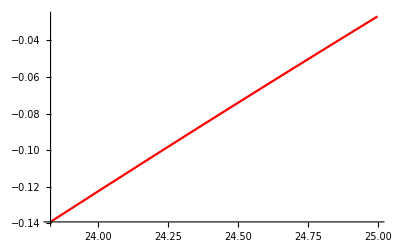

```mathematica
uSLplot=Plot[ UnitConvert[1/(β e)ySL[x*Quantity[10^(-10),"Meters"]/a],"SIBase"],{x,23.83,23.83+nuδCL},PlotStyle->Red]
```

## DL

#### dimensionless

```mathematica
yDL[x]
```

-65.9222 BesselK[0,3.51168 x]

#### plots with dimensions

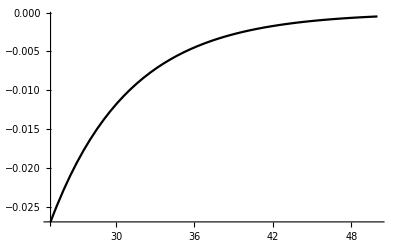

```mathematica
uDLplot=Plot[{UnitConvert[1/(β e)yDL[x*Quantity[10^(-10),"Meters"]/a],"SIBase"]},{x,23.83+nuδCL,50},PlotRange->Full,PlotStyle->Black,PlotLegends->"Expressions"]
```

```mathematica
UnitConvert[UnitConvert[1/(β e)yDL[(23.83+1.1012732237538216)*Quantity[10^(-10),"Meters"]/a],"SIBase"],"Volts"]
```

-0.0272628 V

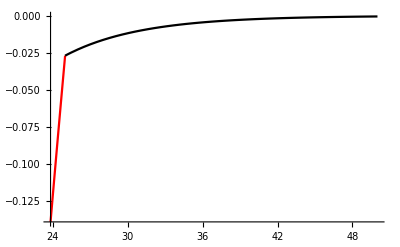

```mathematica
Show[uSLplot,uDLplot,PlotRange->All]
```

## 3. BDL vs “f”

eqn 44

```mathematica
fpH7 = 1-2/(1+√(1+√((-p/Log[δ])^2+1)))
```

0.440113

eqn 45 - NLDH

```mathematica
fc1pH7 = 1-4/(2+√(Abs[BDL]^2+4))
```

0.493502

eqn 46 - NLDH

```mathematica
fc2pH7 = 1-4/(2+√((Abs[BDL]*ArcSinh[BDL/2])^2+4))
```

0.663367

eqn 47 - Manning

```mathematica
fMpH7 = 1-2/Abs[BDL]
```

0.639502

## 4. Current

Transversal (Axial) Current

## SL

```mathematica
ΔVSLt=Vo
currRadial=CurrentTransSL
```

0.15

-15092.5 statC/(s statV)

```mathematica
(*currRadial=CurrentTransSL/.ΔVSLt->Vo*)
```

#### CGS

```mathematica
currRadial*UnitConvert[uVo,"StatVolts"]
```

-7.55149 statC/s

```mathematica
ItSLcgs =UnitConvert[currRadial*UnitConvert[uVo,"StatVolts"],"StatAmperes"]
```

-7.55149 statA

#### SI

```mathematica
ItSLsi =UnitConvert[ UnitSimplify[currRadial]*uVo,"Amperes"]
```

-2.51891×10^-9 A

## DL

```mathematica
ΔVDLt=Vo
```

0.15

```mathematica
CurrentTransDL
```

85910.8 statC/(s statV)

#### CGS

```mathematica
UnitConvert[CurrentTransDL,"Seconds"*"StatCoulombs"^2/("Grams"*"Centimeters"^2)]*UnitConvert[uVo,"StatVolts"]
```

42.9852 s statC^2 statV/(g cm^2)

```mathematica
ItDLcgs =UnitConvert[ UnitSimplify[CurrentTransDL]*uVo,"StatAmperes"]
```

42.9852 statA

#### SI

```mathematica
ItDLsi =UnitConvert[ UnitSimplify[CurrentTransDL]*uVo,"Amperes"]
```

1.43383×10^-8 A

Longitudinal (Axial) Current

## SL

```mathematica
ΔVSLl=Vo
ilSL=IlSL
```

0.15

7.04668 statC/(s statV)

```mathematica
(*ilSL=IlSL/.ΔVSLl->Vo*)
```

```mathematica
(*IlSL=ilSL/.ΔV->Vo*)
```

```mathematica
ilSL*uVo
```

0.00352578 statC/s

#### CGS

```mathematica
UnitConvert[ilSL,"Seconds"*"StatCoulombs"^2/("Grams"*"Centimeters"^2)]*UnitConvert[uVo,"StatVolts"]
```

0.00352578 s statC^2 statV/(g cm^2)

```mathematica
Ilslcgs=UnitConvert[ilSL*uVo,"StatAmperes"]
```

0.00352578 statA

```mathematica
UnitConvert[IlcSL (Quantity[0.05, "Volts"]),"StatAmperes"]
```

UnitConvert[IlcSL (0.05 V),StatAmperes]

#### SI

```mathematica
Ilslsi=UnitConvert[ilSL*uVo,"Amperes"]
```

1.17607×10^-12 A

## DL

```mathematica
ΔVDLl=Vo
ilDL=IlDL*uVo
```

0.15

0.362782 statC/s

```mathematica
(*ilDL=IlDL*uVo/.ΔVDLl->Vo*)
```

#### CGS

```mathematica
IlDLcgs=UnitConvert[ilDL,"StatAmperes"]
```

0.362782 statA

#### SI

```mathematica
IlDLsi=UnitConvert[ilDL,"Amperes"]
```

1.21011×10^-10 A

## 5. Resistance

Transversal (Axial) Resistance

## SL

```mathematica
RtSL
```

-9.93869×10^-6 s statV/statC

```mathematica
RtSLsi=UnitConvert[RtSL,"Ohms"]
```

-8.93245×10^6 Ω

```mathematica
uRtSLsi=Abs[RtSLsi]
```

8.93245×10^6 Ω

## DL

```mathematica
RtDL
```

4.19584×10^-6 s statV/statC

```mathematica
RtDLsi=UnitConvert[RtDL,"Ohms"]
```

3.77103×10^6 Ω

```mathematica
uRtDLsi=RtDLsi
```

3.77103×10^6 Ω

```mathematica
(*PathforMacBox - /Users/hunleyc/Desktop/00_Research/00_OtherFolders/00_JACFC_Results/Intracellular/postInflux/inputVoltage_0p15V/082120/preInflux_cCaEQ50nM/08-21-2020__20-24-35_simulationresults*)
(*uRtDLsi=Quantity[0.524*10^7,"Ohms"]*)
```

```mathematica
1.0868426051953934*^7/(4.74*10^6)
```

2.29292

## Equivalent Resistance

```mathematica
uRtEqsi =uRtDLsi +uRtSLsi
```

1.27035×10^7 Ω

Longitudinal (Axial) Resistance

## SL

```mathematica
RlSL
```

0.0212866 s statV/statC

```mathematica
RlSLsi=UnitConvert[RlSL,"Ohms"]
```

1.91315×10^10 Ω

```mathematica
uRlSLsi=RlSLsi
```

1.91315×10^10 Ω

## DL

```mathematica
RlDL
```

0.000206879 s statV/statC

```mathematica
RlDLsi=UnitConvert[RlDL,"Ohms"]
```

1.85934×10^8 Ω

```mathematica
uRlDLsi=RlDLsi
```

1.85934×10^8 Ω

```mathematica
(*PathforMacBox - /Users/hunleyc/Desktop/00_Research/00_OtherFolders/00_JACFC_Results/Intracellular/postInflux/inputVoltage_0p15V/082120/preInflux_cCaEQ50nM/08-21-2020__20-24-35_simulationresults*)
(*uRlDLsi=Quantity[0.199*10^9,"Ohms"]*)
```

```mathematica
1.7434096079950902*^8/(195*10^6)
```

0.894056

## Equivalent Resistance

```mathematica
uRlEqsi = uRlDLsi*uRlSLsi /(uRlDLsi+uRlSLsi)
```

1.84144×10^8 Ω

## 6. Capacitance

## SL

### q, L, M, NN terms

```mathematica
ζv =2*δ √(1/(3+δ^2))
```

0.907227

#### for q

```mathematica
(*BSL=*)4 π lBSL zp a σo/eo*(1/(4 π ϵo))
```

-1.62686×10^23 kg m^2 statC/(s^4 A^2 erg)

```mathematica
(*p =*) BSL/(2 εSL)δ
```

-9.69994

```mathematica
(*ζζ =√(ζ^2+(9 (1-δ^2)δ^2 p^2)/(5(3+δ^2)^3))*)
```

```mathematica
(*q =*)√(Expand[ζζ^2 p^2]+1)
```

√(1+0.484961 ζζ^2)

#### check q

```mathematica
(*α=(9 δ^2 (1-δ^2))/(5 (3+δ^2)^3)*)
```

```mathematica
γSL=UnitConvert[(2 a lBSL π zp δ)/(eo εSL)*(1/(4 π ϵo)),"Meters"^2/"Coulombs"]
```

248.519 m^2/C

```mathematica
(*p=γ σo*)
```

```mathematica
(*q=√(Expand[(γ^2 ζ^2 +α γ^4 σo^2)σo^2]+1)*)
```

#### L, M, NN in SI

```mathematica
L=UnitSimplify[1/(8 eo zp β)εSL^2 (-1+xcεDL^2 (1-2 Log[xcεDL]))]
```

-0.000229703 V

```mathematica
M=UnitSimplify[(4 a π xcεDL Log[xcεDL])/ϵSL(1/(4 π ϵo))]
```

2.69888 m V^2/N

```mathematica
NN=UnitSimplify[(8 a π BesselK[0,xcεDL εDL])/(ϵDL εDL BesselK[1,εDL])(1/(4 π ϵo))]
```

1.41974 m V^2/N

#### a check with SI units for L, M, NN

```mathematica
(*LSI =UnitSimplify[ (εSLSI^2 (-1+xcεDL^2 (1-2 Log[xcεDL])))/(8 eoSI zp βSI)]*)
```

```mathematica
(*MSI=UnitSimplify[(4 aSI π xcεDL Log[xcεDL])/ϵSL(1/(4 π ϵo))]*)
```

```mathematica
(*NNSI=UnitSimplify[(8 aSI π BesselK[0,xcεDL εDL])/(ϵDL εDLSI BesselK[1,εDL])(1/(4 π ϵo))]*)
```

### constants a0, a1, a2, a3

```mathematica
UnitConvert[a0SL,"Coulombs"/"Meters"^2]
```

0.0000673871 C/m^2

```mathematica
UnitConvert[a1SL,"Coulombs"/"Meters"^2/"Volts"]
```

0.293374 C/(m^2 V)

```mathematica
UnitConvert[a2SL,"Coulombs"/"Meters"^2/"Volts"^2]
```

0.0460446 C/(m^2 V^2)

```mathematica
UnitConvert[a3SL,"Coulombs"/"Meters"^2/"Volts"^3]
```

66.8177 C/(m^2 V^3)

### bSL

```mathematica
bSL
```

-0.156949 /V

```mathematica
bSLsi= UnitConvert[bSL,"Volts"]
```

-0.156949 /V

```mathematica
ubSLsi=bSLsi
```

-0.156949 /V

```mathematica
bSLVoEQ0p15VepsiEQ5cCa1mM=ubSLsi
```

-0.156949 /V

### CoSL

```mathematica
Coslsi=UnitConvert[a1SL,"Farads"/"Meters"^2]
```

0.293374 F/m^2

```mathematica
CoSLsi = UnitConvert[2*Pi*l*a*Coslsi,"Farads"]
```

2.37202×10^-17 F

```mathematica
uCoSLsi=CoSLsi
```

2.37202×10^-17 F

```mathematica
CoSLVoEQ0p15VepsiEQ5cCa1mM=uCoSLsi
```

2.37202×10^-17 F

## DL

### q, A, W terms

#### check q

```mathematica
(*ζv =2*δ √(1/(3+δ^2))*)
```

```mathematica
(*(2 a lBDL π zp δ)/(eo εDL)*)
```

```mathematica
(*γDL=UnitConvert[(2 a lBDL π zp δ)/(eo εDL)*(1/(4 π ϵo)),"Meters"^2/"Coulombs"]*)
```

#### A, W

```mathematica
(*A = UnitConvert[(8 a π BesselK[0,xc εDL])/(ϵDL εDL BesselK[1,εDL]),"SIBase"]*)
```

```mathematica
(*W=UnitConvert[A/(4 π ϵo),"Volts"*"Meters"^2/"Coulombs"]*)
```

#### a check with SI units for L, M, NN

```mathematica
(*LSI =UnitSimplify[ (εSLSI^2 (-1+xcεDL^2 (1-2 Log[xcεDL])))/(8 eoSI zp βSI)]*)
```

```mathematica
(*MSI=UnitSimplify[(4 aSI π xcεDL Log[xcεDL])/ϵSL(1/(4 π ϵo))]*)
```

```mathematica
(*NNSI=UnitSimplify[(8 aSI π BesselK[0,xcεDL εDL])/(ϵDL εDLSI BesselK[1,εDL])(1/(4 π ϵo))]*)
```

### constants a0, a1, a2, a3

```mathematica
(*a0DL*)
```

```mathematica
(*UnitConvert[a1DL,"Coulombs"/"Meters"^2/"Volts"]*)
```

```mathematica
(*a2DL*)
```

```mathematica
(*a3DL*)
```

```mathematica
(*UnitConvert[a3DL,"Coulombs"/"Meters"^2/"Volts"^3]*)
```

### bDL

```mathematica
(*ubDLsi=bDL*)
```

```mathematica
(*PathforMacBox - /Users/hunleyc/Desktop/00_Research/00_OtherFolders/00_JACFC_Results/Intracellular/postInflux/inputVoltage_0p15V/082120/preInflux_cCaEQ50nM/08-21-2020__20-24-35_simulationresults*)
```

```mathematica
ubDLsi=-1/2 Quantity[0.60217244692724126,1/"Volts"]
```

-0.301086 /V

```mathematica
bDL= ubDLsi
```

-0.301086 /V

```mathematica
bDLVoEQ0p15VepsiEQ5cCa1mM=ubDLsi
```

-0.301086 /V

### CoDL

```mathematica
(*Codlsi = UnitConvert[a1DL,"Farads"/"Meters"^2]*)
```

```mathematica
(*CoDLsi=UnitConvert[2*Pi*l*a*Codlsi,"Farads"]*)
```

```mathematica
(*uCoDLsi=CoDLsi*)
```

```mathematica
(*PathforMacBox - /Users/hunleyc/Desktop/00_Research/00_OtherFolders/00_JACFC_Results/Intracellular/preInflux/NaKCa_ClHPO4m2/07-30-2020__04-53-52_simulationresults*)
```

```mathematica
CoDLsi=Quantity[0.81459036216125424*2*π*(23.83*10^(-10))*(5.4*10^(-9)),"Farads"]
```

6.58623×10^-17 F

```mathematica
uCoDLsi=CoDLsi
```

6.58623×10^-17 F

```mathematica
CoDLVoEQ0p15VepsiEQ5cCa1mM=uCoDLsi
```

6.58623×10^-17 F

## Equivalent Capacitance and b parameter

### b parameter

```mathematica
btsi=(bSL  CoDLsi+bDL  CoSLsi)/(CoSLsi+CoDLsi)
```

-0.195114 /V

```mathematica
btsi
```

-0.195114 /V

```mathematica
ubtsi=btsi
```

-0.195114 /V

```mathematica
(*ubtsi=0.4489584775618532(*b parameter from SP1*)*)
```

```mathematica
0.4489584775618532
```

0.448958

```mathematica
(*PathforMacPro - /Users/chris/Desktop/Research/Research/00_OtherFolders/00_JACFC_Results/Divalent_Results/CaCl_KCl/pH7/cCaEQ0p005M/07-08-2020__18-03-51_simulationresults*)
(*ubtsi=Quantity[3.2381738940483373,1/"Volts"]*)
```

### Capacitance

```mathematica
uCoEqsi = (uCoSLsi*uCoDLsi)/(uCoSLsi+uCoDLsi)
```

1.74394×10^-17 F

```mathematica
(*PathforMacPro - /Users/chris/Desktop/Research/Research/00_OtherFolders/00_JACFC_Results/Divalent_Results/CaCl_KCl/pH7/cCaEQ0p005M/07-08-2020__18-03-51_simulationresults*)
(*uCoEqsi =Quantity[0.85545751961533945*2*π*(23.83*10^(-10))*(5.4*10^(-9)),"Farads"]*)
```

## 8. Self Inductance

## SL:

```mathematica
LSL
```

0

```mathematica
LSLsi=LSL
```

0

## DL:

```mathematica
LDL
```

0

```mathematica
LDLsi=LDL
```

0

## Equivalent:

```mathematica
LEq
```

0

#### CGS

```mathematica
LEqcgs=LEq
```

0

#### SI

```mathematica
LEqsi=LEq
```

0

## 8. Clear Parameters

### Clear Units

```mathematica
nuVo=QuantityMagnitude[uVo]
```

0.15

```mathematica
nul =QuantityMagnitude[l]
```

5.4×10^-9

#### Total

```mathematica
nuRtEq =QuantityMagnitude[uRtEqsi ]
```

1.27035×10^7

```mathematica
(*nuRtEq=4.748252092201714*^6*)
```

```mathematica
nuRlEq =QuantityMagnitude[uRlEqsi ]
```

1.84144×10^8

```mathematica
nuRtEq/nuRlEq
```

0.0689867

```mathematica
(*nuRlEq=195.0272920991057128*^6*)
```

```mathematica
(*MM: added this*)
```

```mathematica
(*nuZe=QuantityMagnitude[uZesi ]*)
```

```mathematica
(*nuZe=4.8972506598688365*^9*)
```

```mathematica
(*MM: added this*)
```

```mathematica
(*Vo=QuantityMagnitude[uVo]*)
```

```mathematica
(*MM: this parameter is negative*)
```

```mathematica
nubt=QuantityMagnitude[ubtsi]
```

-0.195114

```mathematica
(*nubt=0.47*)
```

```mathematica
nuCoEq=QuantityMagnitude[uCoEqsi]
```

1.74394×10^-17

```mathematica
(*l =5.4*10^(-10)*)
```

```mathematica
(*μ3 =(24 RlEq)/Ze*)
```

```mathematica
(*μ2 =(6 RtEq)/Ze*)
```

## 9. Impedance

### NEW IMPEDANCE ( newImpead )

```mathematica
Impedance=Sqrt[32/225 (25 π^4 nuRlEq^2+80 nubt π^4 nuRlEq nuRtEq nuVo+64 nubt^2 π^4 nuRtEq^2 nuVo^2)+8/225 √(-5625 π^4 nuRlEq^4+10000 π^8 nuRlEq^4-11250 π^4 nuRlEq^3 nuRtEq-5625 π^4 nuRlEq^2 nuRtEq^2-18000 nubt π^4 nuRlEq^3 nuRtEq nuVo+64000 nubt π^8 nuRlEq^3 nuRtEq nuVo-36000 nubt π^4 nuRlEq^2 nuRtEq^2 nuVo-18000 nubt π^4 nuRlEq nuRtEq^3 nuVo-14400 nubt^2 π^4 nuRlEq^2 nuRtEq^2 nuVo^2+153600 nubt^2 π^8 nuRlEq^2 nuRtEq^2 nuVo^2-28800 nubt^2 π^4 nuRlEq nuRtEq^3 nuVo^2-14400 nubt^2 π^4 nuRtEq^4 nuVo^2+163840 nubt^3 π^8 nuRlEq nuRtEq^3 nuVo^3+65536 nubt^4 π^8 nuRtEq^4 nuVo^4)];
```

```mathematica
nuZe= Impedance
```

4.8268×10^9

## Soliton

### KdV equation and more parameters Here we . . - solve for soliton

#### gamma

```mathematica
(*propagation of electrical impulse along actin filaments*)
(*alfa=(L/Ze+Co*Ze)*)

gamma=3*(LEq/nuZe+nuCoEq*nuZe)/(nubt*nuZe^(3/2)*nuCoEq);
```

#### μ2

```mathematica
μ2=nuRtEq*6/nuZe
```

0.0157912

#### μ3

```mathematica
μ3=nuRlEq*24/nuZe
```

0.915608

#### wo

```mathematica
(*      (*max possible value is 4.8*) (*Subscript[Ω, o] in equation 12 from Cameroon Paper*)*)
(* MM: I used the expression from our paper*)
```

```mathematica
wo=(nuVo*12/(Abs[gamma]*nuZe^(1/2)))^(1/2)
```

0.342153

#### alfa

```mathematica
alfa=(LEq/nuZe+nuCoEq*nuZe)
```

8.41767×10^-8

#### beta

```mathematica
beta=2*nul;
```

#### Ω

```mathematica
(*cwq=1/Sqrt[LEq*CEq];*)
```

```mathematica
Ω[τ1_]:=√((wo^2 ⅇ^(-(4 τ1 μ3)/3))/(1+((4 μ2  wo^2)/(5μ3))(1-ⅇ^(-(4 τ1 μ3)/3))));
```

#### ηe

```mathematica
(*MM: I changed from eta to etae. from some reason eta is protected....*)
```

```mathematica
ηe[τ1_] := -((5 (4 μ3 τ1+3 Log[5 μ3]-3 Log[-4 wo^2 μ2+ⅇ^((4 μ3 τ1)/3) (4 wo^2 μ2+5 μ3)]))/(4 μ2));
```

#### cW

```mathematica
cW[psi_,taoprima_]:=-2*(Ω[taoprima])^2*(Sech[Ω[taoprima]*(psi-ηe[taoprima])])^2;
```

#### velocityprop

```mathematica
(*MM: from our paper*)
```

```mathematica
(*velocityprop2[t_]:=4*wo^2* ⅇ^((-4 t μ3)/3)/(1+((4 μ2  wo^2)/(5μ3))(1-ⅇ^(-(4 t μ3)/3)));*)
```

```mathematica
velocityprop[t_]:=-1/(4 μ2)5 (4 μ3-(4 ⅇ^((4 t μ3)/3) μ3 (4 wo^2 μ2+5 μ3))/(-4 wo^2 μ2+ⅇ^((4 t μ3)/3) (4 wo^2 μ2+5 μ3)));
```

#### decaytime

```mathematica
decaytime=w/. Solve[Ω[w]==0.1*Ω[0],w][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

3.77092

```mathematica
(velocityprop[0]/24+1)/alfa*beta
```

0.130805

#### vavg

```mathematica
vavg = Integrate[(velocityprop[t/alfa/24]/24+1)/alfa*beta,{t,0,24*decaytime*alfa}]/(24*decaytime*alfa)
```

0.128839

```mathematica
avgVelocityVoEQ0p15VepsiEQ5cCaEQ1mM=vavg
```

0.128839

#### tmax

```mathematica
te=24*decaytime*alfa
tmax=te;
```

7.61815×10^-6

```mathematica
tmaxVoEQ0p15VϵSLEQ05cCaEQ1mM=7.241527043387776*^-6
```

7.24153×10^-6

#### xmax

```mathematica
xe=Abs[(1-te/alfa)*beta]*(1*10^6)
xmax=xe;
```

0.966621

```mathematica
xmaxVoEQ0p15VϵSLEQ05cCaEQ1mM=xmax
```

0.966621

#### velo

```mathematica
velo=xe/te*(1*10^-6)
```

0.126884

```mathematica
velocityVoEQ0p15VepsiEQ5cCaEQ1mM=velo
```

0.126884

#### Wx

```mathematica
(* with Dimensions *)
```

```mathematica
Wx[x_,t_]:=-2*(Ω[t/alfa/24])^2*(Sech[Ω[t/alfa/24]*((x/beta-t/alfa)-ηe[t/alfa/24])])^2
```

```mathematica
Wx[x,t]
```

-((0.234137 ⅇ^(-604290. t) Sech[0.342153 √(ⅇ^(-604290. t)/(1+0.00161524 (1-ⅇ^(-604290. t)))) (-1.18798×10^7 t+9.25926×10^7 x+79.1581 (4.56381+1.81287×10^6 t-3 Log[-0.00739461+4.58543 ⅇ^(604290. t)]))]^2)/(1+0.00161524 (1-ⅇ^(-604290. t))))

#### Snapshot times for Soliton Plot

```mathematica
0
24*decaytime*alfa/10
24*decaytime*alfa/5
24*decaytime*alfa/3
24*decaytime*alfa/2
24*decaytime*alfa
```

0

7.61815×10^-7

1.52363×10^-6

2.53938×10^-6

3.80908×10^-6

7.61815×10^-6

Plots

### Velocity plots

#### Total

Intracellular conditions

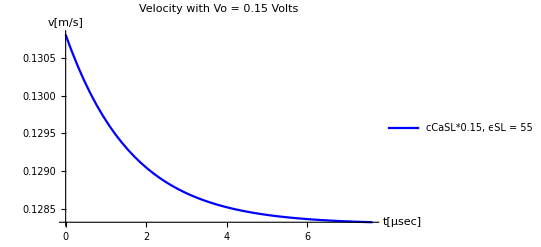

```mathematica
Print["Intracellular conditions"]

veloSP2=Plot[(velocityprop[t/alfa/24*10^-6]/24+1)/alfa*beta,{t,0,24*decaytime*alfa*10^6},PlotLegends->{"cCaSL*0.15, ϵSL = 55"},PlotLabel->"Velocity with Vo = 0.15 Volts",PlotStyle->Blue,PlotRange->Full,Axes->True,AxesLabel->{"t[μsec]","v[m/s]"}]
```

```mathematica
24*0.329*3.6
```

28.4256

```mathematica
veloSP2Data=Cases[veloSP2,Line[{x__}]->x,∞];
```

{{1.55473×10^-7,0.130805},{0.00233662,0.130801},{0.00467309,0.130798},{0.00934603,0.130791},{0.0186919,0.130777},{0.0373837,0.130749},{0.0747672,0.130694},{0.149534,0.130588},{0.311646,0.130375},{0.463015,0.130193},{0.611415,0.130031},{0.772393,0.12987},{0.922628,0.129734},{1.08544,0.1296},{1.24528,0.12948},{1.39439,0.129378},{1.55606,0.129278},{1.707,0.129193},{1.85497,0.129117},{2.01551,0.129041},{2.16531,0.128977},{2.32769,0.128914},{2.4871,0.128858},{2.63577,0.12881},{2.79702,0.128763},{2.94752,0.128723},{3.1106,0.128683},{3.27071,0.128648},{3.42008,0.128618},{3.58203,0.128589},{3.73323,0.128563},{3.88146,0.128541},{4.04228,0.128519},{4.19235,0.1285},{4.35499,0.128481},{4.51467,0.128465},{4.66361,0.128451},{4.82512,0.128437},{4.97589,0.128425},{5.12369,0.128415},{5.28407,0.128404},{5.43371,0.128395},{5.59592,0.128387},{5.74739,0.128379},{5.8959,0.128372},{6.05698,0.128366},{6.20731,0.12836},{6.37023,0.128355},{6.53017,0.12835},{6.67938,0.128346},{6.84116,0.128342},{6.9922,0.128338},{7.14026,0.128335},{7.30091,0.128332},{7.45082,0.128329},{7.45343,0.128329},{7.45605,0.128329},{7.46127,0.128329},{7.47173,0.128329},{7.49265,0.128329},{7.53448,0.128328},{7.5371,0.128328},{7.53971,0.128328},{7.54494,0.128328},{7.5554,0.128328},{7.57632,0.128327},{7.57893,0.128327},{7.58155,0.128327},{7.58678,0.128327},{7.59724,0.128327},{7.59985,0.128327},{7.60247,0.128327},{7.6077,0.128327},{7.61031,0.128327},{7.61292,0.128327},{7.61554,0.128327},{7.61815,0.128327}}

### Soliton Peak Attenuation plots

```mathematica
(*MM: added ABS[] and divided by 24, not 12*)
```

#### Total

Intracellular conditions

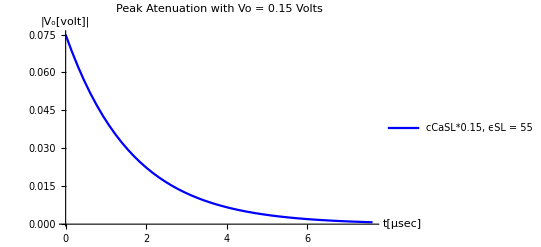

```mathematica
Print["Intracellular conditions"]

peakDecaySP2wSP1Capa=Plot[{Abs[Ω[t/alfa/24*10^-6]^2*gamma*nuZe^(1/2)/24]},{t,0,24*decaytime*alfa*10^6},PlotStyle->Blue,PlotLegends->{"cCaSL*0.15, ϵSL = 55"},PlotLabel->"Peak Atenuation with Vo = 0.15 Volts",Axes->True,AxesLabel->{"t[μsec]","|V_o[volt]|"},PlotRange->All]
```

```mathematica
peakDecaySP2wSP1CapaData=Cases[peakDecaySP2wSP1Capa,Line[{x__}]->x,∞];
```

{{1.55473×10^-7,0.075},{0.00233662,0.074894},{0.00467309,0.0747882},{0.00934603,0.0745769},{0.0186919,0.0741563},{0.0373837,0.0733221},{0.0747672,0.0716817},{0.149534,0.0685105},{0.311646,0.0621087},{0.463015,0.056673},{0.611415,0.0518066},{0.772393,0.0469995},{0.922628,0.0429168},{1.08544,0.0388921},{1.24528,0.0353084},{1.39439,0.0322641},{1.55606,0.0292591},{1.707,0.026707},{1.85497,0.0244215},{2.01551,0.0221624},{2.16531,0.0202435},{2.32769,0.0183507},{2.4871,0.0166649},{2.63577,0.0152325},{2.79702,0.0138179},{2.94752,0.0126163},{3.1106,0.011432},{3.27071,0.0103775},{3.42008,0.00948166},{3.58203,0.00859755},{3.73323,0.00784668},{3.88146,0.00717426},{4.04228,0.00650979},{4.19235,0.00594536},{4.35499,0.00538874},{4.51467,0.00489302},{4.66361,0.00447184},{4.82512,0.00405597},{4.97589,0.00370274},{5.12369,0.00338635},{5.28407,0.00307354},{5.43371,0.0028078},{5.59592,0.00254561},{5.74739,0.00232294},{5.8959,0.00212355},{6.05698,0.00192658},{6.20731,0.00175927},{6.37023,0.00159432},{6.53017,0.00144743},{6.67938,0.00132263},{6.84116,0.00119944},{6.9922,0.00109481},{7.14026,0.00100111},{7.30091,0.000908489},{7.45082,0.000829809},{7.45343,0.000828499},{7.45605,0.000827191},{7.46127,0.000824581},{7.47173,0.000819386},{7.49265,0.000809094},{7.53448,0.000788896},{7.5371,0.00078765},{7.53971,0.000786407},{7.54494,0.000783926},{7.5554,0.000778987},{7.57632,0.000769202},{7.57893,0.000767988},{7.58155,0.000766775},{7.58678,0.000764356},{7.59724,0.00075954},{7.59985,0.000758341},{7.60247,0.000757144},{7.6077,0.000754755},{7.61031,0.000753564},{7.61292,0.000752374},{7.61554,0.000751186},{7.61815,0.00075}}

Soliton Propagation plots

```mathematica
(*Vo=0.15V ϵSL = 78.358 cCa=50nM*)
tmaxVoEQ0p15VϵSLEQ78p358cCaEQ50nM=0.000016722898823157003
```

0.0000167229

```mathematica
(*Vo=0.05V ϵSL = 78.358 cCa=50nM*)
tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM=0.000016787268912085657
```

0.0000167873

```mathematica
tmaxThisFile=24*decaytime*alfa
```

7.61815×10^-6

## Soliton Normalized

#### Normalized - regular

Intracellular conditions at 0.05 and 0.15 molar concentration: A normalized plot

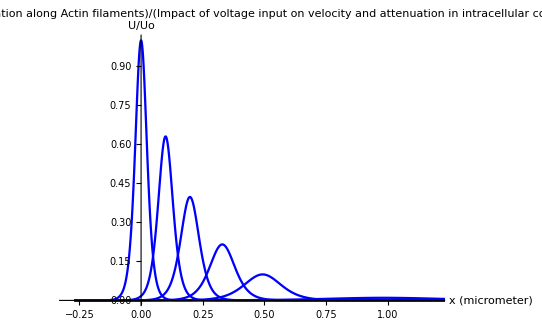

```mathematica
Print["Intracellular conditions at 0.05 and 0.15 molar concentration: A normalized plot"]

SolNormTot=Plot[ {-Wx[x*10^-6,0]/wo^2/2,
-Wx[x*10^-6,tmaxThisFile/10]/wo^2/2,
-Wx[x*10^-6,tmaxThisFile/5]/wo^2/2,
-Wx[x*10^-6,tmaxThisFile/3]/wo^2/2,
-Wx[x*10^-6,tmaxThisFile/2]/wo^2/2,
-Wx[x*10^-6,tmaxThisFile]/wo^2/2},{x,-25*beta*10^6,435*beta*10^6},PlotRange->{{-0.3,1.2},{0,1}},Axes->True,AxesLabel->{"x (micrometer)","U/Uo"},PlotLabel->Style["Soliton propagation along Actin filaments" /" in intracellular conditions" / "Impact of voltage input on velocity and attenuation",Black,FontSize->18,Bold],AxesStyle->Directive[Black,FontSize-> 18],TicksStyle->Directive[18],PlotStyle->{{Blue,Thickness[0.0030]},{Blue,Thickness[0.0030]},{Blue,Thickness[0.0030]},{Blue,Thickness[0.0030]},{Blue,Thickness[0.0030]},{Blue,Thickness[0.0030]},{Orange,Thickness[0.0030]},{Orange,Thickness[0.0030]},{Orange,Thickness[0.0030]},{Orange,Thickness[0.0030]},{Orange,Thickness[0.0030]}},PlotLegends->Placed[{},{0.87,0.6}],LabelStyle->{18}]
```

```mathematica
NormSolSP22Data=Cases[SolNormTot,Line[{x__}]->x,∞];
```

{{-0.27,1.48698×10^-7},{-0.268476,1.6377×10^-7},{-0.266953,1.80369×10^-7},{-0.265429,1.98651×10^-7},{-0.263905,2.18785×10^-7},{-0.262382,2.4096×10^-7},{-0.260858,2.65383×10^-7},{-0.259334,2.92281×10^-7},{-0.257811,3.21906×10^-7},{-0.256287,3.54533×10^-7},{-0.254763,3.90467×10^-7},{-0.253239,4.30044×10^-7},{-0.251716,4.73631×10^-7},{-0.250192,5.21637×10^-7},{-0.248668,5.74508×10^-7},{-0.247145,6.32738×10^-7},{-0.245621,6.9687×10^-7},{-0.244097,7.67502×10^-7},{-0.242574,8.45294×10^-7},{-0.24105,9.30969×10^-7},{-0.239526,1.02533×10^-6},{-0.238003,1.12925×10^-6},{-0.236479,1.24371×10^-6},{-0.234955,1.36977×10^-6},{-0.233432,1.5086×10^-6},{-0.231908,1.66151×10^-6},{-0.230384,1.82991×10^-6},{-0.228861,2.01538×10^-6},{-0.227337,2.21966×10^-6},{-0.225813,2.44463×10^-6},{-0.22429,2.69241×10^-6},{-0.222766,2.9653×10^-6},{-0.221242,3.26586×10^-6},{-0.219719,3.59687×10^-6},{-0.218195,3.96144×10^-6},{-0.216671,4.36295×10^-6},{-0.215148,4.80516×10^-6},{-0.213624,5.2922×10^-6},{-0.2121,5.82859×10^-6},{-0.210577,6.41935×10^-6},{-0.209053,7.06999×10^-6},{-0.207529,7.78658×10^-6},{-0.206006,8.5758×10^-6},{-0.204482,9.445×10^-6},{-0.202958,0.0000104023},{-0.201435,0.0000114566},{-0.199911,0.0000126178},{-0.198387,0.0000138967},{-0.196864,0.0000153052},{-0.19534,0.0000168565},{-0.193816,0.000018565},{-0.192293,0.0000204467},{-0.190769,0.000022519},{-0.189245,0.0000248015},{-0.187722,0.0000273152},{-0.186198,0.0000300837},{-0.184674,0.0000331329},{-0.183151,0.000036491},{-0.181627,0.0000401896},{-0.180103,0.0000442629},{-0.17858,0.0000487492},{-0.177056,0.0000536901},{-0.175532,0.0000591317},{-0.174008,0.0000651249},{-0.172485,0.0000717255},{-0.170833,0.0000796391},{-0.169181,0.0000884258},{-0.167529,0.0000981819},{-0.165877,0.000109014},{-0.164226,0.000121042},{-0.162574,0.000134396},{-0.160922,0.000149224},{-0.15927,0.000165688},{-0.157618,0.000183967},{-0.155966,0.000204263},{-0.154315,0.000226799},{-0.152663,0.00025182},{-0.151011,0.000279601},{-0.149359,0.000310446},{-0.147707,0.000344694},{-0.146055,0.000382719},{-0.144404,0.000424937},{-0.142752,0.000471813},{-0.1411,0.000523857},{-0.139448,0.000581641},{-0.137796,0.000645796},{-0.136144,0.000717025},{-0.134493,0.000796108},{-0.132841,0.000883909},{-0.131189,0.000981388},{-0.129537,0.00108961},{-0.127885,0.00120976},{-0.126233,0.00134315},{-0.124582,0.00149124},{-0.12293,0.00165565},{-0.121278,0.00183816},{-0.119626,0.00204076},{-0.117974,0.00226568},{-0.116322,0.00251535},{-0.114671,0.0027925},{-0.113019,0.00310014},{-0.111367,0.00344161},{-0.109715,0.00382061},{-0.108063,0.00424127},{-0.106411,0.00470814},{-0.10476,0.00522626},{-0.103108,0.00580123},{-0.101456,0.00643925},{-0.099804,0.00714719},{-0.0981522,0.00793265},{-0.0965003,0.00880405},{-0.0948485,0.0097707},{-0.0931967,0.0108429},{-0.0915448,0.0120321},{-0.089893,0.0133507},{-0.0882412,0.0148129},{-0.0865893,0.0164338},{-0.0849375,0.0182304},{-0.0832856,0.0202215},{-0.0816338,0.0224275},{-0.079982,0.0248711},{-0.0783301,0.0275772},{-0.0766783,0.0305731},{-0.0750265,0.0338888},{-0.0733746,0.0375571},{-0.0717228,0.041614},{-0.070071,0.0460985},{-0.0684191,0.0510534},{-0.0667673,0.056525},{-0.0652249,0.0621449},{-0.0636825,0.0683033},{-0.0621402,0.0750474},{-0.0605978,0.0824279},{-0.0590554,0.0904985},{-0.0575131,0.0993164},{-0.0559707,0.108942},{-0.0544283,0.119438},{-0.0528859,0.13087},{-0.0513436,0.143308},{-0.0498012,0.156819},{-0.0482588,0.171477},{-0.0467164,0.18735},{-0.0451741,0.20451},{-0.0420893,0.242954},{-0.040547,0.264359},{-0.0390046,0.287286},{-0.0359198,0.337844},{-0.0343775,0.365505},{-0.0328351,0.394741},{-0.0297504,0.45775},{-0.028208,0.491356},{-0.0266656,0.526192},{-0.0235809,0.598814},{-0.0174114,0.748273},{-0.015869,0.784452},{-0.0143266,0.819305},{-0.0127843,0.852365},{-0.0112419,0.883159},{-0.00969952,0.911215},{-0.00815715,0.936081},{-0.00661477,0.957338},{-0.0050724,0.974614},{-0.00353003,0.987597},{-0.00198766,0.996045},{-0.000445286,0.999801},{0.00109709,0.998793},{0.00263946,0.99304},{0.00418183,0.982651},{0.0057242,0.967821},{0.00726657,0.948821},{0.00880895,0.92599},{0.0103513,0.899722},{0.0118937,0.870453},{0.0134361,0.838643},{0.0149784,0.804767},{0.0165208,0.769298},{0.0196055,0.695398},{0.0211479,0.657811},{0.0226903,0.620304},{0.025775,0.5468},{0.0273174,0.511331},{0.0288598,0.476995},{0.0319445,0.412325},{0.0334566,0.382772},{0.0349688,0.354714},{0.0364809,0.328177},{0.037993,0.303168},{0.0395051,0.279676},{0.0410172,0.257673},{0.0440415,0.217969},{0.0455536,0.200165},{0.0470657,0.183646},{0.0485778,0.168348},{0.0500899,0.154205},{0.051602,0.14115},{0.0531142,0.129117},{0.0561384,0.107854},{0.0576505,0.0984987},{0.0591626,0.0899141},{0.0606747,0.0820438},{0.0621869,0.0748341},{0.063699,0.0682346},{0.0652111,0.0621976},{0.0667232,0.0566785},{0.0682353,0.0516357},{0.0697474,0.0470304},{0.0712596,0.0428266},{0.0727717,0.0389909},{0.0742838,0.0354924},{0.0757959,0.0323025},{0.077308,0.029395},{0.0788201,0.0267455},{0.0803323,0.0243319},{0.0818444,0.0221336},{0.0833565,0.0201318},{0.0848686,0.0183094},{0.0863807,0.0166506},{0.0878928,0.0151409},{0.089405,0.0137671},{0.0909171,0.0125172},{0.0924292,0.0113801},{0.0939413,0.0103458},{0.0954534,0.00940502},{0.0969655,0.00854942},{0.0984777,0.00777136},{0.0999898,0.00706385},{0.101502,0.00642055},{0.103014,0.00583566},{0.104526,0.00530391},{0.106038,0.00482049},{0.10755,0.00438104},{0.109062,0.00398157},{0.110575,0.00361846},{0.112087,0.00328841},{0.113599,0.00298842},{0.115111,0.00271576},{0.116623,0.00246794},{0.118135,0.00224271},{0.119647,0.00203802},{0.121159,0.00185199},{0.122672,0.00168293},{0.124184,0.00152929},{0.125696,0.00138967},{0.127208,0.00126278},{0.12872,0.00114747},{0.13036,0.00103426},{0.132001,0.000932216},{0.133641,0.000840234},{0.135281,0.000757324},{0.136921,0.000682592},{0.138562,0.000615232},{0.140202,0.000554518},{0.141842,0.000499794},{0.143483,0.000450469},{0.145123,0.000406011},{0.146763,0.00036594},{0.148403,0.000329824},{0.150044,0.000297271},{0.151684,0.00026793},{0.153324,0.000241486},{0.154964,0.00021765},{0.156605,0.000196168},{0.158245,0.000176805},{0.159885,0.000159354},{0.161526,0.000143625},{0.163166,0.000129448},{0.164806,0.000116671},{0.166446,0.000105155},{0.168087,0.000094775},{0.169727,0.0000854199},{0.171367,0.0000769882},{0.173008,0.0000693888},{0.174648,0.0000625395},{0.176288,0.0000563662},{0.177928,0.0000508023},{0.179569,0.0000457876},{0.181209,0.0000412679},{0.182849,0.0000371943},{0.18449,0.0000335229},{0.18613,0.0000302138},{0.18777,0.0000272313},{0.18941,0.0000245433},{0.191051,0.0000221206},{0.192691,0.0000199371},{0.194331,0.000017969},{0.195971,0.0000161953},{0.197612,0.0000145966},{0.199252,0.0000131558},{0.200892,0.0000118571},{0.202533,0.0000106867},{0.204173,9.63179×10^-6},{0.205813,8.68102×10^-6},{0.207453,7.8241×10^-6},{0.209094,7.05176×10^-6},{0.210734,6.35567×10^-6},{0.212374,5.72829×10^-6},{0.214015,5.16284×10^-6},{0.215655,4.6532×10^-6},{0.217295,4.19387×10^-6},{0.218935,3.77989×10^-6},{0.220576,3.40677×10^-6},{0.222216,3.07048×10^-6},{0.223856,2.76738×10^-6},{0.225497,2.49421×10^-6},{0.227137,2.248×10^-6},{0.228777,2.02609×10^-6},{0.230417,1.82609×10^-6},{0.232058,1.64584×10^-6},{0.233698,1.48337×10^-6},{0.235229,1.34625×10^-6},{0.23676,1.2218×10^-6},{0.23829,1.10886×10^-6},{0.239821,1.00636×10^-6},{0.241352,9.13331×10^-7},{0.242883,8.28903×10^-7},{0.244414,7.5228×10^-7},{0.245944,6.8274×10^-7},{0.247475,6.19628×10^-7},{0.249006,5.6235×10^-7},{0.250537,5.10366×10^-7},{0.252068,4.63188×10^-7},{0.253599,4.20371×10^-7},{0.255129,3.81513×10^-7},{0.25666,3.46246×10^-7},{0.258191,3.14239×10^-7},{0.259722,2.85191×10^-7},{0.261253,2.58828×10^-7},{0.262783,2.34902×10^-7},{0.264314,2.13188×10^-7},{0.265845,1.93481×10^-7},{0.267376,1.75596×10^-7},{0.268907,1.59364×10^-7},{0.270437,1.44632×10^-7},{0.271968,1.31262×10^-7},{0.273499,1.19129×10^-7},{0.27503,1.08116×10^-7},{0.276561,9.81222×10^-8},{0.278092,8.90519×10^-8},{0.279622,8.08199×10^-8},{0.281153,7.3349×10^-8},{0.282684,6.65687×10^-8},{0.284215,6.04151×10^-8},{0.285746,5.48303×10^-8},{0.287276,4.97619×10^-8},{0.288807,4.51619×10^-8},{0.290338,4.09872×10^-8},{0.291869,3.71983×10^-8},{0.2934,3.37597×10^-8},{0.294931,3.0639×10^-8},{0.296461,2.78067×10^-8},{0.297992,2.52363×10^-8},{0.299523,2.29035×10^-8},{0.301054,2.07863×10^-8},{0.302585,1.88648×10^-8},{0.304115,1.7121×10^-8},{0.305646,1.55383×10^-8},{0.307177,1.4102×10^-8},{0.308708,1.27984×10^-8},{0.310239,1.16153×10^-8},{0.31177,1.05416×10^-8},{0.3133,9.56713×10^-9},{0.314831,8.68275×10^-9},{0.316362,7.88012×10^-9},{0.317893,7.15169×10^-9},{0.319424,6.49059×10^-9},{0.320954,5.89061×10^-9},{0.322485,5.34608×10^-9},{0.324016,4.85189×10^-9},{0.325547,4.40339×10^-9},{0.327078,3.99634×10^-9},{0.328608,3.62692×10^-9},{0.330139,3.29165×10^-9},{0.33167,2.98737×10^-9},{0.333329,2.68929×10^-9},{0.334988,2.42096×10^-9},{0.336647,2.17939×10^-9},{0.338306,1.96193×10^-9},{0.339965,1.76617×10^-9},{0.341624,1.58995×10^-9},{0.343283,1.4313×10^-9},{0.344942,1.28849×10^-9},{0.346601,1.15992×10^-9},{0.34826,1.04419×10^-9},{0.349919,9.39997×10^-10},{0.351578,8.46205×10^-10},{0.353237,7.61771×10^-10},{0.354896,6.85762×10^-10},{0.356555,6.17337×10^-10},{0.358214,5.55739×10^-10},{0.359873,5.00288×10^-10},{0.361532,4.50369×10^-10},{0.363191,4.05432×10^-10},{0.36485,3.64978×10^-10},{0.366509,3.2856×10^-10},{0.368168,2.95777×10^-10},{0.369827,2.66264×10^-10},{0.371486,2.39697×10^-10},{0.373145,2.1578×10^-10},{0.374804,1.94249×10^-10},{0.376463,1.74867×10^-10},{0.378122,1.57419×10^-10},{0.37978,1.41712×10^-10},{0.381439,1.27572×10^-10},{0.383098,1.14843×10^-10},{0.384757,1.03384×10^-10},{0.386416,9.30683×10^-11},{0.388075,8.37819×10^-11},{0.389734,7.54222×10^-11},{0.391393,6.78966×10^-11},{0.393052,6.11219×10^-11},{0.394711,5.50232×10^-11},{0.39637,4.9533×10^-11},{0.398029,4.45906×10^-11},{0.399688,4.01414×10^-11},{0.401347,3.61361×10^-11},{0.403006,3.25305×10^-11},{0.404665,2.92846×10^-11},{0.406324,2.63626×10^-11},{0.407983,2.37321×10^-11},{0.409642,2.13642×10^-11},{0.411301,1.92324×10^-11},{0.41296,1.73134×10^-11},{0.414619,1.55859×10^-11},{0.416278,1.40308×10^-11},{0.417937,1.26308×10^-11},{0.419596,1.13705×10^-11},{0.421255,1.02359×10^-11},{0.422914,9.2146×10^-12},{0.424573,8.29517×10^-12},{0.426232,7.46748×10^-12},{0.427891,6.72238×10^-12},{0.42955,6.05162×10^-12},{0.431209,5.4478×10^-12},{0.432868,4.90422×10^-12},{0.434527,4.41488×10^-12},{0.436186,3.97436×10^-12},{0.437845,3.5778×10^-12},{0.439473,3.22699×10^-12},{0.441102,2.91058×10^-12},{0.442731,2.62519×10^-12},{0.44436,2.36778×10^-12},{0.445988,2.13562×10^-12},{0.447617,1.92621×10^-12},{0.449246,1.73735×10^-12},{0.450875,1.56699×10^-12},{0.452503,1.41335×10^-12},{0.454132,1.27477×10^-12},{0.455761,1.14977×10^-12},{0.457389,1.03703×10^-12},{0.459018,9.35351×10^-13},{0.460647,8.43638×10^-13},{0.462276,7.60917×10^-13},{0.463904,6.86308×10^-13},{0.465533,6.19014×10^-13},{0.467162,5.58318×10^-13},{0.46879,5.03574×10^-13},{0.470419,4.54197×10^-13},{0.472048,4.09662×10^-13},{0.473677,3.69494×10^-13},{0.475305,3.33264×10^-13},{0.476934,3.00587×10^-13},{0.478563,2.71114×10^-13},{0.480192,2.4453×10^-13},{0.48182,2.20554×10^-13},{0.483449,1.98928×10^-13},{0.485078,1.79423×10^-13},{0.486706,1.6183×10^-13},{0.488335,1.45962×10^-13},{0.489964,1.3165×10^-13},{0.491593,1.18742×10^-13},{0.493221,1.07099×10^-13},{0.49485,9.65975×10^-14},{0.496479,8.71259×10^-14},{0.498108,7.8583×10^-14},{0.499736,7.08778×10^-14},{0.501365,6.3928×10^-14},{0.502994,5.76598×10^-14},{0.504622,5.20061×10^-14},{0.506251,4.69068×10^-14},{0.50788,4.23075×10^-14},{0.509509,3.81591×10^-14},{0.511137,3.44175×10^-14},{0.512766,3.10428×10^-14},{0.514395,2.7999×10^-14},{0.516023,2.52536×10^-14},{0.517652,2.27775×10^-14},{0.519281,2.05441×10^-14},{0.52091,1.85297×10^-14},{0.522538,1.67128×10^-14},{0.524167,1.50741×10^-14},{0.525796,1.3596×10^-14},{0.527425,1.22629×10^-14},{0.529053,1.10605×10^-14},{0.530682,9.97601×10^-15},{0.532311,8.99784×10^-15},{0.533939,8.11558×10^-15},{0.535568,7.31983×10^-15},{0.537197,6.6021×10^-15},{0.538826,5.95475×10^-15},{0.540454,5.37088×10^-15},{0.542083,4.84425×10^-15},{0.543602,4.39967×10^-15},{0.545122,3.99589×10^-15},{0.546641,3.62917×10^-15},{0.54816,3.29611×10^-15},{0.549679,2.99361×10^-15},{0.551199,2.71887×10^-15},{0.552718,2.46935×10^-15},{0.554237,2.24272×10^-15},{0.555756,2.0369×10^-15},{0.557276,1.84996×10^-15},{0.558795,1.68018×10^-15},{0.560314,1.52598×10^-15},{0.563353,1.25874×10^-15},{0.566391,1.0383×10^-15},{0.56943,8.56469×10^-16},{0.572468,7.06478×10^-16},{0.575507,5.82755×10^-16},{0.578545,4.80699×10^-16},{0.584622,3.27075×10^-16},{0.590699,2.22547×10^-16},{0.592219,2.02123×10^-16},{0.593738,1.83573×10^-16},{0.596776,1.51425×10^-16},{0.602853,1.03032×10^-16},{0.615007,4.77002×10^-17},{0.639316,1.02239×10^-17},{0.640963,9.21053×10^-18},{0.64261,8.29758×10^-18},{0.645905,6.73419×10^-18},{0.652495,4.4356×10^-18},{0.665674,1.92437×10^-18},{0.692033,3.62208×10^-19},{0.744751,1.28321×10^-20},{0.84318,2.51048×10^-23},{0.939673,5.55266×10^-26},{1.04437,7.30353×10^-29},{1.14206,1.49743×10^-31},{1.24795,1.82577×10^-34},{1.35191,2.5167×10^-37},{1.44886,5.4075×10^-40},{1.55401,6.90955×10^-43},{1.65216,1.37621×10^-45},{1.7585,1.63007×10^-48},{1.86292,2.18279×10^-51},{1.96032,4.55616×10^-54},{2.06593,5.65554×10^-57},{2.16454,1.09428×10^-59},{2.26121,2.39369×10^-62},{2.36608,3.11384×10^-65},{2.46394,6.31399×10^-68},{2.57001,7.61378×10^-71},{2.67414,1.03796×10^-73},{2.77126,2.20567×10^-76},{2.87659,2.78734×10^-79},{2.97491,5.49059×10^-82},{3.0713,1.22273×10^-84},{3.17588,1.61932×10^-87},{3.27346,3.34284×10^-90},{3.37925,4.1038×10^-93},{3.47803,7.85303×10^-96},{3.57487,1.69891×10^-98},{3.67991,2.18572×10^-101},{3.77795,4.38327×10^-104},{3.88419,5.22745×10^-107},{3.9885,7.04799×10^-110},{4.0858,1.48123×10^-112},{4.1913,1.85125×10^-115},{4.2898,3.60654×10^-118},{4.38636,7.94326×10^-121},{4.49112,1.04039×10^-123},{4.58887,2.12409×10^-126},{4.59058,1.90657×10^-126},{4.59228,1.71133×10^-126},{4.59569,1.37878×10^-126},{4.60252,8.94982×10^-127},{4.61616,3.77099×10^-127},{4.64344,6.69479×10^-128},{4.64514,6.00921×10^-128},{4.64685,5.39383×10^-128},{4.65026,4.34568×10^-128},{4.65708,2.82084×10^-128},{4.67072,1.18855×10^-128},{4.67242,1.06684×10^-128},{4.67413,9.57589×10^-129},{4.67754,7.71506×10^-129},{4.68436,5.00795×10^-129},{4.68606,4.49511×10^-129},{4.68777,4.03478×10^-129},{4.69118,3.25073×10^-129},{4.69288,2.91783×10^-129},{4.69459,2.61903×10^-129},{4.69629,2.35083×10^-129},{4.698,2.11009×10^-129},{-0.27,2.14842×10^-8},{-0.268476,2.31962×10^-8},{-0.266953,2.50446×10^-8},{-0.265429,2.70403×10^-8},{-0.263905,2.9195×10^-8},{-0.262382,3.15214×10^-8},{-0.260858,3.40332×10^-8},{-0.257811,3.96732×10^-8},{-0.256287,4.28346×10^-8},{-0.254763,4.62479×10^-8},{-0.253239,4.99332×10^-8},{-0.251716,5.39121×10^-8},{-0.250192,5.82082×10^-8},{-0.248668,6.28465×10^-8},{-0.245621,7.32614×10^-8},{-0.244097,7.90993×10^-8},{-0.242574,8.54024×10^-8},{-0.24105,9.22077×10^-8},{-0.239526,9.95553×10^-8},{-0.238003,1.07488×10^-7},{-0.236479,1.16054×10^-7},{-0.233432,1.35286×10^-7},{-0.231908,1.46066×10^-7},{-0.230384,1.57706×10^-7},{-0.228861,1.70273×10^-7},{-0.227337,1.83841×10^-7},{-0.225813,1.9849×10^-7},{-0.22429,2.14307×10^-7},{-0.221242,2.49822×10^-7},{-0.219719,2.69729×10^-7},{-0.218195,2.91223×10^-7},{-0.216671,3.14429×10^-7},{-0.215148,3.39484×10^-7},{-0.213624,3.66536×10^-7},{-0.2121,3.95744×10^-7},{-0.209053,4.61327×10^-7},{-0.207529,4.98088×10^-7},{-0.206006,5.37778×10^-7},{-0.204482,5.80631×10^-7},{-0.202958,6.26899×10^-7},{-0.201435,6.76853×10^-7},{-0.199911,7.30789×10^-7},{-0.196864,8.51895×10^-7},{-0.19534,9.19779×10^-7},{-0.193816,9.93072×10^-7},{-0.192293,1.07221×10^-6},{-0.190769,1.15764×10^-6},{-0.189245,1.24989×10^-6},{-0.187722,1.34949×10^-6},{-0.184674,1.57313×10^-6},{-0.183151,1.69848×10^-6},{-0.181627,1.83383×10^-6},{-0.180103,1.97995×10^-6},{-0.17858,2.13773×10^-6},{-0.177056,2.30807×10^-6},{-0.175532,2.49199×10^-6},{-0.172485,2.90497×10^-6},{-0.170833,3.15674×10^-6},{-0.169181,3.43034×10^-6},{-0.167529,3.72765×10^-6},{-0.165877,4.05072×10^-6},{-0.164226,4.4018×10^-6},{-0.162574,4.78331×10^-6},{-0.15927,5.64838×10^-6},{-0.157618,6.13793×10^-6},{-0.155966,6.66991×10^-6},{-0.154315,7.24799×10^-6},{-0.152663,7.87618×10^-6},{-0.151011,8.55881×10^-6},{-0.149359,9.3006×10^-6},{-0.146055,0.0000109826},{-0.144404,0.0000119345},{-0.142752,0.0000129689},{-0.1411,0.0000140929},{-0.139448,0.0000153143},{-0.137796,0.0000166416},{-0.136144,0.0000180839},{-0.132841,0.0000213544},{-0.131189,0.0000232051},{-0.129537,0.0000252163},{-0.127885,0.0000274018},{-0.126233,0.0000297767},{-0.124582,0.0000323574},{-0.12293,0.0000351617},{-0.119626,0.0000415206},{-0.117974,0.0000451191},{-0.116322,0.0000490295},{-0.114671,0.0000532787},{-0.113019,0.0000578962},{-0.111367,0.0000629139},{-0.109715,0.0000683664},{-0.106411,0.0000807299},{-0.10476,0.0000877263},{-0.103108,0.0000953291},{-0.101456,0.000103591},{-0.099804,0.000112568},{-0.0981522,0.000122324},{-0.0965003,0.000132924},{-0.0931967,0.000156961},{-0.0915448,0.000170563},{-0.089893,0.000185344},{-0.0882412,0.000201405},{-0.0865893,0.000218858},{-0.0849375,0.000237823},{-0.0832856,0.000258431},{-0.079982,0.000305158},{-0.0783301,0.0003316},{-0.0766783,0.000360331},{-0.0750265,0.000391552},{-0.0733746,0.000425477},{-0.0717228,0.00046234},{-0.070071,0.000502395},{-0.0667673,0.000593212},{-0.0652249,0.000641061},{-0.0636825,0.000692767},{-0.0621402,0.000748642},{-0.0605978,0.000809019},{-0.0590554,0.000874263},{-0.0575131,0.000944765},{-0.0544283,0.00110327},{-0.0528859,0.00119222},{-0.0513436,0.00128834},{-0.0498012,0.00139219},{-0.0482588,0.00150441},{-0.0467164,0.00162566},{-0.0451741,0.00175667},{-0.0420893,0.00205117},{-0.040547,0.00221641},{-0.0390046,0.00239494},{-0.0374622,0.00258781},{-0.0359198,0.00279619},{-0.0343775,0.00302131},{-0.0328351,0.0032645},{-0.0297504,0.003811},{-0.028208,0.00411755},{-0.0266656,0.00444867},{-0.0251232,0.00480632},{-0.0235809,0.0051926},{-0.0220385,0.00560978},{-0.0204961,0.00606032},{-0.0174114,0.00707223},{-0.015869,0.0076395},{-0.0143266,0.00825197},{-0.0127843,0.0089132},{-0.0112419,0.009627},{-0.00969952,0.0103975},{-0.00815715,0.0112291},{-0.0050724,0.013095},{-0.00353003,0.0141398},{-0.00198766,0.015267},{-0.000445286,0.0164829},{0.00109709,0.0177942},{0.00263946,0.0192082},{0.00418183,0.0207327},{0.00726657,0.0241468},{0.00880895,0.0260548},{0.0103513,0.0281101},{0.0118937,0.0303234},{0.0134361,0.0327063},{0.0149784,0.035271},{0.0165208,0.0380303},{0.0196055,0.0441887},{0.0211479,0.0476177},{0.0226903,0.051301},{0.0242327,0.0552557},{0.025775,0.0594996},{0.0273174,0.0640512},{0.0288598,0.0689299},{0.0319445,0.0797496},{0.0334566,0.0856115},{0.0349688,0.0918681},{0.0364809,0.0985404},{0.037993,0.105649},{0.0395051,0.113216},{0.0410172,0.121262},{0.0440415,0.138873},{0.0455536,0.148476},{0.0470657,0.158635},{0.0500899,0.180682},{0.051602,0.192594},{0.0531142,0.205111},{0.0561384,0.231966},{0.0576505,0.246299},{0.0591626,0.261222},{0.0621869,0.29276},{0.0682353,0.361609},{0.0697474,0.379714},{0.0712596,0.398031},{0.0742838,0.434932},{0.0803323,0.506683},{0.0818444,0.523454},{0.0833565,0.539482},{0.0848686,0.554625},{0.0863807,0.568745},{0.0878928,0.581704},{0.089405,0.593372},{0.0909171,0.603628},{0.0924292,0.612363},{0.0939413,0.619481},{0.0954534,0.624903},{0.0969655,0.628567},{0.0984777,0.630432},{0.0999898,0.630476},{0.101502,0.628698},{0.103014,0.625119},{0.104526,0.619781},{0.106038,0.612742},{0.10755,0.604083},{0.109062,0.593898},{0.110575,0.582295},{0.112087,0.569395},{0.113599,0.555329},{0.116623,0.524242},{0.118135,0.507504},{0.119647,0.490158},{0.122672,0.454185},{0.12872,0.38059},{0.13036,0.360949},{0.132001,0.341656},{0.135281,0.304448},{0.136921,0.28667},{0.138562,0.269513},{0.141842,0.2372},{0.143483,0.22209},{0.145123,0.207693},{0.148403,0.181042},{0.150044,0.168774},{0.151684,0.157194},{0.154964,0.136024},{0.156605,0.12639},{0.158245,0.117359},{0.159885,0.108904},{0.161526,0.100998},{0.163166,0.0936156},{0.164806,0.0867287},{0.168087,0.0743356},{0.169727,0.0687773},{0.171367,0.063611},{0.173008,0.0588125},{0.174648,0.0543587},{0.176288,0.0502275},{0.177928,0.0463976},{0.181209,0.0395626},{0.182849,0.0365205},{0.18449,0.0337057},{0.18613,0.0311021},{0.18777,0.0286949},{0.18941,0.0264698},{0.191051,0.0244138},{0.194331,0.0207605},{0.195971,0.0191409},{0.197612,0.0176459},{0.199252,0.0162661},{0.200892,0.0149929},{0.202533,0.0138182},{0.204173,0.0127346},{0.207453,0.0108135},{0.209094,0.00996357},{0.210734,0.00918},{0.212374,0.00845763},{0.214015,0.00779174},{0.215655,0.00717798},{0.217295,0.00661231},{0.220576,0.00561061},{0.222216,0.00516794},{0.223856,0.00476007},{0.225497,0.00438428},{0.227137,0.00403806},{0.228777,0.0037191},{0.230417,0.00342526},{0.233698,0.00290524},{0.235229,0.00269032},{0.23676,0.00249126},{0.23829,0.0023069},{0.239821,0.00213616},{0.241352,0.00197804},{0.242883,0.00183161},{0.245944,0.00157042},{0.247475,0.00145413},{0.249006,0.00134644},{0.250537,0.00124672},{0.252068,0.00115438},{0.253599,0.00106887},{0.255129,0.000989685},{0.258191,0.000848475},{0.259722,0.000785611},{0.261253,0.000727402},{0.262783,0.000673503},{0.264314,0.000623596},{0.265845,0.000577386},{0.267376,0.000534598},{0.270437,0.000458297},{0.271968,0.000424332},{0.273499,0.000392883},{0.27503,0.000363764},{0.276561,0.000336803},{0.278092,0.00031184},{0.279622,0.000288726},{0.282684,0.00024751},{0.284215,0.000229164},{0.285746,0.000212177},{0.287276,0.00019645},{0.288807,0.000181887},{0.290338,0.000168405},{0.291869,0.000155921},{0.294931,0.000133661},{0.296461,0.000123753},{0.297992,0.000114579},{0.299523,0.000106085},{0.301054,0.0000982212},{0.302585,0.0000909399},{0.304115,0.0000841983},{0.307177,0.0000721774},{0.308708,0.0000668266},{0.310239,0.0000618725},{0.31177,0.0000572857},{0.3133,0.0000530389},{0.314831,0.0000491069},{0.316362,0.0000454664},{0.319424,0.000038975},{0.320954,0.0000360856},{0.322485,0.0000334104},{0.324016,0.0000309335},{0.325547,0.0000286402},{0.327078,0.000026517},{0.328608,0.0000245511},{0.33167,0.0000210458},{0.333329,0.0000193603},{0.334988,0.0000178098},{0.336647,0.0000163834},{0.338306,0.0000150713},{0.339965,0.0000138643},{0.341624,0.0000127539},{0.344942,0.0000107929},{0.346601,9.92848×10^-6},{0.34826,9.13333×10^-6},{0.349919,8.40185×10^-6},{0.351578,7.72896×10^-6},{0.353237,7.10996×10^-6},{0.354896,6.54054×10^-6},{0.358214,5.53485×10^-6},{0.359873,5.09157×10^-6},{0.361532,4.68379×10^-6},{0.363191,4.30868×10^-6},{0.36485,3.9636×10^-6},{0.366509,3.64616×10^-6},{0.368168,3.35415×10^-6},{0.371486,2.8384×10^-6},{0.373145,2.61108×10^-6},{0.374804,2.40196×10^-6},{0.376463,2.20959×10^-6},{0.378122,2.03263×10^-6},{0.37978,1.86984×10^-6},{0.381439,1.72008×10^-6},{0.384757,1.4556×10^-6},{0.386416,1.33902×10^-6},{0.388075,1.23178×10^-6},{0.389734,1.13313×10^-6},{0.391393,1.04238×10^-6},{0.393052,9.58896×10^-7},{0.394711,8.82099×10^-7},{0.398029,7.46465×10^-7},{0.399688,6.86681×10^-7},{0.401347,6.31686×10^-7},{0.403006,5.81095×10^-7},{0.404665,5.34556×10^-7},{0.406324,4.91744×10^-7},{0.407983,4.52361×10^-7},{0.411301,3.82804×10^-7},{0.41296,3.52146×10^-7},{0.414619,3.23943×10^-7},{0.416278,2.97999×10^-7},{0.417937,2.74132×10^-7},{0.419596,2.52178×10^-7},{0.421255,2.31981×10^-7},{0.424573,1.96311×10^-7},{0.426232,1.80588×10^-7},{0.427891,1.66125×10^-7},{0.42955,1.52821×10^-7},{0.431209,1.40581×10^-7},{0.432868,1.29322×10^-7},{0.434527,1.18965×10^-7},{0.437845,1.00673×10^-7},{0.439473,9.2751×10^-8},{0.441102,8.54527×10^-8},{0.442731,7.87286×10^-8},{0.44436,7.25337×10^-8},{0.445988,6.68262×10^-8},{0.447617,6.15679×10^-8},{0.450875,5.22599×10^-8},{0.452503,4.81477×10^-8},{0.454132,4.43591×10^-8},{0.455761,4.08686×10^-8},{0.457389,3.76527×10^-8},{0.459018,3.469×10^-8},{0.460647,3.19603×10^-8},{0.463904,2.71284×10^-8},{0.465533,2.49938×10^-8},{0.467162,2.30271×10^-8},{0.46879,2.12152×10^-8},{0.470419,1.95458×10^-8},{0.472048,1.80078×10^-8},{0.473677,1.65908×10^-8},{0.476934,1.40826×10^-8},{0.478563,1.29744×10^-8},{0.480192,1.19535×10^-8},{0.48182,1.10129×10^-8},{0.483449,1.01464×10^-8},{0.485078,9.34797×10^-9},{0.486706,8.6124×10^-9},{0.489964,7.31035×10^-9},{0.491593,6.73512×10^-9},{0.493221,6.20515×10^-9},{0.49485,5.71689×10^-9},{0.496479,5.26704×10^-9},{0.498108,4.85259×10^-9},{0.499736,4.47076×10^-9},{0.502994,3.79485×10^-9},{0.504622,3.49625×10^-9},{0.506251,3.22114×10^-9},{0.50788,2.96768×10^-9},{0.509509,2.73416×10^-9},{0.511137,2.51901×10^-9},{0.512766,2.3208×10^-9},{0.516023,1.96993×10^-9},{0.517652,1.81493×10^-9},{0.519281,1.67211×10^-9},{0.52091,1.54054×10^-9},{0.522538,1.41932×10^-9},{0.524167,1.30764×10^-9},{0.525796,1.20474×10^-9},{0.529053,1.02261×10^-9},{0.530682,9.4214×10^-10},{0.532311,8.68006×10^-10},{0.533939,7.99705×10^-10},{0.535568,7.36778×10^-10},{0.537197,6.78803×10^-10},{0.538826,6.2539×10^-10},{0.542083,5.30842×10^-10},{0.543602,4.91773×10^-10},{0.545122,4.55579×10^-10},{0.546641,4.22049×10^-10},{0.54816,3.90987×10^-10},{0.549679,3.62211×10^-10},{0.551199,3.35553×10^-10},{0.554237,2.87978×10^-10},{0.555756,2.66783×10^-10},{0.557276,2.47148×10^-10},{0.558795,2.28959×10^-10},{0.560314,2.12108×10^-10},{0.561833,1.96497×10^-10},{0.563353,1.82035×10^-10},{0.566391,1.56226×10^-10},{0.56791,1.44728×10^-10},{0.56943,1.34076×10^-10},{0.570949,1.24208×10^-10},{0.572468,1.15067×10^-10},{0.573987,1.06598×10^-10},{0.575507,9.87526×10^-11},{0.578545,8.47515×10^-11},{0.580065,7.85139×10^-11},{0.581584,7.27354×10^-11},{0.583103,6.73822×10^-11},{0.584622,6.24229×10^-11},{0.586142,5.78287×10^-11},{0.587661,5.35726×10^-11},{0.590699,4.5977×10^-11},{0.592219,4.25932×10^-11},{0.593738,3.94584×10^-11},{0.595257,3.65543×10^-11},{0.596776,3.3864×10^-11},{0.598296,3.13716×10^-11},{0.599815,2.90627×10^-11},{0.602853,2.49422×10^-11},{0.604373,2.31065×10^-11},{0.605892,2.14059×10^-11},{0.607411,1.98305×10^-11},{0.60893,1.8371×10^-11},{0.61045,1.70189×10^-11},{0.611969,1.57663×10^-11},{0.615007,1.3531×10^-11},{0.616527,1.25351×10^-11},{0.618046,1.16125×10^-11},{0.619565,1.07579×10^-11},{0.621085,9.96612×10^-12},{0.622604,9.23263×10^-12},{0.624123,8.55312×10^-12},{0.627162,7.34045×10^-12},{0.628681,6.80021×10^-12},{0.6302,6.29972×10^-12},{0.631719,5.83607×10^-12},{0.633239,5.40655×10^-12},{0.634758,5.00863×10^-12},{0.636277,4.64×10^-12},{0.639316,3.98214×10^-12},{0.640963,3.66535×10^-12},{0.64261,3.37376×10^-12},{0.644258,3.10536×10^-12},{0.645905,2.85832×10^-12},{0.647553,2.63093×10^-12},{0.6492,2.42163×10^-12},{0.652495,2.05166×10^-12},{0.654142,1.88844×10^-12},{0.65579,1.73821×10^-12},{0.657437,1.59993×10^-12},{0.659085,1.47265×10^-12},{0.660732,1.35549×10^-12},{0.66238,1.24766×10^-12},{0.665674,1.05704×10^-12},{0.667322,9.7295×10^-13},{0.668969,8.95549×10^-13},{0.670617,8.24304×10^-13},{0.672264,7.58728×10^-13},{0.673911,6.98368×10^-13},{0.675559,6.42811×10^-13},{0.678854,5.44603×10^-13},{0.680501,5.01278×10^-13},{0.682149,4.61399×10^-13},{0.683796,4.24693×10^-13},{0.685443,3.90907×10^-13},{0.687091,3.59809×10^-13},{0.688738,3.31185×10^-13},{0.692033,2.80587×10^-13},{0.693681,2.58265×10^-13},{0.695328,2.37719×10^-13},{0.696975,2.18808×10^-13},{0.698623,2.01401×10^-13},{0.70027,1.85379×10^-13},{0.701918,1.70631×10^-13},{0.705213,1.44562×10^-13},{0.70686,1.33062×10^-13},{0.708507,1.22476×10^-13},{0.710155,1.12733×10^-13},{0.711802,1.03765×10^-13},{0.71345,9.55097×10^-14},{0.715097,8.79116×10^-14},{0.718392,7.44806×10^-14},{0.720039,6.85554×10^-14},{0.721687,6.31015×10^-14},{0.723334,5.80816×10^-14},{0.724982,5.3461×10^-14},{0.726629,4.9208×10^-14},{0.728276,4.52933×10^-14},{0.731571,3.83734×10^-14},{0.733219,3.53207×10^-14},{0.734866,3.25108×10^-14},{0.736514,2.99244×10^-14},{0.738161,2.75438×10^-14},{0.739808,2.53526×10^-14},{0.741456,2.33357×10^-14},{0.744751,1.97705×10^-14},{0.746289,1.82982×10^-14},{0.747827,1.69356×10^-14},{0.749365,1.56744×10^-14},{0.750902,1.45071×10^-14},{0.75244,1.34268×10^-14},{0.753978,1.24269×10^-14},{0.757054,1.06449×10^-14},{0.758592,9.85222×10^-15},{0.76013,9.11852×10^-15},{0.761668,8.43947×10^-15},{0.763206,7.81098×10^-15},{0.764744,7.2293×10^-15},{0.766282,6.69094×10^-15},{0.769358,5.7315×10^-15},{0.770896,5.30468×10^-15},{0.772434,4.90964×10^-15},{0.773972,4.54402×10^-15},{0.77551,4.20563×10^-15},{0.777048,3.89243×10^-15},{0.778586,3.60257×10^-15},{0.781662,3.08598×10^-15},{0.7832,2.85617×10^-15},{0.784738,2.64347×10^-15},{0.786276,2.44661×10^-15},{0.787813,2.26441×10^-15},{0.790889,1.93971×10^-15},{0.793965,1.66157×10^-15},{0.797041,1.42331×10^-15},{0.800117,1.21922×10^-15},{0.803193,1.04439×10^-15},{0.806269,8.94629×10^-16},{0.809345,7.66345×10^-16},{0.812421,6.56456×10^-16},{0.813959,6.0757×10^-16},{0.815497,5.62324×10^-16},{0.818573,4.8169×10^-16},{0.824724,3.53452×10^-16},{0.830876,2.59354×10^-16},{0.832414,2.4004×10^-16},{0.833952,2.22164×10^-16},{0.837028,1.90307×10^-16},{0.84318,1.39643×10^-16},{0.844688,1.2944×10^-16},{0.846195,1.19983×10^-16},{0.849211,1.03092×10^-16},{0.855242,7.61083×10^-17},{0.867303,4.14807×10^-17},{0.891426,1.23218×10^-17},{0.939673,1.08726×10^-18},{1.04437,5.60269×10^-21},{1.14206,4.10733×10^-23},{1.24795,1.99284×10^-25},{1.35191,1.06586×10^-27},{1.44886,8.11006×10^-30},{1.55401,4.08413×10^-32},{1.65216,2.92599×10^-34},{1.7585,1.38738×10^-36},{1.86292,7.2516×10^-39},{1.96032,5.39225×10^-41},{2.06593,2.65372×10^-43},{2.16454,1.85797×10^-45},{2.26121,1.43396×10^-47},{2.36608,7.32466×10^-50},{2.46394,5.32273×10^-52},{2.57001,2.55995×10^-54},{2.67414,1.3572×10^-56},{2.77126,1.02365×10^-58},{2.87659,5.1099×10^-61},{2.97491,3.62886×10^-63},{3.0713,2.84081×10^-65},{3.17588,1.47186×10^-67},{3.27346,1.08489×10^-69},{3.37925,5.29244×10^-72},{3.47803,3.67303×10^-74},{3.57487,2.81001×10^-76},{3.67991,1.42279×10^-78},{3.77795,1.02488×10^-80},{3.88419,4.886×10^-83},{3.9885,2.56773×10^-85},{4.0858,1.91975×10^-87},{4.1913,9.49922×10^-90},{4.2898,6.68698×10^-92},{4.38636,5.18904×10^-94},{4.49112,2.66498×10^-96},{4.58887,1.94715×10^-98},{4.59058,1.78705×10^-98},{4.59228,1.64012×10^-98},{4.59569,1.3815×10^-98},{4.60252,9.8018×10^-99},{4.61616,4.93415×10^-99},{4.64344,1.25033×10^-99},{4.64514,1.14753×10^-99},{4.64685,1.05318×10^-99},{4.65026,8.87114×10^-100},{4.65708,6.29408×10^-100},{4.67072,3.16839×10^-100},{4.67242,2.90789×10^-100},{4.67413,2.6688×10^-100},{4.67754,2.24798×10^-100},{4.68436,1.59495×10^-100},{4.68606,1.46381×10^-100},{4.68777,1.34345×10^-100},{4.69118,1.13162×10^-100},{4.69288,1.03857×10^-100},{4.69459,9.53182×10^-101},{4.69629,8.74811×10^-101},{4.698,8.02884×10^-101},{-0.27,1.20011×10^-8},{-0.268476,1.27546×10^-8},{-0.266953,1.35555×10^-8},{-0.265429,1.44066×10^-8},{-0.263905,1.53111×10^-8},{-0.262382,1.62724×10^-8},{-0.260858,1.72941×10^-8},{-0.257811,1.9534×10^-8},{-0.256287,2.07604×10^-8},{-0.254763,2.20639×10^-8},{-0.253239,2.34492×10^-8},{-0.251716,2.49215×10^-8},{-0.250192,2.64863×10^-8},{-0.248668,2.81492×10^-8},{-0.245621,3.1795×10^-8},{-0.244097,3.37913×10^-8},{-0.242574,3.59129×10^-8},{-0.24105,3.81678×10^-8},{-0.239526,4.05642×10^-8},{-0.238003,4.31111×10^-8},{-0.236479,4.58179×10^-8},{-0.233432,5.1752×10^-8},{-0.231908,5.50014×10^-8},{-0.230384,5.84547×10^-8},{-0.228861,6.21249×10^-8},{-0.227337,6.60255×10^-8},{-0.225813,7.0171×10^-8},{-0.22429,7.45768×10^-8},{-0.221242,8.42356×10^-8},{-0.219719,8.95245×10^-8},{-0.218195,9.51455×10^-8},{-0.216671,1.01119×10^-7},{-0.215148,1.07468×10^-7},{-0.213624,1.14216×10^-7},{-0.2121,1.21387×10^-7},{-0.209053,1.37109×10^-7},{-0.207529,1.45717×10^-7},{-0.206006,1.54866×10^-7},{-0.204482,1.6459×10^-7},{-0.202958,1.74924×10^-7},{-0.201435,1.85907×10^-7},{-0.199911,1.97579×10^-7},{-0.196864,2.23169×10^-7},{-0.19534,2.3718×10^-7},{-0.193816,2.52072×10^-7},{-0.192293,2.67899×10^-7},{-0.190769,2.84719×10^-7},{-0.189245,3.02596×10^-7},{-0.187722,3.21595×10^-7},{-0.184674,3.63246×10^-7},{-0.183151,3.86053×10^-7},{-0.181627,4.10292×10^-7},{-0.180103,4.36053×10^-7},{-0.17858,4.63432×10^-7},{-0.177056,4.92529×10^-7},{-0.175532,5.23453×10^-7},{-0.172485,5.91248×10^-7},{-0.170833,6.31597×10^-7},{-0.169181,6.747×10^-7},{-0.167529,7.20745×10^-7},{-0.165877,7.69931×10^-7},{-0.164226,8.22475×10^-7},{-0.162574,8.78604×10^-7},{-0.15927,1.00261×10^-6},{-0.157618,1.07104×10^-6},{-0.155966,1.14413×10^-6},{-0.154315,1.22221×10^-6},{-0.152663,1.30562×10^-6},{-0.151011,1.39472×10^-6},{-0.149359,1.4899×10^-6},{-0.146055,1.70019×10^-6},{-0.144404,1.81622×10^-6},{-0.142752,1.94017×10^-6},{-0.1411,2.07257×10^-6},{-0.139448,2.21401×10^-6},{-0.137796,2.36511×10^-6},{-0.136144,2.52651×10^-6},{-0.132841,2.88312×10^-6},{-0.131189,3.07987×10^-6},{-0.129537,3.29005×10^-6},{-0.127885,3.51458×10^-6},{-0.126233,3.75443×10^-6},{-0.124582,4.01065×10^-6},{-0.12293,4.28435×10^-6},{-0.119626,4.88906×10^-6},{-0.117974,5.22271×10^-6},{-0.116322,5.57913×10^-6},{-0.114671,5.95987×10^-6},{-0.113019,6.36659×10^-6},{-0.111367,6.80107×10^-6},{-0.109715,7.2652×10^-6},{-0.106411,8.29064×10^-6},{-0.10476,8.85643×10^-6},{-0.103108,9.46082×10^-6},{-0.101456,0.0000101065},{-0.099804,0.0000107962},{-0.0981522,0.0000115329},{-0.0965003,0.00001232},{-0.0931967,0.0000140588},{-0.0915448,0.0000150183},{-0.089893,0.0000160431},{-0.0882412,0.000017138},{-0.0865893,0.0000183075},{-0.0849375,0.0000195569},{-0.0832856,0.0000208915},{-0.079982,0.0000238401},{-0.0783301,0.000025467},{-0.0766783,0.000027205},{-0.0750265,0.0000290615},{-0.0733746,0.0000310447},{-0.0717228,0.0000331632},{-0.070071,0.0000354263},{-0.0667673,0.0000404263},{-0.0652249,0.0000429965},{-0.0636825,0.0000457301},{-0.0621402,0.0000486375},{-0.0605978,0.0000517298},{-0.0590554,0.0000550186},{-0.0575131,0.0000585165},{-0.0544283,0.0000661935},{-0.0528859,0.0000704017},{-0.0513436,0.0000748775},{-0.0498012,0.0000796379},{-0.0482588,0.0000847008},{-0.0467164,0.0000900856},{-0.0451741,0.0000958126},{-0.0420893,0.000108382},{-0.040547,0.000115272},{-0.0390046,0.0001226},{-0.0374622,0.000130394},{-0.0359198,0.000138683},{-0.0343775,0.000147499},{-0.0328351,0.000156875},{-0.0297504,0.000177453},{-0.028208,0.000188733},{-0.0266656,0.00020073},{-0.0251232,0.000213489},{-0.0235809,0.000227059},{-0.0220385,0.000241492},{-0.0204961,0.000256841},{-0.0174114,0.000290528},{-0.015869,0.000308993},{-0.0143266,0.00032863},{-0.0127843,0.000349516},{-0.0112419,0.000371728},{-0.00969952,0.000395351},{-0.00815715,0.000420475},{-0.0050724,0.00047561},{-0.00353003,0.000505831},{-0.00198766,0.00053797},{-0.000445286,0.000572151},{0.00109709,0.000608501},{0.00263946,0.000647158},{0.00418183,0.00068827},{0.00726657,0.000778486},{0.00880895,0.000827931},{0.0103513,0.000880514},{0.0118937,0.000936432},{0.0134361,0.000995897},{0.0149784,0.00105913},{0.0165208,0.00112638},{0.0196055,0.00127393},{0.0211479,0.00135479},{0.0226903,0.00144077},{0.0242327,0.0015322},{0.025775,0.00162942},{0.0273174,0.00173279},{0.0288598,0.00184271},{0.0319445,0.00208385},{0.0334566,0.0022133},{0.0349688,0.00235077},{0.0364809,0.00249676},{0.037993,0.00265178},{0.0395051,0.00281638},{0.0410172,0.00299117},{0.0440415,0.00337382},{0.0455536,0.00358305},{0.0470657,0.00380519},{0.0485778,0.00404103},{0.0500899,0.00429141},{0.051602,0.00455721},{0.0531142,0.00483937},{0.0561384,0.00545682},{0.0576505,0.00579427},{0.0591626,0.00615243},{0.0606747,0.00653254},{0.0621869,0.00693593},{0.063699,0.00736399},{0.0652111,0.00781821},{0.0682353,0.00881145},{0.0697474,0.00935388},{0.0712596,0.00992927},{0.0727717,0.0105396},{0.0742838,0.0111869},{0.0757959,0.0118733},{0.077308,0.0126011},{0.0803323,0.0141909},{0.0818444,0.0150581},{0.0833565,0.0159771},{0.0863807,0.0179828},{0.0878928,0.0190759},{0.089405,0.0202336},{0.0924292,0.0227577},{0.0939413,0.0241318},{0.0954534,0.025586},{0.0984777,0.0287522},{0.0999898,0.0304734},{0.101502,0.0322931},{0.104526,0.0362487},{0.106038,0.0383951},{0.10755,0.0406616},{0.110575,0.0455777},{0.112087,0.0482394},{0.113599,0.0510453},{0.116623,0.0571153},{0.118135,0.0603926},{0.119647,0.0638401},{0.122672,0.071273},{0.124184,0.0752716},{0.125696,0.0794671},{0.12872,0.0884741},{0.13036,0.0937164},{0.132001,0.0992192},{0.135281,0.111031},{0.136921,0.11735},{0.138562,0.123951},{0.141842,0.138004},{0.143483,0.145457},{0.145123,0.153192},{0.148403,0.16949},{0.154964,0.205128},{0.156605,0.214583},{0.158245,0.224214},{0.161526,0.243891},{0.168087,0.28393},{0.169727,0.293839},{0.171367,0.303611},{0.174648,0.322534},{0.176288,0.331574},{0.177928,0.340257},{0.181209,0.356328},{0.182849,0.363602},{0.18449,0.370296},{0.18613,0.376361},{0.18777,0.381749},{0.18941,0.386416},{0.191051,0.390325},{0.192691,0.393443},{0.194331,0.395745},{0.195971,0.39721},{0.197612,0.397827},{0.199252,0.397589},{0.200892,0.3965},{0.202533,0.394567},{0.204173,0.391809},{0.205813,0.388247},{0.207453,0.383912},{0.209094,0.37884},{0.210734,0.37307},{0.212374,0.366649},{0.214015,0.359626},{0.215655,0.352052},{0.217295,0.343984},{0.220576,0.326588},{0.222216,0.317374},{0.223856,0.307893},{0.227137,0.288343},{0.233698,0.248315},{0.235229,0.239036},{0.23676,0.229845},{0.239821,0.211831},{0.245944,0.177846},{0.247475,0.169866},{0.249006,0.162115},{0.252068,0.147325},{0.258191,0.120693},{0.259722,0.114653},{0.261253,0.108856},{0.264314,0.0979789},{0.265845,0.0928895},{0.267376,0.088026},{0.270437,0.0789532},{0.271968,0.0747313},{0.273499,0.0707103},{0.276561,0.0632437},{0.278092,0.0597843},{0.279622,0.0564982},{0.282684,0.0504185},{0.284215,0.0476113},{0.285746,0.0449503},{0.288807,0.0400413},{0.290338,0.0377807},{0.291869,0.0356415},{0.294931,0.0317038},{0.296461,0.0298944},{0.297992,0.0281843},{0.301054,0.0250423},{0.302585,0.0236009},{0.304115,0.02224},{0.307177,0.0197431},{0.308708,0.0185991},{0.310239,0.0175199},{0.3133,0.015542},{0.314831,0.0146368},{0.316362,0.0137833},{0.319424,0.0122205},{0.320954,0.0115058},{0.322485,0.0108323},{0.324016,0.0101978},{0.325547,0.00959994},{0.327078,0.00903673},{0.328608,0.0085062},{0.33167,0.00753587},{0.333329,0.00705674},{0.334988,0.00660781},{0.336647,0.00618722},{0.338306,0.0057932},{0.339965,0.0054241},{0.341624,0.00507836},{0.344942,0.00445123},{0.346601,0.00416717},{0.34826,0.00390116},{0.349919,0.00365204},{0.351578,0.00341877},{0.353237,0.00320033},{0.354896,0.0029958},{0.358214,0.00262499},{0.359873,0.00245711},{0.361532,0.00229994},{0.363191,0.00215279},{0.36485,0.00201504},{0.366509,0.00188608},{0.368168,0.00176535},{0.371486,0.00154654},{0.373145,0.00144751},{0.374804,0.00135481},{0.376463,0.00126803},{0.378122,0.00118681},{0.37978,0.00111078},{0.381439,0.00103961},{0.384757,0.000910654},{0.386416,0.000852297},{0.388075,0.000797675},{0.389734,0.000746551},{0.391393,0.000698701},{0.393052,0.000653915},{0.394711,0.000611997},{0.398029,0.000536046},{0.399688,0.000501679},{0.401347,0.000469515},{0.403006,0.000439411},{0.404665,0.000411237},{0.406324,0.000384868},{0.407983,0.000360189},{0.411301,0.000315476},{0.41296,0.000295245},{0.414619,0.000276311},{0.416278,0.000258591},{0.417937,0.000242007},{0.419596,0.000226486},{0.421255,0.000211961},{0.424573,0.000185644},{0.426232,0.000173737},{0.427891,0.000162594},{0.42955,0.000152165},{0.431209,0.000142405},{0.432868,0.000133271},{0.434527,0.000124723},{0.437845,0.000109236},{0.439473,0.000102353},{0.441102,0.0000959035},{0.442731,0.0000898604},{0.44436,0.0000841981},{0.445988,0.0000788925},{0.447617,0.0000739212},{0.450875,0.0000648986},{0.452503,0.000060809},{0.454132,0.0000569771},{0.455761,0.0000533867},{0.457389,0.0000500225},{0.459018,0.0000468703},{0.460647,0.0000439168},{0.463904,0.0000385562},{0.465533,0.0000361265},{0.467162,0.00003385},{0.46879,0.0000317168},{0.470419,0.0000297181},{0.472048,0.0000278454},{0.473677,0.0000260906},{0.476934,0.0000229059},{0.478563,0.0000214624},{0.480192,0.0000201099},{0.48182,0.0000188426},{0.483449,0.0000176552},{0.485078,0.0000165426},{0.486706,0.0000155001},{0.489964,0.0000136081},{0.491593,0.0000127505},{0.493221,0.000011947},{0.49485,0.0000111941},{0.496479,0.0000104887},{0.498108,9.82772×10^-6},{0.499736,9.20839×10^-6},{0.502994,8.08436×10^-6},{0.504622,7.57489×10^-6},{0.506251,7.09753×10^-6},{0.50788,6.65025×10^-6},{0.509509,6.23116×10^-6},{0.511137,5.83848×10^-6},{0.512766,5.47054×10^-6},{0.516023,4.80277×10^-6},{0.517652,4.50011×10^-6},{0.519281,4.21651×10^-6},{0.52091,3.95079×10^-6},{0.522538,3.70182×10^-6},{0.524167,3.46853×10^-6},{0.525796,3.24995×10^-6},{0.529053,2.85324×10^-6},{0.530682,2.67343×10^-6},{0.532311,2.50495×10^-6},{0.533939,2.34709×10^-6},{0.535568,2.19918×10^-6},{0.537197,2.06059×10^-6},{0.538826,1.93073×10^-6},{0.542083,1.69505×10^-6},{0.543602,1.5952×10^-6},{0.545122,1.50122×10^-6},{0.546641,1.41278×10^-6},{0.54816,1.32955×10^-6},{0.549679,1.25123×10^-6},{0.551199,1.17752×10^-6},{0.554237,1.04286×10^-6},{0.555756,9.81428×10^-7},{0.557276,9.23611×10^-7},{0.558795,8.692×10^-7},{0.560314,8.17994×10^-7},{0.561833,7.69805×10^-7},{0.563353,7.24455×10^-7},{0.566391,6.41612×10^-7},{0.56791,6.03814×10^-7},{0.56943,5.68243×10^-7},{0.570949,5.34767×10^-7},{0.572468,5.03263×10^-7},{0.573987,4.73615×10^-7},{0.575507,4.45714×10^-7},{0.578545,3.94745×10^-7},{0.580065,3.71491×10^-7},{0.581584,3.49606×10^-7},{0.583103,3.2901×10^-7},{0.584622,3.09627×10^-7},{0.586142,2.91387×10^-7},{0.587661,2.74221×10^-7},{0.590699,2.42863×10^-7},{0.592219,2.28556×10^-7},{0.593738,2.15091×10^-7},{0.595257,2.0242×10^-7},{0.596776,1.90495×10^-7},{0.598296,1.79273×10^-7},{0.599815,1.68712×10^-7},{0.602853,1.49419×10^-7},{0.604373,1.40617×10^-7},{0.605892,1.32333×10^-7},{0.607411,1.24537×10^-7},{0.60893,1.172×10^-7},{0.61045,1.10296×10^-7},{0.611969,1.03798×10^-7},{0.615007,9.19286×10^-8},{0.616527,8.65129×10^-8},{0.618046,8.14163×10^-8},{0.619565,7.662×10^-8},{0.621085,7.21062×10^-8},{0.622604,6.78583×10^-8},{0.624123,6.38607×10^-8},{0.627162,5.65581×10^-8},{0.628681,5.32262×10^-8},{0.6302,5.00906×10^-8},{0.631719,4.71397×10^-8},{0.633239,4.43626×10^-8},{0.634758,4.17492×10^-8},{0.636277,3.92897×10^-8},{0.639316,3.47968×10^-8},{0.640963,3.25796×10^-8},{0.64261,3.05036×10^-8},{0.644258,2.856×10^-8},{0.645905,2.67401×10^-8},{0.647553,2.50363×10^-8},{0.6492,2.3441×10^-8},{0.652495,2.05489×10^-8},{0.654142,1.92395×10^-8},{0.65579,1.80136×10^-8},{0.657437,1.68658×10^-8},{0.659085,1.57911×10^-8},{0.660732,1.47849×10^-8},{0.66238,1.38428×10^-8},{0.665674,1.21349×10^-8},{0.667322,1.13617×10^-8},{0.668969,1.06377×10^-8},{0.670617,9.95988×10^-9},{0.672264,9.32525×10^-9},{0.673911,8.73105×10^-9},{0.675559,8.17471×10^-9},{0.678854,7.16613×10^-9},{0.680501,6.70951×10^-9},{0.682149,6.28198×10^-9},{0.683796,5.8817×10^-9},{0.685443,5.50692×10^-9},{0.687091,5.15602×10^-9},{0.688738,4.82748×10^-9},{0.692033,4.23188×10^-9},{0.693681,3.96222×10^-9},{0.695328,3.70975×10^-9},{0.696975,3.47337×10^-9},{0.698623,3.25205×10^-9},{0.70027,3.04483×10^-9},{0.701918,2.85082×10^-9},{0.705213,2.49909×10^-9},{0.70686,2.33985×10^-9},{0.708507,2.19075×10^-9},{0.710155,2.05116×10^-9},{0.711802,1.92046×10^-9},{0.71345,1.79809×10^-9},{0.715097,1.68352×10^-9},{0.718392,1.47581×10^-9},{0.720039,1.38177×10^-9},{0.721687,1.29372×10^-9},{0.723334,1.21129×10^-9},{0.724982,1.13411×10^-9},{0.726629,1.06184×10^-9},{0.728276,9.94182×10^-10},{0.731571,8.71522×10^-10},{0.733219,8.15989×10^-10},{0.734866,7.63995×10^-10},{0.736514,7.15313×10^-10},{0.738161,6.69734×10^-10},{0.739808,6.27059×10^-10},{0.741456,5.87103×10^-10},{0.744751,5.14667×10^-10},{0.746289,4.83986×10^-10},{0.747827,4.55133×10^-10},{0.749365,4.28001×10^-10},{0.750902,4.02486×10^-10},{0.75244,3.78492×10^-10},{0.753978,3.55928×10^-10},{0.757054,3.14756×10^-10},{0.758592,2.95992×10^-10},{0.76013,2.78347×10^-10},{0.761668,2.61754×10^-10},{0.763206,2.46149×10^-10},{0.764744,2.31475×10^-10},{0.766282,2.17676×10^-10},{0.769358,1.92496×10^-10},{0.770896,1.81021×10^-10},{0.772434,1.70229×10^-10},{0.773972,1.60081×10^-10},{0.77551,1.50538×10^-10},{0.777048,1.41564×10^-10},{0.778586,1.33125×10^-10},{0.781662,1.17725×10^-10},{0.7832,1.10707×10^-10},{0.784738,1.04108×10^-10},{0.786276,9.79013×10^-11},{0.787813,9.2065×10^-11},{0.789351,8.65766×10^-11},{0.790889,8.14154×10^-11},{0.793965,7.19977×10^-11},{0.795503,6.77056×10^-11},{0.797041,6.36694×10^-11},{0.798579,5.98738×10^-11},{0.800117,5.63044×10^-11},{0.801655,5.29479×10^-11},{0.803193,4.97914×10^-11},{0.806269,4.40318×10^-11},{0.807807,4.14069×10^-11},{0.809345,3.89384×10^-11},{0.810883,3.66171×10^-11},{0.812421,3.44342×10^-11},{0.813959,3.23815×10^-11},{0.815497,3.04511×10^-11},{0.818573,2.69286×10^-11},{0.820111,2.53233×10^-11},{0.821649,2.38137×10^-11},{0.823186,2.2394×10^-11},{0.824724,2.1059×10^-11},{0.826262,1.98036×10^-11},{0.8278,1.8623×10^-11},{0.830876,1.64688×10^-11},{0.832414,1.5487×10^-11},{0.833952,1.45638×10^-11},{0.83549,1.36956×10^-11},{0.837028,1.28791×10^-11},{0.838566,1.21113×10^-11},{0.840104,1.13893×10^-11},{0.84318,1.00719×10^-11},{0.844688,9.48291×10^-12},{0.846195,8.92838×10^-12},{0.847703,8.40628×10^-12},{0.849211,7.91471×10^-12},{0.850718,7.45189×10^-12},{0.852226,7.01612×10^-12},{0.855242,6.21956×10^-12},{0.856749,5.85586×10^-12},{0.858257,5.51343×10^-12},{0.859765,5.19102×10^-12},{0.861272,4.88747×10^-12},{0.86278,4.60167×10^-12},{0.864288,4.33258×10^-12},{0.867303,3.84068×10^-12},{0.868811,3.61609×10^-12},{0.870319,3.40464×10^-12},{0.871826,3.20555×10^-12},{0.873334,3.0181×10^-12},{0.874842,2.84161×10^-12},{0.876349,2.67544×10^-12},{0.879365,2.37169×10^-12},{0.880873,2.233×10^-12},{0.88238,2.10242×10^-12},{0.883888,1.97948×10^-12},{0.885396,1.86373×10^-12},{0.886903,1.75474×10^-12},{0.888411,1.65213×10^-12},{0.891426,1.46456×10^-12},{0.892934,1.37892×10^-12},{0.894442,1.29828×10^-12},{0.89595,1.22236×10^-12},{0.897457,1.15088×10^-12},{0.898965,1.08358×10^-12},{0.900473,1.02022×10^-12},{0.903488,9.0439×10^-13},{0.904996,8.51505×10^-13},{0.906503,8.01711×10^-13},{0.908011,7.5483×10^-13},{0.909519,7.1069×10^-13},{0.911027,6.69132×10^-13},{0.912534,6.30003×10^-13},{0.91555,5.58476×10^-13},{0.917057,5.25819×10^-13},{0.918565,4.95071×10^-13},{0.920073,4.66121×10^-13},{0.92158,4.38863×10^-13},{0.923088,4.132×10^-13},{0.924596,3.89038×10^-13},{0.927611,3.44869×10^-13},{0.929119,3.24702×10^-13},{0.930627,3.05715×10^-13},{0.932134,2.87837×10^-13},{0.933642,2.71006×10^-13},{0.93515,2.55158×10^-13},{0.936658,2.40237×10^-13},{0.939673,2.12962×10^-13},{0.941309,1.99485×10^-13},{0.942945,1.8686×10^-13},{0.944581,1.75034×10^-13},{0.946216,1.63957×10^-13},{0.947852,1.53581×10^-13},{0.949488,1.43861×10^-13},{0.95276,1.26228×10^-13},{0.954396,1.1824×10^-13},{0.956032,1.10757×10^-13},{0.957667,1.03747×10^-13},{0.959303,9.71813×10^-14},{0.960939,9.1031×10^-14},{0.962575,8.52699×10^-14},{0.965847,7.48185×10^-14},{0.967483,7.00835×10^-14},{0.969118,6.56481×10^-14},{0.970754,6.14935×10^-14},{0.97239,5.76017×10^-14},{0.974026,5.39563×10^-14},{0.975662,5.05416×10^-14},{0.978934,4.43468×10^-14},{0.98057,4.15402×10^-14},{0.982205,3.89113×10^-14},{0.983841,3.64487×10^-14},{0.985477,3.4142×10^-14},{0.987113,3.19812×10^-14},{0.988749,2.99573×10^-14},{0.992021,2.62854×10^-14},{0.993656,2.46219×10^-14},{0.995292,2.30637×10^-14},{0.996928,2.1604×10^-14},{0.998564,2.02368×10^-14},{1.0002,1.89561×10^-14},{1.00184,1.77564×10^-14},{1.00511,1.558×10^-14},{1.00674,1.4594×10^-14},{1.00838,1.36704×10^-14},{1.01002,1.28053×10^-14},{1.01165,1.19949×10^-14},{1.01329,1.12357×10^-14},{1.01492,1.05247×10^-14},{1.01819,9.23467×10^-15},{1.01983,8.65024×10^-15},{1.02147,8.10279×10^-15},{1.0231,7.58999×10^-15},{1.02474,7.10964×10^-15},{1.02637,6.6597×10^-15},{1.02801,6.23823×10^-15},{1.03128,5.47362×10^-15},{1.03292,5.12721×10^-15},{1.03455,4.80272×10^-15},{1.03619,4.49878×10^-15},{1.03782,4.21406×10^-15},{1.03946,3.94737×10^-15},{1.0411,3.69755×10^-15},{1.04437,3.24435×10^-15},{1.04742,2.87171×10^-15},{1.05047,2.54187×10^-15},{1.05353,2.24992×10^-15},{1.05658,1.9915×10^-15},{1.05963,1.76276×10^-15},{1.06269,1.56029×10^-15},{1.06574,1.38108×10^-15},{1.06879,1.22245×10^-15},{1.07184,1.08205×10^-15},{1.0749,9.57765×10^-16},{1.07642,9.01085×10^-16},{1.07795,8.47759×10^-16},{1.081,7.50387×10^-16},{1.08711,5.87911×10^-16},{1.09321,4.60615×10^-16},{1.09474,4.33356×10^-16},{1.09627,4.0771×10^-16},{1.09932,3.60881×10^-16},{1.10542,2.82742×10^-16},{1.10695,2.6601×10^-16},{1.10848,2.50267×10^-16},{1.11153,2.21522×10^-16},{1.11764,1.73558×10^-16},{1.11916,1.63286×10^-16},{1.12069,1.53623×10^-16},{1.12374,1.35978×10^-16},{1.12985,1.06536×10^-16},{1.14206,6.53956×10^-17},{1.14371,6.12112×10^-17},{1.14537,5.72945×10^-17},{1.14868,5.01969×10^-17},{1.15529,3.85306×10^-17},{1.16853,2.27019×10^-17},{1.195,7.88089×10^-18},{1.24795,9.49734×10^-19},{1.35191,1.49027×10^-20},{1.44886,3.09402×10^-22},{1.55401,4.62821×10^-24},{1.65216,9.1601×10^-26},{1.7585,1.30623×10^-27},{1.86292,2.01255×10^-29},{1.96032,4.10273×10^-31},{2.06593,6.026×10^-33},{2.16454,1.17107×10^-34},{2.26121,2.45892×10^-36},{2.36608,3.71996×10^-38},{2.46394,7.44611×10^-40},{2.57001,1.07387×10^-41},{2.67414,1.67334×10^-43},{2.77126,3.44994×10^-45},{2.87659,5.12474×10^-47},{2.97491,1.00723×10^-48},{3.0713,2.13892×10^-50},{3.17588,3.27259×10^-52},{3.27346,6.625×10^-54},{3.37925,9.663×10^-56},{3.47803,1.86481×10^-57},{3.57487,3.88836×10^-59},{3.67991,5.84158×10^-61},{3.77795,1.16116×10^-62},{3.88419,1.66296×10^-64},{3.9885,2.57326×10^-66},{4.0858,5.26843×10^-68},{4.1913,7.77161×10^-70},{4.2898,1.51683×10^-71},{4.38636,3.19869×10^-73},{4.49112,4.86003×10^-75},{4.58887,9.77019×10^-77},{4.59058,9.12658×10^-77},{4.59228,8.52537×10^-77},{4.59569,7.43916×10^-77},{4.60252,5.66428×10^-77},{4.61616,3.28387×10^-77},{4.64344,1.10375×10^-77},{4.64514,1.03104×10^-77},{4.64685,9.63119×10^-78},{4.65026,8.40408×10^-78},{4.65708,6.39899×10^-78},{4.67072,3.70982×10^-78},{4.67242,3.46544×10^-78},{4.67413,3.23715×10^-78},{4.67754,2.82471×10^-78},{4.68436,2.15077×10^-78},{4.68606,2.00909×10^-78},{4.68777,1.87674×10^-78},{4.69118,1.63763×10^-78},{4.69288,1.52975×10^-78},{4.69459,1.42898×10^-78},{4.69629,1.33485×10^-78},{4.698,1.24691×10^-78},{-0.27,1.93388×10^-8},{-0.268476,2.02247×10^-8},{-0.266953,2.11513×10^-8},{-0.263905,2.31337×10^-8},{-0.262382,2.41935×10^-8},{-0.260858,2.53019×10^-8},{-0.257811,2.76733×10^-8},{-0.256287,2.89411×10^-8},{-0.254763,3.0267×10^-8},{-0.251716,3.31038×10^-8},{-0.250192,3.46203×10^-8},{-0.248668,3.62064×10^-8},{-0.245621,3.95999×10^-8},{-0.244097,4.1414×10^-8},{-0.242574,4.33113×10^-8},{-0.239526,4.73707×10^-8},{-0.238003,4.95409×10^-8},{-0.236479,5.18105×10^-8},{-0.233432,5.66664×10^-8},{-0.231908,5.92625×10^-8},{-0.230384,6.19775×10^-8},{-0.227337,6.77863×10^-8},{-0.225813,7.08918×10^-8},{-0.22429,7.41396×10^-8},{-0.221242,8.10883×10^-8},{-0.219719,8.48032×10^-8},{-0.218195,8.86883×10^-8},{-0.215148,9.70006×10^-8},{-0.213624,1.01445×10^-7},{-0.2121,1.06092×10^-7},{-0.209053,1.16035×10^-7},{-0.207529,1.21351×10^-7},{-0.206006,1.26911×10^-7},{-0.202958,1.38806×10^-7},{-0.201435,1.45165×10^-7},{-0.199911,1.51815×10^-7},{-0.196864,1.66044×10^-7},{-0.19534,1.73651×10^-7},{-0.193816,1.81606×10^-7},{-0.190769,1.98627×10^-7},{-0.189245,2.07727×10^-7},{-0.187722,2.17244×10^-7},{-0.184674,2.37605×10^-7},{-0.183151,2.4849×10^-7},{-0.181627,2.59874×10^-7},{-0.17858,2.84231×10^-7},{-0.177056,2.97253×10^-7},{-0.175532,3.10871×10^-7},{-0.172485,3.40007×10^-7},{-0.170833,3.56926×10^-7},{-0.169181,3.74687×10^-7},{-0.165877,4.12904×10^-7},{-0.164226,4.33451×10^-7},{-0.162574,4.5502×10^-7},{-0.15927,5.01431×10^-7},{-0.157618,5.26382×10^-7},{-0.155966,5.52575×10^-7},{-0.152663,6.08937×10^-7},{-0.151011,6.39238×10^-7},{-0.149359,6.71047×10^-7},{-0.146055,7.39493×10^-7},{-0.144404,7.76291×10^-7},{-0.142752,8.14919×10^-7},{-0.139448,8.98039×10^-7},{-0.137796,9.42727×10^-7},{-0.136144,9.89638×10^-7},{-0.132841,1.09058×10^-6},{-0.131189,1.14485×10^-6},{-0.129537,1.20182×10^-6},{-0.126233,1.3244×10^-6},{-0.124582,1.3903×10^-6},{-0.12293,1.45948×10^-6},{-0.119626,1.60835×10^-6},{-0.117974,1.68838×10^-6},{-0.116322,1.77239×10^-6},{-0.113019,1.95317×10^-6},{-0.111367,2.05037×10^-6},{-0.109715,2.15239×10^-6},{-0.106411,2.37193×10^-6},{-0.10476,2.48996×10^-6},{-0.103108,2.61386×10^-6},{-0.099804,2.88047×10^-6},{-0.0981522,3.0238×10^-6},{-0.0965003,3.17427×10^-6},{-0.0931967,3.49804×10^-6},{-0.0915448,3.6721×10^-6},{-0.089893,3.85483×10^-6},{-0.0865893,4.24801×10^-6},{-0.0849375,4.45939×10^-6},{-0.0832856,4.68129×10^-6},{-0.079982,5.15877×10^-6},{-0.0783301,5.41547×10^-6},{-0.0766783,5.68495×10^-6},{-0.0733746,6.26479×10^-6},{-0.0717228,6.57653×10^-6},{-0.070071,6.90378×10^-6},{-0.0667673,7.60794×10^-6},{-0.0652249,7.96085×10^-6},{-0.0636825,8.33013×10^-6},{-0.0605978,9.12088×10^-6},{-0.0590554,9.54397×10^-6},{-0.0575131,9.98669×10^-6},{-0.0544283,0.0000109347},{-0.0528859,0.0000114419},{-0.0513436,0.0000119727},{-0.0482588,0.0000131092},{-0.0467164,0.0000137173},{-0.0451741,0.0000143536},{-0.0420893,0.0000157161},{-0.040547,0.0000164451},{-0.0390046,0.0000172079},{-0.0359198,0.0000188413},{-0.0343775,0.0000197153},{-0.0328351,0.0000206298},{-0.0297504,0.0000225881},{-0.028208,0.0000236358},{-0.0266656,0.0000247322},{-0.0235809,0.0000270798},{-0.0220385,0.0000283359},{-0.0204961,0.0000296503},{-0.0174114,0.0000324647},{-0.015869,0.0000339706},{-0.0143266,0.0000355463},{-0.0112419,0.0000389203},{-0.00969952,0.0000407256},{-0.00815715,0.0000426145},{-0.0050724,0.0000466594},{-0.00353003,0.0000488236},{-0.00198766,0.0000510882},{0.00109709,0.0000559373},{0.00263946,0.0000585317},{0.00418183,0.0000612465},{0.00726657,0.0000670596},{0.00880895,0.0000701699},{0.0103513,0.0000734244},{0.0134361,0.0000803931},{0.0149784,0.0000841217},{0.0165208,0.0000880231},{0.0196055,0.0000963771},{0.0211479,0.000100847},{0.0226903,0.000105524},{0.025775,0.000115538},{0.0273174,0.000120896},{0.0288598,0.000126503},{0.0319445,0.000138508},{0.0334566,0.000144802},{0.0349688,0.000151382},{0.037993,0.000165452},{0.0395051,0.00017297},{0.0410172,0.00018083},{0.0440415,0.000197636},{0.0455536,0.000206616},{0.0470657,0.000216003},{0.0500899,0.000236077},{0.051602,0.000246802},{0.0531142,0.000258014},{0.0561384,0.000281989},{0.0576505,0.000294799},{0.0591626,0.000308191},{0.0621869,0.000336824},{0.063699,0.000352123},{0.0652111,0.000368116},{0.0682353,0.000402312},{0.0697474,0.000420583},{0.0712596,0.000439682},{0.0742838,0.000480519},{0.0757959,0.000502337},{0.077308,0.000525144},{0.0803323,0.000573908},{0.0818444,0.00059996},{0.0833565,0.000627193},{0.0863807,0.000685418},{0.0878928,0.000716523},{0.089405,0.000749038},{0.0924292,0.000818553},{0.0939413,0.000855688},{0.0954534,0.000894505},{0.0984777,0.000977489},{0.0999898,0.00102182},{0.101502,0.00106815},{0.104526,0.0011672},{0.106038,0.00122011},{0.10755,0.00127541},{0.110575,0.00139361},{0.112087,0.00145675},{0.113599,0.00152274},{0.116623,0.00166377},{0.118135,0.0017391},{0.119647,0.00181782},{0.122672,0.00198606},{0.124184,0.00207591},{0.125696,0.0021698},{0.12872,0.00237044},{0.13036,0.00248687},{0.132001,0.00260898},{0.135281,0.00287138},{0.136921,0.00301224},{0.138562,0.00315996},{0.141842,0.00347731},{0.143483,0.00364764},{0.145123,0.00382624},{0.148403,0.00420984},{0.150044,0.00441568},{0.151684,0.00463148},{0.154964,0.00509483},{0.156605,0.0053434},{0.158245,0.00560393},{0.161526,0.00616314},{0.163166,0.00646303},{0.164806,0.00677726},{0.168087,0.00745148},{0.169727,0.00781288},{0.171367,0.00819146},{0.174648,0.00900332},{0.176288,0.00943826},{0.177928,0.00989372},{0.181209,0.0108699},{0.182849,0.0113925},{0.18449,0.0119395},{0.18777,0.013111},{0.18941,0.0137377},{0.191051,0.0143934},{0.194331,0.0157962},{0.195971,0.0165461},{0.197612,0.01733},{0.200892,0.0190054},{0.202533,0.0199},{0.204173,0.0208344},{0.207453,0.022829},{0.209094,0.0238925},{0.210734,0.0250023},{0.214015,0.0273676},{0.215655,0.0286267},{0.217295,0.029939},{0.220576,0.0327308},{0.222216,0.034214},{0.223856,0.0357577},{0.227137,0.0390343},{0.233698,0.0463945},{0.235229,0.0482759},{0.23676,0.0502221},{0.239821,0.0543142},{0.245944,0.0633259},{0.247475,0.0657562},{0.249006,0.0682586},{0.252068,0.0734812},{0.258191,0.0847942},{0.259722,0.0878002},{0.261253,0.0908751},{0.264314,0.0972258},{0.270437,0.110666},{0.282684,0.139689},{0.284215,0.143417},{0.285746,0.147145},{0.288807,0.15457},{0.294931,0.169059},{0.296461,0.172552},{0.297992,0.175975},{0.301054,0.182569},{0.302585,0.18572},{0.304115,0.188761},{0.307177,0.19447},{0.308708,0.19712},{0.310239,0.199621},{0.31177,0.201964},{0.3133,0.20414},{0.314831,0.206142},{0.316362,0.207962},{0.317893,0.209592},{0.319424,0.211028},{0.320954,0.212262},{0.322485,0.21329},{0.324016,0.214109},{0.325547,0.214714},{0.327078,0.215104},{0.328608,0.215276},{0.330139,0.215231},{0.33167,0.214968},{0.333329,0.214438},{0.334988,0.213656},{0.336647,0.212626},{0.338306,0.211353},{0.339965,0.209842},{0.341624,0.2081},{0.343283,0.206136},{0.344942,0.203958},{0.346601,0.201576},{0.34826,0.199},{0.351578,0.19331},{0.353237,0.19022},{0.354896,0.186983},{0.358214,0.180118},{0.359873,0.176514},{0.361532,0.172815},{0.36485,0.165176},{0.371486,0.14928},{0.384757,0.117365},{0.386416,0.113531},{0.388075,0.109753},{0.391393,0.102386},{0.398029,0.0885138},{0.399688,0.0852417},{0.401347,0.0820519},{0.404665,0.0759238},{0.411301,0.0646884},{0.41296,0.0620918},{0.414619,0.059579},{0.417937,0.0548008},{0.419596,0.0525332},{0.421255,0.0503449},{0.424573,0.0461998},{0.426232,0.0442398},{0.427891,0.0423527},{0.431209,0.0387896},{0.437845,0.0324562},{0.439473,0.0310526},{0.441102,0.0297047},{0.44436,0.0271692},{0.445988,0.0259781},{0.447617,0.0248357},{0.450875,0.0226907},{0.452503,0.0216847},{0.454132,0.0207208},{0.457389,0.0189137},{0.463904,0.0157399},{0.465533,0.0150302},{0.467162,0.0143513},{0.470419,0.0130812},{0.472048,0.0124876},{0.473677,0.0119201},{0.476934,0.0108594},{0.478563,0.010364},{0.480192,0.00989071},{0.483449,0.00900656},{0.485078,0.00859395},{0.486706,0.00819987},{0.489964,0.00746414},{0.491593,0.00712097},{0.493221,0.00679333},{0.496479,0.00618192},{0.498108,0.00589687},{0.499736,0.00562479},{0.502994,0.00511726},{0.504622,0.00488073},{0.506251,0.00465501},{0.509509,0.00423411},{0.511137,0.00403801},{0.512766,0.00385091},{0.516023,0.0035021},{0.517652,0.00333964},{0.519281,0.00318465},{0.522538,0.00289578},{0.524167,0.00276126},{0.525796,0.00263295},{0.529053,0.00239384},{0.530682,0.00228252},{0.532311,0.00217634},{0.535568,0.0019785},{0.537197,0.0018864},{0.538826,0.00179858},{0.542083,0.00163495},{0.543602,0.00156379},{0.545122,0.00149572},{0.54816,0.00136831},{0.549679,0.00130872},{0.551199,0.00125172},{0.554237,0.00114504},{0.555756,0.00109515},{0.557276,0.00104742},{0.560314,0.000958115},{0.561833,0.000916352},{0.563353,0.000876405},{0.566391,0.000801651},{0.56791,0.000766695},{0.56943,0.000733262},{0.572468,0.000670698},{0.573987,0.000641444},{0.575507,0.000613464},{0.578545,0.000561109},{0.580065,0.000536629},{0.581584,0.000513216},{0.584622,0.000469406},{0.586142,0.000448923},{0.587661,0.000429333},{0.590699,0.000392677},{0.592219,0.000375539},{0.593738,0.000359148},{0.596776,0.00032848},{0.598296,0.000314142},{0.599815,0.000300429},{0.602853,0.000274772},{0.604373,0.000262777},{0.605892,0.000251305},{0.60893,0.000229841},{0.61045,0.000219806},{0.611969,0.000210209},{0.615007,0.000192254},{0.616527,0.000183859},{0.618046,0.000175831},{0.621085,0.000160811},{0.622604,0.000153789},{0.624123,0.000147073},{0.627162,0.000134509},{0.628681,0.000128635},{0.6302,0.000123018},{0.633239,0.000112508},{0.634758,0.000107595},{0.636277,0.000102896},{0.639316,0.0000941046},{0.640963,0.0000896564},{0.64261,0.0000854184},{0.645905,0.0000775338},{0.647553,0.0000738688},{0.6492,0.000070377},{0.652495,0.0000638806},{0.654142,0.0000608608},{0.65579,0.0000579838},{0.659085,0.0000526313},{0.660732,0.0000501432},{0.66238,0.0000477728},{0.665674,0.0000433628},{0.667322,0.0000413128},{0.668969,0.0000393598},{0.672264,0.0000357263},{0.673911,0.0000340374},{0.675559,0.0000324283},{0.678854,0.0000294346},{0.680501,0.0000280431},{0.682149,0.0000267173},{0.685443,0.0000242509},{0.687091,0.0000231044},{0.688738,0.0000220121},{0.692033,0.00001998},{0.693681,0.0000190354},{0.695328,0.0000181355},{0.698623,0.0000164613},{0.70027,0.000015683},{0.701918,0.0000149416},{0.705213,0.0000135622},{0.70686,0.000012921},{0.708507,0.0000123101},{0.711802,0.0000111737},{0.71345,0.0000106454},{0.715097,0.0000101421},{0.718392,9.2058×10^-6},{0.720039,8.77057×10^-6},{0.721687,8.35592×10^-6},{0.724982,7.5845×10^-6},{0.726629,7.22592×10^-6},{0.728276,6.8843×10^-6},{0.731571,6.24874×10^-6},{0.733219,5.95331×10^-6},{0.734866,5.67185×10^-6},{0.738161,5.14822×10^-6},{0.739808,4.90482×10^-6},{0.741456,4.67293×10^-6},{0.744751,4.24152×10^-6},{0.746289,4.05402×10^-6},{0.747827,3.8748×10^-6},{0.750902,3.53978×10^-6},{0.75244,3.3833×10^-6},{0.753978,3.23373×10^-6},{0.757054,2.95414×10^-6},{0.758592,2.82355×10^-6},{0.76013,2.69873×10^-6},{0.763206,2.46539×10^-6},{0.764744,2.35641×10^-6},{0.766282,2.25223×10^-6},{0.769358,2.05751×10^-6},{0.770896,1.96655×10^-6},{0.772434,1.87961×10^-6},{0.77551,1.7171×10^-6},{0.777048,1.64119×10^-6},{0.778586,1.56864×10^-6},{0.781662,1.43301×10^-6},{0.7832,1.36966×10^-6},{0.784738,1.30911×10^-6},{0.787813,1.19593×10^-6},{0.789351,1.14306×10^-6},{0.790889,1.09253×10^-6},{0.793965,9.98066×10^-7},{0.795503,9.53944×10^-7},{0.797041,9.11772×10^-7},{0.800117,8.3294×10^-7},{0.801655,7.96118×10^-7},{0.803193,7.60923×10^-7},{0.806269,6.95133×10^-7},{0.807807,6.64403×10^-7},{0.809345,6.35031×10^-7},{0.812421,5.80126×10^-7},{0.813959,5.5448×10^-7},{0.815497,5.29968×10^-7},{0.818573,4.84146×10^-7},{0.820111,4.62744×10^-7},{0.821649,4.42287×10^-7},{0.824724,4.04046×10^-7},{0.826262,3.86184×10^-7},{0.8278,3.69112×10^-7},{0.830876,3.37198×10^-7},{0.832414,3.22292×10^-7},{0.833952,3.08044×10^-7},{0.837028,2.8141×10^-7},{0.838566,2.6897×10^-7},{0.840104,2.57079×10^-7},{0.84318,2.34852×10^-7},{0.844688,2.24669×10^-7},{0.846195,2.14928×10^-7},{0.849211,1.96695×10^-7},{0.850718,1.88167×10^-7},{0.852226,1.80009×10^-7},{0.855242,1.64738×10^-7},{0.856749,1.57595×10^-7},{0.858257,1.50762×10^-7},{0.861272,1.37973×10^-7},{0.86278,1.3199×10^-7},{0.864288,1.26268×10^-7},{0.867303,1.15556×10^-7},{0.868811,1.10546×10^-7},{0.870319,1.05753×10^-7},{0.873334,9.67813×10^-8},{0.874842,9.25852×10^-8},{0.876349,8.85709×10^-8},{0.879365,8.10571×10^-8},{0.880873,7.75427×10^-8},{0.88238,7.41807×10^-8},{0.885396,6.78876×10^-8},{0.886903,6.49442×10^-8},{0.888411,6.21284×10^-8},{0.891426,5.68578×10^-8},{0.892934,5.43926×10^-8},{0.894442,5.20343×10^-8},{0.897457,4.762×10^-8},{0.898965,4.55553×10^-8},{0.900473,4.35802×10^-8},{0.903488,3.98831×10^-8},{0.904996,3.81539×10^-8},{0.906503,3.64996×10^-8},{0.909519,3.34032×10^-8},{0.911027,3.19549×10^-8},{0.912534,3.05695×10^-8},{0.91555,2.79761×10^-8},{0.917057,2.67632×10^-8},{0.918565,2.56028×10^-8},{0.92158,2.34308×10^-8},{0.923088,2.24149×10^-8},{0.924596,2.14431×10^-8},{0.927611,1.9624×10^-8},{0.929119,1.87731×10^-8},{0.930627,1.79592×10^-8},{0.933642,1.64356×10^-8},{0.93515,1.5723×10^-8},{0.936658,1.50413×10^-8},{0.939673,1.37653×10^-8},{0.941309,1.31189×10^-8},{0.942945,1.25029×10^-8},{0.946216,1.13564×10^-8},{0.947852,1.08231×10^-8},{0.949488,1.03149×10^-8},{0.95276,9.369×10^-9},{0.954396,8.92908×10^-9},{0.956032,8.50982×10^-9},{0.959303,7.72943×10^-9},{0.960939,7.36649×10^-9},{0.962575,7.0206×10^-9},{0.965847,6.37678×10^-9},{0.967483,6.07736×10^-9},{0.969118,5.792×10^-9},{0.97239,5.26084×10^-9},{0.974026,5.01382×10^-9},{0.975662,4.7784×10^-9},{0.978934,4.3402×10^-9},{0.98057,4.1364×10^-9},{0.982205,3.94218×10^-9},{0.985477,3.58066×10^-9},{0.987113,3.41253×10^-9},{0.988749,3.2523×10^-9},{0.992021,2.95405×10^-9},{0.993656,2.81534×10^-9},{0.995292,2.68315×10^-9},{0.998564,2.43709×10^-9},{1.0002,2.32266×10^-9},{1.00184,2.2136×10^-9},{1.00511,2.0106×10^-9},{1.00674,1.91619×10^-9},{1.00838,1.82622×10^-9},{1.01165,1.65874×10^-9},{1.01329,1.58086×10^-9},{1.01492,1.50663×10^-9},{1.01819,1.36846×10^-9},{1.01983,1.30421×10^-9},{1.02147,1.24297×10^-9},{1.02474,1.12898×10^-9},{1.02637,1.07597×10^-9},{1.02801,1.02545×10^-9},{1.03128,9.3141×10^-10},{1.03292,8.87676×10^-10},{1.03455,8.45996×10^-10},{1.03782,7.68414×10^-10},{1.03946,7.32333×10^-10},{1.0411,6.97946×10^-10},{1.04437,6.33941×10^-10},{1.04589,6.06122×10^-10},{1.04742,5.79524×10^-10},{1.05047,5.29777×10^-10},{1.052,5.06529×10^-10},{1.05353,4.84301×10^-10},{1.05658,4.42729×10^-10},{1.05811,4.23301×10^-10},{1.05963,4.04725×10^-10},{1.06269,3.69984×10^-10},{1.06421,3.53748×10^-10},{1.06574,3.38224×10^-10},{1.06879,3.09191×10^-10},{1.07032,2.95623×10^-10},{1.07184,2.8265×10^-10},{1.0749,2.58387×10^-10},{1.07642,2.47049×10^-10},{1.07795,2.36207×10^-10},{1.081,2.15931×10^-10},{1.08253,2.06456×10^-10},{1.08405,1.97396×10^-10},{1.08711,1.80451×10^-10},{1.08863,1.72533×10^-10},{1.09016,1.64961×10^-10},{1.09321,1.50801×10^-10},{1.09474,1.44184×10^-10},{1.09627,1.37856×10^-10},{1.09932,1.26023×10^-10},{1.10085,1.20493×10^-10},{1.10237,1.15205×10^-10},{1.10542,1.05316×10^-10},{1.10695,1.00694×10^-10},{1.10848,9.62755×10^-11},{1.11153,8.80113×10^-11},{1.11306,8.41491×10^-11},{1.11458,8.04564×10^-11},{1.11764,7.355×10^-11},{1.11916,7.03224×10^-11},{1.12069,6.72365×10^-11},{1.12374,6.14649×10^-11},{1.12527,5.87676×10^-11},{1.12679,5.61888×10^-11},{1.12985,5.13655×10^-11},{1.13137,4.91115×10^-11},{1.1329,4.69563×10^-11},{1.13595,4.29256×10^-11},{1.13748,4.10419×10^-11},{1.13901,3.92408×10^-11},{1.14206,3.58724×10^-11},{1.14371,3.41692×10^-11},{1.14537,3.25469×10^-11},{1.14868,2.95297×10^-11},{1.15033,2.81277×10^-11},{1.15199,2.67922×10^-11},{1.15529,2.43085×10^-11},{1.15695,2.31544×10^-11},{1.1586,2.20551×10^-11},{1.16191,2.00105×10^-11},{1.16357,1.90604×10^-11},{1.16522,1.81555×10^-11},{1.16853,1.64724×10^-11},{1.17019,1.56903×10^-11},{1.17184,1.49454×10^-11},{1.17515,1.35599×10^-11},{1.1768,1.29161×10^-11},{1.17846,1.23028×10^-11},{1.18177,1.11623×10^-11},{1.18342,1.06324×10^-11},{1.18508,1.01275×10^-11},{1.18839,9.18869×10^-12},{1.19004,8.75242×10^-12},{1.19169,8.33687×10^-12},{1.195,7.56402×10^-12},{1.19666,7.20489×10^-12},{1.19831,6.86281×10^-12},{1.20162,6.22661×10^-12},{1.20328,5.93098×10^-12},{1.20493,5.64938×10^-12},{1.20824,5.12567×10^-12},{1.2099,4.88231×10^-12},{1.21155,4.6505×10^-12},{1.21486,4.21939×10^-12},{1.21651,4.01906×10^-12},{1.21817,3.82824×10^-12},{1.22148,3.47335×10^-12},{1.22313,3.30844×10^-12},{1.22479,3.15136×10^-12},{1.2281,2.85922×10^-12},{1.22975,2.72347×10^-12},{1.2314,2.59416×10^-12},{1.23471,2.35368×10^-12},{1.23637,2.24193×10^-12},{1.23802,2.13548×10^-12},{1.24133,1.93752×10^-12},{1.24299,1.84553×10^-12},{1.24464,1.7579×10^-12},{1.24795,1.59494×10^-12},{1.24957,1.52057×10^-12},{1.2512,1.44966×10^-12},{1.25445,1.31762×10^-12},{1.25607,1.25617×10^-12},{1.2577,1.1976×10^-12},{1.26094,1.08851×10^-12},{1.26257,1.03775×10^-12},{1.26419,9.89362×10^-13},{1.26744,8.99243×10^-13},{1.26907,8.57311×10^-13},{1.27069,8.17333×10^-13},{1.27394,7.42884×10^-13},{1.27556,7.08243×10^-13},{1.27719,6.75217×10^-13},{1.28044,6.13713×10^-13},{1.28206,5.85095×10^-13},{1.28368,5.57812×10^-13},{1.28693,5.07002×10^-13},{1.28856,4.8336×10^-13},{1.29018,4.6082×10^-13},{1.29343,4.18845×10^-13},{1.29506,3.99314×10^-13},{1.29668,3.80694×10^-13},{1.29993,3.46017×10^-13},{1.30155,3.29882×10^-13},{1.30318,3.145×10^-13},{1.30643,2.85853×10^-13},{1.30805,2.72523×10^-13},{1.30967,2.59815×10^-13},{1.31292,2.36149×10^-13},{1.31455,2.25137×10^-13},{1.31617,2.14639×10^-13},{1.31942,1.95088×10^-13},{1.32104,1.85991×10^-13},{1.32267,1.77318×10^-13},{1.32592,1.61166×10^-13},{1.32754,1.53651×10^-13},{1.32917,1.46486×10^-13},{1.33241,1.33143×10^-13},{1.33404,1.26935×10^-13},{1.33566,1.21015×10^-13},{1.33891,1.09992×10^-13},{1.34054,1.04863×10^-13},{1.34216,9.99736×10^-14},{1.34541,9.08672×10^-14},{1.34703,8.663×10^-14},{1.34866,8.25903×10^-14},{1.35191,7.50674×10^-14},{1.35342,7.17976×10^-14},{1.35494,6.86703×10^-14},{1.35797,6.28183×10^-14},{1.35948,6.0082×10^-14},{1.361,5.7465×10^-14},{1.36402,5.25679×10^-14},{1.36554,5.02782×10^-14},{1.36705,4.80882×10^-14},{1.37008,4.39901×10^-14},{1.3716,4.2074×10^-14},{1.37311,4.02414×10^-14},{1.37614,3.68121×10^-14},{1.37766,3.52086×10^-14},{1.37917,3.3675×10^-14},{1.3822,3.08053×10^-14},{1.38372,2.94634×10^-14},{1.38523,2.81801×10^-14},{1.38826,2.57786×10^-14},{1.38978,2.46557×10^-14},{1.39129,2.35818×10^-14},{1.39432,2.15722×10^-14},{1.39584,2.06325×10^-14},{1.39735,1.97338×10^-14},{1.40038,1.80521×10^-14},{1.4019,1.72658×10^-14},{1.40341,1.65138×10^-14},{1.40644,1.51065×10^-14},{1.40796,1.44485×10^-14},{1.40947,1.38191×10^-14},{1.4125,1.26415×10^-14},{1.41401,1.20909×10^-14},{1.41553,1.15642×10^-14},{1.41856,1.05787×10^-14},{1.42007,1.01179×10^-14},{1.42159,9.67721×10^-15},{1.42462,8.85253×10^-15},{1.42613,8.46693×10^-15},{1.42765,8.09813×10^-15},{1.43068,7.40802×10^-15},{1.43371,6.77672×10^-15},{1.43674,6.19922×10^-15},{1.43977,5.67093×10^-15},{1.4428,5.18766×10^-15},{1.44583,4.74558×10^-15},{1.44886,4.34116×10^-15},{1.45214,3.9414×10^-15},{1.45543,3.57845×10^-15},{1.45871,3.24893×10^-15},{1.462,2.94975×10^-15},{1.46529,2.67812×10^-15},{1.46857,2.4315×10^-15},{1.47186,2.20759×10^-15},{1.47514,2.0043×10^-15},{1.47843,1.81973×10^-15},{1.48172,1.65216×10^-15},{1.485,1.50002×10^-15},{1.48829,1.36189×10^-15},{1.49486,1.12261×10^-15},{1.50143,9.2538×10^-16},{1.508,7.62797×10^-16},{1.51458,6.28779×10^-16},{1.51622,5.99129×10^-16},{1.51786,5.70877×10^-16},{1.52115,5.18308×10^-16},{1.52772,4.27245×10^-16},{1.54086,2.90305×10^-16},{1.55401,1.97257×10^-16},{1.55554,1.88562×10^-16},{1.55708,1.80249×10^-16},{1.56014,1.64707×10^-16},{1.56628,1.37529×10^-16},{1.57855,9.58854×10^-17},{1.60308,4.66091×10^-17},{1.65216,1.10131×10^-17},{1.7585,4.83122×10^-19},{1.86292,2.24351×10^-20},{1.96032,1.28011×10^-21},{2.06593,5.73901×10^-23},{2.16454,3.16137×10^-24},{2.26121,1.84348×10^-25},{2.36608,8.4464×10^-27},{2.46394,4.75504×10^-28},{2.57001,2.10334×10^-29},{2.67414,9.84887×10^-31},{2.77126,5.66646×10^-32},{2.87659,2.56159×10^-33},{2.97491,1.42284×10^-34},{3.0713,8.36614×10^-36},{3.17588,3.86515×10^-37},{3.27346,2.1941×10^-38},{3.37925,9.78628×10^-40},{3.47803,5.36324×10^-41},{3.57487,3.11143×10^-42},{3.67991,1.41829×10^-43},{3.77795,7.94361×10^-45},{3.88419,3.49577×10^-46},{3.9885,1.62851×10^-47},{4.0858,9.32155×10^-49},{4.1913,4.19234×10^-50},{4.2898,2.31672×10^-51},{4.38636,1.35523×10^-52},{4.49112,6.2291×10^-54},{4.58887,3.51792×10^-55},{4.59058,3.34592×10^-55},{4.59228,3.18233×10^-55},{4.59569,2.87875×10^-55},{4.60252,2.35572×10^-55},{4.61616,1.57747×10^-55},{4.64344,7.07353×10^-56},{4.64514,6.72769×10^-56},{4.64685,6.39875×10^-56},{4.65026,5.78835×10^-56},{4.65708,4.73668×10^-56},{4.67072,3.17184×10^-56},{4.67242,3.01676×10^-56},{4.67413,2.86927×10^-56},{4.67754,2.59555×10^-56},{4.68436,2.12397×10^-56},{4.68606,2.02013×10^-56},{4.68777,1.92136×10^-56},{4.69118,1.73807×10^-56},{4.69288,1.65309×10^-56},{4.69459,1.57227×10^-56},{4.69629,1.4954×10^-56},{4.698,1.42229×10^-56},{-0.27,9.31866×10^-8},{-0.268476,9.60744×10^-8},{-0.266953,9.90518×10^-8},{-0.263905,1.05286×10^-7},{-0.262382,1.08549×10^-7},{-0.260858,1.11913×10^-7},{-0.257811,1.18957×10^-7},{-0.256287,1.22643×10^-7},{-0.254763,1.26444×10^-7},{-0.251716,1.34402×10^-7},{-0.245621,1.51853×10^-7},{-0.244097,1.56559×10^-7},{-0.242574,1.61411×10^-7},{-0.239526,1.7157×10^-7},{-0.238003,1.76887×10^-7},{-0.236479,1.82369×10^-7},{-0.233432,1.93847×10^-7},{-0.231908,1.99854×10^-7},{-0.230384,2.06048×10^-7},{-0.227337,2.19017×10^-7},{-0.221242,2.47454×10^-7},{-0.219719,2.55123×10^-7},{-0.218195,2.63029×10^-7},{-0.215148,2.79584×10^-7},{-0.213624,2.88248×10^-7},{-0.2121,2.97181×10^-7},{-0.209053,3.15886×10^-7},{-0.207529,3.25675×10^-7},{-0.206006,3.35767×10^-7},{-0.202958,3.56901×10^-7},{-0.196864,4.03241×10^-7},{-0.19534,4.15738×10^-7},{-0.193816,4.28621×10^-7},{-0.190769,4.55599×10^-7},{-0.189245,4.69718×10^-7},{-0.187722,4.84274×10^-7},{-0.184674,5.14754×10^-7},{-0.183151,5.30706×10^-7},{-0.181627,5.47153×10^-7},{-0.17858,5.81591×10^-7},{-0.172485,6.57105×10^-7},{-0.170833,6.7921×10^-7},{-0.169181,7.02059×10^-7},{-0.165877,7.50088×10^-7},{-0.164226,7.75321×10^-7},{-0.162574,8.01402×10^-7},{-0.15927,8.56227×10^-7},{-0.157618,8.85031×10^-7},{-0.155966,9.14803×10^-7},{-0.152663,9.77386×10^-7},{-0.146055,1.11569×10^-6},{-0.144404,1.15322×10^-6},{-0.142752,1.19201×10^-6},{-0.139448,1.27356×10^-6},{-0.137796,1.3164×10^-6},{-0.136144,1.36069×10^-6},{-0.132841,1.45377×10^-6},{-0.131189,1.50268×10^-6},{-0.129537,1.55323×10^-6},{-0.126233,1.65949×10^-6},{-0.119626,1.89431×10^-6},{-0.117974,1.95803×10^-6},{-0.116322,2.0239×10^-6},{-0.113019,2.16235×10^-6},{-0.111367,2.2351×10^-6},{-0.109715,2.31028×10^-6},{-0.106411,2.46833×10^-6},{-0.10476,2.55137×10^-6},{-0.103108,2.63719×10^-6},{-0.099804,2.8176×10^-6},{-0.0931967,3.2163×10^-6},{-0.0915448,3.32449×10^-6},{-0.089893,3.43633×10^-6},{-0.0865893,3.67141×10^-6},{-0.0849375,3.79491×10^-6},{-0.0832856,3.92257×10^-6},{-0.079982,4.19091×10^-6},{-0.0783301,4.33189×10^-6},{-0.0766783,4.47761×10^-6},{-0.0733746,4.78393×10^-6},{-0.0667673,5.46085×10^-6},{-0.0652249,5.63219×10^-6},{-0.0636825,5.8089×10^-6},{-0.0605978,6.17913×10^-6},{-0.0590554,6.373×10^-6},{-0.0575131,6.57295×10^-6},{-0.0544283,6.99188×10^-6},{-0.0528859,7.21125×10^-6},{-0.0513436,7.4375×10^-6},{-0.0482588,7.91152×10^-6},{-0.0420893,8.95212×10^-6},{-0.040547,9.233×10^-6},{-0.0390046,9.52268×10^-6},{-0.0359198,0.0000101296},{-0.0343775,0.0000104474},{-0.0328351,0.0000107752},{-0.0297504,0.0000114619},{-0.028208,0.0000118215},{-0.0266656,0.0000121924},{-0.0235809,0.0000129695},{-0.0174114,0.0000146753},{-0.015869,0.0000151357},{-0.0143266,0.0000156106},{-0.0112419,0.0000166055},{-0.00969952,0.0000171264},{-0.00815715,0.0000176638},{-0.0050724,0.0000187895},{-0.00353003,0.000019379},{-0.00198766,0.0000199869},{0.00109709,0.0000212607},{0.00726657,0.0000240569},{0.00880895,0.0000248116},{0.0103513,0.00002559},{0.0134361,0.0000272208},{0.0149784,0.0000280748},{0.0165208,0.0000289555},{0.0196055,0.0000308008},{0.0211479,0.000031767},{0.0226903,0.0000327636},{0.025775,0.0000348515},{0.0319445,0.0000394348},{0.0334566,0.0000406472},{0.0349688,0.0000418969},{0.037993,0.0000445127},{0.0395051,0.0000458812},{0.0410172,0.0000472918},{0.0440415,0.0000502444},{0.0455536,0.000051789},{0.0470657,0.0000533812},{0.0500899,0.0000567138},{0.0561384,0.000064016},{0.0576505,0.0000659839},{0.0591626,0.0000680123},{0.0621869,0.000072258},{0.063699,0.0000744792},{0.0652111,0.0000767687},{0.0682353,0.0000815608},{0.0697474,0.0000840679},{0.0712596,0.0000866519},{0.0742838,0.0000920607},{0.0803323,0.000103912},{0.0818444,0.000107105},{0.0833565,0.000110397},{0.0863807,0.000117287},{0.0878928,0.000120892},{0.089405,0.000124607},{0.0924292,0.000132383},{0.0939413,0.000136451},{0.0954534,0.000140645},{0.0984777,0.000149421},{0.104526,0.00016865},{0.106038,0.000173831},{0.10755,0.000179172},{0.110575,0.00019035},{0.112087,0.000196198},{0.113599,0.000202225},{0.116623,0.00021484},{0.118135,0.00022144},{0.119647,0.000228242},{0.122672,0.000242478},{0.12872,0.000273665},{0.13036,0.000282793},{0.132001,0.000292224},{0.135281,0.00031204},{0.136921,0.000322446},{0.138562,0.000333198},{0.141842,0.000355787},{0.143483,0.000367649},{0.145123,0.000379905},{0.148403,0.000405655},{0.154964,0.000462496},{0.156605,0.000477907},{0.158245,0.00049383},{0.161526,0.000527281},{0.163166,0.000544844},{0.164806,0.000562991},{0.168087,0.000601113},{0.169727,0.000621128},{0.171367,0.000641807},{0.174648,0.000685247},{0.181209,0.000781112},{0.182849,0.000807096},{0.18449,0.000833941},{0.18777,0.000890327},{0.18941,0.000919927},{0.191051,0.000950507},{0.194331,0.00101473},{0.195971,0.00104845},{0.197612,0.00108328},{0.200892,0.00115642},{0.207453,0.00131777},{0.209094,0.00136148},{0.210734,0.00140663},{0.214015,0.00150145},{0.215655,0.00155121},{0.217295,0.0016026},{0.220576,0.00171051},{0.222216,0.00176713},{0.223856,0.00182562},{0.227137,0.00194839},{0.233698,0.00221898},{0.235229,0.00228728},{0.23676,0.00235766},{0.239821,0.00250489},{0.241352,0.00258187},{0.242883,0.00266118},{0.245944,0.00282709},{0.247475,0.00291383},{0.249006,0.00300318},{0.252068,0.00319006},{0.258191,0.00359877},{0.259722,0.00370872},{0.261253,0.00382197},{0.264314,0.00405874},{0.265845,0.00418244},{0.267376,0.00430983},{0.270437,0.00457609},{0.271968,0.00471518},{0.273499,0.00485839},{0.276561,0.00515762},{0.282684,0.00581079},{0.284215,0.00598622},{0.285746,0.00616678},{0.288807,0.00654381},{0.294931,0.00736567},{0.296461,0.00758614},{0.297992,0.00781294},{0.301054,0.00828615},{0.307177,0.00931583},{0.308708,0.00959164},{0.310239,0.00987516},{0.3133,0.0104661},{0.319424,0.0117492},{0.320954,0.0120922},{0.322485,0.0124445},{0.325547,0.0131779},{0.33167,0.0147656},{0.333329,0.015225},{0.334988,0.0156973},{0.338306,0.016682},{0.344942,0.0188192},{0.346601,0.0193901},{0.34826,0.0199762},{0.351578,0.021195},{0.358214,0.0238259},{0.359873,0.0245253},{0.361532,0.0252419},{0.36485,0.026727},{0.371486,0.0299106},{0.384757,0.0371529},{0.386416,0.0381405},{0.388075,0.0391461},{0.391393,0.0412105},{0.398029,0.0455449},{0.411301,0.0549391},{0.437845,0.0751435},{0.439473,0.0763592},{0.441102,0.0775629},{0.44436,0.079928},{0.450875,0.0844402},{0.452503,0.0855126},{0.454132,0.0865592},{0.457389,0.0885679},{0.459018,0.0895265},{0.460647,0.0904525},{0.463904,0.0921993},{0.465533,0.0930171},{0.467162,0.0937956},{0.46879,0.0945334},{0.470419,0.0952291},{0.472048,0.0958813},{0.473677,0.0964886},{0.475305,0.0970499},{0.476934,0.0975641},{0.478563,0.09803},{0.480192,0.0984468},{0.48182,0.0988135},{0.483449,0.0991294},{0.485078,0.0993939},{0.486706,0.0996063},{0.488335,0.0997663},{0.489964,0.0998734},{0.491593,0.0999275},{0.493221,0.0999285},{0.49485,0.0998763},{0.496479,0.099771},{0.498108,0.0996129},{0.499736,0.0994024},{0.501365,0.0991397},{0.502994,0.0988256},{0.504622,0.0984607},{0.506251,0.0980457},{0.50788,0.0975815},{0.509509,0.097069},{0.511137,0.0965094},{0.512766,0.0959036},{0.516023,0.0945589},{0.517652,0.0938226},{0.519281,0.0930455},{0.522538,0.091375},{0.529053,0.0876139},{0.530682,0.0865959},{0.532311,0.0855502},{0.535568,0.0833831},{0.542083,0.0787951},{0.543602,0.0776859},{0.545122,0.0765647},{0.54816,0.0742918},{0.554237,0.0696613},{0.566391,0.0603274},{0.56791,0.0591745},{0.56943,0.0580276},{0.572468,0.0557555},{0.578545,0.0513175},{0.590699,0.0429932},{0.592219,0.0420127},{0.593738,0.0410466},{0.596776,0.0391584},{0.602853,0.0355622},{0.604373,0.0347013},{0.605892,0.0338558},{0.60893,0.0322111},{0.615007,0.0291062},{0.616527,0.0283681},{0.618046,0.0276451},{0.621085,0.0262439},{0.627162,0.023617},{0.628681,0.022996},{0.6302,0.0223889},{0.633239,0.0212159},{0.639316,0.0190289},{0.640963,0.0184713},{0.64261,0.0179282},{0.645905,0.0168845},{0.652495,0.0149598},{0.654142,0.0145108},{0.65579,0.0140743},{0.659085,0.0132371},{0.665674,0.0116993},{0.667322,0.0113418},{0.668969,0.0109945},{0.672264,0.0103296},{0.673911,0.0100116},{0.675559,0.00970278},{0.678854,0.00911205},{0.680501,0.00882965},{0.682149,0.00855559},{0.685443,0.00803162},{0.692033,0.00707433},{0.693681,0.00685272},{0.695328,0.00663779},{0.698623,0.0062273},{0.70027,0.00603136},{0.701918,0.00584139},{0.705213,0.0054787},{0.70686,0.00530565},{0.708507,0.00513792},{0.711802,0.00481779},{0.718392,0.00423483},{0.720039,0.00410022},{0.721687,0.0039698},{0.724982,0.00372103},{0.726629,0.00360244},{0.728276,0.00348757},{0.731571,0.00326851},{0.733219,0.0031641},{0.734866,0.00306299},{0.738161,0.0028702},{0.744751,0.00251979},{0.746289,0.00244429},{0.747827,0.00237103},{0.750902,0.00223095},{0.75244,0.00216401},{0.753978,0.00209905},{0.757054,0.00197488},{0.758592,0.00191554},{0.76013,0.00185798},{0.763206,0.00174794},{0.769358,0.00154687},{0.770896,0.0015003},{0.772434,0.00145512},{0.77551,0.00136877},{0.777048,0.00132752},{0.778586,0.00128751},{0.781662,0.00121105},{0.7832,0.00117453},{0.784738,0.0011391},{0.787813,0.0010714},{0.793965,0.000947782},{0.795503,0.000919162},{0.797041,0.000891403},{0.800117,0.000838364},{0.801655,0.000813036},{0.803193,0.000788469},{0.806269,0.000741532},{0.807807,0.000719118},{0.809345,0.000697379},{0.812421,0.000655847},{0.818573,0.000580033},{0.820111,0.000562487},{0.821649,0.00054547},{0.824724,0.000512961},{0.826262,0.000497439},{0.8278,0.000482385},{0.830876,0.000453627},{0.832414,0.000439897},{0.833952,0.00042658},{0.837028,0.000401143},{0.84318,0.00035472},{0.844688,0.000344186},{0.846195,0.000333964},{0.849211,0.000314421},{0.850718,0.000305082},{0.852226,0.00029602},{0.855242,0.000278694},{0.856749,0.000270414},{0.858257,0.000262381},{0.861272,0.000247021},{0.867303,0.000218944},{0.868811,0.000212438},{0.870319,0.000206125},{0.873334,0.000194055},{0.874842,0.000188288},{0.876349,0.000182692},{0.879365,0.000171993},{0.880873,0.000166881},{0.88238,0.000161921},{0.885396,0.000152438},{0.891426,0.000135104},{0.892934,0.000131087},{0.894442,0.00012719},{0.897457,0.00011974},{0.898965,0.00011618},{0.900473,0.000112726},{0.903488,0.000106122},{0.904996,0.000102967},{0.906503,0.0000999055},{0.909519,0.0000940527},{0.91555,0.0000833552},{0.917057,0.0000808765},{0.918565,0.0000784715},{0.92158,0.0000738739},{0.923088,0.0000716771},{0.924596,0.0000695456},{0.927611,0.0000654708},{0.929119,0.0000635238},{0.930627,0.0000616346},{0.933642,0.0000580232},{0.939673,0.0000514226},{0.941309,0.0000497654},{0.942945,0.0000481615},{0.946216,0.0000451072},{0.947852,0.0000436535},{0.949488,0.0000422466},{0.95276,0.0000395673},{0.954396,0.0000382921},{0.956032,0.000037058},{0.959303,0.0000347077},{0.965847,0.0000304448},{0.967483,0.0000294636},{0.969118,0.0000285139},{0.97239,0.0000267055},{0.974026,0.0000258447},{0.975662,0.0000250117},{0.978934,0.0000234253},{0.98057,0.0000226703},{0.982205,0.0000219396},{0.985477,0.000020548},{0.992021,0.0000180241},{0.993656,0.0000174432},{0.995292,0.0000168809},{0.998564,0.0000158102},{1.0002,0.0000153006},{1.00184,0.0000148074},{1.00511,0.0000138682},{1.00674,0.0000134212},{1.00838,0.0000129886},{1.01165,0.0000121647},{1.01819,0.0000106705},{1.01983,0.0000103265},{1.02147,9.99367×10^-6},{1.02474,9.35978×10^-6},{1.02637,9.05807×10^-6},{1.02801,8.76609×10^-6},{1.03128,8.21007×10^-6},{1.03292,7.94542×10^-6},{1.03455,7.6893×10^-6},{1.03782,7.20157×10^-6},{1.04437,6.31695×10^-6},{1.04589,6.12675×10^-6},{1.04742,5.94227×10^-6},{1.05047,5.5898×10^-6},{1.052,5.42149×10^-6},{1.05353,5.25825×10^-6},{1.05658,4.94636×10^-6},{1.05811,4.79742×10^-6},{1.05963,4.65296×10^-6},{1.06269,4.37698×10^-6},{1.06879,3.87313×10^-6},{1.07032,3.75651×10^-6},{1.07184,3.6434×10^-6},{1.0749,3.42729×10^-6},{1.07642,3.32409×10^-6},{1.07795,3.224×10^-6},{1.081,3.03277×10^-6},{1.08253,2.94145×10^-6},{1.08405,2.85288×10^-6},{1.08711,2.68366×10^-6},{1.09321,2.37474×10^-6},{1.09474,2.30323×10^-6},{1.09627,2.23388×10^-6},{1.09932,2.10137×10^-6},{1.10085,2.0381×10^-6},{1.10237,1.97673×10^-6},{1.10542,1.85948×10^-6},{1.10695,1.80349×10^-6},{1.10848,1.74918×10^-6},{1.11153,1.64543×10^-6},{1.11764,1.45602×10^-6},{1.11916,1.41218×10^-6},{1.12069,1.36965×10^-6},{1.12374,1.28841×10^-6},{1.12527,1.24962×10^-6},{1.12679,1.21199×10^-6},{1.12985,1.1401×10^-6},{1.13137,1.10577×10^-6},{1.1329,1.07247×10^-6},{1.13595,1.00886×10^-6},{1.14206,8.92725×10^-7},{1.14371,8.63624×10^-7},{1.14537,8.35472×10^-7},{1.14868,7.8189×10^-7},{1.15033,7.56402×10^-7},{1.15199,7.31745×10^-7},{1.15529,6.84816×10^-7},{1.15695,6.62492×10^-7},{1.1586,6.40896×10^-7},{1.16191,5.99794×10^-7},{1.16853,5.25327×10^-7},{1.17019,5.08203×10^-7},{1.17184,4.91636×10^-7},{1.17515,4.60106×10^-7},{1.1768,4.45107×10^-7},{1.17846,4.30598×10^-7},{1.18177,4.02982×10^-7},{1.18342,3.89846×10^-7},{1.18508,3.77138×10^-7},{1.18839,3.5295×10^-7},{1.195,3.0913×10^-7},{1.19666,2.99053×10^-7},{1.19831,2.89305×10^-7},{1.20162,2.70751×10^-7},{1.20328,2.61925×10^-7},{1.20493,2.53387×10^-7},{1.20824,2.37136×10^-7},{1.2099,2.29406×10^-7},{1.21155,2.21928×10^-7},{1.21486,2.07695×10^-7},{1.22148,1.81909×10^-7},{1.22313,1.75979×10^-7},{1.22479,1.70242×10^-7},{1.2281,1.59324×10^-7},{1.22975,1.5413×10^-7},{1.2314,1.49106×10^-7},{1.23471,1.39543×10^-7},{1.23637,1.34994×10^-7},{1.23802,1.30594×10^-7},{1.24133,1.22218×10^-7},{1.24795,1.07045×10^-7},{1.24957,1.03618×10^-7},{1.2512,1.00301×10^-7},{1.25445,9.39822×10^-8},{1.25607,9.09736×10^-8},{1.2577,8.80614×10^-8},{1.26094,8.25137×10^-8},{1.26257,7.98723×10^-8},{1.26419,7.73155×10^-8},{1.26744,7.24447×10^-8},{1.27394,6.36044×10^-8},{1.27556,6.15683×10^-8},{1.27719,5.95974×10^-8},{1.28044,5.58429×10^-8},{1.28206,5.40553×10^-8},{1.28368,5.23249×10^-8},{1.28693,4.90285×10^-8},{1.28856,4.7459×10^-8},{1.29018,4.59398×10^-8},{1.29343,4.30456×10^-8},{1.29993,3.77929×10^-8},{1.30155,3.6583×10^-8},{1.30318,3.5412×10^-8},{1.30643,3.31811×10^-8},{1.30805,3.21189×10^-8},{1.30967,3.10907×10^-8},{1.31292,2.9132×10^-8},{1.31455,2.81995×10^-8},{1.31617,2.72968×10^-8},{1.31942,2.55771×10^-8},{1.32592,2.2456×10^-8},{1.32754,2.17371×10^-8},{1.32917,2.10413×10^-8},{1.33241,1.97157×10^-8},{1.33404,1.90846×10^-8},{1.33566,1.84737×10^-8},{1.33891,1.73098×10^-8},{1.34054,1.67557×10^-8},{1.34216,1.62194×10^-8},{1.34541,1.51976×10^-8},{1.35191,1.3343×10^-8},{1.35342,1.29442×10^-8},{1.35494,1.25574×10^-8},{1.35797,1.1818×10^-8},{1.35948,1.14648×10^-8},{1.361,1.11222×10^-8},{1.36402,1.04673×10^-8},{1.36554,1.01544×10^-8},{1.36705,9.85095×10^-9},{1.37008,9.27092×10^-9},{1.37614,8.21131×10^-9},{1.37766,7.9659×10^-9},{1.37917,7.72783×10^-9},{1.3822,7.27281×10^-9},{1.38372,7.05545×10^-9},{1.38523,6.84458×10^-9},{1.38826,6.44157×10^-9},{1.38978,6.24905×10^-9},{1.39129,6.06228×10^-9},{1.39432,5.70533×10^-9},{1.40038,5.05325×10^-9},{1.4019,4.90222×10^-9},{1.40341,4.75571×10^-9},{1.40644,4.47569×10^-9},{1.40796,4.34193×10^-9},{1.40947,4.21216×10^-9},{1.4125,3.96415×10^-9},{1.41401,3.84567×10^-9},{1.41553,3.73073×10^-9},{1.41856,3.51107×10^-9},{1.42462,3.10977×10^-9},{1.42613,3.01683×10^-9},{1.42765,2.92667×10^-9},{1.43068,2.75434×10^-9},{1.43219,2.67203×10^-9},{1.43371,2.59217×10^-9},{1.43674,2.43954×10^-9},{1.43825,2.36663×10^-9},{1.43977,2.2959×10^-9},{1.4428,2.16071×10^-9},{1.44886,1.91376×10^-9},{1.4505,1.8518×10^-9},{1.45214,1.79185×10^-9},{1.45543,1.67771×10^-9},{1.45707,1.62339×10^-9},{1.45871,1.57084×10^-9},{1.462,1.47078×10^-9},{1.46364,1.42316×10^-9},{1.46529,1.37709×10^-9},{1.46857,1.28937×10^-9},{1.47514,1.13033×10^-9},{1.47679,1.09374×10^-9},{1.47843,1.05833×10^-9},{1.48172,9.90915×10^-10},{1.48336,9.58835×10^-10},{1.485,9.27794×10^-10},{1.48829,8.68693×10^-10},{1.48993,8.4057×10^-10},{1.49157,8.13357×10^-10},{1.49486,7.61546×10^-10},{1.50143,6.67615×10^-10},{1.50308,6.46002×10^-10},{1.50472,6.25088×10^-10},{1.508,5.8527×10^-10},{1.50965,5.66322×10^-10},{1.51129,5.47988×10^-10},{1.51458,5.13081×10^-10},{1.51622,4.96471×10^-10},{1.51786,4.80398×10^-10},{1.52115,4.49797×10^-10},{1.52772,3.94318×10^-10},{1.52936,3.81552×10^-10},{1.53101,3.692×10^-10},{1.53429,3.45681×10^-10},{1.53594,3.3449×10^-10},{1.53758,3.23662×10^-10},{1.54086,3.03044×10^-10},{1.54251,2.93233×10^-10},{1.54415,2.8374×10^-10},{1.54744,2.65666×10^-10},{1.55401,2.32898×10^-10},{1.55554,2.25853×10^-10},{1.55708,2.19021×10^-10},{1.56014,2.0597×10^-10},{1.56168,1.9974×10^-10},{1.56321,1.93698×10^-10},{1.56628,1.82156×10^-10},{1.56781,1.76646×10^-10},{1.56934,1.71302×10^-10},{1.57241,1.61095×10^-10},{1.57855,1.42469×10^-10},{1.58008,1.3816×10^-10},{1.58161,1.3398×10^-10},{1.58468,1.25997×10^-10},{1.58621,1.22186×10^-10},{1.58775,1.18489×10^-10},{1.59081,1.11429×10^-10},{1.59235,1.08058×10^-10},{1.59388,1.0479×10^-10},{1.59695,9.85458×10^-11},{1.60308,8.71519×10^-11},{1.60462,8.45156×10^-11},{1.60615,8.19589×10^-11},{1.60922,7.70754×10^-11},{1.61075,7.47439×10^-11},{1.61228,7.24828×10^-11},{1.61535,6.81639×10^-11},{1.61688,6.6102×10^-11},{1.61842,6.41024×10^-11},{1.62148,6.02828×10^-11},{1.62762,5.33129×10^-11},{1.62915,5.17002×10^-11},{1.63069,5.01362×10^-11},{1.63375,4.71489×10^-11},{1.63529,4.57226×10^-11},{1.63682,4.43395×10^-11},{1.63989,4.16975×10^-11},{1.64142,4.04362×10^-11},{1.64295,3.9213×10^-11},{1.64602,3.68764×10^-11},{1.65216,3.26128×10^-11},{1.65382,3.15452×10^-11},{1.65548,3.05125×10^-11},{1.6588,2.85474×10^-11},{1.66046,2.76129×10^-11},{1.66213,2.6709×10^-11},{1.66545,2.49889×10^-11},{1.66711,2.41708×10^-11},{1.66877,2.33796×10^-11},{1.6721,2.18739×10^-11},{1.67874,1.91472×10^-11},{1.6804,1.85204×10^-11},{1.68207,1.79141×10^-11},{1.68539,1.67604×10^-11},{1.68705,1.62117×10^-11},{1.68871,1.5681×10^-11},{1.69204,1.46711×10^-11},{1.6937,1.41909×10^-11},{1.69536,1.37263×10^-11},{1.69868,1.28423×10^-11},{1.70533,1.12415×10^-11},{1.70699,1.08734×10^-11},{1.70865,1.05175×10^-11},{1.71198,9.84015×10^-12},{1.71364,9.51802×10^-12},{1.7153,9.20643×10^-12},{1.71862,8.61353×10^-12},{1.72029,8.33155×10^-12},{1.72195,8.05881×10^-12},{1.72527,7.53981×10^-12},{1.73192,6.59993×10^-12},{1.73358,6.38388×10^-12},{1.73524,6.17489×10^-12},{1.73856,5.77722×10^-12},{1.74023,5.58809×10^-12},{1.74189,5.40516×10^-12},{1.74521,5.05706×10^-12},{1.74687,4.89151×10^-12},{1.74853,4.73138×10^-12},{1.75186,4.42667×10^-12},{1.7585,3.87487×10^-12},{1.76014,3.75029×10^-12},{1.76177,3.62972×10^-12},{1.76503,3.40008×10^-12},{1.76666,3.29077×10^-12},{1.76829,3.18497×10^-12},{1.77156,2.98347×10^-12},{1.77319,2.88755×10^-12},{1.77482,2.79471×10^-12},{1.77808,2.6179×10^-12},{1.78461,2.29713×10^-12},{1.78624,2.22327×10^-12},{1.78787,2.1518×10^-12},{1.79113,2.01566×10^-12},{1.79277,1.95086×10^-12},{1.7944,1.88814×10^-12},{1.79766,1.76868×10^-12},{1.79929,1.71182×10^-12},{1.80092,1.65678×10^-12},{1.80419,1.55196×10^-12},{1.81071,1.3618×10^-12},{1.81234,1.31802×10^-12},{1.81397,1.27564×10^-12},{1.81724,1.19494×10^-12},{1.81887,1.15652×10^-12},{1.8205,1.11934×10^-12},{1.82376,1.04852×10^-12},{1.82539,1.01481×10^-12},{1.82703,9.82186×10^-13},{1.83029,9.20046×10^-13},{1.83681,8.07313×10^-13},{1.83845,7.81357×10^-13},{1.84008,7.56237×10^-13},{1.84334,7.08392×10^-13},{1.84497,6.85617×10^-13},{1.8466,6.63575×10^-13},{1.84987,6.21593×10^-13},{1.8515,6.01608×10^-13},{1.85313,5.82267×10^-13},{1.85639,5.45429×10^-13},{1.86292,4.78597×10^-13},{1.86444,4.64227×10^-13},{1.86596,4.50288×10^-13},{1.86901,4.23654×10^-13},{1.87053,4.10933×10^-13},{1.87205,3.98595×10^-13},{1.87509,3.75018×10^-13},{1.87662,3.63758×10^-13},{1.87814,3.52836×10^-13},{1.88118,3.31966×10^-13},{1.88727,2.93856×10^-13},{1.88879,2.85032×10^-13},{1.89031,2.76474×10^-13},{1.89336,2.60121×10^-13},{1.89488,2.5231×10^-13},{1.8964,2.44735×10^-13},{1.89945,2.30259×10^-13},{1.90097,2.23345×10^-13},{1.90249,2.16639×10^-13},{1.90553,2.03825×10^-13},{1.91162,1.80425×10^-13},{1.91314,1.75008×10^-13},{1.91467,1.69753×10^-13},{1.91771,1.59712×10^-13},{1.91923,1.54917×10^-13},{1.92075,1.50266×10^-13},{1.9238,1.41377×10^-13},{1.92532,1.37132×10^-13},{1.92684,1.33015×10^-13},{1.92988,1.25147×10^-13},{1.93597,1.1078×10^-13},{1.93749,1.07454×10^-13},{1.93902,1.04228×10^-13},{1.94206,9.80625×10^-14},{1.94358,9.51181×10^-14},{1.9451,9.22621×10^-14},{1.94815,8.68048×10^-14},{1.94967,8.41984×10^-14},{1.95119,8.16703×10^-14},{1.95424,7.68396×10^-14},{1.96032,6.80183×10^-14},{1.96197,6.58069×10^-14},{1.96362,6.36673×10^-14},{1.96693,5.95946×10^-14},{1.96858,5.76571×10^-14},{1.97023,5.57825×10^-14},{1.97353,5.22142×10^-14},{1.97518,5.05166×10^-14},{1.97683,4.88742×10^-14},{1.98013,4.57478×10^-14},{1.98673,4.00822×10^-14},{1.98838,3.8779×10^-14},{1.99003,3.75182×10^-14},{1.99333,3.51183×10^-14},{1.99498,3.39765×10^-14},{1.99663,3.28718×10^-14},{1.99993,3.07691×10^-14},{2.00158,2.97687×10^-14},{2.00323,2.88008×10^-14},{2.00653,2.69585×10^-14},{2.01313,2.36199×10^-14},{2.01478,2.28519×10^-14},{2.01643,2.21089×10^-14},{2.01973,2.06947×10^-14},{2.02138,2.00218×10^-14},{2.02303,1.93709×10^-14},{2.02633,1.81318×10^-14},{2.02798,1.75423×10^-14},{2.02963,1.69719×10^-14},{2.03293,1.58863×10^-14},{2.03953,1.39188×10^-14},{2.04118,1.34663×10^-14},{2.04283,1.30285×10^-14},{2.04613,1.21951×10^-14},{2.04943,1.1415×10^-14},{2.05273,1.06848×10^-14},{2.05603,1.00013×10^-14},{2.05933,9.36154×10^-15},{2.06593,8.20217×10^-15},{2.06902,7.71123×10^-15},{2.0721,7.24968×10^-15},{2.07518,6.81576×10^-15},{2.07826,6.40781×10^-15},{2.08134,6.02427×10^-15},{2.08442,5.66369×10^-15},{2.09059,5.00599×10^-15},{2.09367,4.70636×10^-15},{2.09675,4.42467×10^-15},{2.09983,4.15983×10^-15},{2.10291,3.91085×10^-15},{2.10907,3.4567×10^-15},{2.11524,3.05528×10^-15},{2.1214,2.70049×10^-15},{2.12756,2.38689×10^-15},{2.13372,2.10971×10^-15},{2.13989,1.86472×10^-15},{2.14605,1.64817×10^-15},{2.15221,1.45678×10^-15},{2.15838,1.28761×10^-15},{2.16454,1.13808×10^-15},{2.17662,8.9343×10^-16},{2.18871,7.01369×10^-16},{2.20079,5.50596×10^-16},{2.21287,4.32234×10^-16},{2.21438,4.19353×10^-16},{2.21589,4.06856×10^-16},{2.21891,3.82968×10^-16},{2.22496,3.39317×10^-16},{2.23704,2.66374×10^-16},{2.23855,2.58436×10^-16},{2.24006,2.50734×10^-16},{2.24308,2.36012×10^-16},{2.24912,2.09111×10^-16},{2.26121,1.64159×10^-16},{2.26284,1.58858×10^-16},{2.26448,1.53729×10^-16},{2.26776,1.43962×10^-16},{2.27431,1.2625×10^-16},{2.28742,9.70953×10^-17},{2.31364,5.74291×10^-17},{2.36608,2.0091×10^-17},{2.46394,2.82931×10^-18},{2.57001,3.3807×10^-19},{2.67414,4.1993×10^-20},{2.77126,6.00193×10^-21},{2.87659,7.27865×10^-22},{2.97491,1.01567×10^-22},{3.0713,1.47333×10^-23},{3.17588,1.81341×10^-24},{3.27346,2.56822×10^-25},{3.37925,3.08615×10^-26},{3.47803,4.26721×10^-27},{3.57487,6.13359×10^-28},{3.67991,7.48053×10^-29},{3.77795,1.04977×10^-29},{3.88419,1.24997×10^-30},{3.9885,1.54722×10^-31},{4.0858,2.20367×10^-32},{4.1913,2.66311×10^-33},{4.2898,3.70316×10^-34},{4.38636,5.35305×10^-35},{4.49112,6.56563×10^-36},{4.58887,9.26605×10^-37},{4.59058,8.95493×10^-37},{4.59228,8.65426×10^-37},{4.59569,8.08285×10^-37},{4.60252,7.05074×10^-37},{4.61616,5.36506×10^-37},{4.64344,3.10638×10^-37},{4.64514,3.00208×10^-37},{4.64685,2.90128×10^-37},{4.65026,2.70972×10^-37},{4.65708,2.36371×10^-37},{4.67072,1.7986×10^-37},{4.67242,1.73821×10^-37},{4.67413,1.67984×10^-37},{4.67754,1.56893×10^-37},{4.68436,1.36859×10^-37},{4.68606,1.32264×10^-37},{4.68777,1.27823×10^-37},{4.69118,1.19383×10^-37},{4.69288,1.15375×10^-37},{4.69459,1.11501×10^-37},{4.69629,1.07757×10^-37},{4.698,1.04139×10^-37},{-0.27,0.0000143835},{-0.268476,0.000014523},{-0.266953,0.0000146637},{-0.263905,0.0000149494},{-0.257811,0.0000155376},{-0.245621,0.0000167841},{-0.244097,0.0000169468},{-0.242574,0.000017111},{-0.239526,0.0000174443},{-0.233432,0.0000181305},{-0.221242,0.0000195849},{-0.219719,0.0000197747},{-0.218195,0.0000199664},{-0.215148,0.0000203552},{-0.209053,0.0000211558},{-0.196864,0.0000228526},{-0.172485,0.0000266647},{-0.170833,0.0000269449},{-0.169181,0.000027228},{-0.165877,0.0000278031},{-0.15927,0.0000289901},{-0.146055,0.000031518},{-0.144404,0.0000318491},{-0.142752,0.0000321836},{-0.139448,0.0000328633},{-0.132841,0.0000342659},{-0.119626,0.000037253},{-0.117974,0.0000376442},{-0.116322,0.0000380395},{-0.113019,0.0000388426},{-0.106411,0.0000404999},{-0.0931967,0.0000440292},{-0.0667673,0.0000520348},{-0.0652249,0.0000525444},{-0.0636825,0.0000530591},{-0.0605978,0.0000541035},{-0.0544283,0.0000562543},{-0.0420893,0.0000608149},{-0.040547,0.0000614103},{-0.0390046,0.0000620115},{-0.0359198,0.0000632316},{-0.0297504,0.000065744},{-0.0174114,0.0000710713},{-0.015869,0.0000717667},{-0.0143266,0.0000724689},{-0.0112419,0.000073894},{-0.0050724,0.0000768285},{0.00726657,0.0000830501},{0.0319445,0.0000970381},{0.0334566,0.0000979677},{0.0349688,0.0000989062},{0.037993,0.00010081},{0.0440415,0.000104728},{0.0561384,0.000113023},{0.0576505,0.000114105},{0.0591626,0.000115197},{0.0621869,0.000117413},{0.0682353,0.000121972},{0.0803323,0.000131624},{0.0818444,0.000132883},{0.0833565,0.000134154},{0.0863807,0.000136731},{0.0924292,0.000142035},{0.104526,0.000153263},{0.12872,0.000178427},{0.13036,0.000180274},{0.132001,0.00018214},{0.135281,0.00018593},{0.141842,0.000193745},{0.154964,0.000210365},{0.156605,0.00021254},{0.158245,0.000214736},{0.161526,0.000219197},{0.168087,0.000228394},{0.181209,0.000247949},{0.182849,0.000250507},{0.18449,0.000253091},{0.18777,0.000258337},{0.194331,0.000269155},{0.207453,0.000292147},{0.233698,0.000344084},{0.235229,0.000347379},{0.23676,0.000350705},{0.239821,0.000357451},{0.245944,0.000371327},{0.258191,0.000400681},{0.259722,0.000404507},{0.261253,0.000408368},{0.264314,0.000416199},{0.270437,0.000432304},{0.282684,0.000466363},{0.284215,0.0004708},{0.285746,0.000475278},{0.288807,0.00048436},{0.294931,0.000503033},{0.307177,0.000542505},{0.33167,0.000630667},{0.333329,0.000637115},{0.334988,0.000643627},{0.338306,0.000656845},{0.344942,0.00068407},{0.358214,0.000741816},{0.359873,0.000749356},{0.361532,0.000756969},{0.36485,0.000772418},{0.371486,0.000804226},{0.384757,0.000871638},{0.386416,0.000880434},{0.388075,0.000889314},{0.391393,0.000907331},{0.398029,0.00094441},{0.411301,0.00102292},{0.437845,0.00119871},{0.439473,0.00121037},{0.441102,0.00122213},{0.44436,0.00124598},{0.450875,0.00129497},{0.463904,0.00139834},{0.465533,0.00141179},{0.467162,0.00142535},{0.470419,0.00145283},{0.476934,0.00150925},{0.489964,0.00162812},{0.491593,0.00164356},{0.493221,0.00165913},{0.496479,0.00169067},{0.502994,0.00175537},{0.516023,0.00189144},{0.542083,0.00219167},{0.543602,0.00221038},{0.545122,0.00222923},{0.54816,0.00226734},{0.554237,0.00234523},{0.566391,0.0025078},{0.590699,0.00286098},{0.592219,0.00288433},{0.593738,0.00290783},{0.596776,0.00295528},{0.602853,0.00305201},{0.615007,0.00325284},{0.639316,0.00368412},{0.640963,0.00371477},{0.64261,0.0037456},{0.645905,0.0038078},{0.652495,0.00393433},{0.665674,0.00419576},{0.692033,0.00475056},{0.744751,0.00596508},{0.746289,0.00600204},{0.747827,0.00603905},{0.750902,0.00611323},{0.757054,0.00626214},{0.769358,0.00656149},{0.793965,0.00716018},{0.795503,0.00719734},{0.797041,0.00723444},{0.800117,0.00730847},{0.806269,0.00745568},{0.818573,0.00774581},{0.84318,0.00830083},{0.844688,0.00833343},{0.846195,0.00836583},{0.849211,0.00843005},{0.855242,0.00855601},{0.867303,0.00879703},{0.868811,0.00882605},{0.870319,0.00885481},{0.873334,0.00891152},{0.879365,0.00902163},{0.891426,0.00922763},{0.892934,0.00925197},{0.894442,0.00927598},{0.897457,0.009323},{0.903488,0.00941294},{0.904996,0.00943455},{0.906503,0.0094558},{0.909519,0.00949722},{0.91555,0.00957562},{0.917057,0.00959427},{0.918565,0.00961254},{0.92158,0.00964791},{0.927611,0.00971391},{0.929119,0.0097294},{0.930627,0.00974448},{0.933642,0.00977342},{0.939673,0.00982629},{0.941309,0.00983946},{0.942945,0.00985213},{0.946216,0.00987595},{0.947852,0.0098871},{0.949488,0.00989773},{0.95276,0.00991744},{0.954396,0.00992652},{0.956032,0.00993508},{0.957667,0.00994312},{0.959303,0.00995063},{0.960939,0.00995761},{0.962575,0.00996407},{0.964211,0.00996999},{0.965847,0.00997539},{0.967483,0.00998025},{0.969118,0.00998458},{0.970754,0.00998838},{0.97239,0.00999164},{0.974026,0.00999437},{0.975662,0.00999656},{0.977298,0.00999821},{0.978934,0.00999933},{0.98057,0.00999991},{0.982205,0.00999995},{0.983841,0.00999946},{0.985477,0.00999843},{0.987113,0.00999686},{0.988749,0.00999476},{0.990385,0.00999212},{0.992021,0.00998894},{0.993656,0.00998523},{0.995292,0.00998098},{0.996928,0.00997621},{0.998564,0.0099709},{1.0002,0.00996506},{1.00184,0.00995869},{1.00511,0.00994436},{1.00674,0.00993641},{1.00838,0.00992794},{1.01165,0.00990942},{1.01329,0.00989939},{1.01492,0.00988884},{1.01819,0.0098662},{1.01983,0.00985412},{1.02147,0.00984153},{1.02474,0.00981485},{1.02637,0.00980075},{1.02801,0.00978617},{1.03128,0.00975552},{1.03292,0.00973947},{1.03455,0.00972293},{1.03782,0.00968843},{1.04437,0.00961379},{1.04589,0.00959532},{1.04742,0.00957646},{1.05047,0.00953756},{1.05658,0.00945518},{1.06879,0.0092729},{1.07032,0.00924855},{1.07184,0.00922386},{1.0749,0.0091735},{1.081,0.00906894},{1.09321,0.00884542},{1.09474,0.00881622},{1.09627,0.00878675},{1.09932,0.00872703},{1.10542,0.00860461},{1.11764,0.00834882},{1.14206,0.00780176},{1.14371,0.00776334},{1.14537,0.00772478},{1.14868,0.00764726},{1.15529,0.00749078},{1.16853,0.00717328},{1.195,0.00652922},{1.24795,0.00526709},{1.24957,0.00522985},{1.2512,0.00519274},{1.25445,0.00511887},{1.26094,0.00497268},{1.27394,0.00468681},{1.29993,0.00414403},{1.30155,0.00411148},{1.30318,0.00407909},{1.30643,0.00401482},{1.31292,0.00388831},{1.32592,0.00364357},{1.35191,0.00318774},{1.35342,0.00316256},{1.35494,0.00313754},{1.35797,0.00308795},{1.36402,0.0029906},{1.37614,0.00280319},{1.40038,0.00245688},{1.4019,0.00243647},{1.40341,0.0024162},{1.40644,0.00237609},{1.4125,0.00229756},{1.42462,0.00214712},{1.44886,0.00187166},{1.4505,0.00185416},{1.45214,0.00183681},{1.45543,0.00180255},{1.462,0.00173572},{1.47514,0.00160869},{1.47679,0.00159341},{1.47843,0.00157827},{1.48172,0.00154837},{1.48829,0.00149012},{1.50143,0.00137957},{1.50308,0.0013663},{1.50472,0.00135314},{1.508,0.00132718},{1.51458,0.00127662},{1.52772,0.00118083},{1.55401,0.00100906},{1.55554,0.000999799},{1.55708,0.000990623},{1.56014,0.000972509},{1.56628,0.000937216},{1.57855,0.000870244},{1.58008,0.0008622},{1.58161,0.000854227},{1.58468,0.000838491},{1.59081,0.000807845},{1.60308,0.000749737},{1.60462,0.000742762},{1.60615,0.000735849},{1.60922,0.000722208},{1.61535,0.000695652},{1.62762,0.000645332},{1.65216,0.000555032},{1.65382,0.00054938},{1.65548,0.000543785},{1.6588,0.00053276},{1.66545,0.000511358},{1.67874,0.000471035},{1.6804,0.000466218},{1.68207,0.000461449},{1.68539,0.000452053},{1.69204,0.000433819},{1.70533,0.000399482},{1.70699,0.000395382},{1.70865,0.000391323},{1.71198,0.000383326},{1.71862,0.000367811},{1.73192,0.000338606},{1.7585,0.000286869},{1.76014,0.000283961},{1.76177,0.000281082},{1.76503,0.000275411},{1.77156,0.000264403},{1.78461,0.000243675},{1.78624,0.0002412},{1.78787,0.000238749},{1.79113,0.000233921},{1.79766,0.000224553},{1.81071,0.000206916},{1.81234,0.00020481},{1.81397,0.000202725},{1.81724,0.000198618},{1.82376,0.00019065},{1.83681,0.000175652},{1.86292,0.000149076},{1.86444,0.000147655},{1.86596,0.000146249},{1.86901,0.000143475},{1.87509,0.000138084},{1.88727,0.000127897},{1.88879,0.000126677},{1.89031,0.000125469},{1.89336,0.000123087},{1.89945,0.000118457},{1.91162,0.000109711},{1.91314,0.000108664},{1.91467,0.000107626},{1.91771,0.000105581},{1.9238,0.000101606},{1.93597,0.000094098},{1.96032,0.000080698},{1.96197,0.000079862},{1.96362,0.0000790346},{1.96693,0.0000774054},{1.97353,0.0000742467},{1.98673,0.0000683094},{1.98838,0.0000676013},{1.99003,0.0000669005},{1.99333,0.0000655206},{1.99993,0.0000628453},{2.01313,0.0000578171},{2.01478,0.0000572174},{2.01643,0.000056624},{2.01973,0.0000554555},{2.02633,0.00005319},{2.03953,0.0000489324},{2.06593,0.0000414102},{2.06747,0.0000410087},{2.06902,0.0000406112},{2.0721,0.0000398275},{2.07826,0.0000383052},{2.09059,0.0000354327},{2.09213,0.0000350891},{2.09367,0.0000347488},{2.09675,0.0000340781},{2.10291,0.0000327752},{2.11524,0.0000303167},{2.11678,0.0000300226},{2.11832,0.0000297314},{2.1214,0.0000291574},{2.12756,0.0000280423},{2.13989,0.0000259384},{2.16454,0.0000221917},{2.16605,0.0000219806},{2.16756,0.0000217715},{2.17058,0.0000213592},{2.17662,0.0000205578},{2.18871,0.000019044},{2.19022,0.0000188628},{2.19173,0.0000186833},{2.19475,0.0000183294},{2.20079,0.0000176416},{2.21287,0.0000163424},{2.21438,0.0000161869},{2.21589,0.0000160328},{2.21891,0.0000157291},{2.22496,0.0000151388},{2.23704,0.0000140238},{2.26121,0.0000120339},{2.26284,0.0000119097},{2.26448,0.0000117867},{2.26776,0.0000115446},{2.27431,0.0000110753},{2.28742,0.000010193},{2.28906,0.0000100878},{2.2907,9.98362×10^-6},{2.29398,9.77855×10^-6},{2.30053,9.38096×10^-6},{2.31364,8.63359×10^-6},{2.31528,8.54445×10^-6},{2.31692,8.45624×10^-6},{2.3202,8.28253×10^-6},{2.32675,7.94573×10^-6},{2.33986,7.31266×10^-6},{2.36608,6.19378×10^-6},{2.3676,6.13408×10^-6},{2.36913,6.07495×10^-6},{2.37219,5.9584×10^-6},{2.37831,5.73196×10^-6},{2.39054,5.30457×10^-6},{2.39207,5.25344×10^-6},{2.3936,5.2028×10^-6},{2.39666,5.10297×10^-6},{2.40277,4.90904×10^-6},{2.41501,4.54299×10^-6},{2.41654,4.4992×10^-6},{2.41807,4.45583×10^-6},{2.42112,4.37033×10^-6},{2.42724,4.20423×10^-6},{2.43947,3.89073×10^-6},{2.46394,3.3321×10^-6},{2.4656,3.2973×10^-6},{2.46725,3.26287×10^-6},{2.47057,3.19507×10^-6},{2.4772,3.06366×10^-6},{2.49046,2.81684×10^-6},{2.49211,2.78742×10^-6},{2.49377,2.75831×10^-6},{2.49709,2.70099×10^-6},{2.50372,2.5899×10^-6},{2.51697,2.38125×10^-6},{2.51863,2.35637×10^-6},{2.52029,2.33176×10^-6},{2.5236,2.28331×10^-6},{2.53023,2.1894×10^-6},{2.54349,2.013×10^-6},{2.57001,1.7017×10^-6},{2.57163,1.68425×10^-6},{2.57326,1.66698×10^-6},{2.57651,1.63296×10^-6},{2.58302,1.567×10^-6},{2.59604,1.44296×10^-6},{2.59767,1.42816×10^-6},{2.59929,1.41351×10^-6},{2.60255,1.38467×10^-6},{2.60906,1.32874×10^-6},{2.62207,1.22355×10^-6},{2.6237,1.21101×10^-6},{2.62533,1.19859×10^-6},{2.62858,1.17413×10^-6},{2.63509,1.1267×10^-6},{2.6481,1.03751×10^-6},{2.67414,8.7975×10^-7},{2.67565,8.71332×10^-7},{2.67717,8.62994×10^-7},{2.68021,8.46557×10^-7},{2.68628,8.14616×10^-7},{2.69842,7.54304×10^-7},{2.69994,7.47086×10^-7},{2.70145,7.39937×10^-7},{2.70449,7.25843×10^-7},{2.71056,6.98457×10^-7},{2.7227,6.46744×10^-7},{2.72422,6.40555×10^-7},{2.72573,6.34426×10^-7},{2.72877,6.22342×10^-7},{2.73484,5.9886×10^-7},{2.74698,5.54522×10^-7},{2.77126,4.75449×10^-7},{2.77291,4.70518×10^-7},{2.77455,4.65637×10^-7},{2.77784,4.56026×10^-7},{2.78443,4.37397×10^-7},{2.79759,4.0239×10^-7},{2.79924,3.98216×10^-7},{2.80089,3.94085×10^-7},{2.80418,3.85952×10^-7},{2.81076,3.70185×10^-7},{2.82393,3.40557×10^-7},{2.82557,3.37024×10^-7},{2.82722,3.33528×10^-7},{2.83051,3.26644×10^-7},{2.83709,3.133×10^-7},{2.85026,2.88225×10^-7},{2.87659,2.43935×10^-7},{2.87813,2.41572×10^-7},{2.87966,2.39232×10^-7},{2.88273,2.3462×10^-7},{2.88888,2.2566×10^-7},{2.90117,2.08754×10^-7},{2.90271,2.06732×10^-7},{2.90424,2.0473×10^-7},{2.90731,2.00783×10^-7},{2.91346,1.93115×10^-7},{2.92575,1.78648×10^-7},{2.92729,1.76917×10^-7},{2.92882,1.75203×10^-7},{2.93189,1.71825×10^-7},{2.93804,1.65264×10^-7},{2.95033,1.52883×10^-7},{2.97491,1.30834×10^-7},{2.97642,1.29591×10^-7},{2.97792,1.2836×10^-7},{2.98093,1.25934×10^-7},{2.98696,1.21218×10^-7},{2.99901,1.12309×10^-7},{3.00051,1.11242×10^-7},{3.00202,1.10186×10^-7},{3.00503,1.08103×10^-7},{3.01105,1.04054×10^-7},{3.0231,9.64064×10^-8},{3.02461,9.54909×10^-8},{3.02611,9.4584×10^-8},{3.02913,9.2796×10^-8},{3.03515,8.93208×10^-8},{3.0472,8.27559×10^-8},{3.0713,7.10383×10^-8},{3.07293,7.03065×10^-8},{3.07456,6.95823×10^-8},{3.07783,6.81561×10^-8},{3.08437,6.53909×10^-8},{3.09744,6.01925×10^-8},{3.09908,5.95725×10^-8},{3.10071,5.89588×10^-8},{3.10398,5.77504×10^-8},{3.11052,5.54074×10^-8},{3.12359,5.10027×10^-8},{3.12522,5.04773×10^-8},{3.12686,4.99573×10^-8},{3.13013,4.89334×10^-8},{3.13666,4.69481×10^-8},{3.14974,4.32158×10^-8},{3.17588,3.66179×10^-8},{3.17741,3.62658×10^-8},{3.17893,3.59171×10^-8},{3.18198,3.52298×10^-8},{3.18808,3.38944×10^-8},{3.20028,3.13735×10^-8},{3.2018,3.10719×10^-8},{3.20333,3.07731×10^-8},{3.20638,3.01842×10^-8},{3.21248,2.90401×10^-8},{3.22467,2.68802×10^-8},{3.2262,2.66218×10^-8},{3.22772,2.63658×10^-8},{3.23077,2.58613×10^-8},{3.23687,2.4881×10^-8},{3.24907,2.30304×10^-8},{3.27346,1.9732×10^-8},{3.27512,1.95265×10^-8},{3.27677,1.9323×10^-8},{3.28008,1.89225×10^-8},{3.28669,1.81462×10^-8},{3.29991,1.66878×10^-8},{3.30156,1.65139×10^-8},{3.30322,1.63419×10^-8},{3.30652,1.60031×10^-8},{3.31313,1.53466×10^-8},{3.32636,1.41132×10^-8},{3.32801,1.39662×10^-8},{3.32966,1.38207×10^-8},{3.33297,1.35342×10^-8},{3.33958,1.29789×10^-8},{3.3528,1.19358×10^-8},{3.37925,1.00944×10^-8},{3.38079,9.99613×10^-9},{3.38234,9.89885×10^-9},{3.38542,9.70712×10^-9},{3.3916,9.33474×10^-9},{3.40394,8.63228×10^-9},{3.40549,8.54827×10^-9},{3.40703,8.46508×10^-9},{3.41012,8.30112×10^-9},{3.41629,7.98267×10^-9},{3.42864,7.38196×10^-9},{3.43018,7.31012×10^-9},{3.43172,7.23898×10^-9},{3.43481,7.09877×10^-9},{3.44099,6.82645×10^-9},{3.45333,6.31274×10^-9},{3.47803,5.39839×10^-9},{3.47954,5.34688×10^-9},{3.48105,5.29586×10^-9},{3.48408,5.19528×10^-9},{3.49013,4.99981×10^-9},{3.50224,4.63066×10^-9},{3.50375,4.58647×10^-9},{3.50526,4.54271×10^-9},{3.50829,4.45643×10^-9},{3.51434,4.28876×10^-9},{3.52645,3.97211×10^-9},{3.52796,3.93421×10^-9},{3.52947,3.89667×10^-9},{3.5325,3.82266×10^-9},{3.53855,3.67883×10^-9},{3.55066,3.40721×10^-9},{3.57487,2.92266×10^-9},{3.57651,2.89242×10^-9},{3.57815,2.86249×10^-9},{3.58143,2.80357×10^-9},{3.588,2.68934×10^-9},{3.60113,2.47465×10^-9},{3.60277,2.44904×10^-9},{3.60441,2.42371×10^-9},{3.6077,2.37382×10^-9},{3.61426,2.27709×10^-9},{3.62739,2.09531×10^-9},{3.62903,2.07364×10^-9},{3.63067,2.05218×10^-9},{3.63396,2.00994×10^-9},{3.64052,1.92804×10^-9},{3.65365,1.77413×10^-9},{3.67991,1.50217×10^-9},{3.68145,1.48766×10^-9},{3.68298,1.47329×10^-9},{3.68604,1.44497×10^-9},{3.69217,1.38994×10^-9},{3.70442,1.2861×10^-9},{3.70596,1.27368×10^-9},{3.70749,1.26138×10^-9},{3.71055,1.23713×10^-9},{3.71668,1.19002×10^-9},{3.72893,1.10111×10^-9},{3.73047,1.09047×10^-9},{3.732,1.07994×10^-9},{3.73506,1.05918×10^-9},{3.74119,1.01884×10^-9},{3.75344,9.42726×10^-10},{3.77795,8.07124×10^-10},{3.77961,7.98679×10^-10},{3.78127,7.90323×10^-10},{3.78459,7.73871×10^-10},{3.79123,7.41987×10^-10},{3.80451,6.82107×10^-10},{3.80617,6.7497×10^-10},{3.80783,6.67908×10^-10},{3.81115,6.54005×10^-10},{3.81779,6.2706×10^-10},{3.83107,5.76454×10^-10},{3.83273,5.70423×10^-10},{3.83439,5.64455×10^-10},{3.83771,5.52705×10^-10},{3.84435,5.29933×10^-10},{3.85763,4.87166×10^-10},{3.88419,4.11708×10^-10},{3.88582,4.07479×10^-10},{3.88745,4.03292×10^-10},{3.89071,3.95049×10^-10},{3.89723,3.79063×10^-10},{3.91027,3.49007×10^-10},{3.9119,3.45421×10^-10},{3.91353,3.41873×10^-10},{3.91679,3.34885×10^-10},{3.92331,3.21334×10^-10},{3.93635,2.95855×10^-10},{3.93798,2.92815×10^-10},{3.93961,2.89807×10^-10},{3.94287,2.83883×10^-10},{3.94938,2.72396×10^-10},{3.96242,2.50797×10^-10},{3.9885,2.12602×10^-10},{3.99002,2.10564×10^-10},{3.99154,2.08545×10^-10},{3.99458,2.04566×10^-10},{4.00066,1.96834×10^-10},{4.01282,1.82235×10^-10},{4.01434,1.80488×10^-10},{4.01586,1.78757×10^-10},{4.01891,1.75346×10^-10},{4.02499,1.68719×10^-10},{4.03715,1.56205×10^-10},{4.03867,1.54708×10^-10},{4.04019,1.53224×10^-10},{4.04323,1.50301×10^-10},{4.04931,1.4462×10^-10},{4.06147,1.33893×10^-10},{4.0858,1.14769×10^-10},{4.08745,1.13576×10^-10},{4.0891,1.12396×10^-10},{4.09239,1.10072×10^-10},{4.09899,1.05568×10^-10},{4.11217,9.71055×10^-11},{4.11382,9.60965×10^-11},{4.11547,9.5098×10^-11},{4.11877,9.3132×10^-11},{4.12536,8.93212×10^-11},{4.13855,8.21609×10^-11},{4.1402,8.13072×10^-11},{4.14185,8.04623×10^-11},{4.14514,7.87989×10^-11},{4.15174,7.55745×10^-11},{4.16492,6.95162×10^-11},{4.1913,5.88176×10^-11},{4.19284,5.82468×10^-11},{4.19438,5.76816×10^-11},{4.19746,5.65675×10^-11},{4.20361,5.44036×10^-11},{4.21592,5.03208×10^-11},{4.21746,4.98325×10^-11},{4.219,4.93489×10^-11},{4.22208,4.83958×10^-11},{4.22824,4.65445×10^-11},{4.24055,4.30515×10^-11},{4.24209,4.26337×10^-11},{4.24363,4.222×10^-11},{4.2467,4.14046×10^-11},{4.25286,3.98207×10^-11},{4.26517,3.68323×10^-11},{4.2898,3.15115×10^-11},{4.29131,3.12117×10^-11},{4.29281,3.09148×10^-11},{4.29583,3.03293×10^-11},{4.30187,2.91915×10^-11},{4.31394,2.70422×10^-11},{4.31544,2.67849×10^-11},{4.31695,2.65301×10^-11},{4.31997,2.60277×10^-11},{4.32601,2.50512×10^-11},{4.33808,2.32068×10^-11},{4.33958,2.2986×10^-11},{4.34109,2.27673×10^-11},{4.34411,2.23361×10^-11},{4.35015,2.14982×10^-11},{4.36222,1.99153×10^-11},{4.38636,1.70907×10^-11},{4.38799,1.69144×10^-11},{4.38963,1.67399×10^-11},{4.3929,1.63962×10^-11},{4.39945,1.57299×10^-11},{4.41255,1.44774×10^-11},{4.41418,1.4328×10^-11},{4.41582,1.41802×10^-11},{4.41909,1.38891×10^-11},{4.42564,1.33246×10^-11},{4.43874,1.22637×10^-11},{4.44037,1.21371×10^-11},{4.44201,1.20119×10^-11},{4.44528,1.17653×10^-11},{4.45183,1.12872×10^-11},{4.46493,1.03884×10^-11},{4.49112,8.79995×10^-12},{4.49265,8.71519×10^-12},{4.49417,8.63125×10^-12},{4.49723,8.46579×10^-12},{4.50334,8.14432×10^-12},{4.51556,7.53754×10^-12},{4.51708,7.46494×10^-12},{4.51861,7.39304×10^-12},{4.52167,7.25132×10^-12},{4.52778,6.97597×10^-12},{4.54,6.45623×10^-12},{4.54152,6.39405×10^-12},{4.54305,6.33246×10^-12},{4.54611,6.21107×10^-12},{4.55222,5.97522×10^-12},{4.56444,5.53004×10^-12},{4.58887,4.73672×10^-12},{4.59058,4.68582×10^-12},{4.59228,4.63547×10^-12},{4.59569,4.53639×10^-12},{4.60252,4.34452×10^-12},{4.61616,3.9848×10^-12},{4.61786,3.94198×10^-12},{4.61957,3.89962×10^-12},{4.62298,3.81626×10^-12},{4.6298,3.65486×10^-12},{4.64344,3.35223×10^-12},{4.64514,3.31621×10^-12},{4.64685,3.28058×10^-12},{4.65026,3.21045×10^-12},{4.65708,3.07467×10^-12},{4.67072,2.82009×10^-12},{4.67242,2.78978×10^-12},{4.67413,2.75981×10^-12},{4.67754,2.70081×10^-12},{4.68436,2.58658×10^-12},{4.68606,2.55879×10^-12},{4.68777,2.53129×10^-12},{4.69118,2.47719×10^-12},{4.69288,2.45057×10^-12},{4.69459,2.42423×10^-12},{4.69629,2.39818×10^-12},{4.698,2.37242×10^-12}}

#### -- normalized compare with tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM

Intracellular conditions at 0.05 and 0.15 molar concentration: A normalized plot

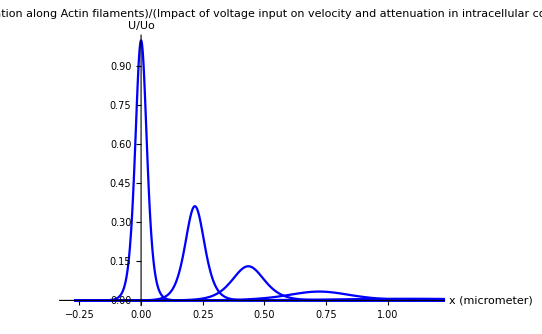

```mathematica
Print["Intracellular conditions at 0.05 and 0.15 molar concentration: A normalized plot"]

SolNormTot2=Plot[ {-Wx[x*10^-6,0]/wo^2/2,
-Wx[x*10^-6,tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM/10]/wo^2/2,
-Wx[x*10^-6,tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM/5]/wo^2/2,
-Wx[x*10^-6,tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM/3]/wo^2/2,
-Wx[x*10^-6,tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM/2]/wo^2/2,
-Wx[x*10^-6,tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM]/wo^2/2},{x,-25*beta*10^6,435*beta*10^6},PlotRange->{{-0.3,1.2},{0,1}},Axes->True,AxesLabel->{"x (micrometer)","U/Uo"},PlotLabel->Style["Soliton propagation along Actin filaments" /" in intracellular conditions" / "Impact of voltage input on velocity and attenuation",Black,FontSize->18,Bold],AxesStyle->Directive[Black,FontSize-> 18],TicksStyle->Directive[18],PlotStyle->{{Blue,Thickness[0.0030]},{Blue,Thickness[0.0030]},{Blue,Thickness[0.0030]},{Blue,Thickness[0.0030]},{Blue,Thickness[0.0030]},{Blue,Thickness[0.0030]},{Orange,Thickness[0.0030]},{Orange,Thickness[0.0030]},{Orange,Thickness[0.0030]},{Orange,Thickness[0.0030]},{Orange,Thickness[0.0030]}},PlotLegends->Placed[{},{0.87,0.6}],LabelStyle->{18}]
```

```mathematica
NormSolSP22Data2=Cases[SolNormTot2,Line[{x__}]->x,∞];
```

{{-0.27,1.48698×10^-7},{-0.268476,1.6377×10^-7},{-0.266953,1.80369×10^-7},{-0.265429,1.98651×10^-7},{-0.263905,2.18785×10^-7},{-0.262382,2.4096×10^-7},{-0.260858,2.65383×10^-7},{-0.259334,2.92281×10^-7},{-0.257811,3.21906×10^-7},{-0.256287,3.54533×10^-7},{-0.254763,3.90467×10^-7},{-0.253239,4.30044×10^-7},{-0.251716,4.73631×10^-7},{-0.250192,5.21637×10^-7},{-0.248668,5.74508×10^-7},{-0.247145,6.32738×10^-7},{-0.245621,6.9687×10^-7},{-0.244097,7.67502×10^-7},{-0.242574,8.45294×10^-7},{-0.24105,9.30969×10^-7},{-0.239526,1.02533×10^-6},{-0.238003,1.12925×10^-6},{-0.236479,1.24371×10^-6},{-0.234955,1.36977×10^-6},{-0.233432,1.5086×10^-6},{-0.231908,1.66151×10^-6},{-0.230384,1.82991×10^-6},{-0.228861,2.01538×10^-6},{-0.227337,2.21966×10^-6},{-0.225813,2.44463×10^-6},{-0.22429,2.69241×10^-6},{-0.222766,2.9653×10^-6},{-0.221242,3.26586×10^-6},{-0.219719,3.59687×10^-6},{-0.218195,3.96144×10^-6},{-0.216671,4.36295×10^-6},{-0.215148,4.80516×10^-6},{-0.213624,5.2922×10^-6},{-0.2121,5.82859×10^-6},{-0.210577,6.41935×10^-6},{-0.209053,7.06999×10^-6},{-0.207529,7.78658×10^-6},{-0.206006,8.5758×10^-6},{-0.204482,9.445×10^-6},{-0.202958,0.0000104023},{-0.201435,0.0000114566},{-0.199911,0.0000126178},{-0.198387,0.0000138967},{-0.196864,0.0000153052},{-0.19534,0.0000168565},{-0.193816,0.000018565},{-0.192293,0.0000204467},{-0.190769,0.000022519},{-0.189245,0.0000248015},{-0.187722,0.0000273152},{-0.186198,0.0000300837},{-0.184674,0.0000331329},{-0.183151,0.000036491},{-0.181627,0.0000401896},{-0.180103,0.0000442629},{-0.17858,0.0000487492},{-0.177056,0.0000536901},{-0.175532,0.0000591317},{-0.174008,0.0000651249},{-0.172485,0.0000717255},{-0.170833,0.0000796391},{-0.169181,0.0000884258},{-0.167529,0.0000981819},{-0.165877,0.000109014},{-0.164226,0.000121042},{-0.162574,0.000134396},{-0.160922,0.000149224},{-0.15927,0.000165688},{-0.157618,0.000183967},{-0.155966,0.000204263},{-0.154315,0.000226799},{-0.152663,0.00025182},{-0.151011,0.000279601},{-0.149359,0.000310446},{-0.147707,0.000344694},{-0.146055,0.000382719},{-0.144404,0.000424937},{-0.142752,0.000471813},{-0.1411,0.000523857},{-0.139448,0.000581641},{-0.137796,0.000645796},{-0.136144,0.000717025},{-0.134493,0.000796108},{-0.132841,0.000883909},{-0.131189,0.000981388},{-0.129537,0.00108961},{-0.127885,0.00120976},{-0.126233,0.00134315},{-0.124582,0.00149124},{-0.12293,0.00165565},{-0.121278,0.00183816},{-0.119626,0.00204076},{-0.117974,0.00226568},{-0.116322,0.00251535},{-0.114671,0.0027925},{-0.113019,0.00310014},{-0.111367,0.00344161},{-0.109715,0.00382061},{-0.108063,0.00424127},{-0.106411,0.00470814},{-0.10476,0.00522626},{-0.103108,0.00580123},{-0.101456,0.00643925},{-0.099804,0.00714719},{-0.0981522,0.00793265},{-0.0965003,0.00880405},{-0.0948485,0.0097707},{-0.0931967,0.0108429},{-0.0915448,0.0120321},{-0.089893,0.0133507},{-0.0882412,0.0148129},{-0.0865893,0.0164338},{-0.0849375,0.0182304},{-0.0832856,0.0202215},{-0.0816338,0.0224275},{-0.079982,0.0248711},{-0.0783301,0.0275772},{-0.0766783,0.0305731},{-0.0750265,0.0338888},{-0.0733746,0.0375571},{-0.0717228,0.041614},{-0.070071,0.0460985},{-0.0684191,0.0510534},{-0.0667673,0.056525},{-0.0652249,0.0621449},{-0.0636825,0.0683033},{-0.0621402,0.0750474},{-0.0605978,0.0824279},{-0.0590554,0.0904985},{-0.0575131,0.0993164},{-0.0559707,0.108942},{-0.0544283,0.119438},{-0.0528859,0.13087},{-0.0513436,0.143308},{-0.0498012,0.156819},{-0.0482588,0.171477},{-0.0467164,0.18735},{-0.0451741,0.20451},{-0.0420893,0.242954},{-0.040547,0.264359},{-0.0390046,0.287286},{-0.0359198,0.337844},{-0.0343775,0.365505},{-0.0328351,0.394741},{-0.0297504,0.45775},{-0.028208,0.491356},{-0.0266656,0.526192},{-0.0235809,0.598814},{-0.0174114,0.748273},{-0.015869,0.784452},{-0.0143266,0.819305},{-0.0127843,0.852365},{-0.0112419,0.883159},{-0.00969952,0.911215},{-0.00815715,0.936081},{-0.00661477,0.957338},{-0.0050724,0.974614},{-0.00353003,0.987597},{-0.00198766,0.996045},{-0.000445286,0.999801},{0.00109709,0.998793},{0.00263946,0.99304},{0.00418183,0.982651},{0.0057242,0.967821},{0.00726657,0.948821},{0.00880895,0.92599},{0.0103513,0.899722},{0.0118937,0.870453},{0.0134361,0.838643},{0.0149784,0.804767},{0.0165208,0.769298},{0.0196055,0.695398},{0.0211479,0.657811},{0.0226903,0.620304},{0.025775,0.5468},{0.0273174,0.511331},{0.0288598,0.476995},{0.0319445,0.412325},{0.0334566,0.382772},{0.0349688,0.354714},{0.0364809,0.328177},{0.037993,0.303168},{0.0395051,0.279676},{0.0410172,0.257673},{0.0440415,0.217969},{0.0455536,0.200165},{0.0470657,0.183646},{0.0485778,0.168348},{0.0500899,0.154205},{0.051602,0.14115},{0.0531142,0.129117},{0.0561384,0.107854},{0.0576505,0.0984987},{0.0591626,0.0899141},{0.0606747,0.0820438},{0.0621869,0.0748341},{0.063699,0.0682346},{0.0652111,0.0621976},{0.0667232,0.0566785},{0.0682353,0.0516357},{0.0697474,0.0470304},{0.0712596,0.0428266},{0.0727717,0.0389909},{0.0742838,0.0354924},{0.0757959,0.0323025},{0.077308,0.029395},{0.0788201,0.0267455},{0.0803323,0.0243319},{0.0818444,0.0221336},{0.0833565,0.0201318},{0.0848686,0.0183094},{0.0863807,0.0166506},{0.0878928,0.0151409},{0.089405,0.0137671},{0.0909171,0.0125172},{0.0924292,0.0113801},{0.0939413,0.0103458},{0.0954534,0.00940502},{0.0969655,0.00854942},{0.0984777,0.00777136},{0.0999898,0.00706385},{0.101502,0.00642055},{0.103014,0.00583566},{0.104526,0.00530391},{0.106038,0.00482049},{0.10755,0.00438104},{0.109062,0.00398157},{0.110575,0.00361846},{0.112087,0.00328841},{0.113599,0.00298842},{0.115111,0.00271576},{0.116623,0.00246794},{0.118135,0.00224271},{0.119647,0.00203802},{0.121159,0.00185199},{0.122672,0.00168293},{0.124184,0.00152929},{0.125696,0.00138967},{0.127208,0.00126278},{0.12872,0.00114747},{0.13036,0.00103426},{0.132001,0.000932216},{0.133641,0.000840234},{0.135281,0.000757324},{0.136921,0.000682592},{0.138562,0.000615232},{0.140202,0.000554518},{0.141842,0.000499794},{0.143483,0.000450469},{0.145123,0.000406011},{0.146763,0.00036594},{0.148403,0.000329824},{0.150044,0.000297271},{0.151684,0.00026793},{0.153324,0.000241486},{0.154964,0.00021765},{0.156605,0.000196168},{0.158245,0.000176805},{0.159885,0.000159354},{0.161526,0.000143625},{0.163166,0.000129448},{0.164806,0.000116671},{0.166446,0.000105155},{0.168087,0.000094775},{0.169727,0.0000854199},{0.171367,0.0000769882},{0.173008,0.0000693888},{0.174648,0.0000625395},{0.176288,0.0000563662},{0.177928,0.0000508023},{0.179569,0.0000457876},{0.181209,0.0000412679},{0.182849,0.0000371943},{0.18449,0.0000335229},{0.18613,0.0000302138},{0.18777,0.0000272313},{0.18941,0.0000245433},{0.191051,0.0000221206},{0.192691,0.0000199371},{0.194331,0.000017969},{0.195971,0.0000161953},{0.197612,0.0000145966},{0.199252,0.0000131558},{0.200892,0.0000118571},{0.202533,0.0000106867},{0.204173,9.63179×10^-6},{0.205813,8.68102×10^-6},{0.207453,7.8241×10^-6},{0.209094,7.05176×10^-6},{0.210734,6.35567×10^-6},{0.212374,5.72829×10^-6},{0.214015,5.16284×10^-6},{0.215655,4.6532×10^-6},{0.217295,4.19387×10^-6},{0.218935,3.77989×10^-6},{0.220576,3.40677×10^-6},{0.222216,3.07048×10^-6},{0.223856,2.76738×10^-6},{0.225497,2.49421×10^-6},{0.227137,2.248×10^-6},{0.228777,2.02609×10^-6},{0.230417,1.82609×10^-6},{0.232058,1.64584×10^-6},{0.233698,1.48337×10^-6},{0.235229,1.34625×10^-6},{0.23676,1.2218×10^-6},{0.23829,1.10886×10^-6},{0.239821,1.00636×10^-6},{0.241352,9.13331×10^-7},{0.242883,8.28903×10^-7},{0.244414,7.5228×10^-7},{0.245944,6.8274×10^-7},{0.247475,6.19628×10^-7},{0.249006,5.6235×10^-7},{0.250537,5.10366×10^-7},{0.252068,4.63188×10^-7},{0.253599,4.20371×10^-7},{0.255129,3.81513×10^-7},{0.25666,3.46246×10^-7},{0.258191,3.14239×10^-7},{0.259722,2.85191×10^-7},{0.261253,2.58828×10^-7},{0.262783,2.34902×10^-7},{0.264314,2.13188×10^-7},{0.265845,1.93481×10^-7},{0.267376,1.75596×10^-7},{0.268907,1.59364×10^-7},{0.270437,1.44632×10^-7},{0.271968,1.31262×10^-7},{0.273499,1.19129×10^-7},{0.27503,1.08116×10^-7},{0.276561,9.81222×10^-8},{0.278092,8.90519×10^-8},{0.279622,8.08199×10^-8},{0.281153,7.3349×10^-8},{0.282684,6.65687×10^-8},{0.284215,6.04151×10^-8},{0.285746,5.48303×10^-8},{0.287276,4.97619×10^-8},{0.288807,4.51619×10^-8},{0.290338,4.09872×10^-8},{0.291869,3.71983×10^-8},{0.2934,3.37597×10^-8},{0.294931,3.0639×10^-8},{0.296461,2.78067×10^-8},{0.297992,2.52363×10^-8},{0.299523,2.29035×10^-8},{0.301054,2.07863×10^-8},{0.302585,1.88648×10^-8},{0.304115,1.7121×10^-8},{0.305646,1.55383×10^-8},{0.307177,1.4102×10^-8},{0.308708,1.27984×10^-8},{0.310239,1.16153×10^-8},{0.31177,1.05416×10^-8},{0.3133,9.56713×10^-9},{0.314831,8.68275×10^-9},{0.316362,7.88012×10^-9},{0.317893,7.15169×10^-9},{0.319424,6.49059×10^-9},{0.320954,5.89061×10^-9},{0.322485,5.34608×10^-9},{0.324016,4.85189×10^-9},{0.325547,4.40339×10^-9},{0.327078,3.99634×10^-9},{0.328608,3.62692×10^-9},{0.330139,3.29165×10^-9},{0.33167,2.98737×10^-9},{0.333329,2.68929×10^-9},{0.334988,2.42096×10^-9},{0.336647,2.17939×10^-9},{0.338306,1.96193×10^-9},{0.339965,1.76617×10^-9},{0.341624,1.58995×10^-9},{0.343283,1.4313×10^-9},{0.344942,1.28849×10^-9},{0.346601,1.15992×10^-9},{0.34826,1.04419×10^-9},{0.349919,9.39997×10^-10},{0.351578,8.46205×10^-10},{0.353237,7.61771×10^-10},{0.354896,6.85762×10^-10},{0.356555,6.17337×10^-10},{0.358214,5.55739×10^-10},{0.359873,5.00288×10^-10},{0.361532,4.50369×10^-10},{0.363191,4.05432×10^-10},{0.36485,3.64978×10^-10},{0.366509,3.2856×10^-10},{0.368168,2.95777×10^-10},{0.369827,2.66264×10^-10},{0.371486,2.39697×10^-10},{0.373145,2.1578×10^-10},{0.374804,1.94249×10^-10},{0.376463,1.74867×10^-10},{0.378122,1.57419×10^-10},{0.37978,1.41712×10^-10},{0.381439,1.27572×10^-10},{0.383098,1.14843×10^-10},{0.384757,1.03384×10^-10},{0.386416,9.30683×10^-11},{0.388075,8.37819×10^-11},{0.389734,7.54222×10^-11},{0.391393,6.78966×10^-11},{0.393052,6.11219×10^-11},{0.394711,5.50232×10^-11},{0.39637,4.9533×10^-11},{0.398029,4.45906×10^-11},{0.399688,4.01414×10^-11},{0.401347,3.61361×10^-11},{0.403006,3.25305×10^-11},{0.404665,2.92846×10^-11},{0.406324,2.63626×10^-11},{0.407983,2.37321×10^-11},{0.409642,2.13642×10^-11},{0.411301,1.92324×10^-11},{0.41296,1.73134×10^-11},{0.414619,1.55859×10^-11},{0.416278,1.40308×10^-11},{0.417937,1.26308×10^-11},{0.419596,1.13705×10^-11},{0.421255,1.02359×10^-11},{0.422914,9.2146×10^-12},{0.424573,8.29517×10^-12},{0.426232,7.46748×10^-12},{0.427891,6.72238×10^-12},{0.42955,6.05162×10^-12},{0.431209,5.4478×10^-12},{0.432868,4.90422×10^-12},{0.434527,4.41488×10^-12},{0.436186,3.97436×10^-12},{0.437845,3.5778×10^-12},{0.439473,3.22699×10^-12},{0.441102,2.91058×10^-12},{0.442731,2.62519×10^-12},{0.44436,2.36778×10^-12},{0.445988,2.13562×10^-12},{0.447617,1.92621×10^-12},{0.449246,1.73735×10^-12},{0.450875,1.56699×10^-12},{0.452503,1.41335×10^-12},{0.454132,1.27477×10^-12},{0.455761,1.14977×10^-12},{0.457389,1.03703×10^-12},{0.459018,9.35351×10^-13},{0.460647,8.43638×10^-13},{0.462276,7.60917×10^-13},{0.463904,6.86308×10^-13},{0.465533,6.19014×10^-13},{0.467162,5.58318×10^-13},{0.46879,5.03574×10^-13},{0.470419,4.54197×10^-13},{0.472048,4.09662×10^-13},{0.473677,3.69494×10^-13},{0.475305,3.33264×10^-13},{0.476934,3.00587×10^-13},{0.478563,2.71114×10^-13},{0.480192,2.4453×10^-13},{0.48182,2.20554×10^-13},{0.483449,1.98928×10^-13},{0.485078,1.79423×10^-13},{0.486706,1.6183×10^-13},{0.488335,1.45962×10^-13},{0.489964,1.3165×10^-13},{0.491593,1.18742×10^-13},{0.493221,1.07099×10^-13},{0.49485,9.65975×10^-14},{0.496479,8.71259×10^-14},{0.498108,7.8583×10^-14},{0.499736,7.08778×10^-14},{0.501365,6.3928×10^-14},{0.502994,5.76598×10^-14},{0.504622,5.20061×10^-14},{0.506251,4.69068×10^-14},{0.50788,4.23075×10^-14},{0.509509,3.81591×10^-14},{0.511137,3.44175×10^-14},{0.512766,3.10428×10^-14},{0.514395,2.7999×10^-14},{0.516023,2.52536×10^-14},{0.517652,2.27775×10^-14},{0.519281,2.05441×10^-14},{0.52091,1.85297×10^-14},{0.522538,1.67128×10^-14},{0.524167,1.50741×10^-14},{0.525796,1.3596×10^-14},{0.527425,1.22629×10^-14},{0.529053,1.10605×10^-14},{0.530682,9.97601×10^-15},{0.532311,8.99784×10^-15},{0.533939,8.11558×10^-15},{0.535568,7.31983×10^-15},{0.537197,6.6021×10^-15},{0.538826,5.95475×10^-15},{0.540454,5.37088×10^-15},{0.542083,4.84425×10^-15},{0.543602,4.39967×10^-15},{0.545122,3.99589×10^-15},{0.546641,3.62917×10^-15},{0.54816,3.29611×10^-15},{0.549679,2.99361×10^-15},{0.551199,2.71887×10^-15},{0.552718,2.46935×10^-15},{0.554237,2.24272×10^-15},{0.555756,2.0369×10^-15},{0.557276,1.84996×10^-15},{0.558795,1.68018×10^-15},{0.560314,1.52598×10^-15},{0.563353,1.25874×10^-15},{0.566391,1.0383×10^-15},{0.56943,8.56469×10^-16},{0.572468,7.06478×10^-16},{0.575507,5.82755×10^-16},{0.578545,4.80699×10^-16},{0.584622,3.27075×10^-16},{0.590699,2.22547×10^-16},{0.592219,2.02123×10^-16},{0.593738,1.83573×10^-16},{0.596776,1.51425×10^-16},{0.602853,1.03032×10^-16},{0.615007,4.77002×10^-17},{0.639316,1.02239×10^-17},{0.640963,9.21053×10^-18},{0.64261,8.29758×10^-18},{0.645905,6.73419×10^-18},{0.652495,4.4356×10^-18},{0.665674,1.92437×10^-18},{0.692033,3.62208×10^-19},{0.744751,1.28321×10^-20},{0.84318,2.51048×10^-23},{0.939673,5.55266×10^-26},{1.04437,7.30353×10^-29},{1.14206,1.49743×10^-31},{1.24795,1.82577×10^-34},{1.35191,2.5167×10^-37},{1.44886,5.4075×10^-40},{1.55401,6.90955×10^-43},{1.65216,1.37621×10^-45},{1.7585,1.63007×10^-48},{1.86292,2.18279×10^-51},{1.96032,4.55616×10^-54},{2.06593,5.65554×10^-57},{2.16454,1.09428×10^-59},{2.26121,2.39369×10^-62},{2.36608,3.11384×10^-65},{2.46394,6.31399×10^-68},{2.57001,7.61378×10^-71},{2.67414,1.03796×10^-73},{2.77126,2.20567×10^-76},{2.87659,2.78734×10^-79},{2.97491,5.49059×10^-82},{3.0713,1.22273×10^-84},{3.17588,1.61932×10^-87},{3.27346,3.34284×10^-90},{3.37925,4.1038×10^-93},{3.47803,7.85303×10^-96},{3.57487,1.69891×10^-98},{3.67991,2.18572×10^-101},{3.77795,4.38327×10^-104},{3.88419,5.22745×10^-107},{3.9885,7.04799×10^-110},{4.0858,1.48123×10^-112},{4.1913,1.85125×10^-115},{4.2898,3.60654×10^-118},{4.38636,7.94326×10^-121},{4.49112,1.04039×10^-123},{4.58887,2.12409×10^-126},{4.59058,1.90657×10^-126},{4.59228,1.71133×10^-126},{4.59569,1.37878×10^-126},{4.60252,8.94982×10^-127},{4.61616,3.77099×10^-127},{4.64344,6.69479×10^-128},{4.64514,6.00921×10^-128},{4.64685,5.39383×10^-128},{4.65026,4.34568×10^-128},{4.65708,2.82084×10^-128},{4.67072,1.18855×10^-128},{4.67242,1.06684×10^-128},{4.67413,9.57589×10^-129},{4.67754,7.71506×10^-129},{4.68436,5.00795×10^-129},{4.68606,4.49511×10^-129},{4.68777,4.03478×10^-129},{4.69118,3.25073×10^-129},{4.69288,2.91783×10^-129},{4.69459,2.61903×10^-129},{4.69629,2.35083×10^-129},{4.698,2.11009×10^-129},{-0.27,1.1983×10^-8},{-0.268476,1.26999×10^-8},{-0.266953,1.34597×10^-8},{-0.263905,1.51183×10^-8},{-0.262382,1.60228×10^-8},{-0.260858,1.69814×10^-8},{-0.257811,1.9074×10^-8},{-0.256287,2.02152×10^-8},{-0.254763,2.14246×10^-8},{-0.251716,2.40648×10^-8},{-0.250192,2.55045×10^-8},{-0.248668,2.70303×10^-8},{-0.245621,3.03613×10^-8},{-0.244097,3.21777×10^-8},{-0.242574,3.41027×10^-8},{-0.239526,3.83053×10^-8},{-0.238003,4.05969×10^-8},{-0.236479,4.30257×10^-8},{-0.233432,4.83278×10^-8},{-0.231908,5.12191×10^-8},{-0.230384,5.42833×10^-8},{-0.227337,6.09727×10^-8},{-0.225813,6.46205×10^-8},{-0.22429,6.84865×10^-8},{-0.221242,7.69261×10^-8},{-0.219719,8.15283×10^-8},{-0.218195,8.64059×10^-8},{-0.215148,9.70538×10^-8},{-0.213624,1.0286×10^-7},{-0.2121,1.09014×10^-7},{-0.209053,1.22448×10^-7},{-0.207529,1.29773×10^-7},{-0.206006,1.37537×10^-7},{-0.202958,1.54486×10^-7},{-0.201435,1.63728×10^-7},{-0.199911,1.73524×10^-7},{-0.196864,1.94907×10^-7},{-0.19534,2.06568×10^-7},{-0.193816,2.18926×10^-7},{-0.190769,2.45904×10^-7},{-0.189245,2.60616×10^-7},{-0.187722,2.76208×10^-7},{-0.184674,3.10245×10^-7},{-0.183151,3.28806×10^-7},{-0.181627,3.48477×10^-7},{-0.17858,3.9142×10^-7},{-0.177056,4.14837×10^-7},{-0.175532,4.39656×10^-7},{-0.172485,4.93835×10^-7},{-0.170833,5.25943×10^-7},{-0.169181,5.60139×10^-7},{-0.167529,5.96559×10^-7},{-0.165877,6.35346×10^-7},{-0.164226,6.76656×10^-7},{-0.162574,7.20651×10^-7},{-0.15927,8.17409×10^-7},{-0.157618,8.70556×10^-7},{-0.155966,9.27158×10^-7},{-0.154315,9.87441×10^-7},{-0.152663,1.05164×10^-6},{-0.151011,1.12002×10^-6},{-0.149359,1.19284×10^-6},{-0.146055,1.353×10^-6},{-0.144404,1.44097×10^-6},{-0.142752,1.53466×10^-6},{-0.1411,1.63444×10^-6},{-0.139448,1.74071×10^-6},{-0.137796,1.85388×10^-6},{-0.136144,1.97442×10^-6},{-0.132841,2.23952×10^-6},{-0.131189,2.38513×10^-6},{-0.129537,2.5402×10^-6},{-0.127885,2.70536×10^-6},{-0.126233,2.88126×10^-6},{-0.124582,3.0686×10^-6},{-0.12293,3.26811×10^-6},{-0.119626,3.7069×10^-6},{-0.117974,3.94792×10^-6},{-0.116322,4.20461×10^-6},{-0.114671,4.47798×10^-6},{-0.113019,4.76913×10^-6},{-0.111367,5.07921×10^-6},{-0.109715,5.40945×10^-6},{-0.106411,6.13575×10^-6},{-0.10476,6.53468×10^-6},{-0.103108,6.95956×10^-6},{-0.101456,7.41205×10^-6},{-0.099804,7.89397×10^-6},{-0.0981522,8.40722×10^-6},{-0.0965003,8.95384×10^-6},{-0.0931967,0.000010156},{-0.0915448,0.0000108163},{-0.089893,0.0000115196},{-0.0882412,0.0000122686},{-0.0865893,0.0000130662},{-0.0849375,0.0000139158},{-0.0832856,0.0000148205},{-0.079982,0.0000168104},{-0.0783301,0.0000179033},{-0.0766783,0.0000190673},{-0.0750265,0.000020307},{-0.0733746,0.0000216273},{-0.0717228,0.0000230335},{-0.070071,0.000024531},{-0.0667673,0.0000278245},{-0.0652249,0.0000295101},{-0.0636825,0.0000312979},{-0.0621402,0.0000331939},{-0.0605978,0.0000352047},{-0.0590554,0.0000373374},{-0.0575131,0.0000395992},{-0.0544283,0.0000445423},{-0.0528859,0.0000472406},{-0.0513436,0.0000501023},{-0.0498012,0.0000531374},{-0.0482588,0.0000563563},{-0.0467164,0.0000597702},{-0.0451741,0.0000633909},{-0.0420893,0.0000713035},{-0.040547,0.0000756228},{-0.0390046,0.0000802037},{-0.0374622,0.000085062},{-0.0359198,0.0000902146},{-0.0343775,0.0000956793},{-0.0328351,0.000101475},{-0.0297504,0.00011414},{-0.028208,0.000121054},{-0.0266656,0.000128387},{-0.0251232,0.000136163},{-0.0235809,0.000144411},{-0.0220385,0.000153157},{-0.0204961,0.000162434},{-0.0174114,0.000182706},{-0.015869,0.000193772},{-0.0143266,0.000205508},{-0.0127843,0.000217954},{-0.0112419,0.000231154},{-0.00969952,0.000245153},{-0.00815715,0.00026},{-0.0050724,0.000292443},{-0.00353003,0.000310153},{-0.00198766,0.000328934},{-0.000445286,0.000348852},{0.00109709,0.000369975},{0.00263946,0.000392377},{0.00418183,0.000416134},{0.00726657,0.000468049},{0.00880895,0.000496384},{0.0103513,0.000526435},{0.0118937,0.000558303},{0.0134361,0.000592098},{0.0149784,0.000627938},{0.0165208,0.000665944},{0.0196055,0.000748991},{0.0211479,0.000794317},{0.0226903,0.000842382},{0.0242327,0.000893353},{0.025775,0.000947403},{0.0273174,0.00100472},{0.0288598,0.0010655},{0.0319445,0.00119829},{0.0334566,0.00126929},{0.0349688,0.0013445},{0.037993,0.00150851},{0.0395051,0.00159785},{0.0410172,0.00169248},{0.0440415,0.00189883},{0.0455536,0.00201123},{0.0470657,0.00213026},{0.0500899,0.00238981},{0.051602,0.00253117},{0.0531142,0.00268086},{0.0561384,0.00300721},{0.0576505,0.00318493},{0.0591626,0.0033731},{0.0621869,0.00378328},{0.063699,0.00400661},{0.0652111,0.00424304},{0.0682353,0.0047583},{0.0697474,0.00503877},{0.0712596,0.00533566},{0.0742838,0.0059825},{0.0757959,0.00633449},{0.077308,0.00670701},{0.0803323,0.00751833},{0.0818444,0.00795969},{0.0833565,0.00842664},{0.0863807,0.00944322},{0.0878928,0.00999597},{0.089405,0.0105806},{0.0924292,0.0118527},{0.0939413,0.0125439},{0.0954534,0.0132748},{0.0984777,0.0148639},{0.0999898,0.0157268},{0.101502,0.0166387},{0.104526,0.0186197},{0.106038,0.0196945},{0.10755,0.0208294},{0.110575,0.0232925},{0.112087,0.0246273},{0.113599,0.0260357},{0.116623,0.029088},{0.118135,0.0307398},{0.119647,0.0324809},{0.122672,0.0362478},{0.124184,0.0382826},{0.125696,0.0404246},{0.12872,0.0450493},{0.13036,0.0477589},{0.132001,0.0506185},{0.135281,0.0568139},{0.136921,0.0601633},{0.138562,0.0636894},{0.141842,0.0712986},{0.143483,0.0753949},{0.145123,0.079694},{0.148403,0.0889246},{0.150044,0.093867},{0.151684,0.0990338},{0.154964,0.110056},{0.156605,0.115918},{0.158245,0.122015},{0.161526,0.134917},{0.168087,0.163471},{0.169727,0.171147},{0.171367,0.179018},{0.174648,0.195286},{0.181209,0.229386},{0.182849,0.238092},{0.18449,0.246812},{0.18777,0.26415},{0.18941,0.272693},{0.191051,0.281097},{0.194331,0.297321},{0.195971,0.305052},{0.197612,0.312469},{0.199252,0.319526},{0.200892,0.32618},{0.202533,0.332386},{0.204173,0.338102},{0.205813,0.34329},{0.207453,0.347912},{0.209094,0.351934},{0.210734,0.355327},{0.212374,0.358064},{0.214015,0.360126},{0.215655,0.361496},{0.217295,0.362164},{0.218935,0.362124},{0.220576,0.361376},{0.222216,0.359927},{0.223856,0.357788},{0.225497,0.354975},{0.227137,0.35151},{0.228777,0.347418},{0.230417,0.342731},{0.232058,0.337481},{0.233698,0.331707},{0.235229,0.32588},{0.23676,0.319666},{0.239821,0.306214},{0.245944,0.276248},{0.247475,0.268329},{0.249006,0.260308},{0.252068,0.244089},{0.258191,0.211748},{0.259722,0.203829},{0.261253,0.196017},{0.264314,0.180787},{0.265845,0.173397},{0.267376,0.166173},{0.270437,0.152264},{0.271968,0.145593},{0.273499,0.13912},{0.276561,0.126777},{0.282684,0.104552},{0.284215,0.0995052},{0.285746,0.0946573},{0.288807,0.0855461},{0.290338,0.0812749},{0.291869,0.0771874},{0.294931,0.0695443},{0.296461,0.0659784},{0.297992,0.062576},{0.301054,0.0562396},{0.302585,0.0532947},{0.304115,0.0504913},{0.307177,0.0452875},{0.308708,0.0428764},{0.310239,0.0405854},{0.3133,0.0363437},{0.314831,0.0343831},{0.316362,0.032523},{0.319424,0.0290862},{0.320954,0.0275007},{0.322485,0.0259983},{0.325547,0.0232268},{0.327078,0.0219503},{0.328608,0.0207418},{0.33167,0.0185153},{0.333329,0.0174079},{0.334988,0.0163651},{0.336647,0.0153833},{0.338306,0.0144593},{0.339965,0.0135897},{0.341624,0.0127714},{0.344942,0.0112773},{0.346601,0.0105961},{0.34826,0.00995552},{0.349919,0.00935313},{0.351578,0.00878673},{0.353237,0.00825423},{0.354896,0.00775365},{0.358214,0.00684086},{0.359873,0.00642522},{0.361532,0.00603462},{0.363191,0.00566757},{0.36485,0.00532268},{0.366509,0.00499864},{0.368168,0.00469419},{0.371486,0.00413947},{0.373145,0.00388707},{0.374804,0.00364997},{0.376463,0.00342727},{0.378122,0.0032181},{0.37978,0.00302164},{0.381439,0.00283712},{0.384757,0.00250109},{0.386416,0.00234826},{0.388075,0.00220474},{0.389734,0.00206996},{0.391393,0.00194341},{0.393052,0.00182457},{0.394711,0.00171298},{0.398029,0.00150981},{0.399688,0.00141743},{0.401347,0.0013307},{0.403006,0.00124926},{0.404665,0.0011728},{0.406324,0.00110101},{0.407983,0.00103361},{0.411301,0.000910915},{0.41296,0.000855138},{0.414619,0.000802772},{0.416278,0.000753609},{0.417937,0.000707454},{0.419596,0.000664123},{0.421255,0.000623444},{0.424573,0.000549403},{0.426232,0.000515746},{0.427891,0.000484149},{0.42955,0.000454487},{0.431209,0.000426641},{0.432868,0.0004005},{0.434527,0.00037596},{0.437845,0.000331297},{0.439473,0.000311355},{0.441102,0.000292612},{0.442731,0.000274997},{0.44436,0.000258442},{0.445988,0.000242884},{0.447617,0.000228262},{0.450875,0.000201604},{0.452503,0.000189467},{0.454132,0.00017806},{0.455761,0.000167339},{0.457389,0.000157264},{0.459018,0.000147795},{0.460647,0.000138896},{0.463904,0.000122674},{0.465533,0.000115287},{0.467162,0.000108346},{0.46879,0.000101822},{0.470419,0.0000956908},{0.472048,0.0000899289},{0.473677,0.0000845139},{0.476934,0.0000746423},{0.478563,0.0000701477},{0.480192,0.0000659237},{0.48182,0.000061954},{0.483449,0.0000582234},{0.485078,0.0000547173},{0.486706,0.0000514224},{0.489964,0.0000454158},{0.491593,0.000042681},{0.493221,0.0000401108},{0.49485,0.0000376954},{0.496479,0.0000354254},{0.498108,0.0000332922},{0.499736,0.0000312874},{0.502994,0.0000276326},{0.504622,0.0000259686},{0.506251,0.0000244048},{0.50788,0.0000229352},{0.509509,0.000021554},{0.511137,0.000020256},{0.512766,0.0000190362},{0.516023,0.0000168125},{0.517652,0.0000158001},{0.519281,0.0000148486},{0.52091,0.0000139544},{0.522538,0.0000131141},{0.524167,0.0000123243},{0.525796,0.0000115822},{0.529053,0.0000102292},{0.530682,9.61319×10^-6},{0.532311,9.03428×10^-6},{0.533939,8.49023×10^-6},{0.535568,7.97894×10^-6},{0.537197,7.49844×10^-6},{0.538826,7.04688×10^-6},{0.542083,6.2237×10^-6},{0.543602,5.87337×10^-6},{0.545122,5.54276×10^-6},{0.54816,4.93632×10^-6},{0.549679,4.65846×10^-6},{0.551199,4.39623×10^-6},{0.554237,3.91523×10^-6},{0.555756,3.69485×10^-6},{0.557276,3.48686×10^-6},{0.560314,3.10536×10^-6},{0.561833,2.93056×10^-6},{0.563353,2.7656×10^-6},{0.566391,2.46301×10^-6},{0.56791,2.32437×10^-6},{0.56943,2.19353×10^-6},{0.572468,1.95353×10^-6},{0.573987,1.84357×10^-6},{0.575507,1.73979×10^-6},{0.578545,1.54944×10^-6},{0.580065,1.46222×10^-6},{0.581584,1.37991×10^-6},{0.584622,1.22894×10^-6},{0.586142,1.15976×10^-6},{0.587661,1.09448×10^-6},{0.590699,9.74727×10^-7},{0.592219,9.1986×10^-7},{0.593738,8.68081×10^-7},{0.596776,7.73102×10^-7},{0.598296,7.29584×10^-7},{0.599815,6.88516×10^-7},{0.602853,6.13184×10^-7},{0.604373,5.78668×10^-7},{0.605892,5.46095×10^-7},{0.60893,4.86346×10^-7},{0.61045,4.58969×10^-7},{0.611969,4.33134×10^-7},{0.615007,3.85744×10^-7},{0.616527,3.6403×10^-7},{0.618046,3.43539×10^-7},{0.621085,3.05952×10^-7},{0.622604,2.8873×10^-7},{0.624123,2.72477×10^-7},{0.627162,2.42665×10^-7},{0.628681,2.29005×10^-7},{0.6302,2.16115×10^-7},{0.633239,1.92469×10^-7},{0.634758,1.81635×10^-7},{0.636277,1.71411×10^-7},{0.639316,1.52656×10^-7},{0.640963,1.43361×10^-7},{0.64261,1.34631×10^-7},{0.644258,1.26434×10^-7},{0.645905,1.18735×10^-7},{0.647553,1.11505×10^-7},{0.6492,1.04715×10^-7},{0.652495,9.23511×10^-8},{0.654142,8.67277×10^-8},{0.65579,8.14467×10^-8},{0.657437,7.64873×10^-8},{0.659085,7.18299×10^-8},{0.660732,6.74561×10^-8},{0.66238,6.33486×10^-8},{0.665674,5.58687×10^-8},{0.667322,5.24668×10^-8},{0.668969,4.92721×10^-8},{0.670617,4.62718×10^-8},{0.672264,4.34543×10^-8},{0.673911,4.08083×10^-8},{0.675559,3.83234×10^-8},{0.678854,3.37984×10^-8},{0.680501,3.17404×10^-8},{0.682149,2.98076×10^-8},{0.683796,2.79926×10^-8},{0.685443,2.62881×10^-8},{0.687091,2.46874×10^-8},{0.688738,2.31842×10^-8},{0.692033,2.04467×10^-8},{0.693681,1.92017×10^-8},{0.695328,1.80325×10^-8},{0.696975,1.69344×10^-8},{0.698623,1.59033×10^-8},{0.70027,1.49349×10^-8},{0.701918,1.40255×10^-8},{0.705213,1.23694×10^-8},{0.70686,1.16162×10^-8},{0.708507,1.09089×10^-8},{0.710155,1.02447×10^-8},{0.711802,9.62085×10^-9},{0.71345,9.03503×10^-9},{0.715097,8.48487×10^-9},{0.718392,7.48302×10^-9},{0.720039,7.02737×10^-9},{0.721687,6.59947×10^-9},{0.723334,6.19762×10^-9},{0.724982,5.82024×10^-9},{0.726629,5.46583×10^-9},{0.728276,5.13301×10^-9},{0.731571,4.52693×10^-9},{0.733219,4.25128×10^-9},{0.734866,3.99242×10^-9},{0.736514,3.74931×10^-9},{0.738161,3.52101×10^-9},{0.739808,3.30661×10^-9},{0.741456,3.10527×10^-9},{0.744751,2.73862×10^-9},{0.746289,2.58262×10^-9},{0.747827,2.4355×10^-9},{0.750902,2.16594×10^-9},{0.75244,2.04256×10^-9},{0.753978,1.92621×10^-9},{0.757054,1.71302×10^-9},{0.758592,1.61544×10^-9},{0.76013,1.52342×10^-9},{0.763206,1.3548×10^-9},{0.764744,1.27763×10^-9},{0.766282,1.20485×10^-9},{0.769358,1.0715×10^-9},{0.770896,1.01046×10^-9},{0.772434,9.52905×10^-10},{0.77551,8.47436×10^-10},{0.777048,7.99164×10^-10},{0.778586,7.53641×10^-10},{0.781662,6.70227×10^-10},{0.7832,6.32049×10^-10},{0.784738,5.96046×10^-10},{0.787813,5.30075×10^-10},{0.789351,4.9988×10^-10},{0.790889,4.71406×10^-10},{0.793965,4.1923×10^-10},{0.795503,3.9535×10^-10},{0.797041,3.72829×10^-10},{0.800117,3.31564×10^-10},{0.801655,3.12677×10^-10},{0.803193,2.94866×10^-10},{0.806269,2.6223×10^-10},{0.807807,2.47293×10^-10},{0.809345,2.33206×10^-10},{0.812421,2.07395×10^-10},{0.813959,1.95581×10^-10},{0.815497,1.8444×10^-10},{0.818573,1.64026×10^-10},{0.820111,1.54683×10^-10},{0.821649,1.45872×10^-10},{0.824724,1.29726×10^-10},{0.826262,1.22337×10^-10},{0.8278,1.15368×10^-10},{0.830876,1.02599×10^-10},{0.832414,9.67548×10^-11},{0.833952,9.12434×10^-11},{0.837028,8.11444×10^-11},{0.838566,7.65222×10^-11},{0.840104,7.21633×10^-11},{0.84318,6.41762×10^-11},{0.844688,6.05904×10^-11},{0.846195,5.7205×10^-11},{0.849211,5.0991×10^-11},{0.850718,4.81419×10^-11},{0.852226,4.5452×10^-11},{0.855242,4.05147×10^-11},{0.856749,3.8251×10^-11},{0.858257,3.61138×10^-11},{0.861272,3.21909×10^-11},{0.86278,3.03922×10^-11},{0.864288,2.86941×10^-11},{0.867303,2.55771×10^-11},{0.868811,2.4148×10^-11},{0.870319,2.27988×10^-11},{0.873334,2.03222×10^-11},{0.874842,1.91867×10^-11},{0.876349,1.81147×10^-11},{0.879365,1.6147×10^-11},{0.880873,1.52448×10^-11},{0.88238,1.4393×10^-11},{0.885396,1.28295×10^-11},{0.886903,1.21127×10^-11},{0.888411,1.14359×10^-11},{0.891426,1.01937×10^-11},{0.892934,9.62409×10^-12},{0.894442,9.08635×10^-12},{0.897457,8.09934×10^-12},{0.898965,7.64679×10^-12},{0.900473,7.21953×10^-12},{0.903488,6.4353×10^-12},{0.904996,6.07573×10^-12},{0.906503,5.73626×10^-12},{0.909519,5.11315×10^-12},{0.911027,4.82746×10^-12},{0.912534,4.55773×10^-12},{0.91555,4.06264×10^-12},{0.917057,3.83564×10^-12},{0.918565,3.62133×10^-12},{0.92158,3.22795×10^-12},{0.923088,3.0476×10^-12},{0.924596,2.87731×10^-12},{0.927611,2.56476×10^-12},{0.929119,2.42146×10^-12},{0.930627,2.28616×10^-12},{0.933642,2.03782×10^-12},{0.93515,1.92396×10^-12},{0.936658,1.81646×10^-12},{0.939673,1.61915×10^-12},{0.941309,1.52122×10^-12},{0.942945,1.42922×10^-12},{0.944581,1.34279×10^-12},{0.946216,1.26158×10^-12},{0.947852,1.18528×10^-12},{0.949488,1.1136×10^-12},{0.95276,9.82979×10^-13},{0.954396,9.23531×10^-13},{0.956032,8.67678×10^-13},{0.957667,8.15203×10^-13},{0.959303,7.65902×10^-13},{0.960939,7.19582×10^-13},{0.962575,6.76064×10^-13},{0.965847,5.96763×10^-13},{0.967483,5.60673×10^-13},{0.969118,5.26765×10^-13},{0.970754,4.94908×10^-13},{0.97239,4.64977×10^-13},{0.974026,4.36856×10^-13},{0.975662,4.10436×10^-13},{0.978934,3.62293×10^-13},{0.98057,3.40383×10^-13},{0.982205,3.19797×10^-13},{0.983841,3.00457×10^-13},{0.985477,2.82286×10^-13},{0.987113,2.65214×10^-13},{0.988749,2.49175×10^-13},{0.992021,2.19947×10^-13},{0.993656,2.06645×10^-13},{0.995292,1.94148×10^-13},{0.996928,1.82407×10^-13},{0.998564,1.71375×10^-13},{1.0002,1.61011×10^-13},{1.00184,1.51273×10^-13},{1.00511,1.33529×10^-13},{1.00674,1.25454×10^-13},{1.00838,1.17867×10^-13},{1.01002,1.10738×10^-13},{1.01165,1.04041×10^-13},{1.01329,9.77492×10^-14},{1.01492,9.18376×10^-14},{1.01819,8.10653×10^-14},{1.01983,7.61627×10^-14},{1.02147,7.15566×10^-14},{1.0231,6.7229×10^-14},{1.02474,6.31632×10^-14},{1.02637,5.93432×10^-14},{1.02801,5.57543×10^-14},{1.03128,4.92145×10^-14},{1.03292,4.62381×10^-14},{1.03455,4.34418×10^-14},{1.03619,4.08145×10^-14},{1.03782,3.83462×10^-14},{1.03946,3.60271×10^-14},{1.0411,3.38483×10^-14},{1.04437,2.9878×10^-14},{1.04589,2.81885×10^-14},{1.04742,2.65945×10^-14},{1.05047,2.36718×10^-14},{1.052,2.23333×10^-14},{1.05353,2.10704×10^-14},{1.05658,1.87548×10^-14},{1.05811,1.76943×10^-14},{1.05963,1.66937×10^-14},{1.06269,1.48591×10^-14},{1.06421,1.40189×10^-14},{1.06574,1.32262×10^-14},{1.06879,1.17727×10^-14},{1.07032,1.11069×10^-14},{1.07184,1.04789×10^-14},{1.0749,9.32728×10^-15},{1.07642,8.79985×10^-15},{1.07795,8.30224×10^-15},{1.081,7.38985×10^-15},{1.08253,6.97198×10^-15},{1.08405,6.57773×10^-15},{1.08711,5.85486×10^-15},{1.08863,5.52379×10^-15},{1.09016,5.21143×10^-15},{1.09321,4.63871×10^-15},{1.09474,4.37641×10^-15},{1.09627,4.12893×10^-15},{1.09932,3.67518×10^-15},{1.10237,3.27129×10^-15},{1.10542,2.91178×10^-15},{1.10848,2.59179×10^-15},{1.11153,2.30696×10^-15},{1.11458,2.05343×10^-15},{1.11764,1.82777×10^-15},{1.12069,1.6269×10^-15},{1.12374,1.44811×10^-15},{1.12679,1.28897×10^-15},{1.12985,1.14731×10^-15},{1.13595,9.08998×10^-16},{1.14206,7.20184×10^-16},{1.14868,5.59543×10^-16},{1.15529,4.34735×10^-16},{1.15695,4.08152×10^-16},{1.1586,3.83195×10^-16},{1.16191,3.37765×10^-16},{1.16853,2.62425×10^-16},{1.17019,2.46378×10^-16},{1.17184,2.31313×10^-16},{1.17515,2.0389×10^-16},{1.18177,1.58411×10^-16},{1.195,9.56239×10^-17},{1.19666,8.97768×10^-17},{1.19831,8.42872×10^-17},{1.20162,7.42945×10^-17},{1.20824,5.77228×10^-17},{1.22148,3.4844×10^-17},{1.24795,1.26967×10^-17},{1.24957,1.19341×10^-17},{1.2512,1.12173×10^-17},{1.25445,9.91023×10^-18},{1.26094,7.73532×10^-18},{1.27394,4.71268×10^-18},{1.29993,1.74923×10^-18},{1.35191,2.40993×10^-19},{1.44886,5.9751×10^-21},{1.55401,1.08353×10^-22},{1.65216,2.56662×10^-24},{1.7585,4.44669×10^-26},{1.86292,8.29433×10^-28},{1.96032,2.02094×10^-29},{2.06593,3.60145×10^-31},{2.16454,8.38356×10^-33},{2.26121,2.10111×10^-34},{2.36608,3.85143×10^-36},{2.46394,9.22195×10^-38},{2.57001,1.61502×10^-39},{2.67414,3.04509×10^-41},{2.77126,7.4998×10^-43},{2.87659,1.35099×10^-44},{2.97491,3.17894×10^-46},{3.0713,8.05345×10^-48},{3.17588,1.49223×10^-49},{3.27346,3.61172×10^-51},{3.37925,6.39362×10^-53},{3.47803,1.47845×10^-54},{3.57487,3.68074×10^-56},{3.67991,6.70219×10^-58},{3.77795,1.59414×10^-59},{3.88419,2.77325×10^-61},{3.9885,5.19421×10^-63},{4.0858,1.2708×10^-64},{4.1913,2.27399×10^-66},{4.2898,5.3153×10^-68},{4.38636,1.33763×10^-69},{4.49112,2.46205×10^-71},{4.58887,5.91948×10^-73},{4.59058,5.54683×10^-73},{4.59228,5.19763×10^-73},{4.59569,4.56381×10^-73},{4.60252,3.51861×10^-73},{4.61616,2.0915×10^-73},{4.64344,7.38979×10^-74},{4.64514,6.92457×10^-74},{4.64685,6.48864×10^-74},{4.65026,5.69738×10^-74},{4.65708,4.39257×10^-74},{4.67072,2.61099×10^-74},{4.67242,2.44662×10^-74},{4.67413,2.2926×10^-74},{4.67754,2.01303×10^-74},{4.68436,1.552×10^-74},{4.68606,1.4543×10^-74},{4.68777,1.36275×10^-74},{4.69118,1.19657×10^-74},{4.69288,1.12124×10^-74},{4.69459,1.05065×10^-74},{4.69629,9.84508×10^-75},{4.698,9.22529×10^-75},{-0.27,4.97827×10^-8},{-0.268476,5.15551×10^-8},{-0.266953,5.33905×10^-8},{-0.263905,5.72597×10^-8},{-0.262382,5.92983×10^-8},{-0.260858,6.14094×10^-8},{-0.257811,6.58597×10^-8},{-0.256287,6.82044×10^-8},{-0.254763,7.06326×10^-8},{-0.251716,7.57514×10^-8},{-0.245621,8.71287×10^-8},{-0.244097,9.02306×10^-8},{-0.242574,9.34429×10^-8},{-0.239526,1.00215×10^-7},{-0.238003,1.03783×10^-7},{-0.236479,1.07477×10^-7},{-0.233432,1.15266×10^-7},{-0.231908,1.1937×10^-7},{-0.230384,1.2362×10^-7},{-0.227337,1.32578×10^-7},{-0.221242,1.52491×10^-7},{-0.219719,1.5792×10^-7},{-0.218195,1.63542×10^-7},{-0.215148,1.75394×10^-7},{-0.213624,1.81638×10^-7},{-0.2121,1.88105×10^-7},{-0.209053,2.01737×10^-7},{-0.207529,2.08919×10^-7},{-0.206006,2.16357×10^-7},{-0.202958,2.32036×10^-7},{-0.196864,2.66886×10^-7},{-0.19534,2.76388×10^-7},{-0.193816,2.86227×10^-7},{-0.190769,3.0697×10^-7},{-0.189245,3.17899×10^-7},{-0.187722,3.29217×10^-7},{-0.184674,3.53075×10^-7},{-0.183151,3.65645×10^-7},{-0.181627,3.78662×10^-7},{-0.17858,4.06104×10^-7},{-0.172485,4.67098×10^-7},{-0.170833,4.85153×10^-7},{-0.169181,5.03905×10^-7},{-0.165877,5.43613×10^-7},{-0.164226,5.64626×10^-7},{-0.162574,5.8645×10^-7},{-0.15927,6.32663×10^-7},{-0.157618,6.57117×10^-7},{-0.155966,6.82517×10^-7},{-0.152663,7.36299×10^-7},{-0.146055,8.56913×10^-7},{-0.144404,8.90035×10^-7},{-0.142752,9.24438×10^-7},{-0.139448,9.97283×10^-7},{-0.137796,1.03583×10^-6},{-0.136144,1.07587×10^-6},{-0.132841,1.16065×10^-6},{-0.131189,1.20551×10^-6},{-0.129537,1.25211×10^-6},{-0.126233,1.35077×10^-6},{-0.119626,1.57204×10^-6},{-0.117974,1.63281×10^-6},{-0.116322,1.69592×10^-6},{-0.113019,1.82956×10^-6},{-0.111367,1.90028×10^-6},{-0.109715,1.97373×10^-6},{-0.106411,2.12926×10^-6},{-0.10476,2.21156×10^-6},{-0.103108,2.29704×10^-6},{-0.099804,2.47805×10^-6},{-0.0931967,2.88398×10^-6},{-0.0915448,2.99545×10^-6},{-0.089893,3.11123×10^-6},{-0.0865893,3.3564×10^-6},{-0.0849375,3.48613×10^-6},{-0.0832856,3.62088×10^-6},{-0.079982,3.9062×10^-6},{-0.0783301,4.05719×10^-6},{-0.0766783,4.21401×10^-6},{-0.0733746,4.54607×10^-6},{-0.0667673,5.29075×10^-6},{-0.0652249,5.48145×10^-6},{-0.0636825,5.67903×10^-6},{-0.0605978,6.09582×10^-6},{-0.0590554,6.31554×10^-6},{-0.0575131,6.54319×10^-6},{-0.0544283,7.02339×10^-6},{-0.0528859,7.27655×10^-6},{-0.0513436,7.53883×10^-6},{-0.0482588,8.0921×10^-6},{-0.0420893,9.32343×10^-6},{-0.040547,9.65949×10^-6},{-0.0390046,0.0000100077},{-0.0359198,0.0000107421},{-0.0343775,0.0000111293},{-0.0328351,0.0000115305},{-0.0297504,0.0000123767},{-0.028208,0.0000128228},{-0.0266656,0.000013285},{-0.0235809,0.0000142599},{-0.0174114,0.0000164297},{-0.015869,0.0000170219},{-0.0143266,0.0000176354},{-0.0112419,0.0000189296},{-0.00969952,0.0000196119},{-0.00815715,0.0000203188},{-0.0050724,0.0000218099},{-0.00353003,0.000022596},{-0.00198766,0.0000234104},{0.00109709,0.0000251284},{0.00726657,0.0000289517},{0.00880895,0.0000299952},{0.0103513,0.0000310763},{0.0134361,0.0000333567},{0.0149784,0.000034559},{0.0165208,0.0000358045},{0.0196055,0.0000384319},{0.0211479,0.000039817},{0.0226903,0.000041252},{0.025775,0.0000442791},{0.0319445,0.0000510157},{0.0334566,0.0000528175},{0.0349688,0.000054683},{0.037993,0.0000586139},{0.0395051,0.0000606841},{0.0410172,0.0000628273},{0.0440415,0.0000673436},{0.0455536,0.000069722},{0.0470657,0.0000721843},{0.0500899,0.000077373},{0.0561384,0.0000888955},{0.0576505,0.0000920348},{0.0591626,0.0000952849},{0.0621869,0.000102133},{0.063699,0.00010574},{0.0652111,0.000109474},{0.0682353,0.000117342},{0.0697474,0.000121485},{0.0712596,0.000125775},{0.0742838,0.000134813},{0.0803323,0.000154885},{0.0818444,0.000160353},{0.0833565,0.000166014},{0.0863807,0.000177943},{0.0878928,0.000184225},{0.089405,0.000190728},{0.0924292,0.000204431},{0.0939413,0.000211647},{0.0954534,0.000219118},{0.0984777,0.000234858},{0.104526,0.00026981},{0.106038,0.000279331},{0.10755,0.000289188},{0.110575,0.000309957},{0.112087,0.000320893},{0.113599,0.000332215},{0.116623,0.000356069},{0.118135,0.00036863},{0.119647,0.000381634},{0.122672,0.000409031},{0.12872,0.000469856},{0.13036,0.000487855},{0.132001,0.000506541},{0.135281,0.000546085},{0.136921,0.000566997},{0.138562,0.000588708},{0.141842,0.00063465},{0.143483,0.000658945},{0.145123,0.000684168},{0.148403,0.000737539},{0.154964,0.000857053},{0.156605,0.000889833},{0.158245,0.000923863},{0.161526,0.00099586},{0.163166,0.00103393},{0.164806,0.00107345},{0.168087,0.00115705},{0.169727,0.00120125},{0.171367,0.00124713},{0.174648,0.00134419},{0.181209,0.00156142},{0.182849,0.00162098},{0.18449,0.00168278},{0.18777,0.00181351},{0.18941,0.00188261},{0.191051,0.00195432},{0.194331,0.00210597},{0.195971,0.00218612},{0.197612,0.00226929},{0.200892,0.00244515},{0.207453,0.00283836},{0.209094,0.00294606},{0.210734,0.0030578},{0.214015,0.00329398},{0.215655,0.00341874},{0.217295,0.00354816},{0.220576,0.00382166},{0.222216,0.0039661},{0.223856,0.0041159},{0.227137,0.0044324},{0.233698,0.00513877},{0.235229,0.00531883},{0.23676,0.00550506},{0.239821,0.00589685},{0.241352,0.00610283},{0.242883,0.00631582},{0.245944,0.00676375},{0.247475,0.00699917},{0.249006,0.00724253},{0.252068,0.00775415},{0.258191,0.00888437},{0.259722,0.00919085},{0.261253,0.0095075},{0.264314,0.0101725},{0.265845,0.0105215},{0.267376,0.010882},{0.270437,0.0116385},{0.271968,0.0120353},{0.273499,0.0124449},{0.276561,0.0133041},{0.282684,0.0151928},{0.284215,0.0157027},{0.285746,0.0162286},{0.288807,0.0173297},{0.290338,0.0179058},{0.291869,0.0184996},{0.294931,0.0197415},{0.296461,0.0203905},{0.297992,0.0210589},{0.301054,0.0224554},{0.307177,0.0254993},{0.308708,0.026315},{0.310239,0.0271534},{0.3133,0.0289001},{0.319424,0.0326834},{0.320954,0.0336916},{0.322485,0.0347254},{0.325547,0.0368709},{0.33167,0.0414796},{0.333329,0.0428022},{0.334988,0.0441565},{0.338306,0.0469603},{0.344942,0.0529447},{0.358214,0.0663216},{0.359873,0.0681101},{0.361532,0.0699205},{0.36485,0.0736009},{0.371486,0.0811493},{0.384757,0.0964821},{0.386416,0.0983668},{0.388075,0.100234},{0.391393,0.103901},{0.393052,0.105694},{0.394711,0.107455},{0.398029,0.110868},{0.399688,0.112512},{0.401347,0.114109},{0.404665,0.117149},{0.406324,0.118584},{0.407983,0.119959},{0.411301,0.122511},{0.41296,0.123682},{0.414619,0.124779},{0.416278,0.125799},{0.417937,0.12674},{0.419596,0.127598},{0.421255,0.128371},{0.422914,0.129057},{0.424573,0.129655},{0.426232,0.130162},{0.427891,0.130577},{0.42955,0.130899},{0.431209,0.131127},{0.432868,0.131261},{0.434527,0.131299},{0.436186,0.131242},{0.437845,0.13109},{0.439473,0.130848},{0.441102,0.130516},{0.442731,0.130095},{0.44436,0.129585},{0.445988,0.128988},{0.447617,0.128305},{0.449246,0.12754},{0.450875,0.126692},{0.452503,0.125765},{0.454132,0.124762},{0.457389,0.122535},{0.459018,0.121318},{0.460647,0.120035},{0.463904,0.117285},{0.465533,0.115825},{0.467162,0.114312},{0.470419,0.111144},{0.476934,0.104332},{0.489964,0.089573},{0.491593,0.0876838},{0.493221,0.0857943},{0.496479,0.082025},{0.502994,0.0745899},{0.504622,0.0727648},{0.506251,0.0709569},{0.509509,0.0673989},{0.516023,0.0605523},{0.517652,0.0589034},{0.519281,0.0572815},{0.522538,0.0541212},{0.529053,0.0481503},{0.530682,0.0467327},{0.532311,0.0453454},{0.535568,0.0426627},{0.542083,0.0376632},{0.543602,0.0365668},{0.545122,0.0354963},{0.54816,0.0334321},{0.554237,0.0296027},{0.555756,0.0287058},{0.557276,0.0278324},{0.560314,0.0261545},{0.566391,0.0230631},{0.56791,0.022343},{0.56943,0.0216431},{0.572468,0.0203023},{0.573987,0.0196606},{0.575507,0.0190375},{0.578545,0.0178451},{0.580065,0.0172751},{0.581584,0.0167219},{0.584622,0.0156645},{0.590699,0.0137344},{0.592219,0.0132881},{0.593738,0.0128555},{0.596776,0.0120299},{0.598296,0.0116362},{0.599815,0.0112548},{0.602853,0.0105275},{0.604373,0.0101809},{0.605892,0.00984522},{0.60893,0.0092055},{0.615007,0.00804403},{0.616527,0.00777658},{0.618046,0.00751775},{0.621085,0.00702491},{0.622604,0.00679041},{0.624123,0.00656353},{0.627162,0.00613171},{0.628681,0.00592632},{0.6302,0.00572764},{0.633239,0.00534964},{0.639316,0.00466546},{0.640963,0.00449529},{0.64261,0.00433121},{0.645905,0.00402052},{0.647553,0.00387351},{0.6492,0.00373179},{0.652495,0.00346352},{0.654142,0.00333661},{0.65579,0.00321429},{0.659085,0.00298278},{0.665674,0.0025681},{0.667322,0.00247368},{0.668969,0.0023827},{0.672264,0.00221057},{0.673911,0.00212919},{0.675559,0.00205078},{0.678854,0.00190246},{0.680501,0.00183234},{0.682149,0.00176478},{0.685443,0.00163701},{0.692033,0.0014084},{0.693681,0.0013564},{0.695328,0.0013063},{0.698623,0.00121157},{0.70027,0.0011668},{0.701918,0.00112368},{0.705213,0.00104214},{0.70686,0.0010036},{0.708507,0.000966489},{0.711802,0.000896315},{0.718392,0.000770838},{0.720039,0.000742307},{0.721687,0.00071483},{0.724982,0.000662882},{0.726629,0.000638337},{0.728276,0.000614699},{0.731571,0.000570012},{0.733219,0.000548899},{0.734866,0.000528566},{0.738161,0.000490129},{0.744751,0.000421423},{0.746289,0.000406824},{0.747827,0.000392731},{0.750902,0.00036599},{0.75244,0.000353309},{0.753978,0.000341068},{0.757054,0.00031784},{0.758592,0.000306826},{0.76013,0.000296193},{0.763206,0.000276018},{0.769358,0.000239694},{0.770896,0.000231385},{0.772434,0.000223365},{0.77551,0.000208147},{0.777048,0.000200931},{0.778586,0.000193965},{0.781662,0.000180748},{0.7832,0.000174482},{0.784738,0.000168432},{0.787813,0.000156954},{0.793965,0.000136291},{0.795503,0.000131565},{0.797041,0.000127003},{0.800117,0.000118347},{0.801655,0.000114243},{0.803193,0.000110281},{0.806269,0.000102764},{0.807807,0.0000992003},{0.809345,0.0000957599},{0.812421,0.0000892327},{0.818573,0.0000774824},{0.820111,0.000074795},{0.821649,0.0000722008},{0.824724,0.000067279},{0.826262,0.0000649454},{0.8278,0.0000626927},{0.830876,0.000058419},{0.832414,0.0000563926},{0.833952,0.0000544365},{0.837028,0.0000507255},{0.84318,0.0000440451},{0.844688,0.0000425467},{0.846195,0.0000410994},{0.849211,0.0000383507},{0.850718,0.000037046},{0.852226,0.0000357858},{0.855242,0.0000333924},{0.856749,0.0000322564},{0.858257,0.0000311591},{0.861272,0.0000290751},{0.867303,0.0000253159},{0.868811,0.0000244547},{0.870319,0.0000236227},{0.873334,0.0000220427},{0.874842,0.0000212928},{0.876349,0.0000205684},{0.879365,0.0000191927},{0.880873,0.0000185398},{0.88238,0.000017909},{0.885396,0.0000167112},{0.891426,0.0000145505},{0.892934,0.0000140554},{0.894442,0.0000135772},{0.897457,0.0000126691},{0.898965,0.0000122381},{0.900473,0.0000118217},{0.903488,0.000011031},{0.904996,0.0000106557},{0.906503,0.0000102932},{0.909519,9.60471×10^-6},{0.91555,8.36282×10^-6},{0.917057,8.07829×10^-6},{0.918565,7.80345×10^-6},{0.92158,7.2815×10^-6},{0.923088,7.03376×10^-6},{0.924596,6.79446×10^-6},{0.927611,6.33999×10^-6},{0.929119,6.12429×10^-6},{0.930627,5.91592×10^-6},{0.933642,5.52022×10^-6},{0.939673,4.80644×10^-6},{0.941309,4.62927×10^-6},{0.942945,4.45863×10^-6},{0.946216,4.13599×10^-6},{0.947852,3.98353×10^-6},{0.949488,3.8367×10^-6},{0.95276,3.55906×10^-6},{0.954396,3.42787×10^-6},{0.956032,3.30151×10^-6},{0.959303,3.0626×10^-6},{0.965847,2.6354×10^-6},{0.967483,2.53825×10^-6},{0.969118,2.44469×10^-6},{0.97239,2.26778×10^-6},{0.974026,2.18419×10^-6},{0.975662,2.10368×10^-6},{0.978934,1.95145×10^-6},{0.98057,1.87951×10^-6},{0.982205,1.81023×10^-6},{0.985477,1.67924×10^-6},{0.992021,1.445×10^-6},{0.993656,1.39173×10^-6},{0.995292,1.34043×10^-6},{0.998564,1.24343×10^-6},{1.0002,1.1976×10^-6},{1.00184,1.15345×10^-6},{1.00511,1.06998×10^-6},{1.00674,1.03054×10^-6},{1.00838,9.92554×10^-7},{1.01165,9.20729×10^-7},{1.01819,7.92294×10^-7},{1.01983,7.63089×10^-7},{1.02147,7.3496×10^-7},{1.02474,6.81775×10^-7},{1.02637,6.56644×10^-7},{1.02801,6.32439×10^-7},{1.03128,5.86673×10^-7},{1.03292,5.65047×10^-7},{1.03455,5.44219×10^-7},{1.03782,5.04837×10^-7},{1.04437,4.34416×10^-7},{1.04589,4.19456×10^-7},{1.04742,4.0501×10^-7},{1.05047,3.77595×10^-7},{1.052,3.64592×10^-7},{1.05353,3.52036×10^-7},{1.05658,3.28206×10^-7},{1.05811,3.16904×10^-7},{1.05963,3.0599×10^-7},{1.06269,2.85278×10^-7},{1.06879,2.47964×10^-7},{1.07032,2.39424×10^-7},{1.07184,2.31179×10^-7},{1.0749,2.15531×10^-7},{1.07642,2.08108×10^-7},{1.07795,2.00941×10^-7},{1.081,1.8734×10^-7},{1.08253,1.80888×10^-7},{1.08405,1.74659×10^-7},{1.08711,1.62836×10^-7},{1.09321,1.41537×10^-7},{1.09474,1.36663×10^-7},{1.09627,1.31957×10^-7},{1.09932,1.23024×10^-7},{1.10085,1.18788×10^-7},{1.10237,1.14697×10^-7},{1.10542,1.06933×10^-7},{1.10695,1.03251×10^-7},{1.10848,9.96948×10^-8},{1.11153,9.29464×10^-8},{1.11764,8.07892×10^-8},{1.11916,7.8007×10^-8},{1.12069,7.53206×10^-8},{1.12374,7.02221×10^-8},{1.12527,6.78038×10^-8},{1.12679,6.54688×10^-8},{1.12985,6.10372×10^-8},{1.13137,5.89352×10^-8},{1.1329,5.69056×10^-8},{1.13595,5.30536×10^-8},{1.14206,4.61143×10^-8},{1.14371,4.43954×10^-8},{1.14537,4.27405×10^-8},{1.14868,3.96136×10^-8},{1.15033,3.8137×10^-8},{1.15199,3.67155×10^-8},{1.15529,3.40293×10^-8},{1.15695,3.27609×10^-8},{1.1586,3.15397×10^-8},{1.16191,2.92323×10^-8},{1.16853,2.51114×10^-8},{1.17019,2.41754×10^-8},{1.17184,2.32742×10^-8},{1.17515,2.15715×10^-8},{1.1768,2.07674×10^-8},{1.17846,1.99933×10^-8},{1.18177,1.85306×10^-8},{1.18342,1.78398×10^-8},{1.18508,1.71749×10^-8},{1.18839,1.59183×10^-8},{1.195,1.36744×10^-8},{1.19666,1.31646×10^-8},{1.19831,1.26739×10^-8},{1.20162,1.17467×10^-8},{1.20328,1.13088×10^-8},{1.20493,1.08873×10^-8},{1.20824,1.00908×10^-8},{1.2099,9.71464×10^-9},{1.21155,9.35253×10^-9},{1.21486,8.66829×10^-9},{1.22148,7.44633×10^-9},{1.22313,7.16877×10^-9},{1.22479,6.90155×10^-9},{1.2281,6.39663×10^-9},{1.22975,6.15819×10^-9},{1.2314,5.92865×10^-9},{1.23471,5.4949×10^-9},{1.23637,5.29008×10^-9},{1.23802,5.09289×10^-9},{1.24133,4.72029×10^-9},{1.24795,4.05488×10^-9},{1.24957,3.90644×10^-9},{1.2512,3.76345×10^-9},{1.25445,3.49296×10^-9},{1.25607,3.36509×10^-9},{1.2577,3.24191×10^-9},{1.26094,3.00891×10^-9},{1.26257,2.89876×10^-9},{1.26419,2.79265×10^-9},{1.26744,2.59194×10^-9},{1.27394,2.23275×10^-9},{1.27556,2.15102×10^-9},{1.27719,2.07228×10^-9},{1.28044,1.92334×10^-9},{1.28206,1.85293×10^-9},{1.28368,1.7851×10^-9},{1.28693,1.6568×10^-9},{1.28856,1.59616×10^-9},{1.29018,1.53773×10^-9},{1.29343,1.42721×10^-9},{1.29993,1.22943×10^-9},{1.30155,1.18442×10^-9},{1.30318,1.14106×10^-9},{1.30643,1.05905×10^-9},{1.30805,1.02029×10^-9},{1.30967,9.82937×10^-10},{1.31292,9.12292×10^-10},{1.31455,8.78896×10^-10},{1.31617,8.46723×10^-10},{1.31942,7.85867×10^-10},{1.32592,6.76963×10^-10},{1.32754,6.52182×10^-10},{1.32917,6.28308×10^-10},{1.33241,5.8315×10^-10},{1.33404,5.61803×10^-10},{1.33566,5.41238×10^-10},{1.33891,5.02338×10^-10},{1.34054,4.83949×10^-10},{1.34216,4.66234×10^-10},{1.34541,4.32725×10^-10},{1.35191,3.72758×10^-10},{1.35342,3.60017×10^-10},{1.35494,3.47711×10^-10},{1.35797,3.24346×10^-10},{1.35948,3.13259×10^-10},{1.361,3.02552×10^-10},{1.36402,2.82222×10^-10},{1.36554,2.72575×10^-10},{1.36705,2.63258×10^-10},{1.37008,2.45568×10^-10},{1.37614,2.13675×10^-10},{1.37766,2.06371×10^-10},{1.37917,1.99317×10^-10},{1.3822,1.85924×10^-10},{1.38372,1.79568×10^-10},{1.38523,1.7343×10^-10},{1.38826,1.61777×10^-10},{1.38978,1.56247×10^-10},{1.39129,1.50906×10^-10},{1.39432,1.40766×10^-10},{1.40038,1.22484×10^-10},{1.4019,1.18297×10^-10},{1.40341,1.14254×10^-10},{1.40644,1.06576×10^-10},{1.40796,1.02933×10^-10},{1.40947,9.94149×10^-11},{1.4125,9.27347×10^-11},{1.41401,8.95648×10^-11},{1.41553,8.65034×10^-11},{1.41856,8.06907×10^-11},{1.42462,7.0211×10^-11},{1.42613,6.78111×10^-11},{1.42765,6.54932×10^-11},{1.43068,6.10923×10^-11},{1.43219,5.90041×10^-11},{1.43371,5.69872×10^-11},{1.43674,5.31579×10^-11},{1.43825,5.13409×10^-11},{1.43977,4.9586×10^-11},{1.4428,4.6254×10^-11},{1.44886,4.02468×10^-11},{1.4505,3.87569×10^-11},{1.45214,3.73221×10^-11},{1.45543,3.461×10^-11},{1.45707,3.33287×10^-11},{1.45871,3.20949×10^-11},{1.462,2.97626×10^-11},{1.46364,2.86608×10^-11},{1.46529,2.75998×10^-11},{1.46857,2.55941×10^-11},{1.47514,2.20095×10^-11},{1.47679,2.11947×10^-11},{1.47843,2.04101×10^-11},{1.48172,1.89269×10^-11},{1.48336,1.82263×10^-11},{1.485,1.75515×10^-11},{1.48829,1.62761×10^-11},{1.48993,1.56736×10^-11},{1.49157,1.50933×10^-11},{1.49486,1.39965×10^-11},{1.50143,1.20362×10^-11},{1.50308,1.15906×10^-11},{1.50472,1.11615×10^-11},{1.508,1.03505×10^-11},{1.50965,9.96728×10^-12},{1.51129,9.5983×10^-12},{1.51458,8.9008×10^-12},{1.51622,8.5713×10^-12},{1.51786,8.25399×10^-12},{1.52115,7.65419×10^-12},{1.52772,6.58217×10^-12},{1.52936,6.3385×10^-12},{1.53101,6.10385×10^-12},{1.53429,5.66029×10^-12},{1.53594,5.45075×10^-12},{1.53758,5.24896×10^-12},{1.54086,4.86753×10^-12},{1.54251,4.68733×10^-12},{1.54415,4.51381×10^-12},{1.54744,4.1858×10^-12},{1.55401,3.59955×10^-12},{1.55554,3.47502×10^-12},{1.55708,3.35479×10^-12},{1.56014,3.12668×10^-12},{1.56168,3.01851×10^-12},{1.56321,2.91408×10^-12},{1.56628,2.71594×10^-12},{1.56781,2.62197×10^-12},{1.56934,2.53126×10^-12},{1.57241,2.35915×10^-12},{1.57855,2.04923×10^-12},{1.58008,1.97833×10^-12},{1.58161,1.90989×10^-12},{1.58468,1.78003×10^-12},{1.58621,1.71844×10^-12},{1.58775,1.65899×10^-12},{1.59081,1.54619×10^-12},{1.59235,1.4927×10^-12},{1.59388,1.44105×10^-12},{1.59695,1.34307×10^-12},{1.60308,1.16663×10^-12},{1.60462,1.12627×10^-12},{1.60615,1.08731×10^-12},{1.60922,1.01337×10^-12},{1.61075,9.78314×10^-13},{1.61228,9.44468×10^-13},{1.61535,8.80248×10^-13},{1.61688,8.49795×10^-13},{1.61842,8.20395×10^-13},{1.62148,7.64612×10^-13},{1.62762,6.64166×10^-13},{1.62915,6.41188×10^-13},{1.63069,6.19005×10^-13},{1.63375,5.76916×10^-13},{1.63529,5.56956×10^-13},{1.63682,5.37688×10^-13},{1.63989,5.01127×10^-13},{1.64142,4.8379×10^-13},{1.64295,4.67053×10^-13},{1.64602,4.35295×10^-13},{1.65216,3.78111×10^-13},{1.65382,3.63957×10^-13},{1.65548,3.50333×10^-13},{1.6588,3.24596×10^-13},{1.66046,3.12446×10^-13},{1.66213,3.0075×10^-13},{1.66545,2.78655×10^-13},{1.66711,2.68224×10^-13},{1.66877,2.58184×10^-13},{1.6721,2.39217×10^-13},{1.67874,2.0536×10^-13},{1.6804,1.97673×10^-13},{1.68207,1.90273×10^-13},{1.68539,1.76295×10^-13},{1.68705,1.69696×10^-13},{1.68871,1.63343×10^-13},{1.69204,1.51343×10^-13},{1.6937,1.45678×10^-13},{1.69536,1.40225×10^-13},{1.69868,1.29923×10^-13},{1.70533,1.11535×10^-13},{1.70699,1.0736×10^-13},{1.70865,1.03341×10^-13},{1.71198,9.57493×10^-14},{1.71364,9.21651×10^-14},{1.7153,8.87151×10^-14},{1.71862,8.21977×10^-14},{1.72029,7.91208×10^-14},{1.72195,7.61591×10^-14},{1.72527,7.05641×10^-14},{1.73192,6.0577×10^-14},{1.73358,5.83094×10^-14},{1.73524,5.61267×10^-14},{1.73856,5.20034×10^-14},{1.74023,5.00567×10^-14},{1.74189,4.8183×10^-14},{1.74521,4.46432×10^-14},{1.74687,4.29721×10^-14},{1.74853,4.13635×10^-14},{1.75186,3.83248×10^-14},{1.7585,3.29006×10^-14},{1.76014,3.1691×10^-14},{1.76177,3.05259×10^-14},{1.76503,2.83227×10^-14},{1.76666,2.72814×10^-14},{1.76829,2.62784×10^-14},{1.77156,2.43818×10^-14},{1.77319,2.34854×10^-14},{1.77482,2.2622×10^-14},{1.77808,2.09892×10^-14},{1.78461,1.80687×10^-14},{1.78624,1.74044×10^-14},{1.78787,1.67646×10^-14},{1.79113,1.55545×10^-14},{1.79277,1.49827×10^-14},{1.7944,1.44319×10^-14},{1.79766,1.33902×10^-14},{1.79929,1.28979×10^-14},{1.80092,1.24238×10^-14},{1.80419,1.15271×10^-14},{1.81071,9.92315×10^-15},{1.81397,9.20693×10^-15},{1.81724,8.54241×10^-15},{1.8205,7.92584×10^-15},{1.82376,7.35378×10^-15},{1.82703,6.82301×10^-15},{1.83029,6.33055×10^-15},{1.83681,5.4497×10^-15},{1.84008,5.05636×10^-15},{1.84334,4.69141×10^-15},{1.8466,4.3528×10^-15},{1.84987,4.03863×10^-15},{1.85313,3.74713×10^-15},{1.85639,3.47668×10^-15},{1.86292,2.99292×10^-15},{1.86901,2.60251×10^-15},{1.87509,2.26302×10^-15},{1.88118,1.96782×10^-15},{1.88727,1.71113×10^-15},{1.89336,1.48792×10^-15},{1.89945,1.29382×10^-15},{1.90553,1.12505×10^-15},{1.91162,9.78292×10^-16},{1.91771,8.50677×10^-16},{1.9238,7.3971×10^-16},{1.92532,7.14308×10^-16},{1.92684,6.89779×10^-16},{1.92988,6.43218×10^-16},{1.93597,5.59313×10^-16},{1.94815,4.2291×10^-16},{1.96032,3.19773×10^-16},{1.96197,3.07884×10^-16},{1.96362,2.96438×10^-16},{1.96693,2.74806×10^-16},{1.97353,2.36163×10^-16},{1.98673,1.74414×10^-16},{1.98838,1.6793×10^-16},{1.99003,1.61686×10^-16},{1.99333,1.49888×10^-16},{1.99993,1.2881×10^-16},{2.01313,9.51307×10^-17},{2.01478,9.1594×10^-17},{2.01643,8.81888×10^-17},{2.01973,8.17534×10^-17},{2.02633,7.02572×10^-17},{2.03953,5.18872×10^-17},{2.06593,2.83009×10^-17},{2.06747,2.73173×10^-17},{2.06902,2.63679×10^-17},{2.0721,2.45669×10^-17},{2.07826,2.13256×10^-17},{2.09059,1.60696×10^-17},{2.11524,9.12446×10^-18},{2.16454,2.94181×10^-18},{2.26121,3.19694×10^-19},{2.36608,2.87785×10^-20},{2.46394,3.04268×10^-21},{2.57001,2.66476×10^-22},{2.67414,2.43987×10^-23},{2.77126,2.62379×10^-24},{2.87659,2.33725×10^-25},{2.97491,2.44532×10^-26},{3.0713,2.67469×10^-27},{3.17588,2.42339×10^-28},{3.27346,2.57887×10^-29},{3.37925,2.27325×10^-30},{3.47803,2.35353×10^-31},{3.57487,2.54742×10^-32},{3.67991,2.28398×10^-33},{3.77795,2.40514×10^-34},{3.88419,2.09797×10^-35},{3.9885,1.91323×10^-36},{4.0858,2.04923×10^-37},{4.1913,1.81813×10^-38},{4.2898,1.89459×10^-39},{4.38636,2.06401×10^-40},{4.49112,1.86261×10^-41},{4.58887,1.97417×10^-42},{4.59058,1.89838×10^-42},{4.59228,1.8255×10^-42},{4.59569,1.68803×10^-42},{4.60252,1.44335×10^-42},{4.61616,1.05526×10^-42},{4.64344,5.64074×10^-43},{4.64514,5.42419×10^-43},{4.64685,5.21595×10^-43},{4.65026,4.82314×10^-43},{4.65708,4.12405×10^-43},{4.67072,3.01517×10^-43},{4.67242,2.89941×10^-43},{4.67413,2.7881×10^-43},{4.67754,2.57814×10^-43},{4.68436,2.20445×10^-43},{4.68606,2.11982×10^-43},{4.68777,2.03843×10^-43},{4.69118,1.88492×10^-43},{4.69288,1.81256×10^-43},{4.69459,1.74297×10^-43},{4.69629,1.67606×10^-43},{4.698,1.61171×10^-43},{-0.27,1.26996×10^-6},{-0.268476,1.29275×10^-6},{-0.266953,1.31595×10^-6},{-0.263905,1.36361×10^-6},{-0.257811,1.46416×10^-6},{-0.256287,1.49044×10^-6},{-0.254763,1.51718×10^-6},{-0.251716,1.57213×10^-6},{-0.245621,1.68805×10^-6},{-0.244097,1.71835×10^-6},{-0.242574,1.74918×10^-6},{-0.239526,1.81253×10^-6},{-0.233432,1.94618×10^-6},{-0.221242,2.24378×10^-6},{-0.219719,2.28405×10^-6},{-0.218195,2.32503×10^-6},{-0.215148,2.40923×10^-6},{-0.209053,2.58688×10^-6},{-0.207529,2.63331×10^-6},{-0.206006,2.68056×10^-6},{-0.202958,2.77763×10^-6},{-0.196864,2.98245×10^-6},{-0.19534,3.03597×10^-6},{-0.193816,3.09045×10^-6},{-0.190769,3.20237×10^-6},{-0.184674,3.4385×10^-6},{-0.172485,3.96428×10^-6},{-0.170833,4.04146×10^-6},{-0.169181,4.12014×10^-6},{-0.165877,4.28214×10^-6},{-0.15927,4.62548×10^-6},{-0.157618,4.71553×10^-6},{-0.155966,4.80734×10^-6},{-0.152663,4.99635×10^-6},{-0.146055,5.39696×10^-6},{-0.144404,5.50203×10^-6},{-0.142752,5.60915×10^-6},{-0.139448,5.82968×10^-6},{-0.132841,6.29709×10^-6},{-0.119626,7.34734×10^-6},{-0.117974,7.49038×10^-6},{-0.116322,7.63621×10^-6},{-0.113019,7.93643×10^-6},{-0.106411,8.57273×10^-6},{-0.10476,8.73963×10^-6},{-0.103108,8.90977×10^-6},{-0.099804,9.26005×10^-6},{-0.0931967,0.0000100025},{-0.0915448,0.0000101972},{-0.089893,0.0000103957},{-0.0865893,0.0000108044},{-0.079982,0.0000116706},{-0.0667673,0.0000136169},{-0.0652249,0.0000138642},{-0.0636825,0.0000141161},{-0.0605978,0.0000146336},{-0.0544283,0.0000157261},{-0.0528859,0.0000160118},{-0.0513436,0.0000163026},{-0.0482588,0.0000169002},{-0.0420893,0.000018162},{-0.040547,0.0000184919},{-0.0390046,0.0000188277},{-0.0359198,0.0000195179},{-0.0297504,0.000020975},{-0.0174114,0.0000242236},{-0.015869,0.0000246635},{-0.0143266,0.0000251115},{-0.0112419,0.0000260319},{-0.0050724,0.0000279751},{-0.00353003,0.0000284832},{-0.00198766,0.0000290004},{0.00109709,0.0000300633},{0.00726657,0.0000323073},{0.00880895,0.000032894},{0.0103513,0.0000334914},{0.0134361,0.0000347188},{0.0196055,0.0000373101},{0.0319445,0.000043087},{0.0334566,0.0000438539},{0.0349688,0.0000446343},{0.037993,0.0000462372},{0.0440415,0.0000496175},{0.0455536,0.0000505005},{0.0470657,0.0000513991},{0.0500899,0.0000532447},{0.0561384,0.0000571369},{0.0576505,0.0000581536},{0.0591626,0.0000591883},{0.0621869,0.0000613133},{0.0682353,0.0000657947},{0.0803323,0.000075763},{0.0818444,0.0000771108},{0.0833565,0.0000784824},{0.0863807,0.0000812993},{0.0924292,0.0000872396},{0.0939413,0.0000887913},{0.0954534,0.0000903704},{0.0984777,0.0000936134},{0.104526,0.000100452},{0.106038,0.000102238},{0.10755,0.000104056},{0.110575,0.00010779},{0.116623,0.000115662},{0.12872,0.000133171},{0.13036,0.00013574},{0.132001,0.000138359},{0.135281,0.000143749},{0.141842,0.000155166},{0.143483,0.000158159},{0.145123,0.000161209},{0.148403,0.000167487},{0.154964,0.000180784},{0.156605,0.00018427},{0.158245,0.000187822},{0.161526,0.000195134},{0.168087,0.000210619},{0.181209,0.000245359},{0.182849,0.000250085},{0.18449,0.000254901},{0.18777,0.000264814},{0.194331,0.000285805},{0.195971,0.000291307},{0.197612,0.000296914},{0.200892,0.000308452},{0.207453,0.000332885},{0.209094,0.000339289},{0.210734,0.000345815},{0.214015,0.000359243},{0.220576,0.000387676},{0.233698,0.000451425},{0.235229,0.00045951},{0.23676,0.000467738},{0.239821,0.000484636},{0.245944,0.000520271},{0.247475,0.000529578},{0.249006,0.000539051},{0.252068,0.000558504},{0.258191,0.000599521},{0.259722,0.000610233},{0.261253,0.000621136},{0.264314,0.000643522},{0.270437,0.000690718},{0.282684,0.000795623},{0.284215,0.000809797},{0.285746,0.00082422},{0.288807,0.000853831},{0.294931,0.00091624},{0.296461,0.000932532},{0.297992,0.00094911},{0.301054,0.000983142},{0.307177,0.00105485},{0.308708,0.00107357},{0.310239,0.00109261},{0.3133,0.0011317},{0.319424,0.00121405},{0.33167,0.00139675},{0.333329,0.00142349},{0.334988,0.00145072},{0.338306,0.00150673},{0.344942,0.00162515},{0.346601,0.00165615},{0.34826,0.00168772},{0.351578,0.00175263},{0.358214,0.00188982},{0.359873,0.00192571},{0.361532,0.00196226},{0.36485,0.0020374},{0.371486,0.00219611},{0.384757,0.00255006},{0.386416,0.00259798},{0.388075,0.00264676},{0.391393,0.00274697},{0.398029,0.00295838},{0.399688,0.0030136},{0.401347,0.00306981},{0.404665,0.00318522},{0.411301,0.00342849},{0.41296,0.00349199},{0.414619,0.00355661},{0.417937,0.00368922},{0.424573,0.00396848},{0.437845,0.00458707},{0.439473,0.00466885},{0.441102,0.00475196},{0.44436,0.00492227},{0.450875,0.00527975},{0.452503,0.00537274},{0.454132,0.0054672},{0.457389,0.00566065},{0.463904,0.0060661},{0.465533,0.00617143},{0.467162,0.00627838},{0.470419,0.00649722},{0.476934,0.00695514},{0.489964,0.00795557},{0.491593,0.00808886},{0.493221,0.00822403},{0.496479,0.00850006},{0.502994,0.00907524},{0.516023,0.0103205},{0.517652,0.0104852},{0.519281,0.010652},{0.522538,0.0109916},{0.529053,0.0116953},{0.542083,0.0132006},{0.543602,0.0133845},{0.545122,0.0135701},{0.54816,0.0139464},{0.554237,0.0147191},{0.566391,0.0163408},{0.590699,0.0198391},{0.592219,0.0200663},{0.593738,0.0202942},{0.596776,0.0207519},{0.602853,0.0216734},{0.615007,0.0235256},{0.639316,0.0271297},{0.640963,0.0273625},{0.64261,0.0275931},{0.645905,0.0280476},{0.652495,0.0289257},{0.654142,0.0291381},{0.65579,0.0293474},{0.659085,0.0297562},{0.665674,0.0305313},{0.667322,0.0307155},{0.668969,0.0308957},{0.672264,0.0312433},{0.673911,0.0314106},{0.675559,0.0315734},{0.678854,0.031885},{0.680501,0.0320337},{0.682149,0.0321774},{0.685443,0.0324496},{0.687091,0.032578},{0.688738,0.032701},{0.692033,0.0329309},{0.693681,0.0330376},{0.695328,0.0331387},{0.696975,0.033234},{0.698623,0.0333236},{0.70027,0.0334074},{0.701918,0.0334853},{0.703565,0.0335572},{0.705213,0.0336232},{0.70686,0.0336831},{0.708507,0.033737},{0.710155,0.0337847},{0.711802,0.0338262},{0.71345,0.0338616},{0.715097,0.0338907},{0.716744,0.0339136},{0.718392,0.0339303},{0.720039,0.0339407},{0.721687,0.0339448},{0.723334,0.0339426},{0.724982,0.0339342},{0.726629,0.0339195},{0.728276,0.0338985},{0.729924,0.0338713},{0.731571,0.0338379},{0.733219,0.0337983},{0.734866,0.0337525},{0.736514,0.0337005},{0.738161,0.0336425},{0.739808,0.0335784},{0.741456,0.0335083},{0.744751,0.0333503},{0.746289,0.0332685},{0.747827,0.0331817},{0.750902,0.0329932},{0.75244,0.0328916},{0.753978,0.0327851},{0.757054,0.0325581},{0.758592,0.0324377},{0.76013,0.0323127},{0.763206,0.0320495},{0.769358,0.0314721},{0.770896,0.0313176},{0.772434,0.0311593},{0.77551,0.0308313},{0.781662,0.0301329},{0.793965,0.0285879},{0.795503,0.0283828},{0.797041,0.0281754},{0.800117,0.027754},{0.806269,0.0268876},{0.818573,0.0250828},{0.84318,0.0213471},{0.844688,0.0211184},{0.846195,0.0208901},{0.849211,0.0204352},{0.855242,0.019533},{0.867303,0.0177715},{0.868811,0.0175562},{0.870319,0.0173421},{0.873334,0.0169177},{0.879365,0.016085},{0.891426,0.0144904},{0.892934,0.0142981},{0.894442,0.0141075},{0.897457,0.0137312},{0.903488,0.0129987},{0.91555,0.0116163},{0.917057,0.0114514},{0.918565,0.0112882},{0.92158,0.010967},{0.927611,0.0103458},{0.939673,0.00918639},{0.941309,0.00903756},{0.942945,0.00889071},{0.946216,0.0086029},{0.95276,0.00805051},{0.954396,0.00791718},{0.956032,0.00778572},{0.959303,0.00752838},{0.965847,0.00703556},{0.967483,0.00691682},{0.969118,0.00679983},{0.97239,0.00657103},{0.978934,0.0061337},{0.992021,0.00533616},{0.993656,0.00524335},{0.995292,0.005152},{0.998564,0.00497365},{1.00511,0.0046338},{1.00674,0.00455224},{1.00838,0.004472},{1.01165,0.00431544},{1.01819,0.00401747},{1.01983,0.00394603},{1.02147,0.00387578},{1.02474,0.00373878},{1.03128,0.0034783},{1.04437,0.00300789},{1.04589,0.00295713},{1.04742,0.00290719},{1.05047,0.00280972},{1.05658,0.00262405},{1.05811,0.0025795},{1.05963,0.00253568},{1.06269,0.00245017},{1.06879,0.00228739},{1.07032,0.00224835},{1.07184,0.00220996},{1.0749,0.00213506},{1.081,0.00199256},{1.09321,0.00173469},{1.09474,0.00170484},{1.09627,0.00167548},{1.09932,0.00161824},{1.10542,0.00150941},{1.10695,0.00148334},{1.10848,0.00145772},{1.11153,0.00140775},{1.11764,0.0013128},{1.11916,0.00129006},{1.12069,0.0012677},{1.12374,0.00122413},{1.12985,0.00114134},{1.14206,0.000991938},{1.14371,0.000973237},{1.14537,0.000954883},{1.14868,0.000919192},{1.15529,0.000851712},{1.15695,0.000835621},{1.1586,0.00081983},{1.16191,0.000789127},{1.16853,0.00073109},{1.17019,0.000717253},{1.17184,0.000703675},{1.17515,0.000677277},{1.18177,0.000627388},{1.195,0.000538278},{1.19666,0.000528061},{1.19831,0.000518037},{1.20162,0.000498551},{1.20824,0.000461736},{1.2099,0.000452962},{1.21155,0.000444354},{1.21486,0.000427622},{1.22148,0.000396014},{1.22313,0.000388482},{1.22479,0.000381092},{1.2281,0.00036673},{1.23471,0.0003396},{1.24795,0.000291187},{1.24957,0.00028574},{1.2512,0.000280395},{1.25445,0.000270002},{1.26094,0.000250354},{1.26257,0.000245668},{1.26419,0.00024107},{1.26744,0.00023213},{1.27394,0.000215228},{1.27556,0.000211198},{1.27719,0.000207243},{1.28044,0.000199554},{1.28693,0.000185017},{1.29993,0.000159037},{1.30155,0.000156057},{1.30318,0.000153132},{1.30643,0.000147446},{1.31292,0.000136698},{1.31455,0.000134135},{1.31617,0.000131621},{1.31942,0.000126732},{1.32592,0.000117491},{1.32754,0.000115288},{1.32917,0.000113126},{1.33241,0.000108923},{1.33891,0.000100979},{1.35191,0.0000867842},{1.35342,0.0000852649},{1.35494,0.0000837722},{1.35797,0.0000808646},{1.36402,0.0000753483},{1.36554,0.000074029},{1.36705,0.0000727327},{1.37008,0.0000702079},{1.37614,0.0000654178},{1.37766,0.0000642723},{1.37917,0.0000631467},{1.3822,0.0000609543},{1.38826,0.0000567951},{1.40038,0.0000493081},{1.4019,0.0000484444},{1.40341,0.0000475958},{1.40644,0.000045943},{1.4125,0.0000428074},{1.41401,0.0000420575},{1.41553,0.0000413208},{1.41856,0.0000398857},{1.42462,0.0000371633},{1.42613,0.0000365122},{1.42765,0.0000358726},{1.43068,0.0000346266},{1.43674,0.000032263},{1.44886,0.0000280086},{1.4505,0.0000274767},{1.45214,0.000026955},{1.45543,0.0000259409},{1.462,0.0000240258},{1.46364,0.0000235696},{1.46529,0.0000231219},{1.46857,0.0000222521},{1.47514,0.0000206092},{1.47679,0.0000202178},{1.47843,0.0000198338},{1.48172,0.0000190876},{1.48829,0.0000176783},{1.50143,0.0000151642},{1.50308,0.0000148761},{1.50472,0.0000145936},{1.508,0.0000140445},{1.51458,0.0000130075},{1.51622,0.0000127604},{1.51786,0.0000125181},{1.52115,0.000012047},{1.52772,0.0000111575},{1.52936,0.0000109456},{1.53101,0.0000107377},{1.53429,0.0000103336},{1.54086,9.57057×10^-6},{1.55401,8.20933×10^-6},{1.55554,8.06368×10^-6},{1.55708,7.92063×10^-6},{1.56014,7.64208×10^-6},{1.56628,7.11402×10^-6},{1.56781,6.98781×10^-6},{1.56934,6.86384×10^-6},{1.57241,6.62245×10^-6},{1.57855,6.16485×10^-6},{1.58008,6.05547×10^-6},{1.58161,5.94804×10^-6},{1.58468,5.73886×10^-6},{1.59081,5.3423×10^-6},{1.60308,4.6295×10^-6},{1.60462,4.54736×10^-6},{1.60615,4.46668×10^-6},{1.60922,4.3096×10^-6},{1.61535,4.0118×10^-6},{1.61688,3.94062×10^-6},{1.61842,3.8707×10^-6},{1.62148,3.73457×10^-6},{1.62762,3.47651×10^-6},{1.62915,3.41483×10^-6},{1.63069,3.35424×10^-6},{1.63375,3.23627×10^-6},{1.63989,3.01264×10^-6},{1.65216,2.61066×10^-6},{1.65382,2.56051×10^-6},{1.65548,2.51132×10^-6},{1.6588,2.41576×10^-6},{1.66545,2.2354×10^-6},{1.66711,2.19246×10^-6},{1.66877,2.15034×10^-6},{1.6721,2.06851×10^-6},{1.67874,1.91408×10^-6},{1.6804,1.87731×10^-6},{1.68207,1.84125×10^-6},{1.68539,1.77118×10^-6},{1.69204,1.63895×10^-6},{1.70533,1.40336×10^-6},{1.70699,1.3764×10^-6},{1.70865,1.34996×10^-6},{1.71198,1.29859×10^-6},{1.71862,1.20164×10^-6},{1.72029,1.17855×10^-6},{1.72195,1.15591×10^-6},{1.72527,1.11192×10^-6},{1.73192,1.02891×10^-6},{1.73358,1.00914×10^-6},{1.73524,9.89756×10^-7},{1.73856,9.52092×10^-7},{1.74521,8.8101×10^-7},{1.7585,7.5437×10^-7},{1.76014,7.40139×10^-7},{1.76177,7.26176×10^-7},{1.76503,6.99036×10^-7},{1.77156,6.47761×10^-7},{1.77319,6.35541×10^-7},{1.77482,6.23552×10^-7},{1.77808,6.00247×10^-7},{1.78461,5.56218×10^-7},{1.78624,5.45725×10^-7},{1.78787,5.3543×10^-7},{1.79113,5.15419×10^-7},{1.79766,4.77612×10^-7},{1.81071,4.10115×10^-7},{1.81234,4.02378×10^-7},{1.81397,3.94788×10^-7},{1.81724,3.80033×10^-7},{1.82376,3.52157×10^-7},{1.82539,3.45513×10^-7},{1.82703,3.38995×10^-7},{1.83029,3.26326×10^-7},{1.83681,3.02389×10^-7},{1.83845,2.96685×10^-7},{1.84008,2.91088×10^-7},{1.84334,2.80209×10^-7},{1.84987,2.59655×10^-7},{1.86292,2.2296×10^-7},{1.86444,2.19033×10^-7},{1.86596,2.15176×10^-7},{1.86901,2.07664×10^-7},{1.87509,1.93418×10^-7},{1.87662,1.90012×10^-7},{1.87814,1.86665×10^-7},{1.88118,1.80149×10^-7},{1.88727,1.6779×10^-7},{1.88879,1.64835×10^-7},{1.89031,1.61932×10^-7},{1.89336,1.56279×10^-7},{1.89945,1.45558×10^-7},{1.91162,1.26272×10^-7},{1.91314,1.24048×10^-7},{1.91467,1.21863×10^-7},{1.91771,1.17609×10^-7},{1.9238,1.09541×10^-7},{1.92532,1.07612×10^-7},{1.92684,1.05716×10^-7},{1.92988,1.02026×10^-7},{1.93597,9.50266×10^-8},{1.93749,9.33531×10^-8},{1.93902,9.17091×10^-8},{1.94206,8.85075×10^-8},{1.94815,8.24356×10^-8},{1.96032,7.15129×10^-8},{1.96197,7.01485×10^-8},{1.96362,6.88101×10^-8},{1.96693,6.62095×10^-8},{1.97353,6.12994×10^-8},{1.97518,6.01298×10^-8},{1.97683,5.89826×10^-8},{1.98013,5.67534×10^-8},{1.98673,5.25445×10^-8},{1.98838,5.1542×10^-8},{1.99003,5.05586×10^-8},{1.99333,4.86478×10^-8},{1.99993,4.50401×10^-8},{2.01313,3.86074×10^-8},{2.01478,3.78708×10^-8},{2.01643,3.71482×10^-8},{2.01973,3.57443×10^-8},{2.02633,3.30934×10^-8},{2.02798,3.2462×10^-8},{2.02963,3.18427×10^-8},{2.03293,3.06392×10^-8},{2.03953,2.8367×10^-8},{2.04118,2.78258×10^-8},{2.04283,2.72949×10^-8},{2.04613,2.62633×10^-8},{2.05273,2.43156×10^-8},{2.06593,2.08428×10^-8},{2.06747,2.04713×10^-8},{2.06902,2.01064×10^-8},{2.0721,1.9396×10^-8},{2.07826,1.80496×10^-8},{2.0798,1.77279×10^-8},{2.08134,1.74119×10^-8},{2.08442,1.67967×10^-8},{2.09059,1.56307×10^-8},{2.09213,1.53521×10^-8},{2.09367,1.50784×10^-8},{2.09675,1.45457×10^-8},{2.10291,1.3536×10^-8},{2.11524,1.1722×10^-8},{2.11678,1.1513×10^-8},{2.11832,1.13078×10^-8},{2.1214,1.09083×10^-8},{2.12756,1.01511×10^-8},{2.1291,9.97014×10^-9},{2.13064,9.79243×10^-9},{2.13372,9.44644×10^-9},{2.13989,8.79071×10^-9},{2.14143,8.63401×10^-9},{2.14297,8.48011×10^-9},{2.14605,8.18049×10^-9},{2.15221,7.61264×10^-9},{2.16454,6.59244×10^-9},{2.16605,6.47722×10^-9},{2.16756,6.36401×10^-9},{2.17058,6.14349×10^-9},{2.17662,5.72512×10^-9},{2.17813,5.62506×10^-9},{2.17964,5.52674×10^-9},{2.18266,5.33524×10^-9},{2.18871,4.97191×10^-9},{2.19022,4.88501×10^-9},{2.19173,4.79963×10^-9},{2.19475,4.63332×10^-9},{2.20079,4.31779×10^-9},{2.21287,3.74973×10^-9},{2.21438,3.68419×10^-9},{2.21589,3.6198×10^-9},{2.21891,3.49437×10^-9},{2.22496,3.2564×10^-9},{2.22647,3.19949×10^-9},{2.22798,3.14357×10^-9},{2.231,3.03464×10^-9},{2.23704,2.82798×10^-9},{2.23855,2.77855×10^-9},{2.24006,2.72999×10^-9},{2.24308,2.63539×10^-9},{2.24912,2.45592×10^-9},{2.26121,2.13281×10^-9},{2.26284,2.0924×10^-9},{2.26448,2.05276×10^-9},{2.26776,1.97571×10^-9},{2.27431,1.83018×10^-9},{2.27595,1.7955×10^-9},{2.27759,1.76148×10^-9},{2.28087,1.69537×10^-9},{2.28742,1.57048×10^-9},{2.28906,1.54073×10^-9},{2.2907,1.51154×10^-9},{2.29398,1.4548×10^-9},{2.30053,1.34764×10^-9},{2.31364,1.15642×10^-9},{2.31528,1.1345×10^-9},{2.31692,1.11301×10^-9},{2.3202,1.07123×10^-9},{2.32675,9.92325×10^-10},{2.32839,9.73523×10^-10},{2.33003,9.55078×10^-10},{2.3333,9.1923×10^-10},{2.33986,8.51518×10^-10},{2.3415,8.35385×10^-10},{2.34314,8.19557×10^-10},{2.34641,7.88795×10^-10},{2.35297,7.30692×10^-10},{2.36608,6.2701×10^-10},{2.3676,6.15917×10^-10},{2.36913,6.0502×10^-10},{2.37219,5.838×10^-10},{2.37831,5.43569×10^-10},{2.37984,5.33952×10^-10},{2.38137,5.24505×10^-10},{2.38443,5.06109×10^-10},{2.39054,4.71231×10^-10},{2.39207,4.62894×10^-10},{2.3936,4.54705×10^-10},{2.39666,4.38757×10^-10},{2.40277,4.08521×10^-10},{2.41501,3.54156×10^-10},{2.41654,3.4789×10^-10},{2.41807,3.41735×10^-10},{2.42112,3.2975×10^-10},{2.42724,3.07025×10^-10},{2.42877,3.01593×10^-10},{2.4303,2.96257×10^-10},{2.43336,2.85867×10^-10},{2.43947,2.66167×10^-10},{2.441,2.61458×10^-10},{2.44253,2.56832×10^-10},{2.44559,2.47824×10^-10},{2.45171,2.30746×10^-10},{2.46394,2.00039×10^-10},{2.4656,1.96206×10^-10},{2.46725,1.92446×10^-10},{2.47057,1.85142×10^-10},{2.4772,1.71355×10^-10},{2.47886,1.68071×10^-10},{2.48051,1.64851×10^-10},{2.48383,1.58594×10^-10},{2.49046,1.46784×10^-10},{2.49211,1.43971×10^-10},{2.49377,1.41212×10^-10},{2.49709,1.35853×10^-10},{2.50372,1.25736×10^-10},{2.51697,1.07706×10^-10},{2.51863,1.05643×10^-10},{2.52029,1.03618×10^-10},{2.5236,9.96855×10^-11},{2.53023,9.2262×10^-11},{2.53189,9.04941×10^-11},{2.53355,8.87602×10^-11},{2.53686,8.53913×10^-11},{2.54349,7.90323×10^-11},{2.54515,7.75179×10^-11},{2.5468,7.60326×10^-11},{2.55012,7.31468×10^-11},{2.55675,6.76996×10^-11},{2.57001,5.7992×10^-11},{2.57163,5.69009×10^-11},{2.57326,5.58303×10^-11},{2.57651,5.37493×10^-11},{2.58302,4.98169×10^-11},{2.58465,4.88796×10^-11},{2.58628,4.796×10^-11},{2.58953,4.61723×10^-11},{2.59604,4.27943×10^-11},{2.59767,4.19891×10^-11},{2.59929,4.11991×10^-11},{2.60255,3.96634×10^-11},{2.60906,3.67616×10^-11},{2.62207,3.15794×10^-11},{2.6237,3.09852×10^-11},{2.62533,3.04023×10^-11},{2.62858,2.9269×10^-11},{2.63509,2.71277×10^-11},{2.63672,2.66173×10^-11},{2.63834,2.61165×10^-11},{2.6416,2.5143×10^-11},{2.6481,2.33035×10^-11},{2.64973,2.28651×10^-11},{2.65136,2.24349×10^-11},{2.65461,2.15986×10^-11},{2.66112,2.00184×10^-11},{2.67414,1.71965×10^-11},{2.67565,1.68945×10^-11},{2.67717,1.65978×10^-11},{2.68021,1.602×10^-11},{2.68628,1.49241×10^-11},{2.6878,1.4662×10^-11},{2.68931,1.44046×10^-11},{2.69235,1.39031×10^-11},{2.69842,1.2952×10^-11},{2.69994,1.27246×10^-11},{2.70145,1.25011×10^-11},{2.70449,1.20659×10^-11},{2.71056,1.12405×10^-11},{2.7227,9.75515×10^-12},{2.72422,9.58385×10^-12},{2.72573,9.41556×10^-12},{2.72877,9.08779×10^-12},{2.73484,8.46608×10^-12},{2.73636,8.31742×10^-12},{2.73788,8.17137×10^-12},{2.74091,7.88691×10^-12},{2.74698,7.34736×10^-12},{2.7485,7.21834×10^-12},{2.75002,7.09158×10^-12},{2.75305,6.84472×10^-12},{2.75912,6.37646×10^-12},{2.77126,5.53386×10^-12},{2.77291,5.42856×10^-12},{2.77455,5.32526×10^-12},{2.77784,5.12453×10^-12},{2.78443,4.74547×10^-12},{2.78607,4.65517×10^-12},{2.78772,4.56659×10^-12},{2.79101,4.39445×10^-12},{2.79759,4.06939×10^-12},{2.79924,3.99196×10^-12},{2.80089,3.91599×10^-12},{2.80418,3.76838×10^-12},{2.81076,3.48963×10^-12},{2.82393,2.99247×10^-12},{2.82557,2.93553×10^-12},{2.82722,2.87967×10^-12},{2.83051,2.77112×10^-12},{2.83709,2.56614×10^-12},{2.83874,2.51731×10^-12},{2.84038,2.46941×10^-12},{2.84367,2.37633×10^-12},{2.85026,2.20055×10^-12},{2.8519,2.15868×10^-12},{2.85355,2.1176×10^-12},{2.85684,2.03778×10^-12},{2.86342,1.88704×10^-12},{2.87659,1.6182×10^-12},{2.87813,1.58944×10^-12},{2.87966,1.56119×10^-12},{2.88273,1.50618×10^-12},{2.88888,1.40192×10^-12},{2.89042,1.377×10^-12},{2.89195,1.35252×10^-12},{2.89502,1.30487×10^-12},{2.90117,1.21454×10^-12},{2.90271,1.19296×10^-12},{2.90424,1.17175×10^-12},{2.90731,1.13047×10^-12},{2.91346,1.05221×10^-12},{2.92575,9.11577×10^-13},{2.92729,8.95374×10^-13},{2.92882,8.7946×10^-13},{2.93189,8.48474×10^-13},{2.93804,7.89739×10^-13},{2.93958,7.75702×10^-13},{2.94111,7.61914×10^-13},{2.94418,7.3507×10^-13},{2.95033,6.84186×10^-13},{2.95187,6.72025×10^-13},{2.9534,6.6008×10^-13},{2.95648,6.36823×10^-13},{2.96262,5.9274×10^-13},{2.97491,5.13517×10^-13},{2.97642,5.04567×10^-13},{2.97792,4.95774×10^-13},{2.98093,4.78645×10^-13},{2.98696,4.46141×10^-13},{2.98846,4.38366×10^-13},{2.98997,4.30726×10^-13},{2.99298,4.15844×10^-13},{2.99901,3.87605×10^-13},{3.00051,3.8085×10^-13},{3.00202,3.74213×10^-13},{3.00503,3.61283×10^-13},{3.01105,3.36749×10^-13},{3.0231,2.92566×10^-13},{3.02461,2.87467×10^-13},{3.02611,2.82458×10^-13},{3.02913,2.72698×10^-13},{3.03515,2.5418×10^-13},{3.03666,2.4975×10^-13},{3.03816,2.45398×10^-13},{3.04118,2.36919×10^-13},{3.0472,2.2083×10^-13},{3.04871,2.16982×10^-13},{3.05021,2.132×10^-13},{3.05322,2.05834×10^-13},{3.05925,1.91856×10^-13},{3.0713,1.66684×10^-13},{3.07293,1.63534×10^-13},{3.07456,1.60444×10^-13},{3.07783,1.54438×10^-13},{3.08437,1.43091×10^-13},{3.086,1.40387×10^-13},{3.08764,1.37734×10^-13},{3.09091,1.32578×10^-13},{3.09744,1.22838×10^-13},{3.09908,1.20517×10^-13},{3.10071,1.18239×10^-13},{3.10398,1.13813×10^-13},{3.11052,1.05451×10^-13},{3.12359,9.05254×10^-14},{3.12522,8.88148×10^-14},{3.12686,8.71365×10^-14},{3.13013,8.38745×10^-14},{3.13666,7.77122×10^-14},{3.1383,7.62438×10^-14},{3.13993,7.4803×10^-14},{3.1432,7.20027×10^-14},{3.14974,6.67127×10^-14},{3.15137,6.54521×10^-14},{3.153,6.42153×10^-14},{3.15627,6.18114×10^-14},{3.16281,5.72701×10^-14},{3.17588,4.9164×10^-14},{3.17741,4.82966×10^-14},{3.17893,4.74446×10^-14},{3.18198,4.57854×10^-14},{3.18808,4.26389×10^-14},{3.19113,4.11477×10^-14},{3.19418,3.97087×10^-14},{3.20028,3.69798×10^-14},{3.20333,3.56866×10^-14},{3.20638,3.44385×10^-14},{3.21248,3.20718×10^-14},{3.22467,2.78153×10^-14},{3.22772,2.68425×10^-14},{3.23077,2.59037×10^-14},{3.23687,2.41236×10^-14},{3.23992,2.32799×10^-14},{3.24297,2.24658×10^-14},{3.24907,2.09219×10^-14},{3.25212,2.01902×10^-14},{3.25517,1.94841×10^-14},{3.26127,1.81451×10^-14},{3.27346,1.57369×10^-14},{3.27677,1.51412×10^-14},{3.28008,1.4568×10^-14},{3.28669,1.34859×10^-14},{3.28999,1.29754×10^-14},{3.2933,1.24842×10^-14},{3.29991,1.15569×10^-14},{3.30322,1.11194×10^-14},{3.30652,1.06985×10^-14},{3.31313,9.90379×10^-15},{3.32636,8.48715×10^-15},{3.33297,7.85674×10^-15},{3.33958,7.27316×10^-15},{3.34619,6.73292×10^-15},{3.3528,6.23281×10^-15},{3.35941,5.76984×10^-15},{3.36603,5.34127×10^-15},{3.37925,4.57726×10^-15},{3.38542,4.25898×10^-15},{3.3916,3.96283×10^-15},{3.39777,3.68728×10^-15},{3.40394,3.43089×10^-15},{3.41012,3.19232×10^-15},{3.41629,2.97035×10^-15},{3.42864,2.57162×10^-15},{3.44099,2.22643×10^-15},{3.45333,1.92756×10^-15},{3.46568,1.66882×10^-15},{3.47803,1.44481×10^-15},{3.49013,1.2544×10^-15},{3.50224,1.08909×10^-15},{3.51434,9.45568×10^-16},{3.52645,8.20957×10^-16},{3.55066,6.18837×10^-16},{3.57487,4.66478×10^-16},{3.57651,4.57625×10^-16},{3.57815,4.48941×10^-16},{3.58143,4.32062×10^-16},{3.588,4.00185×10^-16},{3.60113,3.43313×10^-16},{3.62739,2.52668×10^-16},{3.62903,2.47872×10^-16},{3.63067,2.43168×10^-16},{3.63396,2.34026×10^-16},{3.64052,2.1676×10^-16},{3.65365,1.85955×10^-16},{3.67991,1.36857×10^-16},{3.68145,1.34432×10^-16},{3.68298,1.32049×10^-16},{3.68604,1.2741×10^-16},{3.69217,1.18614×10^-16},{3.70442,1.02803×10^-16},{3.72893,7.72227×10^-17},{3.77795,4.35734×10^-17},{3.88419,1.26064×10^-17},{3.9885,3.73058×10^-18},{4.0858,1.19807×10^-18},{4.1913,3.49623×10^-19},{4.2898,1.10723×10^-19},{4.38636,3.58666×10^-20},{4.49112,1.05574×10^-20},{4.58887,3.37245×10^-21},{4.59058,3.30598×10^-21},{4.59228,3.24083×10^-21},{4.59569,3.11435×10^-21},{4.60252,2.876×10^-21},{4.61616,2.45263×10^-21},{4.64344,1.78369×10^-21},{4.64514,1.74853×10^-21},{4.64685,1.71407×10^-21},{4.65026,1.64718×10^-21},{4.65708,1.52111×10^-21},{4.67072,1.2972×10^-21},{4.67242,1.27163×10^-21},{4.67413,1.24657×10^-21},{4.67754,1.19792×10^-21},{4.68436,1.10624×10^-21},{4.68606,1.08444×10^-21},{4.68777,1.06306×10^-21},{4.69118,1.02158×10^-21},{4.69288,1.00144×10^-21},{4.69459,9.81705×10^-22},{4.69629,9.62358×10^-22},{4.698,9.43392×10^-22},{-0.27,0.0000286025},{-0.268476,0.0000288213},{-0.266953,0.0000290418},{-0.263905,0.0000294877},{-0.257811,0.0000304003},{-0.245621,0.0000323107},{-0.244097,0.0000325578},{-0.242574,0.0000328068},{-0.239526,0.0000333104},{-0.233432,0.0000343409},{-0.221242,0.0000364983},{-0.219719,0.0000367773},{-0.218195,0.0000370584},{-0.215148,0.0000376271},{-0.209053,0.0000387908},{-0.196864,0.0000412268},{-0.172485,0.0000465656},{-0.170833,0.0000469513},{-0.169181,0.0000473402},{-0.165877,0.0000481276},{-0.15927,0.0000497419},{-0.146055,0.0000531339},{-0.144404,0.0000535738},{-0.142752,0.0000540173},{-0.139448,0.0000549153},{-0.132841,0.0000567561},{-0.119626,0.0000606241},{-0.117974,0.0000611257},{-0.116322,0.0000616315},{-0.113019,0.0000626554},{-0.106411,0.0000647544},{-0.0931967,0.0000691644},{-0.0667673,0.0000789001},{-0.0652249,0.0000795086},{-0.0636825,0.0000801217},{-0.0605978,0.0000813621},{-0.0544283,0.0000839004},{-0.0420893,0.0000892153},{-0.040547,0.0000899027},{-0.0390046,0.0000905954},{-0.0359198,0.0000919967},{-0.0297504,0.0000948642},{-0.0174114,0.000100868},{-0.015869,0.000101644},{-0.0143266,0.000102427},{-0.0112419,0.00010401},{-0.0050724,0.000107248},{0.00726657,0.000114029},{0.0319445,0.000128888},{0.0334566,0.000129859},{0.0349688,0.000130836},{0.037993,0.000132814},{0.0440415,0.000136857},{0.0561384,0.000145313},{0.0576505,0.000146405},{0.0591626,0.000147506},{0.0621869,0.000149732},{0.0682353,0.000154284},{0.0803323,0.000163802},{0.0818444,0.000165032},{0.0833565,0.00016627},{0.0863807,0.000168776},{0.0924292,0.000173898},{0.104526,0.000184608},{0.12872,0.000208012},{0.13036,0.0002097},{0.132001,0.000211402},{0.135281,0.000214846},{0.141842,0.000221901},{0.154964,0.0002367},{0.156605,0.000238617},{0.158245,0.000240549},{0.161526,0.000244458},{0.168087,0.000252465},{0.181209,0.000269257},{0.182849,0.000271431},{0.18449,0.000273623},{0.18777,0.000278057},{0.194331,0.000287139},{0.207453,0.000306177},{0.233698,0.000348013},{0.235229,0.000350618},{0.23676,0.000353241},{0.239821,0.000358545},{0.245944,0.000369386},{0.258191,0.000392028},{0.282684,0.000441402},{0.284215,0.000444679},{0.285746,0.00044798},{0.288807,0.000454651},{0.294931,0.000468282},{0.307177,0.00049673},{0.33167,0.000558658},{0.333329,0.000563108},{0.334988,0.000567592},{0.338306,0.000576662},{0.344942,0.000595216},{0.358214,0.000634033},{0.384757,0.000718933},{0.386416,0.000724578},{0.388075,0.000730265},{0.391393,0.000741764},{0.398029,0.000765269},{0.411301,0.000814372},{0.437845,0.000921416},{0.439473,0.000928387},{0.441102,0.000935406},{0.44436,0.000949589},{0.450875,0.000978545},{0.463904,0.00103887},{0.489964,0.00116963},{0.491593,0.00117827},{0.493221,0.00118697},{0.496479,0.00120453},{0.502994,0.00124033},{0.516023,0.00131476},{0.542083,0.00147524},{0.543602,0.00148509},{0.545122,0.00149499},{0.54816,0.00151497},{0.554237,0.00155559},{0.566391,0.00163957},{0.590699,0.00181867},{0.592219,0.00183037},{0.593738,0.00184212},{0.596776,0.00186581},{0.602853,0.00191391},{0.615007,0.00201298},{0.639316,0.00222274},{0.640963,0.00223752},{0.64261,0.00225236},{0.645905,0.00228227},{0.652495,0.00234292},{0.665674,0.00246758},{0.692033,0.00272997},{0.744751,0.00330216},{0.84318,0.00447202},{0.844688,0.00449007},{0.846195,0.0045081},{0.849211,0.0045441},{0.855242,0.0046158},{0.867303,0.00475777},{0.891426,0.00503373},{0.892934,0.00505053},{0.894442,0.00506727},{0.897457,0.00510057},{0.903488,0.00516636},{0.91555,0.00529448},{0.939673,0.00553442},{0.941309,0.00554979},{0.942945,0.00556505},{0.946216,0.00559518},{0.95276,0.00565389},{0.965847,0.00576472},{0.967483,0.00577793},{0.969118,0.00579098},{0.97239,0.00581664},{0.978934,0.00586609},{0.992021,0.00595722},{0.993656,0.00596786},{0.995292,0.00597832},{0.998564,0.00599872},{1.00511,0.00603739},{1.00674,0.00604661},{1.00838,0.00605564},{1.01165,0.00607316},{1.01819,0.00610595},{1.01983,0.00611368},{1.02147,0.00612121},{1.02474,0.0061357},{1.02637,0.00614266},{1.02801,0.00614942},{1.03128,0.00616235},{1.03292,0.00616852},{1.03455,0.00617449},{1.03782,0.00618583},{1.04437,0.0062061},{1.04589,0.00621036},{1.04742,0.00621445},{1.05047,0.00622208},{1.052,0.00622563},{1.05353,0.006229},{1.05658,0.0062352},{1.05811,0.00623803},{1.05963,0.00624068},{1.06116,0.00624315},{1.06269,0.00624544},{1.06421,0.00624754},{1.06574,0.00624946},{1.06726,0.0062512},{1.06879,0.00625276},{1.07032,0.00625414},{1.07184,0.00625533},{1.07337,0.00625634},{1.0749,0.00625717},{1.07642,0.00625781},{1.07795,0.00625827},{1.07948,0.00625855},{1.081,0.00625865},{1.08253,0.00625856},{1.08405,0.00625829},{1.08558,0.00625783},{1.08711,0.0062572},{1.08863,0.00625637},{1.09016,0.00625537},{1.09169,0.00625418},{1.09321,0.00625282},{1.09474,0.00625126},{1.09627,0.00624953},{1.09779,0.00624761},{1.09932,0.00624552},{1.10085,0.00624324},{1.10237,0.00624077},{1.10542,0.00623531},{1.10695,0.00623231},{1.10848,0.00622912},{1.11153,0.00622222},{1.11306,0.0062185},{1.11458,0.00621459},{1.11764,0.00620626},{1.11916,0.00620183},{1.12069,0.00619722},{1.12374,0.00618747},{1.12985,0.00616588},{1.13137,0.00616005},{1.1329,0.00615405},{1.13595,0.00614154},{1.14206,0.00611448},{1.14371,0.00610668},{1.14537,0.00609869},{1.14868,0.00608213},{1.15529,0.00604673},{1.15695,0.00603741},{1.1586,0.0060279},{1.16191,0.00600834},{1.16853,0.00596703},{1.17019,0.00595626},{1.17184,0.00594532},{1.17515,0.0059229},{1.18177,0.00587604},{1.195,0.0057745},{1.19666,0.0057611},{1.19831,0.00574755},{1.20162,0.00572001},{1.20824,0.00566319},{1.22148,0.00554299},{1.24795,0.00527945},{1.24957,0.0052624},{1.2512,0.00524526},{1.25445,0.00521071},{1.26094,0.0051406},{1.27394,0.0049967},{1.29993,0.00469716},{1.35191,0.00407406},{1.35342,0.00405579},{1.35494,0.00403752},{1.35797,0.00400101},{1.36402,0.00392811},{1.37614,0.003783},{1.40038,0.00349709},{1.44886,0.00295268},{1.4505,0.00293503},{1.45214,0.00291745},{1.45543,0.00288246},{1.462,0.0028132},{1.47514,0.0026777},{1.50143,0.00241932},{1.50308,0.00240375},{1.50472,0.00238825},{1.508,0.00235745},{1.51458,0.00229669},{1.52772,0.00217854},{1.55401,0.00195581},{1.55554,0.00194337},{1.55708,0.001931},{1.56014,0.00190643},{1.56628,0.00185804},{1.57855,0.00176417},{1.60308,0.00158792},{1.60462,0.0015774},{1.60615,0.00156694},{1.60922,0.0015462},{1.61535,0.0015054},{1.62762,0.00142653},{1.65216,0.00127934},{1.65382,0.00126986},{1.65548,0.00126045},{1.6588,0.00124181},{1.66545,0.00120524},{1.67874,0.00113496},{1.70533,0.00100525},{1.70699,0.000997606},{1.70865,0.000990013},{1.71198,0.000974985},{1.71862,0.00094555},{1.73192,0.000889096},{1.7585,0.000785371},{1.76014,0.000779386},{1.76177,0.000773443},{1.76503,0.000761685},{1.77156,0.000738664},{1.78461,0.00069456},{1.81071,0.000613666},{1.81234,0.000608917},{1.81397,0.000604203},{1.81724,0.000594879},{1.82376,0.000576638},{1.83681,0.000541738},{1.86292,0.000477886},{1.86444,0.000474394},{1.86596,0.000470927},{1.86901,0.000464065},{1.87509,0.000450629},{1.88727,0.00042487},{1.91162,0.000377545},{1.91314,0.000374763},{1.91467,0.000372001},{1.91771,0.000366535},{1.9238,0.000355836},{1.93597,0.00033534},{1.96032,0.000297735},{1.96197,0.000295341},{1.96362,0.000292965},{1.96693,0.000288271},{1.97353,0.0002791},{1.98673,0.000261607},{1.98838,0.000259497},{1.99003,0.000257404},{1.99333,0.000253267},{1.99993,0.000245187},{2.01313,0.000229779},{2.01478,0.000227921},{2.01643,0.000226078},{2.01973,0.000222435},{2.02633,0.000215321},{2.03953,0.000201758},{2.06593,0.000177104},{2.06747,0.000175761},{2.06902,0.000174428},{2.0721,0.000171791},{2.07826,0.000166636},{2.09059,0.000156778},{2.09213,0.000155587},{2.09367,0.000154405},{2.09675,0.000152067},{2.10291,0.000147496},{2.11524,0.000138758},{2.11678,0.000137702},{2.11832,0.000136654},{2.1214,0.000134582},{2.12756,0.000130531},{2.13989,0.000122788},{2.16454,0.00010864},{2.16605,0.000107828},{2.16756,0.000107021},{2.17058,0.000105426},{2.17662,0.000102307},{2.18871,0.0000963409},{2.19022,0.0000956198},{2.19173,0.0000949041},{2.19475,0.0000934885},{2.20079,0.00009072},{2.21287,0.0000854247},{2.21438,0.0000847847},{2.21589,0.0000841495},{2.21891,0.0000828933},{2.22496,0.0000804365},{2.23704,0.0000757377},{2.26121,0.0000671433},{2.26284,0.000066597},{2.26448,0.0000660551},{2.26776,0.0000649845},{2.27431,0.0000628947},{2.28742,0.0000589136},{2.28906,0.000058434},{2.2907,0.0000579582},{2.29398,0.0000570182},{2.30053,0.0000551834},{2.31364,0.0000516885},{2.31528,0.0000512674},{2.31692,0.0000508497},{2.3202,0.0000500245},{2.32675,0.000048414},{2.33986,0.0000453461},{2.36608,0.0000397796},{2.3676,0.0000394768},{2.36913,0.0000391763},{2.37219,0.0000385821},{2.37831,0.0000374207},{2.39054,0.0000352012},{2.39207,0.0000349332},{2.3936,0.0000346672},{2.39666,0.0000341412},{2.40277,0.0000331131},{2.41501,0.0000311485},{2.41654,0.0000309113},{2.41807,0.0000306758},{2.42112,0.0000302103},{2.42724,0.0000293002},{2.43947,0.0000275613},{2.46394,0.0000243865},{2.4656,0.0000241851},{2.46725,0.0000239854},{2.47057,0.0000235909},{2.4772,0.0000228213},{2.49046,0.0000213564},{2.49211,0.0000211801},{2.49377,0.0000210051},{2.49709,0.0000206596},{2.50372,0.0000199854},{2.51697,0.0000187023},{2.51863,0.0000185478},{2.52029,0.0000183946},{2.5236,0.0000180919},{2.53023,0.0000175015},{2.54349,0.0000163776},{2.57001,0.0000143415},{2.57163,0.0000142252},{2.57326,0.0000141097},{2.57651,0.0000138817},{2.58302,0.0000134366},{2.59604,0.0000125888},{2.59767,0.0000124866},{2.59929,0.0000123853},{2.60255,0.0000121851},{2.60906,0.0000117944},{2.62207,0.0000110501},{2.6237,0.0000109604},{2.62533,0.0000108715},{2.62858,0.0000106957},{2.63509,0.0000103527},{2.6481,9.6993×10^-6},{2.67414,8.51353×10^-6},{2.67565,8.44906×10^-6},{2.67717,8.38507×10^-6},{2.68021,8.25855×10^-6},{2.68628,8.0112×10^-6},{2.69842,7.53849×10^-6},{2.69994,7.4814×10^-6},{2.70145,7.42473×10^-6},{2.70449,7.31269×10^-6},{2.71056,7.09366×10^-6},{2.7227,6.67506×10^-6},{2.72422,6.6245×10^-6},{2.72573,6.57433×10^-6},{2.72877,6.47511×10^-6},{2.73484,6.28115×10^-6},{2.74698,5.91048×10^-6},{2.77126,5.23343×10^-6},{2.77291,5.19046×10^-6},{2.77455,5.14783×10^-6},{2.77784,5.06363×10^-6},{2.78443,4.89933×10^-6},{2.79759,4.58655×10^-6},{2.79924,4.54888×10^-6},{2.80089,4.51152×10^-6},{2.80418,4.43772×10^-6},{2.81076,4.29373×10^-6},{2.82393,4.01959×10^-6},{2.82557,3.98658×10^-6},{2.82722,3.95384×10^-6},{2.83051,3.88916×10^-6},{2.83709,3.76296×10^-6},{2.85026,3.5227×10^-6},{2.87659,3.08722×10^-6},{2.87813,3.06355×10^-6},{2.87966,3.04005×10^-6},{2.88273,2.9936×10^-6},{2.88888,2.90281×10^-6},{2.90117,2.72942×10^-6},{2.90271,2.70848×10^-6},{2.90424,2.68771×10^-6},{2.90731,2.64664×10^-6},{2.91346,2.56638×10^-6},{2.92575,2.41307×10^-6},{2.92729,2.39456×10^-6},{2.92882,2.3762×10^-6},{2.93189,2.33989×10^-6},{2.93804,2.26893×10^-6},{2.95033,2.13339×10^-6},{2.97491,1.88611×10^-6},{2.97642,1.87193×10^-6},{2.97792,1.85785×10^-6},{2.98093,1.83002×10^-6},{2.98696,1.77559×10^-6},{2.99901,1.67155×10^-6},{3.00051,1.65898×10^-6},{3.00202,1.6465×10^-6},{3.00503,1.62183×10^-6},{3.01105,1.5736×10^-6},{3.0231,1.48139×10^-6},{3.02461,1.47025×10^-6},{3.02611,1.45919×10^-6},{3.02913,1.43733×10^-6},{3.03515,1.39458×10^-6},{3.0472,1.31286×10^-6},{3.0713,1.1635×10^-6},{3.07293,1.15401×10^-6},{3.07456,1.14459×10^-6},{3.07783,1.126×10^-6},{3.08437,1.0897×10^-6},{3.09744,1.02059×10^-6},{3.09908,1.01226×10^-6},{3.10071,1.004×10^-6},{3.10398,9.87691×10^-7},{3.11052,9.55855×10^-7},{3.12359,8.95228×10^-7},{3.12522,8.87925×10^-7},{3.12686,8.80682×10^-7},{3.13013,8.66372×10^-7},{3.13666,8.38447×10^-7},{3.14974,7.85266×10^-7},{3.17588,6.8881×10^-7},{3.17741,6.83566×10^-7},{3.17893,6.78362×10^-7},{3.18198,6.68072×10^-7},{3.18808,6.47958×10^-7},{3.20028,6.09529×10^-7},{3.2018,6.04888×10^-7},{3.20333,6.00283×10^-7},{3.20638,5.91177×10^-7},{3.21248,5.73379×10^-7},{3.22467,5.39372×10^-7},{3.2262,5.35266×10^-7},{3.22772,5.31191×10^-7},{3.23077,5.23133×10^-7},{3.23687,5.07383×10^-7},{3.24907,4.77291×10^-7},{3.27346,4.22354×10^-7},{3.27512,4.18869×10^-7},{3.27677,4.15413×10^-7},{3.28008,4.08587×10^-7},{3.28669,3.95268×10^-7},{3.29991,3.69919×10^-7},{3.30156,3.66867×10^-7},{3.30322,3.6384×10^-7},{3.30652,3.57861×10^-7},{3.31313,3.46195×10^-7},{3.32636,3.23993×10^-7},{3.32801,3.2132×10^-7},{3.32966,3.18669×10^-7},{3.33297,3.13432×10^-7},{3.33958,3.03215×10^-7},{3.3528,2.83769×10^-7},{3.37925,2.48539×10^-7},{3.38079,2.46624×10^-7},{3.38234,2.44723×10^-7},{3.38542,2.40965×10^-7},{3.3916,2.33623×10^-7},{3.40394,2.19602×10^-7},{3.40549,2.1791×10^-7},{3.40703,2.1623×10^-7},{3.41012,2.1291×10^-7},{3.41629,2.06422×10^-7},{3.42864,1.94034×10^-7},{3.43018,1.92539×10^-7},{3.43172,1.91055×10^-7},{3.43481,1.88121×10^-7},{3.44099,1.82389×10^-7},{3.45333,1.71443×10^-7},{3.47803,1.51482×10^-7},{3.47954,1.50337×10^-7},{3.48105,1.49201×10^-7},{3.48408,1.46955×10^-7},{3.49013,1.42563×10^-7},{3.50224,1.3417×10^-7},{3.50375,1.33156×10^-7},{3.50526,1.3215×10^-7},{3.50829,1.30161×10^-7},{3.51434,1.26271×10^-7},{3.52645,1.18837×10^-7},{3.52796,1.17939×10^-7},{3.52947,1.17048×10^-7},{3.5325,1.15285×10^-7},{3.53855,1.1184×10^-7},{3.55066,1.05256×10^-7},{3.57487,9.32268×10^-8},{3.57651,9.2463×10^-8},{3.57815,9.17054×10^-8},{3.58143,9.02087×10^-8},{3.588,8.72884×10^-8},{3.60113,8.17282×10^-8},{3.60277,8.10585×10^-8},{3.60441,8.03944×10^-8},{3.6077,7.90823×10^-8},{3.61426,7.65221×10^-8},{3.62739,7.16477×10^-8},{3.62903,7.10607×10^-8},{3.63067,7.04785×10^-8},{3.63396,6.93282×10^-8},{3.64052,6.70838×10^-8},{3.65365,6.28106×10^-8},{3.67991,5.50635×10^-8},{3.68145,5.46423×10^-8},{3.68298,5.42244×10^-8},{3.68604,5.3398×10^-8},{3.69217,5.17828×10^-8},{3.70442,4.86976×10^-8},{3.70596,4.83251×10^-8},{3.70749,4.79554×10^-8},{3.71055,4.72246×10^-8},{3.71668,4.57962×10^-8},{3.72893,4.30676×10^-8},{3.73047,4.27382×10^-8},{3.732,4.24113×10^-8},{3.73506,4.17649×10^-8},{3.74119,4.05016×10^-8},{3.75344,3.80885×10^-8},{3.77795,3.36851×10^-8},{3.77961,3.3406×10^-8},{3.78127,3.31291×10^-8},{3.78459,3.25824×10^-8},{3.79123,3.15157×10^-8},{3.80451,2.94861×10^-8},{3.80617,2.92417×10^-8},{3.80783,2.89994×10^-8},{3.81115,2.85208×10^-8},{3.81779,2.75871×10^-8},{3.83107,2.58105×10^-8},{3.83273,2.55966×10^-8},{3.83439,2.53845×10^-8},{3.83771,2.49655×10^-8},{3.84435,2.41483×10^-8},{3.85763,2.25931×10^-8},{3.88419,1.97767×10^-8},{3.88582,1.96158×10^-8},{3.88745,1.94562×10^-8},{3.89071,1.91409×10^-8},{3.89723,1.85256×10^-8},{3.91027,1.73535×10^-8},{3.9119,1.72123×10^-8},{3.91353,1.70723×10^-8},{3.91679,1.67956×10^-8},{3.92331,1.62556×10^-8},{3.93635,1.52272×10^-8},{3.93798,1.51033×10^-8},{3.93961,1.49805×10^-8},{3.94287,1.47377×10^-8},{3.94938,1.42639×10^-8},{3.96242,1.33615×10^-8},{3.9885,1.17243×10^-8},{3.99002,1.16353×10^-8},{3.99154,1.1547×10^-8},{3.99458,1.13723×10^-8},{4.00066,1.10309×10^-8},{4.01282,1.03785×10^-8},{4.01434,1.02997×10^-8},{4.01586,1.02215×10^-8},{4.01891,1.00669×10^-8},{4.02499,9.76463×10^-9},{4.03715,9.1871×10^-9},{4.03867,9.11736×10^-9},{4.04019,9.04814×10^-9},{4.04323,8.91128×10^-9},{4.04931,8.64373×10^-9},{4.06147,8.13251×10^-9},{4.0858,7.19897×10^-9},{4.08745,7.13973×10^-9},{4.0891,7.08097×10^-9},{4.09239,6.96491×10^-9},{4.09899,6.73847×10^-9},{4.11217,6.30742×10^-9},{4.11382,6.25552×10^-9},{4.11547,6.20404×10^-9},{4.11877,6.10235×10^-9},{4.12536,5.90395×10^-9},{4.13855,5.52629×10^-9},{4.1402,5.48081×10^-9},{4.14185,5.43571×10^-9},{4.14514,5.34662×10^-9},{4.15174,5.17278×10^-9},{4.16492,4.84189×10^-9},{4.1913,4.24226×10^-9},{4.19284,4.20966×10^-9},{4.19438,4.17731×10^-9},{4.19746,4.11335×10^-9},{4.20361,3.98836×10^-9},{4.21592,3.74966×10^-9},{4.21746,3.72084×10^-9},{4.219,3.69225×10^-9},{4.22208,3.63572×10^-9},{4.22824,3.52524×10^-9},{4.24055,3.31425×10^-9},{4.24209,3.28879×10^-9},{4.24363,3.26351×10^-9},{4.2467,3.21355×10^-9},{4.25286,3.1159×10^-9},{4.26517,2.92941×10^-9},{4.2898,2.58926×10^-9},{4.29131,2.56975×10^-9},{4.29281,2.55039×10^-9},{4.29583,2.5121×10^-9},{4.30187,2.43724×10^-9},{4.31394,2.29416×10^-9},{4.31544,2.27687×10^-9},{4.31695,2.25972×10^-9},{4.31997,2.2258×10^-9},{4.32601,2.15947×10^-9},{4.33808,2.03269×10^-9},{4.33958,2.01738×10^-9},{4.34109,2.00218×10^-9},{4.34411,1.97212×10^-9},{4.35015,1.91336×10^-9},{4.36222,1.80103×10^-9},{4.38636,1.59576×10^-9},{4.38799,1.58272×10^-9},{4.38963,1.56979×10^-9},{4.3929,1.54424×10^-9},{4.39945,1.49438×10^-9},{4.41255,1.39943×10^-9},{4.41418,1.388×10^-9},{4.41582,1.37666×10^-9},{4.41909,1.35425×10^-9},{4.42564,1.31052×10^-9},{4.43874,1.22726×10^-9},{4.44037,1.21723×10^-9},{4.44201,1.20728×10^-9},{4.44528,1.18763×10^-9},{4.45183,1.14929×10^-9},{4.46493,1.07627×10^-9},{4.49112,9.43854×10^-10},{4.49265,9.36655×10^-10},{4.49417,9.29511×10^-10},{4.49723,9.15386×10^-10},{4.50334,8.87776×10^-10},{4.51556,8.3503×10^-10},{4.51708,8.28661×10^-10},{4.51861,8.2234×10^-10},{4.52167,8.09844×10^-10},{4.52778,7.85417×10^-10},{4.54,7.38752×10^-10},{4.54152,7.33118×10^-10},{4.54305,7.27526×10^-10},{4.54611,7.1647×10^-10},{4.55222,6.9486×10^-10},{4.56444,6.53576×10^-10},{4.58887,5.7822×10^-10},{4.59058,5.73299×10^-10},{4.59228,5.6842×10^-10},{4.59569,5.58786×10^-10},{4.60252,5.40005×10^-10},{4.61616,5.04316×10^-10},{4.61786,5.00024×10^-10},{4.61957,4.95768×10^-10},{4.62298,4.87365×10^-10},{4.6298,4.70985×10^-10},{4.64344,4.39857×10^-10},{4.64514,4.36114×10^-10},{4.64685,4.32402×10^-10},{4.65026,4.25074×10^-10},{4.65708,4.10787×10^-10},{4.67072,3.83638×10^-10},{4.67242,3.80373×10^-10},{4.67413,3.77136×10^-10},{4.67754,3.70744×10^-10},{4.68436,3.58283×10^-10},{4.68606,3.55234×10^-10},{4.68777,3.5221×10^-10},{4.69118,3.46241×10^-10},{4.69288,3.43294×10^-10},{4.69459,3.40373×10^-10},{4.69629,3.37476×10^-10},{4.698,3.34604×10^-10},{-0.27,0.00003137},{-0.268476,0.0000313785},{-0.266953,0.000031387},{-0.263905,0.0000314039},{-0.257811,0.0000314379},{-0.245621,0.0000315056},{-0.221242,0.0000316406},{-0.172485,0.0000319086},{-0.0667673,0.0000324807},{0.0319445,0.0000330023},{0.12872,0.0000335009},{0.233698,0.000034026},{0.33167,0.0000345001},{0.437845,0.000034995},{0.542083,0.0000354605},{0.639316,0.0000358752},{0.744751,0.0000363025},{0.84318,0.0000366792},{0.939673,0.0000370266},{1.04437,0.000037378},{1.14206,0.0000376809},{1.24795,0.0000379811},{1.35191,0.0000382462},{1.44886,0.0000384664},{1.55401,0.000038675},{1.55554,0.0000386778},{1.55708,0.0000386806},{1.56014,0.0000386861},{1.56628,0.0000386972},{1.57855,0.000038719},{1.60308,0.0000387613},{1.65216,0.0000388405},{1.65382,0.0000388431},{1.65548,0.0000388456},{1.6588,0.0000388507},{1.66545,0.0000388608},{1.67874,0.0000388805},{1.70533,0.0000389183},{1.70699,0.0000389206},{1.70865,0.0000389229},{1.71198,0.0000389274},{1.71862,0.0000389364},{1.73192,0.000038954},{1.7585,0.0000389876},{1.76014,0.0000389896},{1.76177,0.0000389916},{1.76503,0.0000389956},{1.77156,0.0000390034},{1.78461,0.0000390186},{1.81071,0.0000390474},{1.81234,0.0000390492},{1.81397,0.0000390509},{1.81724,0.0000390543},{1.82376,0.0000390611},{1.83681,0.0000390742},{1.86292,0.000039099},{1.86444,0.0000391003},{1.86596,0.0000391017},{1.86901,0.0000391044},{1.87509,0.0000391098},{1.88727,0.0000391201},{1.91162,0.0000391395},{1.91314,0.0000391407},{1.91467,0.0000391418},{1.91771,0.0000391441},{1.9238,0.0000391485},{1.93597,0.0000391571},{1.96032,0.0000391729},{1.96197,0.0000391739},{1.96362,0.0000391748},{1.96693,0.0000391768},{1.97353,0.0000391806},{1.98673,0.0000391879},{1.98838,0.0000391887},{1.99003,0.0000391896},{1.99333,0.0000391913},{1.99993,0.0000391946},{2.01313,0.0000392007},{2.01478,0.0000392015},{2.01643,0.0000392022},{2.01973,0.0000392036},{2.02633,0.0000392064},{2.03953,0.0000392115},{2.04118,0.0000392121},{2.04283,0.0000392127},{2.04613,0.0000392138},{2.05273,0.000039216},{2.06593,0.0000392201},{2.06747,0.0000392205},{2.06902,0.0000392209},{2.0721,0.0000392218},{2.07826,0.0000392233},{2.0798,0.0000392237},{2.08134,0.0000392241},{2.08442,0.0000392248},{2.09059,0.0000392261},{2.09213,0.0000392264},{2.09367,0.0000392268},{2.09675,0.0000392274},{2.10291,0.0000392285},{2.10445,0.0000392287},{2.10599,0.000039229},{2.10907,0.0000392294},{2.11524,0.0000392303},{2.11678,0.0000392305},{2.11832,0.0000392307},{2.1214,0.0000392311},{2.12294,0.0000392312},{2.12448,0.0000392314},{2.12756,0.0000392317},{2.1291,0.0000392319},{2.13064,0.000039232},{2.13218,0.0000392321},{2.13372,0.0000392322},{2.13527,0.0000392323},{2.13681,0.0000392325},{2.13989,0.0000392326},{2.14143,0.0000392327},{2.14297,0.0000392328},{2.14451,0.0000392329},{2.14605,0.0000392329},{2.14759,0.000039233},{2.14913,0.000039233},{2.15067,0.0000392331},{2.15221,0.0000392331},{2.15838,0.0000392331},{2.16454,0.0000392331},{2.16605,0.000039233},{2.16756,0.000039233},{2.16907,0.000039233},{2.17058,0.0000392329},{2.17209,0.0000392328},{2.1736,0.0000392328},{2.17511,0.0000392327},{2.17662,0.0000392326},{2.17813,0.0000392325},{2.17964,0.0000392324},{2.18115,0.0000392323},{2.18266,0.0000392322},{2.18417,0.0000392321},{2.18568,0.000039232},{2.18871,0.0000392317},{2.19022,0.0000392315},{2.19173,0.0000392314},{2.19475,0.0000392311},{2.19626,0.0000392309},{2.19777,0.0000392307},{2.20079,0.0000392303},{2.2023,0.0000392301},{2.20381,0.0000392299},{2.20683,0.0000392295},{2.21287,0.0000392285},{2.21438,0.0000392282},{2.21589,0.000039228},{2.21891,0.0000392274},{2.22496,0.0000392262},{2.22647,0.0000392259},{2.22798,0.0000392256},{2.231,0.0000392249},{2.23704,0.0000392235},{2.23855,0.0000392231},{2.24006,0.0000392227},{2.24308,0.000039222},{2.24912,0.0000392203},{2.26121,0.0000392167},{2.26284,0.0000392162},{2.26448,0.0000392156},{2.26776,0.0000392145},{2.27431,0.0000392122},{2.28742,0.0000392073},{2.28906,0.0000392066},{2.2907,0.0000392059},{2.29398,0.0000392046},{2.30053,0.0000392018},{2.31364,0.0000391957},{2.31528,0.0000391949},{2.31692,0.0000391941},{2.3202,0.0000391925},{2.32675,0.0000391892},{2.33986,0.0000391821},{2.36608,0.0000391663},{2.3676,0.0000391653},{2.36913,0.0000391643},{2.37219,0.0000391623},{2.37831,0.0000391582},{2.39054,0.0000391497},{2.41501,0.0000391313},{2.41654,0.00003913},{2.41807,0.0000391288},{2.42112,0.0000391264},{2.42724,0.0000391213},{2.43947,0.000039111},{2.46394,0.0000390889},{2.4656,0.0000390873},{2.46725,0.0000390857},{2.47057,0.0000390826},{2.4772,0.0000390761},{2.49046,0.0000390629},{2.51697,0.0000390347},{2.51863,0.0000390329},{2.52029,0.000039031},{2.5236,0.0000390273},{2.53023,0.0000390198},{2.54349,0.0000390044},{2.57001,0.000038972},{2.57163,0.00003897},{2.57326,0.0000389679},{2.57651,0.0000389638},{2.58302,0.0000389553},{2.59604,0.0000389382},{2.62207,0.0000389023},{2.67414,0.0000388244},{2.67565,0.000038822},{2.67717,0.0000388196},{2.68021,0.0000388148},{2.68628,0.0000388051},{2.69842,0.0000387853},{2.7227,0.0000387445},{2.77126,0.0000386578},{2.87659,0.000038446},{2.97491,0.0000382199},{3.0713,0.0000379722},{3.17588,0.000037675},{3.27346,0.0000373719},{3.37925,0.0000370162},{3.47803,0.0000366596},{3.57487,0.000036288},{3.67991,0.0000358615},{3.77795,0.0000354426},{3.88419,0.0000349672},{3.9885,0.00003448},{4.0858,0.0000340085},{4.1913,0.0000334802},{4.2898,0.0000329721},{4.38636,0.0000324612},{4.49112,0.0000318939},{4.58887,0.0000313537},{4.59058,0.0000313442},{4.59228,0.0000313346},{4.59569,0.0000313156},{4.60252,0.0000312775},{4.61616,0.0000312012},{4.64344,0.000031048},{4.64514,0.0000310384},{4.64685,0.0000310288},{4.65026,0.0000310096},{4.65708,0.0000309711},{4.67072,0.0000308941},{4.67242,0.0000308844},{4.67413,0.0000308748},{4.67754,0.0000308555},{4.68436,0.0000308169},{4.68606,0.0000308072},{4.68777,0.0000307976},{4.69118,0.0000307782},{4.69288,0.0000307686},{4.69459,0.0000307589},{4.69629,0.0000307492},{4.698,0.0000307395}}

## Soliton

#### regular Plot

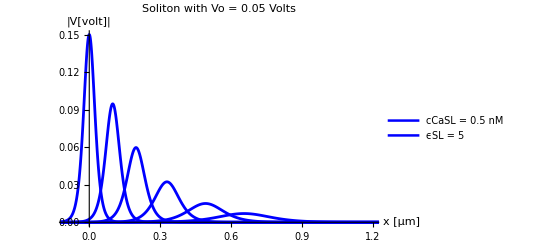

```mathematica
solSP22=Plot[ {Abs[Wx[x*10^-6,0]*gamma*nuZe^(1/2)/24],
Abs[Wx[x*10^-6,tmaxThisFile/10]*gamma*nuZe^(1/2)/24],Abs[Wx[x*10^-6,tmaxThisFile/5]*gamma*nuZe^(1/2)/24],Abs[Wx[x*10^-6,tmaxThisFile/3]*gamma*nuZe^(1/2)/24],
Abs[Wx[x*10^-6,tmaxThisFile/2]*gamma*nuZe^(1/2)/24],Abs[Wx[x*10^-6,tmaxThisFile/1.5]*gamma*nuZe^(1/2)/24]},
{x,-25*beta*10^6,120*beta*10^6},PlotRange->{{-0.1,1.2},{0,0.15}},PlotLegends->{"cCaSL = 0.5 nM", "ϵSL = 5"},PlotLabel->"Soliton with Vo = 0.05 Volts",Axes->True,AxesLabel->{"x [μm]","|V[volt]|"},AxesStyle->Directive[Black,FontSize-> 18],TicksStyle->Directive[18],PlotStyle->{{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]}},PlotLegends->Placed[{},{0.87,0.6}],LabelStyle->{18}]
```

```mathematica
solSP22Data=Cases[solSP22,Line[{x__}]->x,∞];
```

{{-0.27,2.23047×10^-8},{-0.26952,2.29939×10^-8},{-0.269039,2.37044×10^-8},{-0.268079,2.51919×10^-8},{-0.267599,2.59703×10^-8},{-0.267118,2.67728×10^-8},{-0.266158,2.84529×10^-8},{-0.265677,2.93321×10^-8},{-0.265197,3.02385×10^-8},{-0.264237,3.2136×10^-8},{-0.262315,3.62959×10^-8},{-0.261835,3.74175×10^-8},{-0.261355,3.85736×10^-8},{-0.260394,4.09943×10^-8},{-0.259914,4.2261×10^-8},{-0.259434,4.35669×10^-8},{-0.258473,4.63009×10^-8},{-0.257993,4.77315×10^-8},{-0.257512,4.92064×10^-8},{-0.256552,5.22943×10^-8},{-0.254631,5.90636×10^-8},{-0.25415,6.08887×10^-8},{-0.25367,6.27701×10^-8},{-0.25271,6.67092×10^-8},{-0.252229,6.87705×10^-8},{-0.251749,7.08955×10^-8},{-0.250788,7.53444×10^-8},{-0.250308,7.76725×10^-8},{-0.249828,8.00726×10^-8},{-0.248867,8.50975×10^-8},{-0.246946,9.6113×10^-8},{-0.246466,9.90829×10^-8},{-0.245986,1.02145×10^-7},{-0.245025,1.08554×10^-7},{-0.244545,1.11909×10^-7},{-0.244064,1.15367×10^-7},{-0.243104,1.22606×10^-7},{-0.242624,1.26395×10^-7},{-0.242143,1.30301×10^-7},{-0.241183,1.38477×10^-7},{-0.239262,1.56403×10^-7},{-0.238741,1.61649×10^-7},{-0.23822,1.67071×10^-7},{-0.237179,1.78466×10^-7},{-0.236658,1.84453×10^-7},{-0.236137,1.90639×10^-7},{-0.235096,2.03643×10^-7},{-0.234575,2.10473×10^-7},{-0.234055,2.17533×10^-7},{-0.233013,2.32371×10^-7},{-0.230931,2.65151×10^-7},{-0.23041,2.74045×10^-7},{-0.229889,2.83237×10^-7},{-0.228848,3.02556×10^-7},{-0.228327,3.12704×10^-7},{-0.227806,3.23193×10^-7},{-0.226765,3.45238×10^-7},{-0.226244,3.56817×10^-7},{-0.225724,3.68786×10^-7},{-0.224682,3.9394×10^-7},{-0.2226,4.49513×10^-7},{-0.222079,4.64591×10^-7},{-0.221558,4.80174×10^-7},{-0.220517,5.12926×10^-7},{-0.219996,5.30131×10^-7},{-0.219475,5.47912×10^-7},{-0.218434,5.85284×10^-7},{-0.217913,6.04916×10^-7},{-0.217393,6.25206×10^-7},{-0.216351,6.6785×10^-7},{-0.214269,7.62064×10^-7},{-0.213748,7.87625×10^-7},{-0.213227,8.14043×10^-7},{-0.212186,8.69568×10^-7},{-0.211665,8.98735×10^-7},{-0.211144,9.2888×10^-7},{-0.210103,9.92238×10^-7},{-0.209582,1.02552×10^-6},{-0.209062,1.05992×10^-6},{-0.20802,1.13221×10^-6},{-0.205938,1.29193×10^-6},{-0.205451,1.33235×10^-6},{-0.204965,1.37403×10^-6},{-0.203993,1.46135×10^-6},{-0.203507,1.50707×10^-6},{-0.20302,1.55421×10^-6},{-0.202048,1.65298×10^-6},{-0.201562,1.70469×10^-6},{-0.201076,1.75802×10^-6},{-0.200103,1.86974×10^-6},{-0.198159,2.11493×10^-6},{-0.197672,2.18109×10^-6},{-0.197186,2.24933×10^-6},{-0.196214,2.39227×10^-6},{-0.195728,2.46711×10^-6},{-0.195241,2.54429×10^-6},{-0.194269,2.70598×10^-6},{-0.193783,2.79063×10^-6},{-0.193297,2.87793×10^-6},{-0.192324,3.06082×10^-6},{-0.19038,3.46219×10^-6},{-0.189893,3.57051×10^-6},{-0.189407,3.68221×10^-6},{-0.188435,3.9162×10^-6},{-0.187949,4.03872×10^-6},{-0.187463,4.16507×10^-6},{-0.18649,4.42974×10^-6},{-0.186004,4.56833×10^-6},{-0.185518,4.71124×10^-6},{-0.184545,5.01063×10^-6},{-0.182601,5.66768×10^-6},{-0.182115,5.84499×10^-6},{-0.181628,6.02785×10^-6},{-0.180656,6.4109×10^-6},{-0.18017,6.61146×10^-6},{-0.179684,6.81829×10^-6},{-0.178711,7.25157×10^-6},{-0.178225,7.47843×10^-6},{-0.177739,7.71238×10^-6},{-0.176767,8.20247×10^-6},{-0.174822,9.27807×10^-6},{-0.174345,9.56254×10^-6},{-0.173869,9.85574×10^-6},{-0.172915,0.0000104694},{-0.172439,0.0000107904},{-0.171962,0.0000111212},{-0.171009,0.0000118136},{-0.170532,0.0000121758},{-0.170055,0.0000125492},{-0.169102,0.0000133305},{-0.167196,0.0000150421},{-0.166719,0.0000155033},{-0.166242,0.0000159786},{-0.165289,0.0000169734},{-0.164812,0.0000174938},{-0.164336,0.0000180302},{-0.163382,0.0000191527},{-0.162906,0.00001974},{-0.162429,0.0000203452},{-0.161476,0.0000216118},{-0.159569,0.0000243867},{-0.159093,0.0000251343},{-0.158616,0.0000259049},{-0.157663,0.0000275177},{-0.157186,0.0000283614},{-0.156709,0.0000292309},{-0.155756,0.0000310507},{-0.155279,0.0000320027},{-0.154803,0.0000329839},{-0.153849,0.0000350373},{-0.151943,0.0000395357},{-0.151466,0.0000407477},{-0.15099,0.0000419969},{-0.150036,0.0000446114},{-0.14956,0.0000459791},{-0.149083,0.0000473887},{-0.14813,0.0000503388},{-0.147653,0.000051882},{-0.147176,0.0000534725},{-0.146223,0.0000568012},{-0.144317,0.0000640932},{-0.143799,0.0000662272},{-0.143282,0.0000684323},{-0.142248,0.0000730651},{-0.141731,0.0000754978},{-0.141214,0.0000780115},{-0.14018,0.0000832926},{-0.139663,0.0000860658},{-0.139146,0.0000889312},{-0.138112,0.0000949513},{-0.136044,0.000108241},{-0.135527,0.000111845},{-0.13501,0.000115568},{-0.133976,0.000123391},{-0.133459,0.000127498},{-0.132942,0.000131743},{-0.131907,0.000140659},{-0.13139,0.000145342},{-0.130873,0.00015018},{-0.129839,0.000160344},{-0.127771,0.000182781},{-0.127254,0.000188864},{-0.126737,0.00019515},{-0.125703,0.000208356},{-0.125186,0.000215289},{-0.124669,0.000222454},{-0.123635,0.000237506},{-0.123118,0.000245409},{-0.122601,0.000253575},{-0.121567,0.000270731},{-0.119498,0.000308598},{-0.118981,0.000318865},{-0.118464,0.000329472},{-0.11743,0.000351757},{-0.116913,0.000363457},{-0.116396,0.000375546},{-0.115362,0.000400943},{-0.114845,0.000414277},{-0.114328,0.000428054},{-0.113294,0.000456996},{-0.111226,0.000520872},{-0.110743,0.000537015},{-0.110261,0.000553656},{-0.109295,0.0005885},{-0.108813,0.000606734},{-0.10833,0.000625532},{-0.107365,0.000664889},{-0.106883,0.000685484},{-0.1064,0.000706716},{-0.105435,0.000751168},{-0.103505,0.000848611},{-0.103022,0.000874881},{-0.10254,0.000901961},{-0.101575,0.000958654},{-0.101092,0.000988319},{-0.10061,0.0010189},{-0.0996447,0.00108292},{-0.0991622,0.00111641},{-0.0986796,0.00115094},{-0.0977145,0.00122322},{-0.0957844,0.00138161},{-0.0953018,0.0014243},{-0.0948193,0.00146831},{-0.0938542,0.00156041},{-0.0933717,0.0016086},{-0.0928891,0.00165826},{-0.0919241,0.00176221},{-0.0914415,0.00181659},{-0.090959,0.00187263},{-0.0899939,0.00198993},{-0.0880638,0.00224686},{-0.0875812,0.00231607},{-0.0870987,0.00238741},{-0.0861336,0.00253667},{-0.0856511,0.00261474},{-0.0851685,0.00269518},{-0.0842034,0.00286351},{-0.0837209,0.00295153},{-0.0832384,0.00304223},{-0.0822733,0.00323199},{-0.0803431,0.0036473},{-0.0798202,0.00376862},{-0.0792972,0.00389392},{-0.0782514,0.00415699},{-0.0777284,0.00429502},{-0.0772055,0.00443756},{-0.0761596,0.00473675},{-0.0756367,0.00489371},{-0.0751137,0.00505577},{-0.0740679,0.00539587},{-0.0719761,0.00614477},{-0.0714532,0.00634735},{-0.0709302,0.00655647},{-0.0698843,0.00699508},{-0.0693614,0.00722499},{-0.0688385,0.00746227},{-0.0677926,0.00795979},{-0.0672696,0.0082205},{-0.0667467,0.00848949},{-0.0657008,0.00905332},{-0.0636091,0.0102916},{-0.0630861,0.0106258},{-0.0625632,0.0109705},{-0.0615173,0.0116922},{-0.0609944,0.01207},{-0.0604714,0.0124594},{-0.0594256,0.0132744},{-0.0589026,0.0137007},{-0.0583797,0.0141399},{-0.0573338,0.0150589},{-0.055242,0.0170682},{-0.0547191,0.0176084},{-0.0541962,0.0181645},{-0.0531503,0.0193262},{-0.0510585,0.0218582},{-0.0505356,0.0225371},{-0.0500127,0.0232351},{-0.0489668,0.0246903},{-0.046875,0.027849},{-0.0463616,0.0286772},{-0.0458482,0.0295271},{-0.0448214,0.0312932},{-0.0427678,0.0351013},{-0.0422544,0.0361127},{-0.041741,0.0371486},{-0.0407142,0.0392947},{-0.0386606,0.0438916},{-0.0381472,0.0451056},{-0.0376338,0.0463457},{-0.036607,0.0489049},{-0.0345534,0.0543406},{-0.0304462,0.0664546},{-0.0299328,0.0680796},{-0.0294194,0.0697277},{-0.0283926,0.07309},{-0.0263389,0.0800568},{-0.0222317,0.094714},{-0.0217183,0.0965868},{-0.0212049,0.0984632},{-0.0201781,0.102219},{-0.0181245,0.109683},{-0.0140173,0.123914},{-0.0135384,0.125468},{-0.0130595,0.126993},{-0.0121017,0.129945},{-0.0116228,0.131369},{-0.0111439,0.132754},{-0.0101861,0.135403},{-0.00970723,0.136662},{-0.00922833,0.137875},{-0.00827054,0.140156},{-0.00779164,0.141219},{-0.00731274,0.142229},{-0.00635495,0.144081},{-0.00587605,0.14492},{-0.00539716,0.145699},{-0.00491826,0.146416},{-0.00443936,0.147072},{-0.00396047,0.147663},{-0.00348157,0.14819},{-0.00300267,0.148651},{-0.00252378,0.149045},{-0.00204488,0.149372},{-0.00156598,0.149631},{-0.00108708,0.149822},{-0.000608188,0.149944},{-0.000129291,0.149997},{0.000349606,0.149982},{0.000828503,0.149897},{0.0013074,0.149743},{0.0017863,0.149521},{0.00226519,0.14923},{0.00274409,0.148872},{0.00322299,0.148447},{0.00370188,0.147956},{0.00418078,0.147399},{0.00465968,0.146778},{0.00513857,0.146094},{0.00561747,0.145348},{0.00609637,0.144541},{0.00705416,0.142751},{0.00753306,0.141771},{0.00801196,0.140736},{0.00896975,0.138511},{0.00944865,0.137323},{0.00992754,0.136089},{0.0108853,0.133486},{0.0128009,0.127803},{0.0132798,0.126295},{0.0137587,0.124757},{0.0147165,0.121597},{0.0166321,0.115003},{0.0171514,0.113167},{0.0176707,0.111314},{0.0187093,0.10757},{0.0207865,0.0999938},{0.0249408,0.0849583},{0.0254601,0.0831246},{0.0259794,0.0813062},{0.027018,0.0777199},{0.0290952,0.0707797},{0.0332496,0.0580097},{0.0337689,0.0565282},{0.0342882,0.0550733},{0.0353268,0.0522439},{0.0374039,0.0469094},{0.0379232,0.0456433},{0.0384425,0.044404},{0.0394811,0.0420055},{0.0415583,0.0375231},{0.0420776,0.0364667},{0.0425969,0.0354353},{0.0436355,0.0334464},{0.0457127,0.0297551},{0.046232,0.0288898},{0.0467513,0.0280467},{0.0477899,0.0264256},{0.0498671,0.0234329},{0.0503518,0.0227802},{0.0508366,0.022144},{0.0518062,0.0209201},{0.0537454,0.0186571},{0.0542302,0.0181279},{0.054715,0.0176127},{0.0556845,0.0166232},{0.0576237,0.0147986},{0.0581085,0.014373},{0.0585933,0.0139589},{0.0595629,0.0131645},{0.061502,0.0117031},{0.0619868,0.0113628},{0.0624716,0.0110319},{0.0634412,0.0103978},{0.0653804,0.00923323},{0.0658652,0.00896239},{0.0663499,0.00869926},{0.0673195,0.00819528},{0.0692587,0.00727101},{0.0697435,0.00705629},{0.0702283,0.00684777},{0.0711979,0.00644861},{0.073137,0.00571738},{0.0736218,0.00554766},{0.0741066,0.00538288},{0.0750762,0.0050676},{0.075561,0.00491684},{0.0760458,0.00477049},{0.0770154,0.00449053},{0.0775001,0.00435668},{0.0779849,0.00422676},{0.0789545,0.00397827},{0.0808937,0.00352374},{0.0813689,0.00342041},{0.0818442,0.00332007},{0.0827947,0.00312806},{0.0846957,0.00277639},{0.085171,0.00269477},{0.0856462,0.00261553},{0.0865967,0.00246392},{0.0884977,0.00218636},{0.088973,0.00212196},{0.0894483,0.00205945},{0.0903988,0.00193986},{0.090874,0.00188268},{0.0913493,0.00182717},{0.0922998,0.00172099},{0.092775,0.00167023},{0.0932503,0.00162095},{0.0942008,0.00152669},{0.0961018,0.00135423},{0.0965771,0.00131423},{0.0970523,0.00127541},{0.0980028,0.00120117},{0.0984781,0.00116567},{0.0989533,0.00113123},{0.0999038,0.00106534},{0.100379,0.00103385},{0.100854,0.00100328},{0.101805,0.000944829},{0.103706,0.00083791},{0.104181,0.000813121},{0.104656,0.000789064},{0.105607,0.00074306},{0.106082,0.00072107},{0.106557,0.000699731},{0.107508,0.000658923},{0.107983,0.000639418},{0.108458,0.00062049},{0.109409,0.000584294},{0.11131,0.000518103},{0.111826,0.000501476},{0.112341,0.000485383},{0.113373,0.000454726},{0.113888,0.00044013},{0.114404,0.000426003},{0.115435,0.000399091},{0.115951,0.000386279},{0.116466,0.000373878},{0.117498,0.000350255},{0.11956,0.000307389},{0.120076,0.000297518},{0.120592,0.000287964},{0.121623,0.000269765},{0.122139,0.000261101},{0.122654,0.000252715},{0.123686,0.000236742},{0.124201,0.000229138},{0.124717,0.000221777},{0.125748,0.000207758},{0.127811,0.000182321},{0.128327,0.000176464},{0.128842,0.000170795},{0.129873,0.000159997},{0.130389,0.000154856},{0.130905,0.000149881},{0.131936,0.000140405},{0.132452,0.000135893},{0.132967,0.000131527},{0.133999,0.000123211},{0.136061,0.000108121},{0.136577,0.000104647},{0.137093,0.000101284},{0.138124,0.0000948796},{0.13864,0.0000918307},{0.139155,0.0000888797},{0.140187,0.0000832591},{0.140702,0.0000805835},{0.141218,0.0000779938},{0.142249,0.0000730614},{0.144312,0.0000641125},{0.144793,0.0000621879},{0.145274,0.000060321},{0.146236,0.0000567536},{0.146717,0.0000550498},{0.147199,0.0000533972},{0.148161,0.0000502392},{0.148642,0.0000487309},{0.149123,0.000047268},{0.150086,0.0000444724},{0.15201,0.0000393675},{0.152491,0.0000381856},{0.152972,0.0000370392},{0.153935,0.0000348485},{0.154416,0.0000338023},{0.154897,0.0000327874},{0.155859,0.0000308482},{0.15634,0.000029922},{0.156822,0.0000290237},{0.157784,0.000027307},{0.159708,0.0000241724},{0.16019,0.0000234466},{0.160671,0.0000227426},{0.161633,0.0000213975},{0.162114,0.000020755},{0.162595,0.0000201319},{0.163558,0.0000189411},{0.164039,0.0000183724},{0.16452,0.0000178208},{0.165482,0.0000167668},{0.167407,0.000014842},{0.167888,0.0000143963},{0.168369,0.0000139641},{0.169331,0.0000131381},{0.169813,0.0000127437},{0.170294,0.000012361},{0.171256,0.0000116299},{0.171737,0.0000112807},{0.172218,0.000010942},{0.173181,0.0000102948},{0.175105,9.11295×10^-6},{0.175627,8.81674×10^-6},{0.176148,8.53015×10^-6},{0.177191,7.98461×10^-6},{0.177713,7.72507×10^-6},{0.178235,7.47397×10^-6},{0.179278,6.99598×10^-6},{0.179799,6.76857×10^-6},{0.180321,6.54855×10^-6},{0.181364,6.12975×10^-6},{0.18345,5.37077×10^-6},{0.183972,5.19619×10^-6},{0.184493,5.02729×10^-6},{0.185536,4.70577×10^-6},{0.186058,4.55281×10^-6},{0.186579,4.40481×10^-6},{0.187622,4.12311×10^-6},{0.188144,3.98908×10^-6},{0.188665,3.85941×10^-6},{0.189709,3.61259×10^-6},{0.191795,3.16528×10^-6},{0.192316,3.06239×10^-6},{0.192838,2.96284×10^-6},{0.193881,2.77336×10^-6},{0.194402,2.68321×10^-6},{0.194924,2.59599×10^-6},{0.195967,2.42996×10^-6},{0.196489,2.35097×10^-6},{0.19701,2.27455×10^-6},{0.198053,2.12908×10^-6},{0.20014,1.86546×10^-6},{0.200661,1.80482×10^-6},{0.201183,1.74615×10^-6},{0.202226,1.63448×10^-6},{0.202747,1.58135×10^-6},{0.203269,1.52995×10^-6},{0.204312,1.4321×10^-6},{0.204833,1.38555×10^-6},{0.205355,1.34051×10^-6},{0.206398,1.25478×10^-6},{0.208484,1.09941×10^-6},{0.208996,1.06431×10^-6},{0.209508,1.03034×10^-6},{0.210532,9.65611×10^-7},{0.211044,9.34787×10^-7},{0.211556,9.04948×10^-7},{0.21258,8.48096×10^-7},{0.213092,8.21024×10^-7},{0.213604,7.94816×10^-7},{0.214628,7.44883×10^-7},{0.216676,6.54231×10^-7},{0.217188,6.33347×10^-7},{0.2177,6.1313×10^-7},{0.218724,5.74611×10^-7},{0.219237,5.56268×10^-7},{0.219749,5.38512×10^-7},{0.220773,5.04681×10^-7},{0.221285,4.88571×10^-7},{0.221797,4.72975×10^-7},{0.222821,4.43261×10^-7},{0.224869,3.89316×10^-7},{0.225381,3.76889×10^-7},{0.225893,3.64858×10^-7},{0.226917,3.41936×10^-7},{0.227429,3.31021×10^-7},{0.227941,3.20455×10^-7},{0.228965,3.00323×10^-7},{0.229477,2.90736×10^-7},{0.229989,2.81455×10^-7},{0.231013,2.63773×10^-7},{0.233061,2.31672×10^-7},{0.233573,2.24277×10^-7},{0.234085,2.17118×10^-7},{0.235109,2.03477×10^-7},{0.235621,1.96982×10^-7},{0.236133,1.90694×10^-7},{0.237157,1.78714×10^-7},{0.237669,1.73009×10^-7},{0.238181,1.67487×10^-7},{0.239205,1.56965×10^-7},{0.241253,1.37862×10^-7},{0.24173,1.33753×10^-7},{0.242208,1.29767×10^-7},{0.243163,1.22148×10^-7},{0.24364,1.18507×10^-7},{0.244118,1.14976×10^-7},{0.245073,1.08225×10^-7},{0.245551,1.04999×10^-7},{0.246028,1.0187×10^-7},{0.246983,9.58886×10^-8},{0.248893,8.49587×10^-8},{0.249371,8.24267×10^-8},{0.249848,7.99702×10^-8},{0.250803,7.52746×10^-8},{0.251281,7.30313×10^-8},{0.251758,7.08547×10^-8},{0.252713,6.66944×10^-8},{0.253191,6.47067×10^-8},{0.253668,6.27783×10^-8},{0.254623,5.90922×10^-8},{0.256533,5.23565×10^-8},{0.257011,5.07962×10^-8},{0.257488,4.92823×10^-8},{0.258443,4.63886×10^-8},{0.258921,4.50061×10^-8},{0.259398,4.36649×10^-8},{0.260353,4.1101×10^-8},{0.260831,3.98761×10^-8},{0.261308,3.86877×10^-8},{0.262263,3.64161×10^-8},{0.264173,3.22652×10^-8},{0.264651,3.13036×10^-8},{0.265128,3.03707×10^-8},{0.266083,2.85874×10^-8},{0.266561,2.77354×10^-8},{0.267038,2.69088×10^-8},{0.267993,2.53288×10^-8},{0.268471,2.4574×10^-8},{0.268948,2.38416×10^-8},{0.269903,2.24417×10^-8},{0.271813,1.98837×10^-8},{0.272331,1.92418×10^-8},{0.272849,1.86206×10^-8},{0.273885,1.74378×10^-8},{0.274403,1.68748×10^-8},{0.274921,1.63301×10^-8},{0.275957,1.52927×10^-8},{0.276474,1.4799×10^-8},{0.276992,1.43213×10^-8},{0.278028,1.34115×10^-8},{0.2801,1.17618×10^-8},{0.280618,1.13821×10^-8},{0.281136,1.10146×10^-8},{0.282171,1.03149×10^-8},{0.282689,9.98195×10^-9},{0.283207,9.65971×10^-9},{0.284243,9.04609×10^-9},{0.284761,8.75406×10^-9},{0.285279,8.47145×10^-9},{0.286315,7.93332×10^-9},{0.288386,6.95743×10^-9},{0.288904,6.73283×10^-9},{0.289422,6.51547×10^-9},{0.290458,6.10159×10^-9},{0.290976,5.90461×10^-9},{0.291494,5.71399×10^-9},{0.292529,5.35102×10^-9},{0.293047,5.17828×10^-9},{0.293565,5.01111×10^-9},{0.294601,4.69279×10^-9},{0.296673,4.11552×10^-9},{0.297191,3.98266×10^-9},{0.297709,3.85409×10^-9},{0.298744,3.60927×10^-9},{0.299262,3.49275×10^-9},{0.29978,3.37999×10^-9},{0.300816,3.16528×10^-9},{0.301334,3.0631×10^-9},{0.301852,2.96422×10^-9},{0.302888,2.77592×10^-9},{0.304959,2.43445×10^-9},{0.305443,2.36101×10^-9},{0.305926,2.2898×10^-9},{0.306893,2.15374×10^-9},{0.307376,2.08877×10^-9},{0.30786,2.02576×10^-9},{0.308826,1.90539×10^-9},{0.30931,1.84792×10^-9},{0.309793,1.79218×10^-9},{0.31076,1.68569×10^-9},{0.312694,1.49131×10^-9},{0.313177,1.44633×10^-9},{0.31366,1.4027×10^-9},{0.314627,1.31935×10^-9},{0.315111,1.27955×10^-9},{0.315594,1.24096×10^-9},{0.316561,1.16722×10^-9},{0.317044,1.13201×10^-9},{0.317528,1.09786×10^-9},{0.318494,1.03263×10^-9},{0.320428,9.13559×10^-10},{0.320911,8.86002×10^-10},{0.321395,8.59276×10^-10},{0.322362,8.08218×10^-10},{0.322845,7.83838×10^-10},{0.323328,7.60194×10^-10},{0.324295,7.15024×10^-10},{0.324779,6.93455×10^-10},{0.325262,6.72538×10^-10},{0.326229,6.32576×10^-10},{0.328162,5.59635×10^-10},{0.328646,5.42753×10^-10},{0.329129,5.26381×10^-10},{0.330096,4.95104×10^-10},{0.330579,4.80169×10^-10},{0.331063,4.65685×10^-10},{0.33203,4.38014×10^-10},{0.332513,4.24802×10^-10},{0.332996,4.11988×10^-10},{0.333963,3.87508×10^-10},{0.335897,3.42825×10^-10},{0.336421,3.31634×10^-10},{0.336944,3.20808×10^-10},{0.337992,3.00205×10^-10},{0.338516,2.90405×10^-10},{0.33904,2.80925×10^-10},{0.340087,2.62883×10^-10},{0.340611,2.54302×10^-10},{0.341135,2.46×10^-10},{0.342182,2.30201×10^-10},{0.344278,2.01583×10^-10},{0.344801,1.95002×10^-10},{0.345325,1.88637×10^-10},{0.346373,1.76522×10^-10},{0.346897,1.70759×10^-10},{0.34742,1.65185×10^-10},{0.348468,1.54577×10^-10},{0.348992,1.49531×10^-10},{0.349516,1.44649×10^-10},{0.350563,1.3536×10^-10},{0.352658,1.18532×10^-10},{0.353182,1.14662×10^-10},{0.353706,1.10919×10^-10},{0.354754,1.03796×10^-10},{0.355277,1.00407×10^-10},{0.355801,9.71297×10^-11},{0.356849,9.08918×10^-11},{0.357373,8.79247×10^-11},{0.357896,8.50545×10^-11},{0.358944,7.95921×10^-11},{0.361039,6.96971×10^-11},{0.361563,6.74219×10^-11},{0.362087,6.5221×10^-11},{0.363134,6.10324×10^-11},{0.363658,5.904×10^-11},{0.364182,5.71127×10^-11},{0.36523,5.34448×10^-11},{0.365753,5.17001×10^-11},{0.366277,5.00124×10^-11},{0.367325,4.68005×10^-11},{0.36942,4.09823×10^-11},{0.369934,3.96684×10^-11},{0.370448,3.83966×10^-11},{0.371477,3.59742×10^-11},{0.371991,3.48209×10^-11},{0.372505,3.37045×10^-11},{0.373534,3.15781×10^-11},{0.374048,3.05657×10^-11},{0.374563,2.95858×10^-11},{0.375591,2.77192×10^-11},{0.377648,2.43319×10^-11},{0.378162,2.35518×10^-11},{0.378677,2.27968×10^-11},{0.379705,2.13585×10^-11},{0.380219,2.06738×10^-11},{0.380734,2.0011×10^-11},{0.381762,1.87485×10^-11},{0.382276,1.81474×10^-11},{0.382791,1.75656×10^-11},{0.383819,1.64574×10^-11},{0.385876,1.44463×10^-11},{0.386391,1.39831×10^-11},{0.386905,1.35348×10^-11},{0.387933,1.26809×10^-11},{0.388448,1.22744×10^-11},{0.388962,1.18809×10^-11},{0.38999,1.11313×10^-11},{0.390505,1.07744×10^-11},{0.391019,1.0429×10^-11},{0.392047,9.77103×10^-12},{0.394104,8.577×10^-12},{0.394619,8.30202×10^-12},{0.395133,8.03587×10^-12},{0.396162,7.52888×10^-12},{0.396676,7.28751×10^-12},{0.39719,7.05387×10^-12},{0.398219,6.60884×10^-12},{0.398733,6.39696×10^-12},{0.399247,6.19188×10^-12},{0.400276,5.80123×10^-12},{0.402333,5.09231×10^-12},{0.402812,4.93984×10^-12},{0.403292,4.79194×10^-12},{0.404252,4.50929×10^-12},{0.404731,4.37428×10^-12},{0.405211,4.24331×10^-12},{0.406171,3.99301×10^-12},{0.40665,3.87346×10^-12},{0.40713,3.75749×10^-12},{0.40809,3.53585×10^-12},{0.410009,3.13103×10^-12},{0.410489,3.03728×10^-12},{0.410968,2.94634×10^-12},{0.411928,2.77255×10^-12},{0.412408,2.68954×10^-12},{0.412887,2.60901×10^-12},{0.413847,2.45512×10^-12},{0.414327,2.38161×10^-12},{0.414806,2.3103×10^-12},{0.415766,2.17403×10^-12},{0.417685,1.92512×10^-12},{0.418165,1.86748×10^-12},{0.418644,1.81157×10^-12},{0.419604,1.70471×10^-12},{0.420084,1.65367×10^-12},{0.420563,1.60416×10^-12},{0.421523,1.50954×10^-12},{0.422003,1.46434×10^-12},{0.422482,1.4205×10^-12},{0.423442,1.33671×10^-12},{0.425361,1.18367×10^-12},{0.425841,1.14823×10^-12},{0.426321,1.11385×10^-12},{0.42728,1.04815×10^-12},{0.42776,1.01677×10^-12},{0.42824,9.86324×10^-13},{0.429199,9.28146×10^-13},{0.429679,9.00356×10^-13},{0.430159,8.73399×10^-13},{0.431118,8.21881×10^-13},{0.433037,7.27783×10^-13},{0.433557,7.04188×10^-13},{0.434077,6.81358×10^-13},{0.435118,6.37894×10^-13},{0.435638,6.17213×10^-13},{0.436158,5.97202×10^-13},{0.437198,5.59106×10^-13},{0.437719,5.4098×10^-13},{0.438239,5.23441×10^-13},{0.439279,4.9005×10^-13},{0.44136,4.29523×10^-13},{0.44188,4.15598×10^-13},{0.4424,4.02124×10^-13},{0.44344,3.76472×10^-13},{0.44396,3.64267×10^-13},{0.444481,3.52457×10^-13},{0.445521,3.29974×10^-13},{0.446041,3.19276×10^-13},{0.446561,3.08924×10^-13},{0.447601,2.89218×10^-13},{0.449682,2.53496×10^-13},{0.450202,2.45278×10^-13},{0.450722,2.37326×10^-13},{0.451763,2.22187×10^-13},{0.452283,2.14983×10^-13},{0.452803,2.08013×10^-13},{0.453843,1.94744×10^-13},{0.454364,1.8843×10^-13},{0.454884,1.82321×10^-13},{0.455924,1.70691×10^-13},{0.458005,1.49608×10^-13},{0.458525,1.44758×10^-13},{0.459045,1.40065×10^-13},{0.460085,1.3113×10^-13},{0.460605,1.26879×10^-13},{0.461126,1.22765×10^-13},{0.462166,1.14934×10^-13},{0.462686,1.11208×10^-13},{0.463206,1.07602×10^-13},{0.464246,1.00738×10^-13},{0.466327,8.8296×10^-14},{0.466813,8.56204×10^-14},{0.467298,8.30258×10^-14},{0.46827,7.80702×10^-14},{0.468755,7.57044×10^-14},{0.469241,7.34103×10^-14},{0.470212,6.90286×10^-14},{0.470698,6.69369×10^-14},{0.471184,6.49085×10^-14},{0.472155,6.10342×10^-14},{0.474098,5.39657×10^-14},{0.474583,5.23304×10^-14},{0.475069,5.07446×10^-14},{0.47604,4.77158×10^-14},{0.476526,4.62698×10^-14},{0.477011,4.48677×10^-14},{0.477983,4.21897×10^-14},{0.478468,4.09112×10^-14},{0.478954,3.96714×10^-14},{0.479925,3.73035×10^-14},{0.481868,3.29833×10^-14},{0.482354,3.19838×10^-14},{0.482839,3.10146×10^-14},{0.483811,2.91634×10^-14},{0.484296,2.82797×10^-14},{0.484782,2.74227×10^-14},{0.485753,2.57859×10^-14},{0.486239,2.50045×10^-14},{0.486724,2.42468×10^-14},{0.487696,2.27996×10^-14},{0.489638,2.01591×10^-14},{0.490124,1.95482×10^-14},{0.49061,1.89558×10^-14},{0.491581,1.78244×10^-14},{0.492067,1.72843×10^-14},{0.492552,1.67605×10^-14},{0.493524,1.57601×10^-14},{0.494009,1.52825×10^-14},{0.494495,1.48194×10^-14},{0.495466,1.39349×10^-14},{0.497409,1.2321×10^-14},{0.498361,1.15996×10^-14},{0.499313,1.09205×10^-14},{0.500265,1.02811×10^-14},{0.501218,9.67911×10^-15},{0.50217,9.11239×10^-15},{0.503122,8.57886×10^-15},{0.505027,7.60367×10^-15},{0.505979,7.15847×10^-15},{0.506931,6.73934×10^-15},{0.507883,6.34474×10^-15},{0.508836,5.97326×10^-15},{0.509788,5.62352×10^-15},{0.51074,5.29426×10^-15},{0.512644,4.69244×10^-15},{0.513597,4.4177×10^-15},{0.514549,4.15904×10^-15},{0.515501,3.91552×10^-15},{0.516453,3.68627×10^-15},{0.518358,3.26724×10^-15},{0.520262,2.89584×10^-15},{0.522167,2.56666×10^-15},{0.524071,2.2749×10^-15},{0.525976,2.01631×10^-15},{0.52788,1.78711×10^-15},{0.529946,1.56782×10^-15},{0.532012,1.37545×10^-15},{0.534078,1.20668×10^-15},{0.536144,1.05862×10^-15},{0.53821,9.28722×10^-16},{0.540276,8.14766×10^-16},{0.540793,7.88533×10^-16},{0.541309,7.63144×10^-16},{0.542342,7.14793×10^-16},{0.544408,6.27086×10^-16},{0.548541,4.82638×10^-16},{0.552673,3.71463×10^-16},{0.553189,3.59503×10^-16},{0.553706,3.47928×10^-16},{0.554739,3.25884×10^-16},{0.556805,2.85897×10^-16},{0.560937,2.20041×10^-16},{0.561419,2.13423×10^-16},{0.561901,2.07003×10^-16},{0.562865,1.94738×10^-16},{0.564793,1.72343×10^-16},{0.568649,1.34985×10^-16},{0.576361,8.28067×10^-17},{0.591785,3.11621×10^-17},{0.62522,3.74628×10^-18},{0.658043,4.68134×10^-19},{0.688659,6.72834×10^-20},{0.72186,8.20913×10^-21},{0.752852,1.152×10^-21},{0.783234,1.68038×10^-22},{0.816202,2.08071×10^-23},{0.846962,2.96336×10^-24},{0.880307,3.58269×10^-25},{0.911443,4.98197×10^-26},{0.94197,7.20094×10^-27},{0.975082,8.83546×10^-28},{1.00599,1.24691×10^-28},{1.03947,1.49381×10^-29},{1.07235,1.86016×10^-30},{1.10302,2.66425×10^-31},{1.13628,3.23929×10^-32},{1.16733,4.52993×10^-33},{1.19776,6.58462×10^-34},{1.23079,8.12495×10^-35},{1.2616,1.15313×10^-35},{1.26214,1.11452×10^-35},{1.26268,1.07721×10^-35},{1.26375,1.00628×10^-35},{1.2659,8.78131×10^-36},{1.2702,6.68712×10^-36},{1.2788,3.87793×10^-36},{1.27934,3.74809×10^-36},{1.27988,3.6226×10^-36},{1.28095,3.38408×10^-36},{1.2831,2.95311×10^-36},{1.2874,2.24885×10^-36},{1.28794,2.17356×10^-36},{1.28848,2.10078×10^-36},{1.28955,1.96246×10^-36},{1.2917,1.71254×10^-36},{1.29224,1.6552×10^-36},{1.29278,1.59978×10^-36},{1.29385,1.49445×10^-36},{1.29439,1.44441×10^-36},{1.29493,1.39605×10^-36},{1.29546,1.34931×10^-36},{1.296,1.30413×10^-36},{-0.27,3.22262×10^-9},{-0.26952,3.30146×10^-9},{-0.269039,3.38222×10^-9},{-0.268079,3.54971×10^-9},{-0.266158,3.91×10^-9},{-0.265677,4.00565×10^-9},{-0.265197,4.10363×10^-9},{-0.264237,4.30685×10^-9},{-0.262315,4.74399×10^-9},{-0.261835,4.86003×10^-9},{-0.261355,4.97892×10^-9},{-0.260394,5.22549×10^-9},{-0.258473,5.75586×10^-9},{-0.257993,5.89666×10^-9},{-0.257512,6.04091×10^-9},{-0.256552,6.34007×10^-9},{-0.254631,6.98357×10^-9},{-0.25415,7.1544×10^-9},{-0.25367,7.32941×10^-9},{-0.25271,7.69238×10^-9},{-0.250788,8.47314×10^-9},{-0.250308,8.68041×10^-9},{-0.249828,8.89275×10^-9},{-0.248867,9.33314×10^-9},{-0.246946,1.02804×10^-8},{-0.246466,1.05319×10^-8},{-0.245986,1.07895×10^-8},{-0.245025,1.13239×10^-8},{-0.243104,1.24732×10^-8},{-0.242624,1.27783×10^-8},{-0.242143,1.30909×10^-8},{-0.241183,1.37392×10^-8},{-0.239262,1.51337×10^-8},{-0.238741,1.55354×10^-8},{-0.23822,1.59479×10^-8},{-0.237179,1.68058×10^-8},{-0.235096,1.86627×10^-8},{-0.234575,1.91581×10^-8},{-0.234055,1.96667×10^-8},{-0.233013,2.07248×10^-8},{-0.230931,2.30146×10^-8},{-0.23041,2.36256×10^-8},{-0.229889,2.42528×10^-8},{-0.228848,2.55576×10^-8},{-0.226765,2.83814×10^-8},{-0.226244,2.91349×10^-8},{-0.225724,2.99083×10^-8},{-0.224682,3.15173×10^-8},{-0.2226,3.49997×10^-8},{-0.222079,3.59288×10^-8},{-0.221558,3.68826×10^-8},{-0.220517,3.88668×10^-8},{-0.218434,4.31612×10^-8},{-0.217913,4.4307×10^-8},{-0.217393,4.54832×10^-8},{-0.216351,4.79301×10^-8},{-0.214269,5.32259×10^-8},{-0.213748,5.46389×10^-8},{-0.213227,5.60894×10^-8},{-0.212186,5.91069×10^-8},{-0.210103,6.56376×10^-8},{-0.209582,6.73801×10^-8},{-0.209062,6.91688×10^-8},{-0.20802,7.289×10^-8},{-0.205938,8.09436×10^-8},{-0.205451,8.29483×10^-8},{-0.204965,8.50026×10^-8},{-0.203993,8.9265×10^-8},{-0.202048,9.84419×10^-8},{-0.201562,1.0088×10^-7},{-0.201076,1.03378×10^-7},{-0.200103,1.08562×10^-7},{-0.198159,1.19723×10^-7},{-0.197672,1.22688×10^-7},{-0.197186,1.25726×10^-7},{-0.196214,1.32031×10^-7},{-0.194269,1.45604×10^-7},{-0.193783,1.4921×10^-7},{-0.193297,1.52906×10^-7},{-0.192324,1.60573×10^-7},{-0.19038,1.77081×10^-7},{-0.189893,1.81467×10^-7},{-0.189407,1.85961×10^-7},{-0.188435,1.95286×10^-7},{-0.18649,2.15362×10^-7},{-0.186004,2.20696×10^-7},{-0.185518,2.26161×10^-7},{-0.184545,2.37502×10^-7},{-0.182601,2.61919×10^-7},{-0.182115,2.68405×10^-7},{-0.181628,2.75053×10^-7},{-0.180656,2.88845×10^-7},{-0.178711,3.1854×10^-7},{-0.178225,3.26429×10^-7},{-0.177739,3.34513×10^-7},{-0.176767,3.51287×10^-7},{-0.174822,3.87401×10^-7},{-0.174345,3.96805×10^-7},{-0.173869,4.06437×10^-7},{-0.172915,4.26408×10^-7},{-0.171009,4.69343×10^-7},{-0.170532,4.80736×10^-7},{-0.170055,4.92406×10^-7},{-0.169102,5.16601×10^-7},{-0.167196,5.68618×10^-7},{-0.166719,5.82421×10^-7},{-0.166242,5.96558×10^-7},{-0.165289,6.25872×10^-7},{-0.163382,6.88891×10^-7},{-0.162906,7.05613×10^-7},{-0.162429,7.22741×10^-7},{-0.161476,7.58255×10^-7},{-0.159569,8.34603×10^-7},{-0.159093,8.54862×10^-7},{-0.158616,8.75614×10^-7},{-0.157663,9.18639×10^-7},{-0.155756,1.01114×10^-6},{-0.155279,1.03568×10^-6},{-0.154803,1.06082×10^-6},{-0.153849,1.11295×10^-6},{-0.151943,1.22501×10^-6},{-0.151466,1.25474×10^-6},{-0.15099,1.2852×10^-6},{-0.150036,1.34835×10^-6},{-0.14813,1.48412×10^-6},{-0.147653,1.52014×10^-6},{-0.147176,1.55704×10^-6},{-0.146223,1.63355×10^-6},{-0.144317,1.79803×10^-6},{-0.143799,1.84543×10^-6},{-0.143282,1.89407×10^-6},{-0.142248,1.99523×10^-6},{-0.14018,2.21406×10^-6},{-0.139663,2.27242×10^-6},{-0.139146,2.33232×10^-6},{-0.138112,2.45689×10^-6},{-0.136044,2.72635×10^-6},{-0.135527,2.79821×10^-6},{-0.13501,2.87197×10^-6},{-0.133976,3.02536×10^-6},{-0.131907,3.35717×10^-6},{-0.13139,3.44566×10^-6},{-0.130873,3.53648×10^-6},{-0.129839,3.72536×10^-6},{-0.127771,4.13394×10^-6},{-0.127254,4.2429×10^-6},{-0.126737,4.35474×10^-6},{-0.125703,4.58733×10^-6},{-0.123635,5.09044×10^-6},{-0.123118,5.22461×10^-6},{-0.122601,5.36232×10^-6},{-0.121567,5.64872×10^-6},{-0.119498,6.26823×10^-6},{-0.118981,6.43345×10^-6},{-0.118464,6.60302×10^-6},{-0.11743,6.95569×10^-6},{-0.115362,7.71853×10^-6},{-0.114845,7.92197×10^-6},{-0.114328,8.13078×10^-6},{-0.113294,8.56504×10^-6},{-0.111226,9.50437×10^-6},{-0.110743,9.73796×10^-6},{-0.110261,9.97729×10^-6},{-0.109295,0.0000104737},{-0.107365,0.000011542},{-0.106883,0.0000118256},{-0.1064,0.0000121162},{-0.105435,0.0000127191},{-0.103505,0.0000140163},{-0.103022,0.0000143608},{-0.10254,0.0000147137},{-0.101575,0.0000154458},{-0.0996447,0.0000170211},{-0.0991622,0.0000174394},{-0.0986796,0.000017868},{-0.0977145,0.000018757},{-0.0957844,0.00002067},{-0.0953018,0.0000211779},{-0.0948193,0.0000216984},{-0.0938542,0.000022778},{-0.0919241,0.000025101},{-0.0914415,0.0000257178},{-0.090959,0.0000263498},{-0.0899939,0.0000276608},{-0.0880638,0.0000304816},{-0.0875812,0.0000312307},{-0.0870987,0.0000319982},{-0.0861336,0.0000335901},{-0.0842034,0.0000370155},{-0.0837209,0.0000379251},{-0.0832384,0.000038857},{-0.0822733,0.0000407902},{-0.0803431,0.0000449496},{-0.0798202,0.0000461478},{-0.0792972,0.000047378},{-0.0782514,0.0000499374},{-0.0761596,0.0000554786},{-0.0756367,0.0000569574},{-0.0751137,0.0000584755},{-0.0740679,0.0000616343},{-0.0719761,0.0000684729},{-0.0714532,0.0000702979},{-0.0709302,0.0000721716},{-0.0698843,0.0000760699},{-0.0677926,0.0000845095},{-0.0672696,0.0000867617},{-0.0667467,0.0000890739},{-0.0657008,0.0000938848},{-0.0636091,0.0001043},{-0.0630861,0.000107079},{-0.0625632,0.000109932},{-0.0615173,0.000115869},{-0.0594256,0.000128721},{-0.0589026,0.000132151},{-0.0583797,0.000135672},{-0.0573338,0.000142998},{-0.055242,0.000158856},{-0.0547191,0.000163088},{-0.0541962,0.000167433},{-0.0531503,0.000176472},{-0.0510585,0.000196039},{-0.0505356,0.00020126},{-0.0500127,0.000206621},{-0.0489668,0.000217773},{-0.046875,0.000241914},{-0.0463616,0.000248236},{-0.0458482,0.000254724},{-0.0448214,0.000268212},{-0.0427678,0.000297364},{-0.0422544,0.000305134},{-0.041741,0.000313106},{-0.0407142,0.00032968},{-0.0386606,0.0003655},{-0.0381472,0.000375047},{-0.0376338,0.000384842},{-0.036607,0.000405205},{-0.0345534,0.000449212},{-0.03404,0.000460939},{-0.0335266,0.000472972},{-0.0324998,0.000497986},{-0.0304462,0.00055204},{-0.0299328,0.000566443},{-0.0294194,0.000581222},{-0.0283926,0.000611942},{-0.0263389,0.000678321},{-0.0258255,0.000696007},{-0.0253121,0.000714153},{-0.0242853,0.000751871},{-0.0222317,0.000833361},{-0.0217183,0.000855071},{-0.0212049,0.000877345},{-0.0201781,0.000923639},{-0.0181245,0.00102364},{-0.0176111,0.00105028},{-0.0170977,0.00107761},{-0.0160709,0.00113441},{-0.0140173,0.00125708},{-0.0135384,0.00128754},{-0.0130595,0.00131872},{-0.0121017,0.00138335},{-0.0101861,0.0015222},{-0.00970723,0.00155902},{-0.00922833,0.00159673},{-0.00827054,0.00167486},{-0.00635495,0.00184268},{-0.00587605,0.00188718},{-0.00539716,0.00193273},{-0.00443936,0.00202713},{-0.00252378,0.00222983},{-0.00204488,0.00228355},{-0.00156598,0.00233856},{-0.000608188,0.00245252},{0.0013074,0.00269712},{0.0017863,0.00276194},{0.00226519,0.00282829},{0.00322299,0.00296573},{0.00513857,0.00326062},{0.00561747,0.00333873},{0.00609637,0.00341868},{0.00705416,0.00358425},{0.00896975,0.0039393},{0.00944865,0.00403331},{0.00992754,0.00412952},{0.0108853,0.0043287},{0.0128009,0.00475557},{0.0132798,0.00486853},{0.0137587,0.00498411},{0.0147165,0.00522331},{0.0166321,0.00573559},{0.0171514,0.00588265},{0.0176707,0.00603334},{0.0187093,0.00634599},{0.0207865,0.00701878},{0.0213058,0.00719739},{0.0218251,0.00738036},{0.0228637,0.00775975},{0.0249408,0.00857509},{0.0254601,0.00879131},{0.0259794,0.0090127},{0.027018,0.00947141},{0.0290952,0.0104557},{0.0296145,0.0107164},{0.0301338,0.0109831},{0.0311724,0.0115353},{0.0332496,0.0127179},{0.0337689,0.0130306},{0.0342882,0.0133503},{0.0353268,0.0140114},{0.0374039,0.015424},{0.0379232,0.0157967},{0.0384425,0.0161775},{0.0394811,0.0169639},{0.0415583,0.0186393},{0.0420776,0.0190802},{0.0425969,0.0195303},{0.0436355,0.020458},{0.0457127,0.0224278},{0.0498671,0.0268465},{0.0503518,0.0274054},{0.0508366,0.0279734},{0.0518062,0.0291374},{0.0537454,0.0315773},{0.0576237,0.036906},{0.0581085,0.0376136},{0.0585933,0.0383303},{0.0595629,0.0397903},{0.061502,0.0428143},{0.0653804,0.0492418},{0.0658652,0.0500767},{0.0663499,0.0509178},{0.0673195,0.0526171},{0.0692587,0.0560752},{0.073137,0.06314},{0.0736218,0.0640281},{0.0741066,0.0649157},{0.0750762,0.0666868},{0.0770154,0.070197},{0.0808937,0.0769481},{0.0813689,0.0777381},{0.0818442,0.0785177},{0.0827947,0.0800434},{0.0846957,0.0829415},{0.085171,0.0836303},{0.0856462,0.0843035},{0.0865967,0.0856005},{0.0884977,0.08798},{0.088973,0.0885266},{0.0894483,0.0890528},{0.0903988,0.0900418},{0.090874,0.0905034},{0.0913493,0.0909426},{0.0922998,0.0917516},{0.092775,0.0921205},{0.0932503,0.0924651},{0.0937255,0.0927851},{0.0942008,0.09308},{0.094676,0.0933497},{0.0951513,0.0935937},{0.0956266,0.0938118},{0.0961018,0.0940038},{0.0965771,0.0941694},{0.0970523,0.0943084},{0.0975276,0.0944208},{0.0980028,0.0945062},{0.0984781,0.0945648},{0.0989533,0.0945963},{0.0994286,0.0946008},{0.0999038,0.0945783},{0.100379,0.0945287},{0.100854,0.0944522},{0.10133,0.0943488},{0.101805,0.0942186},{0.10228,0.0940618},{0.102755,0.0938786},{0.103231,0.0936692},{0.103706,0.0934338},{0.104181,0.0931726},{0.104656,0.092886},{0.105132,0.0925743},{0.105607,0.0922379},{0.106082,0.091877},{0.106557,0.0914922},{0.107508,0.0906521},{0.107983,0.0901979},{0.108458,0.0897215},{0.109409,0.0887041},{0.11131,0.0864264},{0.111826,0.0857565},{0.112341,0.0850658},{0.113373,0.0836254},{0.115435,0.0805309},{0.11956,0.0736753},{0.127811,0.0587383},{0.128327,0.0578014},{0.128842,0.0568676},{0.129873,0.055012},{0.131936,0.051361},{0.136061,0.0443876},{0.136577,0.043553},{0.137093,0.0427274},{0.138124,0.0411043},{0.140187,0.0379748},{0.144312,0.0322083},{0.144793,0.0315797},{0.145274,0.0309603},{0.146236,0.0297491},{0.148161,0.0274371},{0.148642,0.026882},{0.149123,0.0263358},{0.150086,0.0252704},{0.15201,0.0232457},{0.152491,0.0227612},{0.152972,0.0222852},{0.153935,0.0213585},{0.155859,0.0196038},{0.159708,0.0164682},{0.16019,0.0161094},{0.160671,0.0157577},{0.161633,0.0150748},{0.163558,0.013789},{0.164039,0.0134836},{0.16452,0.0131844},{0.165482,0.0126042},{0.167407,0.011514},{0.167888,0.0112555},{0.168369,0.0110024},{0.169331,0.0105121},{0.171256,0.00959241},{0.171737,0.00937462},{0.172218,0.00916152},{0.173181,0.00874899},{0.175105,0.00797628},{0.175627,0.00777835},{0.176148,0.00758512},{0.177191,0.00721235},{0.179278,0.00651885},{0.179799,0.00635577},{0.180321,0.00619662},{0.181364,0.00588979},{0.18345,0.00531961},{0.183972,0.00518565},{0.184493,0.00505497},{0.185536,0.00480314},{0.187622,0.00433559},{0.188144,0.00422583},{0.188665,0.00411878},{0.189709,0.00391257},{0.191795,0.00353002},{0.192316,0.00344026},{0.192838,0.00335275},{0.193881,0.00318422},{0.195967,0.00287176},{0.196489,0.00279848},{0.19701,0.00272705},{0.198053,0.00258952},{0.20014,0.00233468},{0.200661,0.00227493},{0.201183,0.0022167},{0.202226,0.00210462},{0.204312,0.001897},{0.204833,0.00184835},{0.205355,0.00180093},{0.206398,0.00170968},{0.208484,0.0015407},{0.208996,0.00150182},{0.209508,0.00146392},{0.210532,0.00139094},{0.21258,0.00125564},{0.213092,0.00122391},{0.213604,0.00119298},{0.214628,0.00113343},{0.216676,0.00102304},{0.217188,0.000997156},{0.2177,0.000971924},{0.218724,0.00092335},{0.220773,0.000833332},{0.221285,0.000812228},{0.221797,0.000791655},{0.222821,0.000752055},{0.224869,0.000678676},{0.225381,0.000661474},{0.225893,0.000644707},{0.226917,0.000612433},{0.228965,0.000552638},{0.229477,0.000538621},{0.229989,0.00052496},{0.231013,0.000498664},{0.233061,0.00044995},{0.233573,0.000438532},{0.234085,0.000427403},{0.235109,0.000405984},{0.237157,0.000366306},{0.237669,0.000357007},{0.238181,0.000347943},{0.239205,0.000330499},{0.241253,0.000298187},{0.24173,0.000291118},{0.242208,0.000284217},{0.243163,0.000270901},{0.245073,0.000246109},{0.245551,0.000240273},{0.246028,0.000234576},{0.246983,0.000223583},{0.248893,0.000203117},{0.249371,0.0001983},{0.249848,0.000193597},{0.250803,0.000184522},{0.252713,0.000167628},{0.253191,0.000163652},{0.253668,0.00015977},{0.254623,0.00015228},{0.256533,0.000138336},{0.257011,0.000135054},{0.257488,0.00013185},{0.258443,0.000125668},{0.260353,0.000114159},{0.260831,0.00011145},{0.261308,0.000108806},{0.262263,0.000103703},{0.264173,0.0000942052},{0.264651,0.0000919697},{0.265128,0.0000897873},{0.266083,0.0000855765},{0.267993,0.0000777378},{0.268471,0.0000758929},{0.268948,0.0000740918},{0.269903,0.0000706168},{0.271813,0.000064148},{0.272331,0.0000624984},{0.272849,0.0000608912},{0.273885,0.0000577997},{0.275957,0.0000520796},{0.276474,0.0000507403},{0.276992,0.0000494354},{0.278028,0.0000469254},{0.2801,0.0000422811},{0.280618,0.0000411937},{0.281136,0.0000401343},{0.282171,0.0000380965},{0.284243,0.0000343259},{0.284761,0.000033443},{0.285279,0.0000325829},{0.286315,0.0000309284},{0.288386,0.0000278672},{0.288904,0.0000271505},{0.289422,0.0000264521},{0.290458,0.0000251089},{0.292529,0.0000226236},{0.293047,0.0000220417},{0.293565,0.0000214748},{0.294601,0.0000203843},{0.296673,0.0000183666},{0.297191,0.0000178942},{0.297709,0.0000174339},{0.298744,0.0000165486},{0.300816,0.0000149105},{0.301334,0.000014527},{0.301852,0.0000141534},{0.302888,0.0000134346},{0.304959,0.0000121048},{0.305443,0.0000118139},{0.305926,0.00001153},{0.306893,0.0000109826},{0.308826,9.96439×10^-6},{0.30931,9.72495×10^-6},{0.309793,9.49126×10^-6},{0.31076,9.0406×10^-6},{0.312694,8.20246×10^-6},{0.313177,8.00535×10^-6},{0.31366,7.81299×10^-6},{0.314627,7.44201×10^-6},{0.316561,6.75206×10^-6},{0.317044,6.58981×10^-6},{0.317528,6.43146×10^-6},{0.318494,6.12608×10^-6},{0.320428,5.55812×10^-6},{0.320911,5.42456×10^-6},{0.321395,5.29421×10^-6},{0.322362,5.04283×10^-6},{0.324295,4.5753×10^-6},{0.324779,4.46536×10^-6},{0.325262,4.35805×10^-6},{0.326229,4.15112×10^-6},{0.328162,3.76626×10^-6},{0.328646,3.67576×10^-6},{0.329129,3.58743×10^-6},{0.330096,3.41709×10^-6},{0.33203,3.10028×10^-6},{0.332513,3.02578×10^-6},{0.332996,2.95307×10^-6},{0.333963,2.81285×10^-6},{0.335897,2.55207×10^-6},{0.336421,2.48568×10^-6},{0.336944,2.42102×10^-6},{0.337992,2.29671×10^-6},{0.340087,2.0669×10^-6},{0.340611,2.01313×10^-6},{0.341135,1.96077×10^-6},{0.342182,1.86009×10^-6},{0.344278,1.67397×10^-6},{0.344801,1.63042×10^-6},{0.345325,1.58801×10^-6},{0.346373,1.50647×10^-6},{0.348468,1.35573×10^-6},{0.348992,1.32046×10^-6},{0.349516,1.28612×10^-6},{0.350563,1.22008×10^-6},{0.352658,1.098×10^-6},{0.353182,1.06943×10^-6},{0.353706,1.04161×10^-6},{0.354754,9.88129×10^-7},{0.356849,8.89257×10^-7},{0.357373,8.66125×10^-7},{0.357896,8.43595×10^-7},{0.358944,8.00277×10^-7},{0.361039,7.20201×10^-7},{0.361563,7.01467×10^-7},{0.362087,6.8322×10^-7},{0.363134,6.48138×10^-7},{0.36523,5.83285×10^-7},{0.365753,5.68112×10^-7},{0.366277,5.53334×10^-7},{0.367325,5.24921×10^-7},{0.36942,4.72397×10^-7},{0.369934,4.60329×10^-7},{0.370448,4.4857×10^-7},{0.371477,4.25945×10^-7},{0.373534,3.84062×10^-7},{0.374048,3.74251×10^-7},{0.374563,3.6469×10^-7},{0.375591,3.46296×10^-7},{0.377648,3.12244×10^-7},{0.378162,3.04268×10^-7},{0.378677,2.96496×10^-7},{0.379705,2.81541×10^-7},{0.381762,2.53857×10^-7},{0.382276,2.47372×10^-7},{0.382791,2.41053×10^-7},{0.383819,2.28894×10^-7},{0.385876,2.06387×10^-7},{0.386391,2.01115×10^-7},{0.386905,1.95977×10^-7},{0.387933,1.86093×10^-7},{0.38999,1.67794×10^-7},{0.390505,1.63507×10^-7},{0.391019,1.59331×10^-7},{0.392047,1.51294×10^-7},{0.394104,1.36417×10^-7},{0.394619,1.32933×10^-7},{0.395133,1.29537×10^-7},{0.396162,1.23003×10^-7},{0.398219,1.10908×10^-7},{0.398733,1.08075×10^-7},{0.399247,1.05314×10^-7},{0.400276,1.00002×10^-7},{0.402333,9.01689×10^-8},{0.402812,8.80182×10^-8},{0.403292,8.59188×10^-8},{0.404252,8.18691×10^-8},{0.406171,7.43332×10^-8},{0.40665,7.25602×10^-8},{0.40713,7.08296×10^-8},{0.40809,6.7491×10^-8},{0.410009,6.12786×10^-8},{0.410489,5.9817×10^-8},{0.410968,5.83903×10^-8},{0.411928,5.56381×10^-8},{0.413847,5.05167×10^-8},{0.414327,4.93118×10^-8},{0.414806,4.81356×10^-8},{0.415766,4.58668×10^-8},{0.417685,4.16448×10^-8},{0.418165,4.06515×10^-8},{0.418644,3.96819×10^-8},{0.419604,3.78115×10^-8},{0.421523,3.43311×10^-8},{0.422003,3.35122×10^-8},{0.422482,3.27129×10^-8},{0.423442,3.1171×10^-8},{0.425361,2.83017×10^-8},{0.425841,2.76267×10^-8},{0.426321,2.69677×10^-8},{0.42728,2.56966×10^-8},{0.429199,2.33313×10^-8},{0.429679,2.27748×10^-8},{0.430159,2.22316×10^-8},{0.431118,2.11837×10^-8},{0.433037,1.92338×10^-8},{0.433557,1.87369×10^-8},{0.434077,1.82529×10^-8},{0.435118,1.73219×10^-8},{0.437198,1.56001×10^-8},{0.437719,1.51971×10^-8},{0.438239,1.48045×10^-8},{0.439279,1.40495×10^-8},{0.44136,1.26529×10^-8},{0.44188,1.23261×10^-8},{0.4424,1.20076×10^-8},{0.44344,1.13952×10^-8},{0.445521,1.02625×10^-8},{0.446041,9.99741×10^-9},{0.446561,9.73914×10^-9},{0.447601,9.24243×10^-9},{0.449682,8.32373×10^-9},{0.450202,8.10869×10^-9},{0.450722,7.89921×10^-9},{0.451763,7.49634×10^-9},{0.453843,6.7512×10^-9},{0.454364,6.57679×10^-9},{0.454884,6.40688×10^-9},{0.455924,6.08013×10^-9},{0.458005,5.47576×10^-9},{0.458525,5.3343×10^-9},{0.459045,5.19649×10^-9},{0.460085,4.93146×10^-9},{0.462166,4.44127×10^-9},{0.462686,4.32654×10^-9},{0.463206,4.21476×10^-9},{0.464246,3.99981×10^-9},{0.466327,3.60222×10^-9},{0.466813,3.51526×10^-9},{0.467298,3.4304×10^-9},{0.46827,3.26677×10^-9},{0.470212,2.96255×10^-9},{0.470698,2.89103×10^-9},{0.471184,2.82124×10^-9},{0.472155,2.68667×10^-9},{0.474098,2.43647×10^-9},{0.474583,2.37765×10^-9},{0.475069,2.32025×10^-9},{0.47604,2.20958×10^-9},{0.477983,2.00381×10^-9},{0.478468,1.95544×10^-9},{0.478954,1.90823×10^-9},{0.479925,1.81721×10^-9},{0.481868,1.64798×10^-9},{0.482354,1.6082×10^-9},{0.482839,1.56937×10^-9},{0.483811,1.49452×10^-9},{0.485753,1.35534×10^-9},{0.486239,1.32262×10^-9},{0.486724,1.29069×10^-9},{0.487696,1.22913×10^-9},{0.489638,1.11466×10^-9},{0.490124,1.08775×10^-9},{0.49061,1.06149×10^-9},{0.491581,1.01086×10^-9},{0.493524,9.16726×10^-10},{0.494009,8.94595×10^-10},{0.494495,8.72998×10^-10},{0.495466,8.31356×10^-10},{0.497409,7.53937×10^-10},{0.497885,7.36089×10^-10},{0.498361,7.18664×10^-10},{0.499313,6.85041×10^-10},{0.501218,6.22441×10^-10},{0.501694,6.07706×10^-10},{0.50217,5.9332×10^-10},{0.503122,5.65561×10^-10},{0.505027,5.13879×10^-10},{0.505503,5.01714×10^-10},{0.505979,4.89837×10^-10},{0.506931,4.6692×10^-10},{0.508836,4.24252×10^-10},{0.509312,4.14209×10^-10},{0.509788,4.04403×10^-10},{0.51074,3.85483×10^-10},{0.512644,3.50257×10^-10},{0.513121,3.41965×10^-10},{0.513597,3.3387×10^-10},{0.514549,3.1825×10^-10},{0.516453,2.89167×10^-10},{0.516929,2.82322×10^-10},{0.517406,2.75639×10^-10},{0.518358,2.62743×10^-10},{0.520262,2.38733×10^-10},{0.520738,2.33081×10^-10},{0.521214,2.27564×10^-10},{0.522167,2.16917×10^-10},{0.524071,1.97095×10^-10},{0.524547,1.92429×10^-10},{0.525023,1.87874×10^-10},{0.525976,1.79084×10^-10},{0.52788,1.62719×10^-10},{0.528397,1.58544×10^-10},{0.528913,1.54477×10^-10},{0.529946,1.46652×10^-10},{0.532012,1.32172×10^-10},{0.532529,1.28781×10^-10},{0.533045,1.25477×10^-10},{0.534078,1.19121×10^-10},{0.536144,1.07359×10^-10},{0.536661,1.04605×10^-10},{0.537177,1.01921×10^-10},{0.53821,9.67583×10^-11},{0.540276,8.72043×10^-11},{0.540793,8.49671×10^-11},{0.541309,8.27872×10^-11},{0.542342,7.85938×10^-11},{0.544408,7.08334×10^-11},{0.544925,6.90161×10^-11},{0.545442,6.72455×10^-11},{0.546475,6.38393×10^-11},{0.548541,5.75358×10^-11},{0.549057,5.60597×10^-11},{0.549574,5.46214×10^-11},{0.550607,5.18547×10^-11},{0.552673,4.67346×10^-11},{0.553189,4.55356×10^-11},{0.553706,4.43673×10^-11},{0.554739,4.212×10^-11},{0.556805,3.7961×10^-11},{0.557321,3.69871×10^-11},{0.557838,3.60382×10^-11},{0.558871,3.42128×10^-11},{0.560937,3.08346×10^-11},{0.561419,3.00957×10^-11},{0.561901,2.93746×10^-11},{0.562865,2.79837×10^-11},{0.564793,2.53963×10^-11},{0.565275,2.47878×10^-11},{0.565757,2.41938×10^-11},{0.566721,2.30482×10^-11},{0.568649,2.09172×10^-11},{0.569131,2.04159×10^-11},{0.569613,1.99267×10^-11},{0.570577,1.89832×10^-11},{0.572505,1.7228×10^-11},{0.572987,1.68152×10^-11},{0.573469,1.64123×10^-11},{0.574433,1.56351×10^-11},{0.576361,1.41895×10^-11},{0.576843,1.38495×10^-11},{0.577325,1.35176×10^-11},{0.578289,1.28776×10^-11},{0.580217,1.16869×10^-11},{0.580699,1.14069×10^-11},{0.581181,1.11335×10^-11},{0.582145,1.06064×10^-11},{0.584073,9.62571×10^-12},{0.584555,9.39505×10^-12},{0.585037,9.16993×10^-12},{0.586001,8.73572×10^-12},{0.587929,7.92803×10^-12},{0.588411,7.73805×10^-12},{0.588893,7.55263×10^-12},{0.589857,7.19501×10^-12},{0.591785,6.52976×10^-12},{0.592308,6.36035×10^-12},{0.59283,6.19534×10^-12},{0.593875,5.87804×10^-12},{0.595965,5.29136×10^-12},{0.596487,5.15408×10^-12},{0.59701,5.02036×10^-12},{0.598054,4.76323×10^-12},{0.600144,4.28782×10^-12},{0.600666,4.17658×10^-12},{0.601189,4.06822×10^-12},{0.602234,3.85986×10^-12},{0.604323,3.47461×10^-12},{0.604846,3.38446×10^-12},{0.605368,3.29666×10^-12},{0.606413,3.12781×10^-12},{0.608502,2.81563×10^-12},{0.609025,2.74258×10^-12},{0.609547,2.67143×10^-12},{0.610592,2.53461×10^-12},{0.612682,2.28163×10^-12},{0.613204,2.22243×10^-12},{0.613727,2.16477×10^-12},{0.614771,2.0539×10^-12},{0.616861,1.84891×10^-12},{0.617383,1.80094×10^-12},{0.617906,1.75421×10^-12},{0.618951,1.66437×10^-12},{0.62104,1.49825×10^-12},{0.621563,1.45938×10^-12},{0.622085,1.42152×10^-12},{0.62313,1.34871×10^-12},{0.62522,1.2141×10^-12},{0.625732,1.18317×10^-12},{0.626245,1.15302×10^-12},{0.627271,1.09502×10^-12},{0.629322,9.87622×10^-13},{0.629835,9.62461×10^-13},{0.630348,9.3794×10^-13},{0.631374,8.90757×10^-13},{0.633425,8.03393×10^-13},{0.633938,7.82925×10^-13},{0.634451,7.62978×10^-13},{0.635477,7.24597×10^-13},{0.637528,6.53529×10^-13},{0.638041,6.36879×10^-13},{0.638554,6.20653×10^-13},{0.63958,5.89431×10^-13},{0.641631,5.3162×10^-13},{0.642144,5.18076×10^-13},{0.642657,5.04877×10^-13},{0.643683,4.7948×10^-13},{0.645734,4.32453×10^-13},{0.646247,4.21435×10^-13},{0.64676,4.10698×10^-13},{0.647786,3.90038×10^-13},{0.649837,3.51783×10^-13},{0.65035,3.42821×10^-13},{0.650863,3.34087×10^-13},{0.651889,3.17281×10^-13},{0.65394,2.86162×10^-13},{0.654453,2.78872×10^-13},{0.654966,2.71767×10^-13},{0.655992,2.58096×10^-13},{0.658043,2.32782×10^-13},{0.658522,2.27246×10^-13},{0.659,2.21841×10^-13},{0.659957,2.11414×10^-13},{0.66187,1.92008×10^-13},{0.662349,1.87441×10^-13},{0.662827,1.82983×10^-13},{0.663784,1.74383×10^-13},{0.665697,1.58375×10^-13},{0.666175,1.54609×10^-13},{0.666654,1.50932×10^-13},{0.667611,1.43838×10^-13},{0.669524,1.30634×10^-13},{0.670002,1.27527×10^-13},{0.670481,1.24494×10^-13},{0.671437,1.18643×10^-13},{0.673351,1.07752×10^-13},{0.673829,1.05189×10^-13},{0.674308,1.02688×10^-13},{0.675264,9.78613×10^-14},{0.677178,8.88782×10^-14},{0.677656,8.67644×10^-14},{0.678135,8.47009×10^-14},{0.679091,8.07198×10^-14},{0.681005,7.33103×10^-14},{0.681483,7.15667×10^-14},{0.681961,6.98646×10^-14},{0.682918,6.65809×10^-14},{0.684832,6.04692×10^-14},{0.68531,5.9031×10^-14},{0.685788,5.7627×10^-14},{0.686745,5.49185×10^-14},{0.688659,4.98773×10^-14},{0.689177,4.85922×10^-14},{0.689696,4.73402×10^-14},{0.690734,4.49321×10^-14},{0.692809,4.04771×10^-14},{0.693327,3.94342×10^-14},{0.693846,3.84181×10^-14},{0.694884,3.64639×10^-14},{0.696959,3.28485×10^-14},{0.697478,3.20022×10^-14},{0.697996,3.11776×10^-14},{0.699034,2.95917×10^-14},{0.701109,2.66577×10^-14},{0.701628,2.59708×10^-14},{0.702146,2.53017×10^-14},{0.703184,2.40146×10^-14},{0.705259,2.16336×10^-14},{0.705778,2.10762×10^-14},{0.706297,2.05332×10^-14},{0.707334,1.94887×10^-14},{0.709409,1.75564×10^-14},{0.710447,1.66633×10^-14},{0.711484,1.58157×10^-14},{0.713559,1.42476×10^-14},{0.714597,1.35229×10^-14},{0.715634,1.2835×10^-14},{0.717709,1.15624×10^-14},{0.718747,1.09743×10^-14},{0.719784,1.0416×10^-14},{0.72186,9.38328×10^-15},{0.722828,8.93695×10^-15},{0.723797,8.51185×10^-15},{0.725734,7.72136×10^-15},{0.726702,7.35408×10^-15},{0.727671,7.00427×10^-15},{0.729608,6.35378×10^-15},{0.731545,5.76371×10^-15},{0.733482,5.22843×10^-15},{0.735419,4.74286×10^-15},{0.737356,4.30239×10^-15},{0.739293,3.90283×10^-15},{0.74123,3.54037×10^-15},{0.743167,3.21158×10^-15},{0.745104,2.91332×10^-15},{0.747041,2.64276×10^-15},{0.748978,2.39732×10^-15},{0.750915,2.17468×10^-15},{0.752852,1.97272×10^-15},{0.754751,1.79295×10^-15},{0.75665,1.62956×10^-15},{0.758549,1.48107×10^-15},{0.760448,1.3461×10^-15},{0.764246,1.11195×10^-15},{0.768043,9.18522×10^-16},{0.771841,7.58745×10^-16},{0.775639,6.26761×10^-16},{0.776114,6.11967×10^-16},{0.776588,5.97521×10^-16},{0.777538,5.69646×10^-16},{0.779437,5.17736×10^-16},{0.783234,4.27675×10^-16},{0.791476,2.82489×10^-16},{0.799718,1.8659×10^-16},{0.800233,1.81815×10^-16},{0.800749,1.77163×10^-16},{0.801779,1.68213×10^-16},{0.803839,1.51646×10^-16},{0.80796,1.23246×10^-16},{0.816202,8.14068×10^-17},{0.816683,7.94616×10^-17},{0.817163,7.7563×10^-17},{0.818125,7.39007×10^-17},{0.820047,6.70867×10^-17},{0.823892,5.52856×10^-17},{0.831582,3.7546×10^-17},{0.846962,1.73167×10^-17},{0.880307,3.23421×10^-18},{0.911443,6.75041×10^-19},{0.94197,1.45288×10^-19},{0.975082,2.74554×10^-20},{1.00599,5.79808×10^-21},{1.03947,1.07507×10^-21},{1.07235,2.05556×10^-22},{1.10302,4.3922×10^-23},{1.13628,8.24007×10^-24},{1.16733,1.72758×10^-24},{1.19776,3.73495×10^-25},{1.23079,7.08971×10^-26},{1.2616,1.50394×10^-26},{1.26214,1.46381×10^-26},{1.26268,1.42475×10^-26},{1.26375,1.34974×10^-26},{1.2659,1.21134×10^-26},{1.2702,9.75669×10^-27},{1.2788,6.32957×10^-27},{1.27934,6.16068×10^-27},{1.27988,5.9963×10^-27},{1.28095,5.68057×10^-27},{1.2831,5.09812×10^-27},{1.2874,4.10625×10^-27},{1.28794,3.99669×10^-27},{1.28848,3.89005×10^-27},{1.28955,3.68522×10^-27},{1.2917,3.30736×10^-27},{1.29224,3.21911×10^-27},{1.29278,3.13322×10^-27},{1.29385,2.96824×10^-27},{1.29439,2.88904×10^-27},{1.29493,2.81196×10^-27},{1.29546,2.73693×10^-27},{1.296,2.6639×10^-27},{-0.27,1.80016×10^-9},{-0.26952,1.83505×10^-9},{-0.269039,1.87061×10^-9},{-0.268079,1.94382×10^-9},{-0.266158,2.09895×10^-9},{-0.265677,2.13963×10^-9},{-0.265197,2.18109×10^-9},{-0.264237,2.26645×10^-9},{-0.262315,2.44733×10^-9},{-0.261835,2.49476×10^-9},{-0.261355,2.54311×10^-9},{-0.260394,2.64263×10^-9},{-0.258473,2.85353×10^-9},{-0.254631,3.32715×10^-9},{-0.25415,3.39163×10^-9},{-0.25367,3.45736×10^-9},{-0.25271,3.59267×10^-9},{-0.250788,3.87938×10^-9},{-0.250308,3.95456×10^-9},{-0.249828,4.0312×10^-9},{-0.248867,4.18897×10^-9},{-0.246946,4.52327×10^-9},{-0.246466,4.61093×10^-9},{-0.245986,4.70029×10^-9},{-0.245025,4.88424×10^-9},{-0.243104,5.27403×10^-9},{-0.239262,6.1494×10^-9},{-0.238741,6.2787×10^-9},{-0.23822,6.41073×10^-9},{-0.237179,6.68317×10^-9},{-0.235096,7.26327×10^-9},{-0.234575,7.416×10^-9},{-0.234055,7.57194×10^-9},{-0.233013,7.89373×10^-9},{-0.230931,8.57891×10^-9},{-0.23041,8.7593×10^-9},{-0.229889,8.94349×10^-9},{-0.228848,9.32356×10^-9},{-0.226765,1.01328×10^-8},{-0.2226,1.19683×10^-8},{-0.222079,1.22199×10^-8},{-0.221558,1.24769×10^-8},{-0.220517,1.30071×10^-8},{-0.218434,1.41361×10^-8},{-0.217913,1.44334×10^-8},{-0.217393,1.47369×10^-8},{-0.216351,1.53632×10^-8},{-0.214269,1.66967×10^-8},{-0.213748,1.70478×10^-8},{-0.213227,1.74063×10^-8},{-0.212186,1.8146×10^-8},{-0.210103,1.97211×10^-8},{-0.205938,2.32932×10^-8},{-0.205451,2.37503×10^-8},{-0.204965,2.42163×10^-8},{-0.203993,2.51759×10^-8},{-0.202048,2.72106×10^-8},{-0.201562,2.77445×10^-8},{-0.201076,2.82889×10^-8},{-0.200103,2.94098×10^-8},{-0.198159,3.17868×10^-8},{-0.197672,3.24105×10^-8},{-0.197186,3.30464×10^-8},{-0.196214,3.43559×10^-8},{-0.194269,3.71326×10^-8},{-0.19038,4.33774×10^-8},{-0.189893,4.42285×10^-8},{-0.189407,4.50963×10^-8},{-0.188435,4.68833×10^-8},{-0.18649,5.06725×10^-8},{-0.186004,5.16667×10^-8},{-0.185518,5.26805×10^-8},{-0.184545,5.4768×10^-8},{-0.182601,5.91944×10^-8},{-0.182115,6.03559×10^-8},{-0.181628,6.15401×10^-8},{-0.180656,6.39787×10^-8},{-0.178711,6.91496×10^-8},{-0.174822,8.07789×10^-8},{-0.174345,8.23324×10^-8},{-0.173869,8.39158×10^-8},{-0.172915,8.71746×10^-8},{-0.171009,9.40767×10^-8},{-0.170532,9.5886×10^-8},{-0.170055,9.773×10^-8},{-0.169102,1.01525×10^-7},{-0.167196,1.09564×10^-7},{-0.166719,1.11671×10^-7},{-0.166242,1.13818×10^-7},{-0.165289,1.18238×10^-7},{-0.163382,1.276×10^-7},{-0.159569,1.48605×10^-7},{-0.159093,1.51463×10^-7},{-0.158616,1.54376×10^-7},{-0.157663,1.60371×10^-7},{-0.155756,1.73069×10^-7},{-0.155279,1.76397×10^-7},{-0.154803,1.7979×10^-7},{-0.153849,1.86772×10^-7},{-0.151943,2.01559×10^-7},{-0.151466,2.05436×10^-7},{-0.15099,2.09387×10^-7},{-0.150036,2.17518×10^-7},{-0.14813,2.3474×10^-7},{-0.144317,2.73383×10^-7},{-0.143799,2.79091×10^-7},{-0.143282,2.84918×10^-7},{-0.142248,2.9694×10^-7},{-0.14018,3.22526×10^-7},{-0.139663,3.2926×10^-7},{-0.139146,3.36135×10^-7},{-0.138112,3.50317×10^-7},{-0.136044,3.80503×10^-7},{-0.135527,3.88448×10^-7},{-0.13501,3.96558×10^-7},{-0.133976,4.1329×10^-7},{-0.131907,4.48903×10^-7},{-0.127771,5.29597×10^-7},{-0.127254,5.40655×10^-7},{-0.126737,5.51943×10^-7},{-0.125703,5.75231×10^-7},{-0.123635,6.24798×10^-7},{-0.123118,6.37843×10^-7},{-0.122601,6.5116×10^-7},{-0.121567,6.78635×10^-7},{-0.119498,7.37111×10^-7},{-0.118981,7.52501×10^-7},{-0.118464,7.68212×10^-7},{-0.11743,8.00626×10^-7},{-0.115362,8.69613×10^-7},{-0.111226,1.02593×10^-6},{-0.110743,1.04591×10^-6},{-0.110261,1.06628×10^-6},{-0.109295,1.10821×10^-6},{-0.107365,1.19708×10^-6},{-0.106883,1.22038×10^-6},{-0.1064,1.24415×10^-6},{-0.105435,1.29307×10^-6},{-0.103505,1.39677×10^-6},{-0.103022,1.42396×10^-6},{-0.10254,1.45169×10^-6},{-0.101575,1.50877×10^-6},{-0.0996447,1.62977×10^-6},{-0.0957844,1.90163×10^-6},{-0.0953018,1.93866×10^-6},{-0.0948193,1.97641×10^-6},{-0.0938542,2.05413×10^-6},{-0.0919241,2.21885×10^-6},{-0.0914415,2.26206×10^-6},{-0.090959,2.3061×10^-6},{-0.0899939,2.39679×10^-6},{-0.0880638,2.58899×10^-6},{-0.0875812,2.6394×10^-6},{-0.0870987,2.69079×10^-6},{-0.0861336,2.7966×10^-6},{-0.0842034,3.02086×10^-6},{-0.0803431,3.52478×10^-6},{-0.0798202,3.59922×10^-6},{-0.0792972,3.67523×10^-6},{-0.0782514,3.8321×10^-6},{-0.0761596,4.16622×10^-6},{-0.0756367,4.2542×10^-6},{-0.0751137,4.34404×10^-6},{-0.0740679,4.52946×10^-6},{-0.0719761,4.92438×10^-6},{-0.0714532,5.02837×10^-6},{-0.0709302,5.13457×10^-6},{-0.0698843,5.35372×10^-6},{-0.0677926,5.8205×10^-6},{-0.0636091,6.87969×10^-6},{-0.0630861,7.02498×10^-6},{-0.0625632,7.17333×10^-6},{-0.0615173,7.47951×10^-6},{-0.0594256,8.13161×10^-6},{-0.0589026,8.30334×10^-6},{-0.0583797,8.47868×10^-6},{-0.0573338,8.84057×10^-6},{-0.055242,9.61133×10^-6},{-0.0547191,9.8143×10^-6},{-0.0541962,0.0000100216},{-0.0531503,0.0000104493},{-0.0510585,0.0000113603},{-0.046875,0.0000134275},{-0.0463616,0.0000137058},{-0.0458482,0.0000139899},{-0.0448214,0.0000145759},{-0.0427678,0.0000158224},{-0.0422544,0.0000161504},{-0.041741,0.0000164852},{-0.0407142,0.0000171756},{-0.0386606,0.0000186445},{-0.0381472,0.000019031},{-0.0376338,0.0000194254},{-0.036607,0.000020239},{-0.0345534,0.0000219699},{-0.0304462,0.0000258882},{-0.0299328,0.0000264247},{-0.0294194,0.0000269724},{-0.0283926,0.000028102},{-0.0263389,0.0000305051},{-0.0258255,0.0000311373},{-0.0253121,0.0000317826},{-0.0242853,0.0000331136},{-0.0222317,0.0000359452},{-0.0217183,0.0000366901},{-0.0212049,0.0000374505},{-0.0201781,0.0000390188},{-0.0181245,0.0000423551},{-0.0140173,0.0000499075},{-0.0135384,0.0000508715},{-0.0130595,0.0000518541},{-0.0121017,0.0000538766},{-0.0101861,0.0000581611},{-0.00970723,0.0000592844},{-0.00922833,0.0000604295},{-0.00827054,0.0000627862},{-0.00635495,0.0000677789},{-0.00587605,0.0000690879},{-0.00539716,0.0000704221},{-0.00443936,0.0000731684},{-0.00252378,0.0000789861},{0.0013074,0.0000920449},{0.0017863,0.0000938222},{0.00226519,0.0000956337},{0.00322299,0.0000993623},{0.00513857,0.000107261},{0.00561747,0.000109332},{0.00609637,0.000111442},{0.00705416,0.000115787},{0.00896975,0.00012499},{0.00944865,0.000127402},{0.00992754,0.000129861},{0.0108853,0.000134923},{0.0128009,0.000145645},{0.0166321,0.000169709},{0.0171514,0.000173263},{0.0176707,0.000176891},{0.0187093,0.000184376},{0.0207865,0.000200308},{0.0213058,0.000204502},{0.0218251,0.000208783},{0.0228637,0.000217615},{0.0249408,0.000236414},{0.0254601,0.000241362},{0.0259794,0.000246413},{0.027018,0.000256834},{0.0290952,0.000279013},{0.0332496,0.000329267},{0.0337689,0.000336152},{0.0342882,0.000343181},{0.0353268,0.000357682},{0.0374039,0.000388542},{0.0379232,0.000396663},{0.0384425,0.000404953},{0.0394811,0.000422054},{0.0415583,0.000458446},{0.0420776,0.000468023},{0.0425969,0.000477798},{0.0436355,0.000497963},{0.0457127,0.00054087},{0.0498671,0.000638033},{0.0503518,0.000650448},{0.0508366,0.000663102},{0.0518062,0.00068915},{0.0537454,0.000744335},{0.0542302,0.000758804},{0.054715,0.000773553},{0.0556845,0.00080391},{0.0576237,0.000868217},{0.0581085,0.000885077},{0.0585933,0.000902261},{0.0595629,0.000937628},{0.061502,0.00101254},{0.0653804,0.00118061},{0.0658652,0.00120348},{0.0663499,0.00122678},{0.0673195,0.00127473},{0.0692587,0.00137626},{0.0697435,0.00140286},{0.0702283,0.00142998},{0.0711979,0.00148577},{0.073137,0.00160388},{0.0736218,0.00163482},{0.0741066,0.00166635},{0.0750762,0.00173123},{0.0770154,0.00186854},{0.0808937,0.00217605},{0.0813689,0.00221699},{0.0818442,0.00225869},{0.0827947,0.00234441},{0.0846957,0.00252551},{0.085171,0.00257288},{0.0856462,0.00262112},{0.0865967,0.00272027},{0.0884977,0.00292966},{0.088973,0.00298441},{0.0894483,0.00304016},{0.0903988,0.00315472},{0.0922998,0.00339655},{0.0961018,0.00393527},{0.0965771,0.00400815},{0.0970523,0.00408233},{0.0980028,0.00423468},{0.0999038,0.00455595},{0.100379,0.00463984},{0.100854,0.00472522},{0.101805,0.0049005},{0.103706,0.00526987},{0.104181,0.00536627},{0.104656,0.00546435},{0.105607,0.00566563},{0.107508,0.00608944},{0.11131,0.00702817},{0.111826,0.00716545},{0.112341,0.00730522},{0.113373,0.00759241},{0.115435,0.00819839},{0.115951,0.0083567},{0.116466,0.00851781},{0.117498,0.00884861},{0.11956,0.00954559},{0.120076,0.00972743},{0.120592,0.0099124},{0.121623,0.0102919},{0.123686,0.01109},{0.127811,0.0128517},{0.128327,0.0130882},{0.128842,0.0133283},{0.129873,0.0138201},{0.131936,0.0148497},{0.136061,0.0171003},{0.136577,0.0174},{0.137093,0.0177039},{0.138124,0.0183242},{0.140187,0.0196153},{0.144312,0.0223999},{0.144793,0.0227421},{0.145274,0.0230879},{0.146236,0.0237903},{0.148161,0.0252373},{0.15201,0.0282922},{0.159708,0.03494},{0.16019,0.0353733},{0.160671,0.0358081},{0.161633,0.0366815},{0.163558,0.0384399},{0.167407,0.0419693},{0.167888,0.0424084},{0.168369,0.0428466},{0.169331,0.043719},{0.171256,0.045443},{0.175105,0.0487631},{0.175627,0.0491953},{0.176148,0.0496225},{0.177191,0.0504606},{0.179278,0.0520639},{0.179799,0.052448},{0.180321,0.0528248},{0.181364,0.0535556},{0.18345,0.0549185},{0.183972,0.0552372},{0.184493,0.0555466},{0.185536,0.0561363},{0.186058,0.0564163},{0.186579,0.056686},{0.187622,0.0571939},{0.188144,0.0574316},{0.188665,0.0576582},{0.189187,0.0578736},{0.189709,0.0580776},{0.19023,0.05827},{0.190752,0.0584506},{0.191795,0.0587759},{0.192316,0.0589203},{0.192838,0.0590525},{0.193359,0.0591722},{0.193881,0.0592793},{0.194402,0.0593739},{0.194924,0.0594558},{0.195446,0.0595248},{0.195967,0.0595811},{0.196489,0.0596245},{0.19701,0.0596549},{0.197532,0.0596725},{0.198053,0.059677},{0.198575,0.0596686},{0.199096,0.0596472},{0.199618,0.0596129},{0.20014,0.0595657},{0.200661,0.0595057},{0.201183,0.0594328},{0.201704,0.0593472},{0.202226,0.0592488},{0.202747,0.0591379},{0.203269,0.0590145},{0.20379,0.0588787},{0.204312,0.0587307},{0.204833,0.0585704},{0.205355,0.0583982},{0.206398,0.0580183},{0.20692,0.0578109},{0.207441,0.0575921},{0.208484,0.0571212},{0.208996,0.0568741},{0.209508,0.0566168},{0.210532,0.0560723},{0.21258,0.0548698},{0.213092,0.0545468},{0.213604,0.0542153},{0.214628,0.0535279},{0.216676,0.0520623},{0.217188,0.0516784},{0.2177,0.0512881},{0.218724,0.050489},{0.220773,0.0488247},{0.224869,0.0452896},{0.225381,0.0448333},{0.225893,0.0443746},{0.226917,0.043451},{0.228965,0.0415855},{0.233061,0.0378295},{0.241253,0.0305423},{0.24173,0.0301363},{0.242208,0.029733},{0.243163,0.0289347},{0.245073,0.0273731},{0.248893,0.0244019},{0.249371,0.0240456},{0.249848,0.0236927},{0.250803,0.0229976},{0.252713,0.0216497},{0.256533,0.0191268},{0.257011,0.0188278},{0.257488,0.0185323},{0.258443,0.0179522},{0.260353,0.0168349},{0.264173,0.0147689},{0.264651,0.0145261},{0.265128,0.0142866},{0.266083,0.0138177},{0.267993,0.0129191},{0.271813,0.0112724},{0.272331,0.011064},{0.272849,0.010859},{0.273885,0.0104592},{0.275957,0.00969876},{0.276474,0.00951661},{0.276992,0.00933756},{0.278028,0.00898862},{0.2801,0.00832617},{0.280618,0.00816771},{0.281136,0.00801203},{0.282171,0.00770886},{0.284243,0.00713415},{0.288386,0.00610276},{0.288904,0.00598417},{0.289422,0.00586777},{0.290458,0.00564135},{0.292529,0.00521315},{0.293047,0.00511103},{0.293565,0.00501082},{0.294601,0.004816},{0.296673,0.00444787},{0.297191,0.00436015},{0.297709,0.00427409},{0.298744,0.00410684},{0.300816,0.00379106},{0.304959,0.00322842},{0.305443,0.00316831},{0.305926,0.00310929},{0.306893,0.00299443},{0.308826,0.00277699},{0.30931,0.00272509},{0.309793,0.00267413},{0.31076,0.00257498},{0.312694,0.00238736},{0.313177,0.00234259},{0.31366,0.00229864},{0.314627,0.00221315},{0.316561,0.00205142},{0.320428,0.00176202},{0.320911,0.0017288},{0.321395,0.00169619},{0.322362,0.00163279},{0.324295,0.00151291},{0.324779,0.00148433},{0.325262,0.00145627},{0.326229,0.00140173},{0.328162,0.00129863},{0.328646,0.00127405},{0.329129,0.00124993},{0.330096,0.00120303},{0.33203,0.00111441},{0.335897,0.000956105},{0.336421,0.000936454},{0.336944,0.000917204},{0.337992,0.000879874},{0.340087,0.000809679},{0.340611,0.000793017},{0.341135,0.000776696},{0.342182,0.000745048},{0.344278,0.000685547},{0.344801,0.000671425},{0.345325,0.000657592},{0.346373,0.000630772},{0.348468,0.000580352},{0.352658,0.000491231},{0.353182,0.000481096},{0.353706,0.000471169},{0.354754,0.000451922},{0.356849,0.000415748},{0.357373,0.000407165},{0.357896,0.000398758},{0.358944,0.00038246},{0.361039,0.00035183},{0.361563,0.000344562},{0.362087,0.000337444},{0.363134,0.000323645},{0.36523,0.000297713},{0.36942,0.000251903},{0.369934,0.00024679},{0.370448,0.000241779},{0.371477,0.000232061},{0.373534,0.000213779},{0.374048,0.000209438},{0.374563,0.000205185},{0.375591,0.000196935},{0.377648,0.000181416},{0.378162,0.000177731},{0.378677,0.000174121},{0.379705,0.000167119},{0.381762,0.000153946},{0.385876,0.000130631},{0.386391,0.000127977},{0.386905,0.000125376},{0.387933,0.000120332},{0.38999,0.000110844},{0.390505,0.000108591},{0.391019,0.000106384},{0.392047,0.000102103},{0.394104,0.0000940513},{0.394619,0.0000921395},{0.395133,0.0000902665},{0.396162,0.000086634},{0.398219,0.0000798012},{0.402333,0.0000677089},{0.402812,0.0000664238},{0.403292,0.000065163},{0.404252,0.0000627128},{0.406171,0.0000580851},{0.40665,0.0000569825},{0.40713,0.0000559009},{0.40809,0.0000537987},{0.410009,0.0000498286},{0.410489,0.0000488827},{0.410968,0.0000479547},{0.411928,0.0000461513},{0.413847,0.0000427453},{0.417685,0.0000366686},{0.418165,0.0000359724},{0.418644,0.0000352894},{0.419604,0.0000339622},{0.421523,0.0000314555},{0.422003,0.0000308583},{0.422482,0.0000302724},{0.423442,0.0000291338},{0.425361,0.0000269834},{0.425841,0.0000264711},{0.426321,0.0000259685},{0.42728,0.0000249917},{0.429199,0.000023147},{0.433037,0.0000198559},{0.433557,0.0000194475},{0.434077,0.0000190474},{0.435118,0.0000182719},{0.437198,0.0000168142},{0.437719,0.0000164683},{0.438239,0.0000161295},{0.439279,0.0000154727},{0.44136,0.0000142383},{0.44188,0.0000139454},{0.4424,0.0000136585},{0.44344,0.0000131024},{0.445521,0.000012057},{0.449682,0.0000102099},{0.450202,9.99986×10^-6},{0.450722,9.79414×10^-6},{0.451763,9.39532×10^-6},{0.453843,8.64572×10^-6},{0.454364,8.46786×10^-6},{0.454884,8.29366×10^-6},{0.455924,7.95593×10^-6},{0.458005,7.32116×10^-6},{0.458525,7.17055×10^-6},{0.459045,7.02303×10^-6},{0.460085,6.73704×10^-6},{0.462166,6.19952×10^-6},{0.466327,5.24972×10^-6},{0.466813,5.14881×10^-6},{0.467298,5.04984×10^-6},{0.46827,4.85758×10^-6},{0.470212,4.49473×10^-6},{0.470698,4.40834×10^-6},{0.471184,4.3236×10^-6},{0.472155,4.15899×10^-6},{0.474098,3.84832×10^-6},{0.474583,3.77435×10^-6},{0.475069,3.7018×10^-6},{0.47604,3.56086×10^-6},{0.477983,3.29487×10^-6},{0.481868,2.82102×10^-6},{0.482354,2.76679×10^-6},{0.482839,2.71361×10^-6},{0.483811,2.61029×10^-6},{0.485753,2.41531×10^-6},{0.486239,2.36888×10^-6},{0.486724,2.32335×10^-6},{0.487696,2.23489×10^-6},{0.489638,2.06795×10^-6},{0.490124,2.0282×10^-6},{0.49061,1.98921×10^-6},{0.491581,1.91347×10^-6},{0.493524,1.77054×10^-6},{0.497409,1.5159×10^-6},{0.497885,1.48733×10^-6},{0.498361,1.4593×10^-6},{0.499313,1.40481×10^-6},{0.501218,1.30185×10^-6},{0.501694,1.27732×10^-6},{0.50217,1.25324×10^-6},{0.503122,1.20644×10^-6},{0.505027,1.11803×10^-6},{0.505503,1.09695×10^-6},{0.505979,1.07628×10^-6},{0.506931,1.03609×10^-6},{0.508836,9.60157×10^-7},{0.512644,8.24579×10^-7},{0.513121,8.09038×10^-7},{0.513597,7.93789×10^-7},{0.514549,7.64148×10^-7},{0.516453,7.08145×10^-7},{0.516929,6.94798×10^-7},{0.517406,6.81702×10^-7},{0.518358,6.56247×10^-7},{0.520262,6.08152×10^-7},{0.520738,5.9669×10^-7},{0.521214,5.85443×10^-7},{0.522167,5.63582×10^-7},{0.524071,5.22278×10^-7},{0.52788,4.4853×10^-7},{0.528397,4.39367×10^-7},{0.528913,4.3039×10^-7},{0.529946,4.12983×10^-7},{0.532012,3.80253×10^-7},{0.532529,3.72484×10^-7},{0.533045,3.64873×10^-7},{0.534078,3.50116×10^-7},{0.536144,3.22368×10^-7},{0.536661,3.15782×10^-7},{0.537177,3.0933×10^-7},{0.53821,2.96819×10^-7},{0.540276,2.73295×10^-7},{0.544408,2.31693×10^-7},{0.544925,2.26959×10^-7},{0.545442,2.22322×10^-7},{0.546475,2.1333×10^-7},{0.548541,1.96423×10^-7},{0.549057,1.9241×10^-7},{0.549574,1.88479×10^-7},{0.550607,1.80856×10^-7},{0.552673,1.66522×10^-7},{0.553189,1.6312×10^-7},{0.553706,1.59787×10^-7},{0.554739,1.53325×10^-7},{0.556805,1.41173×10^-7},{0.560937,1.19683×10^-7},{0.561419,1.174×10^-7},{0.561901,1.1516×10^-7},{0.562865,1.10807×10^-7},{0.564793,1.0259×10^-7},{0.565275,1.00632×10^-7},{0.565757,9.87124×10^-8},{0.566721,9.49816×10^-8},{0.568649,8.79377×10^-8},{0.569131,8.62599×10^-8},{0.569613,8.46141×10^-8},{0.570577,8.14161×10^-8},{0.572505,7.53782×10^-8},{0.576361,6.46126×10^-8},{0.576843,6.33798×10^-8},{0.577325,6.21706×10^-8},{0.578289,5.98209×10^-8},{0.580217,5.53845×10^-8},{0.580699,5.43278×10^-8},{0.581181,5.32913×10^-8},{0.582145,5.12771×10^-8},{0.584073,4.74744×10^-8},{0.584555,4.65686×10^-8},{0.585037,4.56801×10^-8},{0.586001,4.39537×10^-8},{0.587929,4.0694×10^-8},{0.591785,3.4882×10^-8},{0.592308,3.41613×10^-8},{0.59283,3.34555×10^-8},{0.593875,3.20872×10^-8},{0.595965,2.95164×10^-8},{0.596487,2.89065×10^-8},{0.59701,2.83093×10^-8},{0.598054,2.71515×10^-8},{0.600144,2.49761×10^-8},{0.600666,2.44601×10^-8},{0.601189,2.39547×10^-8},{0.602234,2.2975×10^-8},{0.604323,2.11342×10^-8},{0.608502,1.78833×10^-8},{0.609025,1.75138×10^-8},{0.609547,1.71519×10^-8},{0.610592,1.64505×10^-8},{0.612682,1.51325×10^-8},{0.613204,1.48198×10^-8},{0.613727,1.45136×10^-8},{0.614771,1.392×10^-8},{0.616861,1.28047×10^-8},{0.617383,1.25402×10^-8},{0.617906,1.22811×10^-8},{0.618951,1.17788×10^-8},{0.62104,1.08351×10^-8},{0.62522,9.1684×10^-9},{0.625732,8.98239×10^-9},{0.626245,8.80015×10^-9},{0.627271,8.44669×10^-9},{0.629322,7.78179×10^-9},{0.629835,7.62391×10^-9},{0.630348,7.46923×10^-9},{0.631374,7.16923×10^-9},{0.633425,6.60488×10^-9},{0.633938,6.47088×10^-9},{0.634451,6.3396×10^-9},{0.635477,6.08497×10^-9},{0.637528,5.60597×10^-9},{0.641631,4.75813×10^-9},{0.642144,4.6616×10^-9},{0.642657,4.56702×10^-9},{0.643683,4.38359×10^-9},{0.645734,4.03852×10^-9},{0.646247,3.95659×10^-9},{0.64676,3.87631×10^-9},{0.647786,3.72062×10^-9},{0.649837,3.42774×10^-9},{0.65035,3.3582×10^-9},{0.650863,3.29007×10^-9},{0.651889,3.15792×10^-9},{0.65394,2.90934×10^-9},{0.658043,2.46933×10^-9},{0.658522,2.42257×10^-9},{0.659,2.3767×10^-9},{0.659957,2.28754×10^-9},{0.66187,2.11913×10^-9},{0.662349,2.079×10^-9},{0.662827,2.03963×10^-9},{0.663784,1.96311×10^-9},{0.665697,1.81858×10^-9},{0.666175,1.78415×10^-9},{0.666654,1.75036×10^-9},{0.667611,1.6847×10^-9},{0.669524,1.56067×10^-9},{0.673351,1.33933×10^-9},{0.673829,1.31397×10^-9},{0.674308,1.28909×10^-9},{0.675264,1.24073×10^-9},{0.677178,1.14938×10^-9},{0.677656,1.12762×10^-9},{0.678135,1.10626×10^-9},{0.679091,1.06476×10^-9},{0.681005,9.86373×10^-10},{0.681483,9.67695×10^-10},{0.681961,9.4937×10^-10},{0.682918,9.13755×10^-10},{0.684832,8.46483×10^-10},{0.688659,7.26432×10^-10},{0.689177,7.11526×10^-10},{0.689696,6.96926×10^-10},{0.690734,6.68619×10^-10},{0.692809,6.15407×10^-10},{0.693327,6.02779×10^-10},{0.693846,5.90411×10^-10},{0.694884,5.6643×10^-10},{0.696959,5.2135×10^-10},{0.697478,5.10653×10^-10},{0.697996,5.00175×10^-10},{0.699034,4.79859×10^-10},{0.701109,4.41669×10^-10},{0.705259,3.74166×10^-10},{0.705778,3.66488×10^-10},{0.706297,3.58968×10^-10},{0.707334,3.44388×10^-10},{0.709409,3.1698×10^-10},{0.709928,3.10476×10^-10},{0.710447,3.04105×10^-10},{0.711484,2.91753×10^-10},{0.713559,2.68534×10^-10},{0.714078,2.63024×10^-10},{0.714597,2.57627×10^-10},{0.715634,2.47163×10^-10},{0.717709,2.27492×10^-10},{0.72186,1.92723×10^-10},{0.722344,1.89029×10^-10},{0.722828,1.85406×10^-10},{0.723797,1.78366×10^-10},{0.725734,1.65079×10^-10},{0.726218,1.61915×10^-10},{0.726702,1.58811×10^-10},{0.727671,1.52782×10^-10},{0.729608,1.414×10^-10},{0.730092,1.3869×10^-10},{0.730576,1.36032×10^-10},{0.731545,1.30867×10^-10},{0.733482,1.21118×10^-10},{0.737356,1.03745×10^-10},{0.73784,1.01757×10^-10},{0.738324,9.98061×10^-11},{0.739293,9.60167×10^-11},{0.74123,8.88641×10^-11},{0.741714,8.71607×10^-11},{0.742198,8.54901×10^-11},{0.743167,8.22442×10^-11},{0.745104,7.61175×10^-11},{0.745588,7.46585×10^-11},{0.746073,7.32275×10^-11},{0.747041,7.04472×10^-11},{0.748978,6.51993×10^-11},{0.752852,5.58472×10^-11},{0.753327,5.47977×10^-11},{0.753802,5.37678×10^-11},{0.754751,5.17658×10^-11},{0.75665,4.79827×10^-11},{0.757125,4.70809×10^-11},{0.757599,4.61961×10^-11},{0.758549,4.4476×10^-11},{0.760448,4.12256×10^-11},{0.760922,4.04508×10^-11},{0.761397,3.96906×10^-11},{0.762347,3.82128×10^-11},{0.764246,3.54201×10^-11},{0.768043,3.04321×10^-11},{0.768518,2.98602×10^-11},{0.768993,2.9299×10^-11},{0.769942,2.82081×10^-11},{0.771841,2.61466×10^-11},{0.772316,2.56552×10^-11},{0.772791,2.51731×10^-11},{0.77374,2.42358×10^-11},{0.775639,2.24646×10^-11},{0.776114,2.20424×10^-11},{0.776588,2.16281×10^-11},{0.777538,2.08228×10^-11},{0.779437,1.9301×10^-11},{0.783234,1.6583×10^-11},{0.78375,1.62451×10^-11},{0.784265,1.59141×10^-11},{0.785295,1.52721×10^-11},{0.787355,1.40649×10^-11},{0.787871,1.37783×10^-11},{0.788386,1.34975×10^-11},{0.789416,1.29531×10^-11},{0.791476,1.19292×10^-11},{0.791991,1.16861×10^-11},{0.792507,1.1448×10^-11},{0.793537,1.09862×10^-11},{0.795597,1.01177×10^-11},{0.799718,8.58136×10^-12},{0.800233,8.4065×10^-12},{0.800749,8.2352×10^-12},{0.801779,7.90301×10^-12},{0.803839,7.27829×10^-12},{0.804354,7.12998×10^-12},{0.80487,6.9847×10^-12},{0.8059,6.70295×10^-12},{0.80796,6.17309×10^-12},{0.808475,6.0473×10^-12},{0.808991,5.92408×10^-12},{0.810021,5.68511×10^-12},{0.812081,5.23571×10^-12},{0.816202,4.44067×10^-12},{0.816683,4.35619×10^-12},{0.817163,4.27331×10^-12},{0.818125,4.11226×10^-12},{0.820047,3.80814×10^-12},{0.820528,3.73569×10^-12},{0.821008,3.66462×10^-12},{0.82197,3.52651×10^-12},{0.823892,3.26571×10^-12},{0.824373,3.20358×10^-12},{0.824853,3.14263×10^-12},{0.825815,3.02419×10^-12},{0.827737,2.80054×10^-12},{0.831582,2.40163×10^-12},{0.832063,2.35594×10^-12},{0.832543,2.31112×10^-12},{0.833504,2.22402×10^-12},{0.835427,2.05954×10^-12},{0.835907,2.02036×10^-12},{0.836388,1.98192×10^-12},{0.837349,1.90723×10^-12},{0.839272,1.76618×10^-12},{0.839752,1.73258×10^-12},{0.840233,1.69961×10^-12},{0.841194,1.63556×10^-12},{0.843117,1.5146×10^-12},{0.846962,1.29886×10^-12},{0.847483,1.2721×10^-12},{0.848004,1.24588×10^-12},{0.849046,1.19506×10^-12},{0.85113,1.09956×10^-12},{0.851651,1.0769×10^-12},{0.852172,1.05471×10^-12},{0.853214,1.01168×10^-12},{0.855298,9.30834×10^-13},{0.855819,9.11652×10^-13},{0.85634,8.92866×10^-13},{0.857382,8.56446×10^-13},{0.859466,7.88002×10^-13},{0.863634,6.67086×10^-13},{0.864155,6.53339×10^-13},{0.864676,6.39876×10^-13},{0.865718,6.13775×10^-13},{0.867802,5.64724×10^-13},{0.868323,5.53087×10^-13},{0.868844,5.41689×10^-13},{0.869886,5.19594×10^-13},{0.87197,4.7807×10^-13},{0.872491,4.68218×10^-13},{0.873012,4.58569×10^-13},{0.874055,4.39864×10^-13},{0.876139,4.04712×10^-13},{0.880307,3.42611×10^-13},{0.880793,3.36013×10^-13},{0.88128,3.29543×10^-13},{0.882253,3.16974×10^-13},{0.884199,2.93256×10^-13},{0.884685,2.87609×10^-13},{0.885172,2.82071×10^-13},{0.886145,2.71312×10^-13},{0.888091,2.51011×10^-13},{0.888577,2.46177×10^-13},{0.889064,2.41437×10^-13},{0.890037,2.32228×10^-13},{0.891983,2.14851×10^-13},{0.895875,1.83901×10^-13},{0.896362,1.8036×10^-13},{0.896848,1.76887×10^-13},{0.897821,1.7014×10^-13},{0.899767,1.57409×10^-13},{0.900254,1.54378×10^-13},{0.90074,1.51405×10^-13},{0.901713,1.45631×10^-13},{0.903659,1.34734×10^-13},{0.904146,1.32139×10^-13},{0.904632,1.29595×10^-13},{0.905605,1.24652×10^-13},{0.907551,1.15325×10^-13},{0.911443,9.87115×10^-14},{0.91192,9.68476×10^-14},{0.912397,9.5019×10^-14},{0.913351,9.14645×10^-14},{0.915259,8.47496×10^-14},{0.915736,8.31494×10^-14},{0.916213,8.15794×10^-14},{0.917167,7.85277×10^-14},{0.919075,7.27626×10^-14},{0.919552,7.13887×10^-14},{0.920029,7.00407×10^-14},{0.920983,6.74207×10^-14},{0.922891,6.24709×10^-14},{0.926707,5.3635×10^-14},{0.927184,5.26223×10^-14},{0.927661,5.16286×10^-14},{0.928614,4.96974×10^-14},{0.930522,4.60488×10^-14},{0.930999,4.51793×10^-14},{0.931476,4.43262×10^-14},{0.93243,4.26681×10^-14},{0.934338,3.95356×10^-14},{0.935292,3.80567×10^-14},{0.936246,3.66331×10^-14},{0.938154,3.39437×10^-14},{0.94197,2.91426×10^-14},{0.943004,2.7962×10^-14},{0.944039,2.68293×10^-14},{0.946109,2.46996×10^-14},{0.947143,2.3699×10^-14},{0.948178,2.27389×10^-14},{0.950248,2.09339×10^-14},{0.951282,2.00858×10^-14},{0.952317,1.92721×10^-14},{0.954387,1.77423×10^-14},{0.958526,1.50373×10^-14},{0.95956,1.44282×10^-14},{0.960595,1.38437×10^-14},{0.962665,1.27448×10^-14},{0.963699,1.22285×10^-14},{0.964734,1.17331×10^-14},{0.966804,1.08017×10^-14},{0.967838,1.03641×10^-14},{0.968873,9.94425×10^-15},{0.970943,9.15487×10^-15},{0.975082,7.75913×10^-15},{0.977013,7.18272×10^-15},{0.978945,6.64913×10^-15},{0.980876,6.15518×10^-15},{0.982808,5.69792×10^-15},{0.984739,5.27463×10^-15},{0.98667,4.88279×10^-15},{0.990533,4.18427×10^-15},{0.992465,3.87343×10^-15},{0.994396,3.58568×10^-15},{0.996328,3.31931×10^-15},{0.998259,3.07272×10^-15},{1.00019,2.84445×10^-15},{1.00212,2.63315×10^-15},{1.00599,2.25645×10^-15},{1.01017,1.90884×10^-15},{1.01436,1.61477×10^-15},{1.01854,1.36601×10^-15},{1.02273,1.15557×10^-15},{1.02692,9.77545×10^-16},{1.0311,8.2695×10^-16},{1.03529,6.99554×10^-16},{1.03947,5.91784×10^-16},{1.04769,4.26085×10^-16},{1.05591,3.06781×10^-16},{1.05643,3.00547×10^-16},{1.05694,2.94439×10^-16},{1.05797,2.82593×10^-16},{1.06002,2.60312×10^-16},{1.06413,2.20882×10^-16},{1.07235,1.59035×10^-16},{1.07283,1.56018×10^-16},{1.07331,1.53059×10^-16},{1.07427,1.47307×10^-16},{1.07619,1.36443×10^-16},{1.08002,1.1706×10^-16},{1.08769,8.61636×10^-17},{1.10302,4.66825×10^-17},{1.13628,1.23577×10^-17},{1.16733,3.57314×10^-18},{1.19776,1.05866×10^-18},{1.23079,2.8287×10^-19},{1.2616,8.25554×10^-20},{1.26214,8.0801×10^-20},{1.26268,7.90839×10^-20},{1.26375,7.57583×10^-20},{1.2659,6.95209×10^-20},{1.2702,5.85443×10^-20},{1.2788,4.15168×10^-20},{1.27934,4.06345×10^-20},{1.27988,3.9771×10^-20},{1.28095,3.80986×10^-20},{1.2831,3.49618×10^-20},{1.2874,2.94417×10^-20},{1.28794,2.88161×10^-20},{1.28848,2.82037×10^-20},{1.28955,2.70177×10^-20},{1.2917,2.47932×10^-20},{1.29224,2.42663×10^-20},{1.29278,2.37507×10^-20},{1.29385,2.27519×10^-20},{1.29439,2.22684×10^-20},{1.29493,2.17952×10^-20},{1.29546,2.1332×10^-20},{1.296,2.08787×10^-20},{-0.27,2.90081×10^-9},{-0.26952,2.94206×10^-9},{-0.269039,2.9839×10^-9},{-0.268079,3.06936×10^-9},{-0.266158,3.24771×10^-9},{-0.262315,3.6361×10^-9},{-0.261835,3.6878×10^-9},{-0.261355,3.74024×10^-9},{-0.260394,3.84737×10^-9},{-0.258473,4.07093×10^-9},{-0.254631,4.55776×10^-9},{-0.25415,4.62257×10^-9},{-0.25367,4.6883×10^-9},{-0.25271,4.82259×10^-9},{-0.250788,5.10281×10^-9},{-0.246946,5.71304×10^-9},{-0.246466,5.79428×10^-9},{-0.245986,5.87668×10^-9},{-0.245025,6.045×10^-9},{-0.243104,6.39625×10^-9},{-0.239262,7.16116×10^-9},{-0.238741,7.27163×10^-9},{-0.23822,7.38379×10^-9},{-0.237179,7.61335×10^-9},{-0.235096,8.09409×10^-9},{-0.234575,8.21894×10^-9},{-0.234055,8.34573×10^-9},{-0.233013,8.60519×10^-9},{-0.230931,9.14855×10^-9},{-0.23041,9.28968×10^-9},{-0.229889,9.43297×10^-9},{-0.228848,9.72624×10^-9},{-0.226765,1.03404×10^-8},{-0.2226,1.16875×10^-8},{-0.222079,1.18678×10^-8},{-0.221558,1.20508×10^-8},{-0.220517,1.24255×10^-8},{-0.218434,1.32101×10^-8},{-0.217913,1.34139×10^-8},{-0.217393,1.36208×10^-8},{-0.216351,1.40442×10^-8},{-0.214269,1.49311×10^-8},{-0.213748,1.51614×10^-8},{-0.213227,1.53952×10^-8},{-0.212186,1.58739×10^-8},{-0.210103,1.68762×10^-8},{-0.205938,1.90748×10^-8},{-0.205451,1.93494×10^-8},{-0.204965,1.96279×10^-8},{-0.203993,2.01971×10^-8},{-0.202048,2.13855×10^-8},{-0.198159,2.39762×10^-8},{-0.197672,2.43213×10^-8},{-0.197186,2.46715×10^-8},{-0.196214,2.53869×10^-8},{-0.194269,2.68807×10^-8},{-0.19038,3.0137×10^-8},{-0.189893,3.05708×10^-8},{-0.189407,3.10109×10^-8},{-0.188435,3.19102×10^-8},{-0.18649,3.37878×10^-8},{-0.182601,3.78809×10^-8},{-0.182115,3.84262×10^-8},{-0.181628,3.89794×10^-8},{-0.180656,4.01098×10^-8},{-0.178711,4.24698×10^-8},{-0.174822,4.76146×10^-8},{-0.174345,4.82865×10^-8},{-0.173869,4.89679×10^-8},{-0.172915,5.03597×10^-8},{-0.171009,5.3263×10^-8},{-0.167196,5.95816×10^-8},{-0.166719,6.04224×10^-8},{-0.166242,6.1275×10^-8},{-0.165289,6.30166×10^-8},{-0.163382,6.66496×10^-8},{-0.159569,7.45562×10^-8},{-0.159093,7.56083×10^-8},{-0.158616,7.66753×10^-8},{-0.157663,7.88545×10^-8},{-0.155756,8.34007×10^-8},{-0.151943,9.32944×10^-8},{-0.151466,9.46109×10^-8},{-0.15099,9.5946×10^-8},{-0.150036,9.8673×10^-8},{-0.14813,1.04362×10^-7},{-0.144317,1.16742×10^-7},{-0.143799,1.1853×10^-7},{-0.143282,1.20346×10^-7},{-0.142248,1.2406×10^-7},{-0.14018,1.31838×10^-7},{-0.139663,1.33857×10^-7},{-0.139146,1.35907×10^-7},{-0.138112,1.40102×10^-7},{-0.136044,1.48885×10^-7},{-0.135527,1.51166×10^-7},{-0.13501,1.53481×10^-7},{-0.133976,1.58219×10^-7},{-0.131907,1.68137×10^-7},{-0.127771,1.89879×10^-7},{-0.127254,1.92787×10^-7},{-0.126737,1.9574×10^-7},{-0.125703,2.01782×10^-7},{-0.123635,2.14432×10^-7},{-0.123118,2.17716×10^-7},{-0.122601,2.21051×10^-7},{-0.121567,2.27874×10^-7},{-0.119498,2.42159×10^-7},{-0.118981,2.45868×10^-7},{-0.118464,2.49634×10^-7},{-0.11743,2.5734×10^-7},{-0.115362,2.73472×10^-7},{-0.111226,3.08834×10^-7},{-0.110743,3.13247×10^-7},{-0.110261,3.17722×10^-7},{-0.109295,3.26866×10^-7},{-0.107365,3.4595×10^-7},{-0.103505,3.87526×10^-7},{-0.103022,3.93063×10^-7},{-0.10254,3.98679×10^-7},{-0.101575,4.10152×10^-7},{-0.0996447,4.34099×10^-7},{-0.0957844,4.86269×10^-7},{-0.0953018,4.93216×10^-7},{-0.0948193,5.00263×10^-7},{-0.0938542,5.1466×10^-7},{-0.0919241,5.44708×10^-7},{-0.0880638,6.10171×10^-7},{-0.0875812,6.18889×10^-7},{-0.0870987,6.27731×10^-7},{-0.0861336,6.45796×10^-7},{-0.0842034,6.83501×10^-7},{-0.0803431,7.65643×10^-7},{-0.0798202,7.77505×10^-7},{-0.0792972,7.89551×10^-7},{-0.0782514,8.14204×10^-7},{-0.0761596,8.65845×10^-7},{-0.0756367,8.79259×10^-7},{-0.0751137,8.92881×10^-7},{-0.0740679,9.20762×10^-7},{-0.0719761,9.79161×10^-7},{-0.0714532,9.9433×10^-7},{-0.0709302,1.00974×10^-6},{-0.0698843,1.04126×10^-6},{-0.0677926,1.10731×10^-6},{-0.0636091,1.25222×10^-6},{-0.0630861,1.27162×10^-6},{-0.0625632,1.29132×10^-6},{-0.0615173,1.33164×10^-6},{-0.0594256,1.4161×10^-6},{-0.0589026,1.43804×10^-6},{-0.0583797,1.46032×10^-6},{-0.0573338,1.50592×10^-6},{-0.055242,1.60143×10^-6},{-0.0547191,1.62624×10^-6},{-0.0541962,1.65143×10^-6},{-0.0531503,1.703×10^-6},{-0.0510585,1.81101×10^-6},{-0.046875,2.04802×10^-6},{-0.0463616,2.07916×10^-6},{-0.0458482,2.11078×10^-6},{-0.0448214,2.17547×10^-6},{-0.0427678,2.31085×10^-6},{-0.0422544,2.346×10^-6},{-0.041741,2.38167×10^-6},{-0.0407142,2.45466×10^-6},{-0.0386606,2.60742×10^-6},{-0.0381472,2.64707×10^-6},{-0.0376338,2.68733×10^-6},{-0.036607,2.76968×10^-6},{-0.0345534,2.94204×10^-6},{-0.0304462,3.31961×10^-6},{-0.0299328,3.37009×10^-6},{-0.0294194,3.42134×10^-6},{-0.0283926,3.52619×10^-6},{-0.0263389,3.74562×10^-6},{-0.0258255,3.80258×10^-6},{-0.0253121,3.86041×10^-6},{-0.0242853,3.97871×10^-6},{-0.0222317,4.22631×10^-6},{-0.0217183,4.29058×10^-6},{-0.0212049,4.35583×10^-6},{-0.0201781,4.48931×10^-6},{-0.0181245,4.76868×10^-6},{-0.0140173,5.38064×10^-6},{-0.0135384,5.45693×10^-6},{-0.0130595,5.53429×10^-6},{-0.0121017,5.69233×10^-6},{-0.0101861,6.02207×10^-6},{-0.00635495,6.73995×10^-6},{-0.00587605,6.83551×10^-6},{-0.00539716,6.93242×10^-6},{-0.00443936,7.13037×10^-6},{-0.00252378,7.54341×10^-6},{0.0013074,8.44262×10^-6},{0.0017863,8.56231×10^-6},{0.00226519,8.6837×10^-6},{0.00322299,8.93166×10^-6},{0.00513857,9.44901×10^-6},{0.00896975,0.0000105754},{0.00944865,0.0000107253},{0.00992754,0.0000108773},{0.0108853,0.0000111879},{0.0128009,0.0000118359},{0.0166321,0.0000132467},{0.0171514,0.0000134505},{0.0176707,0.0000136574},{0.0187093,0.0000140807},{0.0207865,0.0000149672},{0.0213058,0.0000151974},{0.0218251,0.0000154311},{0.0228637,0.0000159094},{0.0249408,0.000016911},{0.0254601,0.0000171711},{0.0259794,0.0000174352},{0.027018,0.0000179756},{0.0290952,0.0000191072},{0.0332496,0.0000215885},{0.0337689,0.0000219205},{0.0342882,0.0000222576},{0.0353268,0.0000229474},{0.0374039,0.0000243919},{0.0379232,0.000024767},{0.0384425,0.0000251479},{0.0394811,0.0000259273},{0.0415583,0.0000275592},{0.0420776,0.000027983},{0.0425969,0.0000284133},{0.0436355,0.0000292938},{0.0457127,0.0000311376},{0.0498671,0.0000351804},{0.0503518,0.0000356851},{0.0508366,0.000036197},{0.0518062,0.0000372431},{0.0537454,0.0000394266},{0.0576237,0.0000441851},{0.0581085,0.0000448189},{0.0585933,0.0000454618},{0.0595629,0.0000467754},{0.061502,0.0000495174},{0.0653804,0.0000554927},{0.0658652,0.0000562885},{0.0663499,0.0000570958},{0.0673195,0.0000587452},{0.0692587,0.0000621883},{0.073137,0.0000696909},{0.0736218,0.0000706901},{0.0741066,0.0000717037},{0.0750762,0.0000737747},{0.0770154,0.0000780975},{0.0808937,0.0000875168},{0.0813689,0.0000887465},{0.0818442,0.0000899935},{0.0827947,0.00009254},{0.0846957,0.0000978511},{0.0884977,0.000109404},{0.088973,0.00011094},{0.0894483,0.000112499},{0.0903988,0.000115681},{0.0922998,0.000122317},{0.0961018,0.000136752},{0.0965771,0.000138672},{0.0970523,0.000140619},{0.0980028,0.000144595},{0.0999038,0.000152887},{0.103706,0.00017092},{0.104181,0.000173318},{0.104656,0.00017575},{0.105607,0.000180717},{0.107508,0.000191073},{0.11131,0.000213595},{0.111826,0.000216847},{0.112341,0.000220148},{0.113373,0.000226901},{0.115435,0.000241033},{0.115951,0.000244701},{0.116466,0.000248424},{0.117498,0.000256041},{0.11956,0.00027198},{0.120076,0.000276117},{0.120592,0.000280316},{0.121623,0.000288907},{0.123686,0.000306882},{0.127811,0.000346238},{0.128327,0.000351498},{0.128842,0.000356838},{0.129873,0.00036776},{0.131936,0.000390611},{0.132452,0.000396541},{0.132967,0.00040256},{0.133999,0.000414873},{0.136061,0.000440631},{0.136577,0.000447315},{0.137093,0.0004541},{0.138124,0.000467977},{0.140187,0.000497007},{0.144312,0.000560531},{0.144793,0.000568446},{0.145274,0.000576471},{0.146236,0.000592861},{0.148161,0.000627036},{0.15201,0.000701343},{0.152491,0.000711224},{0.152972,0.000721242},{0.153935,0.000741699},{0.155859,0.000784348},{0.159708,0.000877039},{0.16019,0.00088936},{0.160671,0.000901852},{0.161633,0.000927356},{0.163558,0.000980514},{0.167407,0.00109598},{0.167888,0.00111133},{0.168369,0.00112688},{0.169331,0.00115863},{0.171256,0.00122478},{0.175105,0.00136839},{0.175627,0.00138907},{0.176148,0.00141006},{0.177191,0.00145297},{0.179278,0.00154266},{0.18345,0.00173849},{0.183972,0.00176461},{0.184493,0.00179111},{0.185536,0.00184527},{0.187622,0.00195839},{0.191795,0.0022051},{0.192316,0.00223797},{0.192838,0.00227131},{0.193881,0.00233943},{0.195967,0.00248161},{0.20014,0.00279118},{0.200661,0.00283237},{0.201183,0.00287414},{0.202226,0.00295944},{0.204312,0.00313732},{0.208484,0.0035238},{0.208996,0.0035742},{0.209508,0.00362528},{0.210532,0.00372949},{0.21258,0.00394635},{0.216676,0.00441565},{0.217188,0.0044778},{0.2177,0.00454076},{0.218724,0.00466912},{0.220773,0.00493585},{0.224869,0.00551123},{0.225381,0.00558724},{0.225893,0.00566419},{0.226917,0.00582094},{0.228965,0.00614605},{0.233061,0.00684455},{0.233573,0.00693654},{0.234085,0.00702959},{0.235109,0.00721893},{0.237157,0.00761071},{0.241253,0.00844817},{0.24173,0.00855059},{0.242208,0.00865402},{0.243163,0.00886395},{0.245073,0.00929616},{0.248893,0.0102107},{0.256533,0.0122427},{0.257011,0.0123787},{0.257488,0.0125156},{0.258443,0.0127927},{0.260353,0.013359},{0.264173,0.0145391},{0.271813,0.0170711},{0.272331,0.0172499},{0.272849,0.0174296},{0.273885,0.0177912},{0.275957,0.0185227},{0.2801,0.0200124},{0.288386,0.023033},{0.288904,0.0232206},{0.289422,0.0234077},{0.290458,0.0237806},{0.292529,0.024519},{0.296673,0.0259544},{0.297191,0.0261289},{0.297709,0.026302},{0.298744,0.0266442},{0.300816,0.0273105},{0.304959,0.0285578},{0.305443,0.0286949},{0.305926,0.0288301},{0.306893,0.0290944},{0.308826,0.0295979},{0.30931,0.0297183},{0.309793,0.0298364},{0.31076,0.0300656},{0.312694,0.0304947},{0.313177,0.0305957},{0.31366,0.0306941},{0.314627,0.0308829},{0.315111,0.0309732},{0.315594,0.0310608},{0.316561,0.0312277},{0.317044,0.0313068},{0.317528,0.0313831},{0.318494,0.031527},{0.318978,0.0315945},{0.319461,0.031659},{0.320428,0.0317791},{0.320911,0.0318345},{0.321395,0.0318868},{0.321878,0.0319361},{0.322362,0.0319822},{0.322845,0.0320252},{0.323328,0.0320651},{0.323812,0.0321018},{0.324295,0.0321353},{0.324779,0.0321656},{0.325262,0.0321927},{0.325745,0.0322165},{0.326229,0.0322372},{0.326712,0.0322546},{0.327196,0.0322687},{0.327679,0.0322796},{0.328162,0.0322873},{0.328646,0.0322917},{0.329129,0.0322928},{0.329613,0.0322906},{0.330096,0.0322853},{0.330579,0.0322766},{0.331063,0.0322647},{0.331546,0.0322495},{0.33203,0.0322311},{0.332513,0.0322095},{0.332996,0.0321846},{0.33348,0.0321566},{0.333963,0.0321253},{0.334447,0.0320908},{0.33493,0.0320531},{0.335897,0.0319684},{0.336421,0.0319172},{0.336944,0.0318623},{0.337992,0.0317418},{0.338516,0.0316762},{0.33904,0.031607},{0.340087,0.0314582},{0.340611,0.0313786},{0.341135,0.0312956},{0.342182,0.0311195},{0.344278,0.0307283},{0.344801,0.0306226},{0.345325,0.0305138},{0.346373,0.0302873},{0.348468,0.0297995},{0.352658,0.0286973},{0.353182,0.0285487},{0.353706,0.0283979},{0.354754,0.0280899},{0.356849,0.0274501},{0.361039,0.0260884},{0.36942,0.0231428},{0.369934,0.0229564},{0.370448,0.0227696},{0.371477,0.0223952},{0.373534,0.0216442},{0.377648,0.0201436},{0.385876,0.017216},{0.386391,0.0170385},{0.386905,0.0168619},{0.387933,0.0165111},{0.38999,0.0158203},{0.394104,0.0144858},{0.402333,0.0120295},{0.402812,0.0118956},{0.403292,0.0117628},{0.404252,0.0115004},{0.406171,0.0109883},{0.410009,0.0100154},{0.410489,0.00989865},{0.410968,0.00978292},{0.411928,0.00955464},{0.413847,0.00911074},{0.417685,0.00827287},{0.418165,0.00817274},{0.418644,0.00807362},{0.419604,0.00787839},{0.421523,0.00749981},{0.425361,0.00678893},{0.425841,0.0067043},{0.426321,0.00662058},{0.42728,0.00645588},{0.429199,0.00613721},{0.433037,0.00554134},{0.433557,0.0054647},{0.434077,0.005389},{0.435118,0.00524044},{0.437198,0.00495438},{0.44136,0.0044245},{0.44188,0.00436205},{0.4424,0.00430042},{0.44344,0.00417956},{0.445521,0.00394723},{0.449682,0.00351823},{0.450202,0.00346779},{0.450722,0.00341802},{0.451763,0.00332051},{0.453843,0.0031333},{0.458005,0.00278845},{0.458525,0.00274797},{0.459045,0.00270806},{0.460085,0.00262988},{0.462166,0.00247995},{0.466327,0.00220431},{0.466813,0.00217414},{0.467298,0.00214436},{0.46827,0.00208597},{0.470212,0.00197377},{0.474098,0.00176664},{0.474583,0.00174228},{0.475069,0.00171825},{0.47604,0.00167115},{0.477983,0.00158068},{0.481868,0.00141384},{0.482354,0.00139423},{0.482839,0.0013749},{0.483811,0.001337},{0.485753,0.00126425},{0.489638,0.0011302},{0.490124,0.00111445},{0.49061,0.00109893},{0.491581,0.00106851},{0.493524,0.00101013},{0.497409,0.000902631},{0.497885,0.000890258},{0.498361,0.000878053},{0.499313,0.000854136},{0.501218,0.000808214},{0.505027,0.000723559},{0.505503,0.000713614},{0.505979,0.000703803},{0.506931,0.000684581},{0.508836,0.000647681},{0.512644,0.000579686},{0.513121,0.0005717},{0.513597,0.000563824},{0.514549,0.000548391},{0.516453,0.000518772},{0.520262,0.000464211},{0.520738,0.000457805},{0.521214,0.000451486},{0.522167,0.000439107},{0.524071,0.000415352},{0.52788,0.000371605},{0.528397,0.000366036},{0.528913,0.000360551},{0.529946,0.000349824},{0.532012,0.000329314},{0.532529,0.000324376},{0.533045,0.000319512},{0.534078,0.00031},{0.536144,0.000291814},{0.536661,0.000287436},{0.537177,0.000283123},{0.53821,0.00027469},{0.540276,0.000258567},{0.544408,0.000229094},{0.544925,0.000225654},{0.545442,0.000222265},{0.546475,0.000215638},{0.548541,0.00020297},{0.549057,0.000199921},{0.549574,0.000196917},{0.550607,0.000191044},{0.552673,0.000179817},{0.553189,0.000177114},{0.553706,0.000174452},{0.554739,0.000169248},{0.556805,0.000159298},{0.560937,0.000141116},{0.561419,0.000139134},{0.561901,0.000137181},{0.562865,0.000133355},{0.564793,0.000126021},{0.568649,0.000112538},{0.569131,0.000110958},{0.569613,0.000109399},{0.570577,0.000106347},{0.572505,0.000100496},{0.576361,0.0000897401},{0.576843,0.0000884792},{0.577325,0.0000872359},{0.578289,0.0000848014},{0.580217,0.0000801342},{0.584073,0.0000715553},{0.584555,0.0000705496},{0.585037,0.000069558},{0.586001,0.0000676163},{0.587929,0.0000638939},{0.591785,0.0000570522},{0.592308,0.0000561834},{0.59283,0.0000553278},{0.593875,0.0000536556},{0.595965,0.000050461},{0.596487,0.0000496926},{0.59701,0.0000489358},{0.598054,0.0000474566},{0.600144,0.0000446309},{0.600666,0.0000439511},{0.601189,0.0000432817},{0.602234,0.0000419733},{0.604323,0.0000394739},{0.608502,0.0000349124},{0.609025,0.0000343806},{0.609547,0.0000338569},{0.610592,0.0000328333},{0.612682,0.0000308779},{0.613204,0.0000304075},{0.613727,0.0000299442},{0.614771,0.0000290389},{0.616861,0.0000273093},{0.617383,0.0000268933},{0.617906,0.0000264836},{0.618951,0.0000256828},{0.62104,0.0000241531},{0.62522,0.0000213614},{0.625732,0.0000210419},{0.626245,0.0000207271},{0.627271,0.0000201116},{0.629322,0.0000189348},{0.629835,0.0000186515},{0.630348,0.0000183725},{0.631374,0.0000178269},{0.633425,0.0000167838},{0.633938,0.0000165327},{0.634451,0.0000162853},{0.635477,0.0000158017},{0.637528,0.000014877},{0.641631,0.0000131869},{0.642144,0.0000129896},{0.642657,0.0000127952},{0.643683,0.0000124152},{0.645734,0.0000116887},{0.646247,0.0000115138},{0.64676,0.0000113415},{0.647786,0.0000110047},{0.649837,0.0000103607},{0.65035,0.0000102057},{0.650863,0.000010053},{0.651889,9.75437×10^-6},{0.65394,9.18354×10^-6},{0.658043,8.14012×10^-6},{0.658522,8.02646×10^-6},{0.659,7.91438×10^-6},{0.659957,7.6949×10^-6},{0.66187,7.27403×10^-6},{0.665697,6.50008×10^-6},{0.666175,6.40931×10^-6},{0.666654,6.31982×10^-6},{0.667611,6.14455×10^-6},{0.669524,5.80847×10^-6},{0.673351,5.19044×10^-6},{0.673829,5.11796×10^-6},{0.674308,5.04649×10^-6},{0.675264,4.90654×10^-6},{0.677178,4.63817×10^-6},{0.681005,4.14465×10^-6},{0.681483,4.08677×10^-6},{0.681961,4.02971×10^-6},{0.682918,3.91795×10^-6},{0.684832,3.70365×10^-6},{0.688659,3.30956×10^-6},{0.689177,3.25947×10^-6},{0.689696,3.21014×10^-6},{0.690734,3.11371×10^-6},{0.692809,2.92944×10^-6},{0.693327,2.8851×10^-6},{0.693846,2.84144×10^-6},{0.694884,2.75608×10^-6},{0.696959,2.59298×10^-6},{0.697478,2.55373×10^-6},{0.697996,2.51508×10^-6},{0.699034,2.43953×10^-6},{0.701109,2.29516×10^-6},{0.705259,2.03155×10^-6},{0.705778,2.0008×10^-6},{0.706297,1.97052×10^-6},{0.707334,1.91132×10^-6},{0.709409,1.79821×10^-6},{0.709928,1.77099×10^-6},{0.710447,1.74419×10^-6},{0.711484,1.69179×10^-6},{0.713559,1.59167×10^-6},{0.714078,1.56758×10^-6},{0.714597,1.54385×10^-6},{0.715634,1.49748×10^-6},{0.717709,1.40886×10^-6},{0.72186,1.24704×10^-6},{0.722344,1.22941×10^-6},{0.722828,1.21203×10^-6},{0.723797,1.17801×10^-6},{0.725734,1.1128×10^-6},{0.729608,9.9301×10^-7},{0.730092,9.78973×10^-7},{0.730576,9.65135×10^-7},{0.731545,9.38042×10^-7},{0.733482,8.86116×10^-7},{0.737356,7.90729×10^-7},{0.73784,7.79551×10^-7},{0.738324,7.68532×10^-7},{0.739293,7.46958×10^-7},{0.74123,7.0561×10^-7},{0.745104,6.29653×10^-7},{0.745588,6.20753×10^-7},{0.746073,6.11978×10^-7},{0.747041,5.94798×10^-7},{0.748978,5.61873×10^-7},{0.752852,5.01389×10^-7},{0.753327,4.9444×10^-7},{0.753802,4.87588×10^-7},{0.754751,4.74166×10^-7},{0.75665,4.48421×10^-7},{0.760448,4.01048×10^-7},{0.760922,3.9549×10^-7},{0.761397,3.90009×10^-7},{0.762347,3.79273×10^-7},{0.764246,3.5868×10^-7},{0.768043,3.20788×10^-7},{0.768518,3.16342×10^-7},{0.768993,3.11958×10^-7},{0.769942,3.0337×10^-7},{0.771841,2.86899×10^-7},{0.775639,2.5659×10^-7},{0.776114,2.53034×10^-7},{0.776588,2.49527×10^-7},{0.777538,2.42658×10^-7},{0.779437,2.29483×10^-7},{0.783234,2.05239×10^-7},{0.78375,2.02155×10^-7},{0.784265,1.99116×10^-7},{0.785295,1.93176×10^-7},{0.787355,1.81821×10^-7},{0.787871,1.79089×10^-7},{0.788386,1.76397×10^-7},{0.789416,1.71134×10^-7},{0.791476,1.61075×10^-7},{0.791991,1.58654×10^-7},{0.792507,1.5627×10^-7},{0.793537,1.51608×10^-7},{0.795597,1.42696×10^-7},{0.799718,1.26415×10^-7},{0.800233,1.24515×10^-7},{0.800749,1.22643×10^-7},{0.801779,1.18984×10^-7},{0.803839,1.1199×10^-7},{0.804354,1.10307×10^-7},{0.80487,1.08649×10^-7},{0.8059,1.05408×10^-7},{0.80796,9.92122×10^-8},{0.808475,9.7721×10^-8},{0.808991,9.62523×10^-8},{0.810021,9.33807×10^-8},{0.812081,8.7892×10^-8},{0.816202,7.78634×10^-8},{0.816683,7.67709×10^-8},{0.817163,7.56938×10^-8},{0.818125,7.35847×10^-8},{0.820047,6.95411×10^-8},{0.823892,6.21084×10^-8},{0.824373,6.1237×10^-8},{0.824853,6.03778×10^-8},{0.825815,5.86954×10^-8},{0.827737,5.547×10^-8},{0.831582,4.95413×10^-8},{0.832063,4.88462×10^-8},{0.832543,4.81608×10^-8},{0.833504,4.68189×10^-8},{0.835427,4.42461×10^-8},{0.839272,3.9517×10^-8},{0.839752,3.89626×10^-8},{0.840233,3.84159×10^-8},{0.841194,3.73455×10^-8},{0.843117,3.52933×10^-8},{0.846962,3.15211×10^-8},{0.847483,3.10419×10^-8},{0.848004,3.05701×10^-8},{0.849046,2.96477×10^-8},{0.85113,2.78858×10^-8},{0.851651,2.74619×10^-8},{0.852172,2.70445×10^-8},{0.853214,2.62285×10^-8},{0.855298,2.46697×10^-8},{0.855819,2.42947×10^-8},{0.85634,2.39255×10^-8},{0.857382,2.32036×10^-8},{0.859466,2.18246×10^-8},{0.863634,1.93076×10^-8},{0.864155,1.90141×10^-8},{0.864676,1.87251×10^-8},{0.865718,1.81602×10^-8},{0.867802,1.70809×10^-8},{0.868323,1.68212×10^-8},{0.868844,1.65656×10^-8},{0.869886,1.60658×10^-8},{0.87197,1.5111×10^-8},{0.872491,1.48813×10^-8},{0.873012,1.46551×10^-8},{0.874055,1.42129×10^-8},{0.876139,1.33682×10^-8},{0.880307,1.18265×10^-8},{0.880793,1.16585×10^-8},{0.88128,1.1493×10^-8},{0.882253,1.11689×10^-8},{0.884199,1.05478×10^-8},{0.888091,9.40739×10^-9},{0.888577,9.27379×10^-9},{0.889064,9.14209×10^-9},{0.890037,8.88428×10^-9},{0.891983,8.39026×10^-9},{0.895875,7.4831×10^-9},{0.896362,7.37683×10^-9},{0.896848,7.27207×10^-9},{0.897821,7.067×10^-9},{0.899767,6.67403×10^-9},{0.903659,5.95243×10^-9},{0.904146,5.8679×10^-9},{0.904632,5.78457×10^-9},{0.905605,5.62144×10^-9},{0.907551,5.30885×10^-9},{0.911443,4.73486×10^-9},{0.91192,4.66893×10^-9},{0.912397,4.60392×10^-9},{0.913351,4.47659×10^-9},{0.915259,4.23241×10^-9},{0.919075,3.78328×10^-9},{0.919552,3.7306×10^-9},{0.920029,3.67865×10^-9},{0.920983,3.57691×10^-9},{0.922891,3.38181×10^-9},{0.926707,3.02294×10^-9},{0.927184,2.98084×10^-9},{0.927661,2.93934×10^-9},{0.928614,2.85805×10^-9},{0.930522,2.70215×10^-9},{0.934338,2.41541×10^-9},{0.934815,2.38177×10^-9},{0.935292,2.34861×10^-9},{0.936246,2.28365×10^-9},{0.938154,2.15909×10^-9},{0.94197,1.92997×10^-9},{0.942487,1.90084×10^-9},{0.943004,1.87215×10^-9},{0.944039,1.81605×10^-9},{0.946109,1.70885×10^-9},{0.946626,1.68306×10^-9},{0.947143,1.65765×10^-9},{0.948178,1.60799×10^-9},{0.950248,1.51307×10^-9},{0.950765,1.49023×10^-9},{0.951282,1.46774×10^-9},{0.952317,1.42376×10^-9},{0.954387,1.33972×10^-9},{0.958526,1.18623×10^-9},{0.959043,1.16832×10^-9},{0.95956,1.15068×10^-9},{0.960595,1.11621×10^-9},{0.962665,1.05032×10^-9},{0.963182,1.03446×10^-9},{0.963699,1.01885×10^-9},{0.964734,9.88321×10^-10},{0.966804,9.29983×10^-10},{0.967321,9.15945×10^-10},{0.967838,9.02119×10^-10},{0.968873,8.75089×10^-10},{0.970943,8.23435×10^-10},{0.975082,7.29093×10^-10},{0.975564,7.18816×10^-10},{0.976047,7.08684×10^-10},{0.977013,6.88846×10^-10},{0.978945,6.50821×10^-10},{0.982808,5.80952×10^-10},{0.98329,5.72763×10^-10},{0.983773,5.6469×10^-10},{0.984739,5.48882×10^-10},{0.98667,5.18583×10^-10},{0.990533,4.6291×10^-10},{0.991016,4.56385×10^-10},{0.991499,4.49952×10^-10},{0.992465,4.37357×10^-10},{0.994396,4.13214×10^-10},{0.998259,3.68853×10^-10},{0.998742,3.63654×10^-10},{0.999225,3.58528×10^-10},{1.00019,3.48492×10^-10},{1.00212,3.29255×10^-10},{1.00599,2.93908×10^-10},{1.00651,2.89421×10^-10},{1.00703,2.85003×10^-10},{1.00808,2.76367×10^-10},{1.01017,2.59874×10^-10},{1.01069,2.55907×10^-10},{1.01122,2.52×10^-10},{1.01226,2.44365×10^-10},{1.01436,2.29781×10^-10},{1.01488,2.26274×10^-10},{1.0154,2.22819×10^-10},{1.01645,2.16068×10^-10},{1.01854,2.03173×10^-10},{1.02273,1.79646×10^-10},{1.02325,1.76904×10^-10},{1.02378,1.74203×10^-10},{1.02482,1.68925×10^-10},{1.02692,1.58844×10^-10},{1.02744,1.56419×10^-10},{1.02796,1.54031×10^-10},{1.02901,1.49364×10^-10},{1.0311,1.4045×10^-10},{1.03163,1.38306×10^-10},{1.03215,1.36195×10^-10},{1.0332,1.32068×10^-10},{1.03529,1.24187×10^-10},{1.03947,1.09806×10^-10},{1.03999,1.0816×10^-10},{1.0405,1.06539×10^-10},{1.04153,1.03369×10^-10},{1.04358,9.73089×10^-11},{1.0441,9.58503×10^-11},{1.04461,9.44135×10^-11},{1.04564,9.16042×10^-11},{1.04769,8.6234×10^-11},{1.04821,8.49414×10^-11},{1.04872,8.36681×10^-11},{1.04975,8.11786×10^-11},{1.0518,7.64196×10^-11},{1.05591,6.77222×10^-11},{1.05643,6.6707×10^-11},{1.05694,6.57071×10^-11},{1.05797,6.3752×10^-11},{1.06002,6.00146×10^-11},{1.06054,5.9115×10^-11},{1.06105,5.82289×10^-11},{1.06208,5.64963×10^-11},{1.06413,5.31842×10^-11},{1.06465,5.2387×10^-11},{1.06516,5.16018×10^-11},{1.06619,5.00664×10^-11},{1.06824,4.71313×10^-11},{1.07235,4.17672×10^-11},{1.07283,4.11829×10^-11},{1.07331,4.06067×10^-11},{1.07427,3.94785×10^-11},{1.07619,3.73152×10^-11},{1.08002,3.33377×10^-11},{1.0805,3.28713×10^-11},{1.08098,3.24115×10^-11},{1.08194,3.15109×10^-11},{1.08385,2.97843×10^-11},{1.08769,2.66095×10^-11},{1.08817,2.62373×10^-11},{1.08865,2.58702×10^-11},{1.08961,2.51514×10^-11},{1.09152,2.37732×10^-11},{1.09536,2.12392×10^-11},{1.09584,2.09421×10^-11},{1.09631,2.06491×10^-11},{1.09727,2.00754×10^-11},{1.09919,1.89753×10^-11},{1.10302,1.69527×10^-11},{1.10354,1.66957×10^-11},{1.10406,1.64426×10^-11},{1.1051,1.59478×10^-11},{1.10718,1.50025×10^-11},{1.1077,1.47751×10^-11},{1.10822,1.45511×10^-11},{1.10926,1.41132×10^-11},{1.11134,1.32766×10^-11},{1.11186,1.30753×10^-11},{1.11238,1.28771×10^-11},{1.11342,1.24896×10^-11},{1.11549,1.17493×10^-11},{1.11965,1.03977×10^-11},{1.12017,1.024×10^-11},{1.12069,1.00848×10^-11},{1.12173,9.78132×10^-12},{1.12381,9.20152×10^-12},{1.12433,9.06202×10^-12},{1.12485,8.92464×10^-12},{1.12589,8.65609×10^-12},{1.12797,8.14299×10^-12},{1.12849,8.01953×10^-12},{1.129,7.89796×10^-12},{1.13004,7.6603×10^-12},{1.13212,7.20622×10^-12},{1.13628,6.37723×10^-12},{1.13676,6.28692×10^-12},{1.13725,6.19789×10^-12},{1.13822,6.0236×10^-12},{1.14016,5.68958×10^-12},{1.14404,5.07608×10^-12},{1.14453,5.0042×10^-12},{1.14501,4.93334×10^-12},{1.14598,4.79461×10^-12},{1.14792,4.52874×10^-12},{1.1518,4.04041×10^-12},{1.15229,3.9832×10^-12},{1.15277,3.92679×10^-12},{1.15374,3.81637×10^-12},{1.15568,3.60474×10^-12},{1.15957,3.21605×10^-12},{1.16005,3.17051×10^-12},{1.16054,3.12561×10^-12},{1.16151,3.03771×10^-12},{1.16345,2.86927×10^-12},{1.16733,2.55988×10^-12},{1.1678,2.52434×10^-12},{1.16828,2.48929×10^-12},{1.16923,2.42064×10^-12},{1.17113,2.28898×10^-12},{1.17494,2.04675×10^-12},{1.17541,2.01833×10^-12},{1.17589,1.99031×10^-12},{1.17684,1.93542×10^-12},{1.17874,1.83015×10^-12},{1.18255,1.63648×10^-12},{1.18302,1.61376×10^-12},{1.1835,1.59135×10^-12},{1.18445,1.54747×10^-12},{1.18635,1.4633×10^-12},{1.19016,1.30844×10^-12},{1.19063,1.29028×10^-12},{1.19111,1.27236×10^-12},{1.19206,1.23728×10^-12},{1.19396,1.16998×10^-12},{1.19776,1.04617×10^-12},{1.19828,1.03042×10^-12},{1.1988,1.0149×10^-12},{1.19983,9.84575×10^-13},{1.20189,9.2661×10^-13},{1.20241,9.12659×10^-13},{1.20292,8.98919×10^-13},{1.20396,8.72057×10^-13},{1.20602,8.20716×10^-13},{1.20654,8.0836×10^-13},{1.20705,7.9619×10^-13},{1.20808,7.72398×10^-13},{1.21015,7.26924×10^-13},{1.21428,6.43851×10^-13},{1.21479,6.34158×10^-13},{1.21531,6.2461×10^-13},{1.21634,6.05945×10^-13},{1.2184,5.70271×10^-13},{1.21892,5.61686×10^-13},{1.21944,5.53229×10^-13},{1.22047,5.36697×10^-13},{1.22253,5.051×10^-13},{1.22305,4.97496×10^-13},{1.22356,4.90006×10^-13},{1.2246,4.75363×10^-13},{1.22666,4.47377×10^-13},{1.23079,3.9625×10^-13},{1.23127,3.90681×10^-13},{1.23175,3.8519×10^-13},{1.23271,3.74438×10^-13},{1.23464,3.53826×10^-13},{1.23849,3.15944×10^-13},{1.23897,3.11504×10^-13},{1.23945,3.07126×10^-13},{1.24042,2.98553×10^-13},{1.24234,2.82118×10^-13},{1.24619,2.51914×10^-13},{1.24668,2.48373×10^-13},{1.24716,2.44882×10^-13},{1.24812,2.38047×10^-13},{1.25005,2.24943×10^-13},{1.2539,2.0086×10^-13},{1.25438,1.98037×10^-13},{1.25486,1.95253×10^-13},{1.25582,1.89803×10^-13},{1.25775,1.79355×10^-13},{1.2616,1.60153×10^-13},{1.26214,1.57642×10^-13},{1.26268,1.55171×10^-13},{1.26375,1.50344×10^-13},{1.2659,1.41135×10^-13},{1.26644,1.38923×10^-13},{1.26698,1.36745×10^-13},{1.26805,1.32491×10^-13},{1.2702,1.24376×10^-13},{1.27074,1.22426×10^-13},{1.27128,1.20507×10^-13},{1.27235,1.16758×10^-13},{1.2745,1.09607×10^-13},{1.2788,9.65914×10^-14},{1.27934,9.50771×10^-14},{1.27988,9.35866×10^-14},{1.28095,9.06752×10^-14},{1.2831,8.51215×10^-14},{1.28364,8.3787×10^-14},{1.28418,8.24735×10^-14},{1.28525,7.99079×10^-14},{1.2874,7.50136×10^-14},{1.28794,7.38377×10^-14},{1.28848,7.26801×10^-14},{1.28955,7.04191×10^-14},{1.2917,6.61061×10^-14},{1.29224,6.50697×10^-14},{1.29278,6.40496×10^-14},{1.29385,6.20571×10^-14},{1.29439,6.10843×10^-14},{1.29493,6.01266×10^-14},{1.29546,5.9184×10^-14},{1.296,5.82562×10^-14},{-0.27,1.3978×10^-8},{-0.26952,1.41131×10^-8},{-0.269039,1.42495×10^-8},{-0.268079,1.45263×10^-8},{-0.266158,1.50962×10^-8},{-0.262315,1.63039×10^-8},{-0.261835,1.64615×10^-8},{-0.261355,1.66207×10^-8},{-0.260394,1.69436×10^-8},{-0.258473,1.76083×10^-8},{-0.254631,1.90169×10^-8},{-0.25415,1.92008×10^-8},{-0.25367,1.93864×10^-8},{-0.25271,1.9763×10^-8},{-0.250788,2.05383×10^-8},{-0.246946,2.21814×10^-8},{-0.239262,2.58724×10^-8},{-0.238741,2.61437×10^-8},{-0.23822,2.64178×10^-8},{-0.237179,2.69746×10^-8},{-0.235096,2.81237×10^-8},{-0.230931,3.05709×10^-8},{-0.23041,3.08914×10^-8},{-0.229889,3.12153×10^-8},{-0.228848,3.18733×10^-8},{-0.226765,3.32311×10^-8},{-0.2226,3.61227×10^-8},{-0.222079,3.65014×10^-8},{-0.221558,3.68841×10^-8},{-0.220517,3.76615×10^-8},{-0.218434,3.92659×10^-8},{-0.214269,4.26826×10^-8},{-0.205938,5.04339×10^-8},{-0.205451,5.09274×10^-8},{-0.204965,5.14258×10^-8},{-0.203993,5.24372×10^-8},{-0.202048,5.45201×10^-8},{-0.198159,5.89374×10^-8},{-0.197672,5.95141×10^-8},{-0.197186,6.00965×10^-8},{-0.196214,6.12785×10^-8},{-0.194269,6.37126×10^-8},{-0.19038,6.88747×10^-8},{-0.189893,6.95487×10^-8},{-0.189407,7.02293×10^-8},{-0.188435,7.16105×10^-8},{-0.18649,7.4455×10^-8},{-0.182601,8.04874×10^-8},{-0.174822,9.40582×10^-8},{-0.174345,9.49605×10^-8},{-0.173869,9.58714×10^-8},{-0.172915,9.77197×10^-8},{-0.171009,1.01524×10^-7},{-0.167196,1.09582×10^-7},{-0.166719,1.10633×10^-7},{-0.166242,1.11694×10^-7},{-0.165289,1.13847×10^-7},{-0.163382,1.18279×10^-7},{-0.159569,1.27667×10^-7},{-0.159093,1.28892×10^-7},{-0.158616,1.30128×10^-7},{-0.157663,1.32637×10^-7},{-0.155756,1.378×10^-7},{-0.151943,1.48737×10^-7},{-0.144317,1.73285×10^-7},{-0.143799,1.75089×10^-7},{-0.143282,1.76912×10^-7},{-0.142248,1.80614×10^-7},{-0.14018,1.88253×10^-7},{-0.136044,2.04515×10^-7},{-0.135527,2.06644×10^-7},{-0.13501,2.08795×10^-7},{-0.133976,2.13165×10^-7},{-0.131907,2.22181×10^-7},{-0.127771,2.41373×10^-7},{-0.127254,2.43886×10^-7},{-0.126737,2.46425×10^-7},{-0.125703,2.51582×10^-7},{-0.123635,2.62223×10^-7},{-0.119498,2.84874×10^-7},{-0.111226,3.36214×10^-7},{-0.110743,3.39479×10^-7},{-0.110261,3.42776×10^-7},{-0.109295,3.49467×10^-7},{-0.107365,3.63242×10^-7},{-0.103505,3.92443×10^-7},{-0.103022,3.96254×10^-7},{-0.10254,4.00103×10^-7},{-0.101575,4.07912×10^-7},{-0.0996447,4.23991×10^-7},{-0.0957844,4.58076×10^-7},{-0.0953018,4.62525×10^-7},{-0.0948193,4.67017×10^-7},{-0.0938542,4.76132×10^-7},{-0.0919241,4.949×10^-7},{-0.0880638,5.34685×10^-7},{-0.0803431,6.24106×10^-7},{-0.0798202,6.30678×10^-7},{-0.0792972,6.37318×10^-7},{-0.0782514,6.5081×10^-7},{-0.0761596,6.78656×10^-7},{-0.0719761,7.37975×10^-7},{-0.0714532,7.45745×10^-7},{-0.0709302,7.53597×10^-7},{-0.0698843,7.69551×10^-7},{-0.0677926,8.02477×10^-7},{-0.0636091,8.72618×10^-7},{-0.0630861,8.81806×10^-7},{-0.0625632,8.91091×10^-7},{-0.0615173,9.09955×10^-7},{-0.0594256,9.48889×10^-7},{-0.055242,1.03183×10^-6},{-0.046875,1.22008×10^-6},{-0.0463616,1.23269×10^-6},{-0.0458482,1.24543×10^-6},{-0.0448214,1.27131×10^-6},{-0.0427678,1.32469×10^-6},{-0.0386606,1.43828×10^-6},{-0.0381472,1.45314×10^-6},{-0.0376338,1.46816×10^-6},{-0.036607,1.49867×10^-6},{-0.0345534,1.5616×10^-6},{-0.0304462,1.69549×10^-6},{-0.0299328,1.71302×10^-6},{-0.0294194,1.73072×10^-6},{-0.0283926,1.76669×10^-6},{-0.0263389,1.84087×10^-6},{-0.0222317,1.99871×10^-6},{-0.0140173,2.35614×10^-6},{-0.0135384,2.37885×10^-6},{-0.0130595,2.40177×10^-6},{-0.0121017,2.44829×10^-6},{-0.0101861,2.54405×10^-6},{-0.00635495,2.74695×10^-6},{-0.00587605,2.77342×10^-6},{-0.00539716,2.80015×10^-6},{-0.00443936,2.85438×10^-6},{-0.00252378,2.96602×10^-6},{0.0013074,3.20257×10^-6},{0.0017863,3.23343×10^-6},{0.00226519,3.26459×10^-6},{0.00322299,3.32782×10^-6},{0.00513857,3.45798×10^-6},{0.00896975,3.73375×10^-6},{0.0166321,4.35302×10^-6},{0.0171514,4.39853×10^-6},{0.0176707,4.44451×10^-6},{0.0187093,4.53793×10^-6},{0.0207865,4.73069×10^-6},{0.0249408,5.14111×10^-6},{0.0254601,5.19486×10^-6},{0.0259794,5.24917×10^-6},{0.027018,5.35949×10^-6},{0.0290952,5.58714×10^-6},{0.0332496,6.07185×10^-6},{0.0337689,6.13533×10^-6},{0.0342882,6.19946×10^-6},{0.0353268,6.32976×10^-6},{0.0374039,6.59861×10^-6},{0.0415583,7.17105×10^-6},{0.0498671,8.46919×10^-6},{0.0503518,8.55181×10^-6},{0.0508366,8.63523×10^-6},{0.0518062,8.80452×10^-6},{0.0537454,9.15313×10^-6},{0.0576237,9.89228×10^-6},{0.0581085,9.98877×10^-6},{0.0585933,0.0000100862},{0.0595629,0.0000102839},{0.061502,0.0000106911},{0.0653804,0.0000115544},{0.0658652,0.0000116671},{0.0663499,0.0000117809},{0.0673195,0.0000120118},{0.0692587,0.0000124874},{0.073137,0.0000134957},{0.0808937,0.0000157629},{0.0813689,0.0000159136},{0.0818442,0.0000160657},{0.0827947,0.0000163744},{0.0846957,0.0000170095},{0.0884977,0.0000183547},{0.088973,0.0000185301},{0.0894483,0.0000187073},{0.0903988,0.0000190666},{0.0922998,0.0000198061},{0.0961018,0.0000213723},{0.0965771,0.0000215765},{0.0970523,0.0000217828},{0.0980028,0.0000222011},{0.0999038,0.0000230622},{0.103706,0.0000248856},{0.11131,0.0000289758},{0.111826,0.0000292764},{0.112341,0.00002958},{0.113373,0.0000301968},{0.115435,0.0000314691},{0.11956,0.0000341768},{0.120076,0.0000345312},{0.120592,0.0000348893},{0.121623,0.0000356166},{0.123686,0.0000371171},{0.127811,0.00004031},{0.128327,0.0000407279},{0.128842,0.0000411502},{0.129873,0.0000420078},{0.131936,0.0000437771},{0.136061,0.0000475421},{0.144312,0.0000560693},{0.144793,0.0000566112},{0.145274,0.0000571584},{0.146236,0.0000582686},{0.148161,0.0000605541},{0.15201,0.0000653969},{0.152491,0.0000660288},{0.152972,0.0000666668},{0.153935,0.0000679614},{0.155859,0.0000706261},{0.159708,0.0000762724},{0.16019,0.0000770091},{0.160671,0.0000777529},{0.161633,0.0000792622},{0.163558,0.0000823688},{0.167407,0.000088951},{0.175105,0.00010373},{0.175627,0.000104815},{0.176148,0.000105912},{0.177191,0.00010814},{0.179278,0.000112737},{0.18345,0.000122524},{0.183972,0.000123805},{0.184493,0.0001251},{0.185536,0.00012773},{0.187622,0.000133156},{0.191795,0.000144707},{0.192316,0.000146219},{0.192838,0.000147747},{0.193881,0.00015085},{0.195967,0.000157254},{0.20014,0.000170882},{0.208484,0.000201761},{0.208996,0.000203826},{0.209508,0.000205913},{0.210532,0.00021015},{0.21258,0.000218886},{0.216676,0.000237453},{0.217188,0.000239881},{0.2177,0.000242334},{0.218724,0.000247314},{0.220773,0.000257581},{0.224869,0.0002794},{0.225381,0.000282252},{0.225893,0.000285134},{0.226917,0.000290985},{0.228965,0.000303047},{0.233061,0.000328673},{0.241253,0.000386522},{0.24173,0.000390188},{0.242208,0.000393889},{0.243163,0.000401393},{0.245073,0.000416828},{0.248893,0.000449474},{0.249371,0.000453728},{0.249848,0.000458021},{0.250803,0.000466728},{0.252713,0.000484633},{0.256533,0.000522494},{0.257011,0.000527426},{0.257488,0.000532404},{0.258443,0.000542499},{0.260353,0.000563255},{0.264173,0.000607128},{0.271813,0.000705137},{0.272331,0.000712313},{0.272849,0.00071956},{0.273885,0.000734271},{0.275957,0.000764577},{0.2801,0.000828882},{0.280618,0.000837281},{0.281136,0.000845762},{0.282171,0.000862975},{0.284243,0.000898425},{0.288386,0.000973601},{0.288904,0.000983415},{0.289422,0.000993324},{0.290458,0.00101343},{0.292529,0.00105483},{0.296673,0.00114256},{0.304959,0.00133943},{0.305443,0.00135187},{0.305926,0.00136441},{0.306893,0.00138982},{0.308826,0.001442},{0.312694,0.00155197},{0.313177,0.00156625},{0.31366,0.00158067},{0.314627,0.00160987},{0.316561,0.0016698},{0.320428,0.00179598},{0.320911,0.00181237},{0.321395,0.00182889},{0.322362,0.00186236},{0.324295,0.001931},{0.328162,0.00207537},{0.335897,0.00239424},{0.336421,0.00241737},{0.336944,0.0024407},{0.337992,0.00248797},{0.340087,0.00258498},{0.344278,0.00278922},{0.344801,0.00281573},{0.345325,0.00284247},{0.346373,0.00289661},{0.348468,0.00300762},{0.352658,0.00324083},{0.353182,0.00327106},{0.353706,0.00330152},{0.354754,0.00336318},{0.356849,0.00348947},{0.361039,0.0037541},{0.36942,0.00433331},{0.369934,0.00437107},{0.370448,0.0044091},{0.371477,0.00448594},{0.373534,0.00464277},{0.377648,0.0049691},{0.385876,0.00567254},{0.386391,0.00571874},{0.386905,0.0057652},{0.387933,0.00585889},{0.38999,0.00604935},{0.394104,0.00644235},{0.402333,0.007274},{0.402812,0.00732424},{0.403292,0.00737466},{0.404252,0.00747604},{0.406171,0.00768087},{0.410009,0.00809822},{0.417685,0.00895842},{0.433037,0.0107253},{0.433557,0.0107848},{0.434077,0.0108443},{0.435118,0.0109629},{0.437198,0.0111987},{0.44136,0.0116628},{0.44188,0.0117199},{0.4424,0.0117769},{0.44344,0.01189},{0.445521,0.0121133},{0.449682,0.012546},{0.450202,0.0125986},{0.450722,0.0126508},{0.451763,0.0127542},{0.453843,0.0129563},{0.458005,0.0133401},{0.458525,0.0133859},{0.459045,0.0134313},{0.460085,0.0135205},{0.462166,0.0136927},{0.466327,0.0140102},{0.466813,0.0140448},{0.467298,0.0140789},{0.46827,0.0141453},{0.470212,0.0142715},{0.470698,0.0143016},{0.471184,0.0143311},{0.472155,0.0143884},{0.474098,0.0144957},{0.474583,0.014521},{0.475069,0.0145457},{0.47604,0.0145932},{0.476526,0.014616},{0.477011,0.0146381},{0.477983,0.0146805},{0.478468,0.0147007},{0.478954,0.0147202},{0.479925,0.0147573},{0.480411,0.0147749},{0.480897,0.0147918},{0.481868,0.0148235},{0.482354,0.0148384},{0.482839,0.0148526},{0.483811,0.0148789},{0.484296,0.014891},{0.484782,0.0149025},{0.485753,0.0149233},{0.486239,0.0149326},{0.486724,0.0149413},{0.48721,0.0149492},{0.487696,0.0149565},{0.488181,0.014963},{0.488667,0.0149689},{0.489153,0.014974},{0.489638,0.0149784},{0.490124,0.0149822},{0.49061,0.0149852},{0.491095,0.0149875},{0.491581,0.0149891},{0.492067,0.01499},{0.492552,0.0149902},{0.493038,0.0149897},{0.493524,0.0149884},{0.494009,0.0149865},{0.494495,0.0149838},{0.494981,0.0149805},{0.495466,0.0149764},{0.495952,0.0149716},{0.496437,0.0149661},{0.496923,0.01496},{0.497409,0.0149531},{0.497885,0.0149456},{0.498361,0.0149375},{0.498837,0.0149288},{0.499313,0.0149193},{0.499789,0.0149092},{0.500265,0.0148984},{0.501218,0.0148748},{0.501694,0.0148621},{0.50217,0.0148486},{0.503122,0.0148198},{0.505027,0.0147544},{0.505503,0.0147364},{0.505979,0.0147178},{0.506931,0.0146787},{0.508836,0.014593},{0.509312,0.01457},{0.509788,0.0145465},{0.51074,0.0144975},{0.512644,0.0143926},{0.513121,0.0143649},{0.513597,0.0143366},{0.514549,0.0142784},{0.516453,0.0141553},{0.520262,0.0138837},{0.520738,0.0138475},{0.521214,0.0138108},{0.522167,0.013736},{0.524071,0.0135807},{0.52788,0.0132494},{0.528397,0.0132024},{0.528913,0.013155},{0.529946,0.0130589},{0.532012,0.0128616},{0.536144,0.0124485},{0.544408,0.0115638},{0.560937,0.00967555},{0.561419,0.00961994},{0.561901,0.00956437},{0.562865,0.00945334},{0.564793,0.0092319},{0.568649,0.00879242},{0.576361,0.00793416},{0.576843,0.00788168},{0.577325,0.00782935},{0.578289,0.00772518},{0.580217,0.00751883},{0.584073,0.00711458},{0.591785,0.00634362},{0.592308,0.00629334},{0.59283,0.00624331},{0.593875,0.00614401},{0.595965,0.00594855},{0.600144,0.00557032},{0.608502,0.00486586},{0.609025,0.00482415},{0.609547,0.00478272},{0.610592,0.00470067},{0.612682,0.00453984},{0.616861,0.00423117},{0.62522,0.00366472},{0.625732,0.00363212},{0.626245,0.00359976},{0.627271,0.00353577},{0.629322,0.00341069},{0.633425,0.00317183},{0.633938,0.00314301},{0.634451,0.00311442},{0.635477,0.00305792},{0.637528,0.00294759},{0.641631,0.00273738},{0.642144,0.00271206},{0.642657,0.00268695},{0.643683,0.00263735},{0.645734,0.0025406},{0.649837,0.00235661},{0.658043,0.0020245},{0.658522,0.00200653},{0.659,0.00198871},{0.659957,0.00195351},{0.66187,0.00188483},{0.665697,0.00175415},{0.666175,0.00173842},{0.666654,0.00172282},{0.667611,0.00169203},{0.669524,0.00163197},{0.673351,0.00151781},{0.673829,0.00150408},{0.674308,0.00149047},{0.675264,0.0014636},{0.677178,0.00141122},{0.681005,0.00131175},{0.688659,0.0011325},{0.689177,0.00112124},{0.689696,0.00111009},{0.690734,0.0010881},{0.692809,0.00104537},{0.696959,0.000964717},{0.697478,0.000955067},{0.697996,0.000945511},{0.699034,0.000926675},{0.701109,0.000890086},{0.705259,0.00082106},{0.705778,0.000812806},{0.706297,0.000804633},{0.707334,0.000788525},{0.709409,0.000757244},{0.713559,0.000698266},{0.72186,0.000593453},{0.722344,0.000587838},{0.722828,0.000582275},{0.723797,0.000571303},{0.725734,0.000549964},{0.729608,0.000509606},{0.730092,0.00050477},{0.730576,0.00049998},{0.731545,0.000490532},{0.733482,0.000472161},{0.737356,0.000437426},{0.73784,0.000433265},{0.738324,0.000429143},{0.739293,0.000421014},{0.74123,0.00040521},{0.745104,0.000375337},{0.752852,0.000321964},{0.753327,0.000318949},{0.753802,0.000315963},{0.754751,0.000310073},{0.75665,0.000298617},{0.760448,0.000276946},{0.760922,0.000274349},{0.761397,0.000271777},{0.762347,0.000266703},{0.764246,0.000256835},{0.768043,0.000238172},{0.768518,0.000235936},{0.768993,0.000233721},{0.769942,0.000229352},{0.771841,0.000220855},{0.775639,0.000204789},{0.783234,0.000176057},{0.78375,0.00017426},{0.784265,0.000172482},{0.785295,0.000168979},{0.787355,0.000162184},{0.791476,0.000149398},{0.791991,0.000147872},{0.792507,0.000146362},{0.793537,0.000143387},{0.795597,0.000137616},{0.799718,0.000126759},{0.800233,0.000125463},{0.800749,0.000124181},{0.801779,0.000121655},{0.803839,0.000116755},{0.80796,0.000107538},{0.816202,0.0000912227},{0.816683,0.0000903514},{0.817163,0.0000894884},{0.818125,0.0000877869},{0.820047,0.0000844801},{0.823892,0.0000782344},{0.824373,0.0000774868},{0.824853,0.0000767464},{0.825815,0.0000752865},{0.827737,0.0000724494},{0.831582,0.0000670913},{0.832063,0.0000664499},{0.832543,0.0000658147},{0.833504,0.0000645623},{0.835427,0.0000621285},{0.839272,0.0000575322},{0.846962,0.0000493328},{0.847483,0.0000488215},{0.848004,0.0000483154},{0.849046,0.000047319},{0.85113,0.0000453873},{0.855298,0.0000417569},{0.855819,0.000041324},{0.85634,0.0000408956},{0.857382,0.000040052},{0.859466,0.0000384166},{0.863634,0.0000353431},{0.864155,0.0000349766},{0.864676,0.0000346139},{0.865718,0.0000338997},{0.867802,0.0000325153},{0.87197,0.0000299135},{0.880307,0.0000253172},{0.880793,0.0000250719},{0.88128,0.000024829},{0.882253,0.0000243501},{0.884199,0.00002342},{0.888091,0.0000216648},{0.888577,0.0000214549},{0.889064,0.0000212469},{0.890037,0.0000208371},{0.891983,0.0000200411},{0.895875,0.000018539},{0.896362,0.0000183593},{0.896848,0.0000181814},{0.897821,0.0000178307},{0.899767,0.0000171494},{0.903659,0.0000158639},{0.911443,0.0000135746},{0.91192,0.0000134456},{0.912397,0.0000133178},{0.913351,0.0000130659},{0.915259,0.0000125762},{0.919075,0.0000116512},{0.919552,0.0000115404},{0.920029,0.0000114307},{0.920983,0.0000112145},{0.922891,0.0000107941},{0.926707,0.0000100001},{0.927184,9.90509×10^-6},{0.927661,9.81094×10^-6},{0.928614,9.62531×10^-6},{0.930522,9.26453×10^-6},{0.934338,8.58301×10^-6},{0.94197,7.36665×10^-6},{0.942487,7.29073×10^-6},{0.943004,7.21558×10^-6},{0.944039,7.0676×10^-6},{0.946109,6.78069×10^-6},{0.950248,6.24132×10^-6},{0.950765,6.17699×10^-6},{0.951282,6.11332×10^-6},{0.952317,5.98794×10^-6},{0.954387,5.74485×10^-6},{0.958526,5.28787×10^-6},{0.959043,5.23336×10^-6},{0.95956,5.17941×10^-6},{0.960595,5.07319×10^-6},{0.962665,4.86723×10^-6},{0.966804,4.48004×10^-6},{0.975082,3.79561×10^-6},{0.975564,3.75908×10^-6},{0.976047,3.72291×10^-6},{0.977013,3.65159×10^-6},{0.978945,3.51303×10^-6},{0.982808,3.25149×10^-6},{0.98329,3.2202×10^-6},{0.983773,3.1892×10^-6},{0.984739,3.12811×10^-6},{0.98667,3.00942×10^-6},{0.990533,2.78536×10^-6},{0.991016,2.75856×10^-6},{0.991499,2.73201×10^-6},{0.992465,2.67967×10^-6},{0.994396,2.57799×10^-6},{0.998259,2.38605×10^-6},{1.00599,2.04398×10^-6},{1.00651,2.02267×10^-6},{1.00703,2.00159×10^-6},{1.00808,1.96007×10^-6},{1.01017,1.8796×10^-6},{1.01436,1.72843×10^-6},{1.01488,1.71041×10^-6},{1.0154,1.69258×10^-6},{1.01645,1.65747×10^-6},{1.01854,1.58942×10^-6},{1.02273,1.46159×10^-6},{1.02325,1.44635×10^-6},{1.02378,1.43127×10^-6},{1.02482,1.40158×10^-6},{1.02692,1.34404×10^-6},{1.0311,1.23594×10^-6},{1.03947,1.04513×10^-6},{1.03999,1.03443×10^-6},{1.0405,1.02384×10^-6},{1.04153,1.00299×10^-6},{1.04358,9.62543×10^-7},{1.04769,8.86482×10^-7},{1.04821,8.77407×10^-7},{1.04872,8.68425×10^-7},{1.04975,8.50736×10^-7},{1.0518,8.16431×10^-7},{1.05591,7.51915×10^-7},{1.05643,7.44218×10^-7},{1.05694,7.36599×10^-7},{1.05797,7.21595×10^-7},{1.06002,6.92497×10^-7},{1.06413,6.37775×10^-7},{1.07235,5.40961×10^-7},{1.07283,5.35793×10^-7},{1.07331,5.30675×10^-7},{1.07427,5.20584×10^-7},{1.07619,5.00975×10^-7},{1.08002,4.63945×10^-7},{1.0805,4.59513×10^-7},{1.08098,4.55123×10^-7},{1.08194,4.46469×10^-7},{1.08385,4.29652×10^-7},{1.08769,3.97894×10^-7},{1.08817,3.94093×10^-7},{1.08865,3.90328×10^-7},{1.08961,3.82906×10^-7},{1.09152,3.68483×10^-7},{1.09536,3.41246×10^-7},{1.10302,2.92663×10^-7},{1.10354,2.89633×10^-7},{1.10406,2.86634×10^-7},{1.1051,2.80729×10^-7},{1.10718,2.69281×10^-7},{1.11134,2.47768×10^-7},{1.11186,2.45203×10^-7},{1.11238,2.42664×10^-7},{1.11342,2.37665×10^-7},{1.11549,2.27973×10^-7},{1.11965,2.0976×10^-7},{1.12017,2.07588×10^-7},{1.12069,2.05439×10^-7},{1.12173,2.01206×10^-7},{1.12381,1.93002×10^-7},{1.12797,1.77582×10^-7},{1.13628,1.50341×10^-7},{1.13676,1.48887×10^-7},{1.13725,1.47447×10^-7},{1.13822,1.44609×10^-7},{1.14016,1.39096×10^-7},{1.14404,1.28693×10^-7},{1.14453,1.27449×10^-7},{1.14501,1.26216×10^-7},{1.14598,1.23787×10^-7},{1.14792,1.19068×10^-7},{1.1518,1.10163×10^-7},{1.15229,1.09098×10^-7},{1.15277,1.08043×10^-7},{1.15374,1.05963×10^-7},{1.15568,1.01924×10^-7},{1.15957,9.43007×10^-8},{1.16733,8.07224×10^-8},{1.1678,7.99571×10^-8},{1.16828,7.91991×10^-8},{1.16923,7.77045×10^-8},{1.17113,7.47993×10^-8},{1.17494,6.93108×10^-8},{1.17541,6.86537×10^-8},{1.17589,6.80028×10^-8},{1.17684,6.67195×10^-8},{1.17874,6.4225×10^-8},{1.18255,5.95124×10^-8},{1.18302,5.89482×10^-8},{1.1835,5.83893×10^-8},{1.18445,5.72874×10^-8},{1.18635,5.51456×10^-8},{1.19016,5.10992×10^-8},{1.19776,4.38754×10^-8},{1.19828,4.34243×10^-8},{1.1988,4.29778×10^-8},{1.19983,4.20985×10^-8},{1.20189,4.03936×10^-8},{1.20602,3.71882×10^-8},{1.20654,3.68058×10^-8},{1.20705,3.64274×10^-8},{1.20808,3.56821×10^-8},{1.21015,3.42371×10^-8},{1.21428,3.15202×10^-8},{1.21479,3.11961×10^-8},{1.21531,3.08753×10^-8},{1.21634,3.02437×10^-8},{1.2184,2.90189×10^-8},{1.22253,2.67161×10^-8},{1.23079,2.26442×10^-8},{1.23127,2.24268×10^-8},{1.23175,2.22116×10^-8},{1.23271,2.17873×10^-8},{1.23464,2.09628×10^-8},{1.23849,1.94063×10^-8},{1.23897,1.922×10^-8},{1.23945,1.90356×10^-8},{1.24042,1.86719×10^-8},{1.24234,1.79653×10^-8},{1.24619,1.66314×10^-8},{1.24668,1.64718×10^-8},{1.24716,1.63137×10^-8},{1.24812,1.6002×10^-8},{1.25005,1.53965×10^-8},{1.2539,1.42533×10^-8},{1.2616,1.22152×10^-8},{1.26214,1.20844×10^-8},{1.26268,1.1955×10^-8},{1.26375,1.17004×10^-8},{1.2659,1.12072×10^-8},{1.2702,1.02824×10^-8},{1.27074,1.01723×10^-8},{1.27128,1.00634×10^-8},{1.27235,9.84899×10^-9},{1.2745,9.43387×10^-9},{1.2788,8.65538×10^-9},{1.27934,8.5627×10^-9},{1.27988,8.47101×10^-9},{1.28095,8.29057×10^-9},{1.2831,7.94113×10^-9},{1.2874,7.28582×10^-9},{1.28794,7.20781×10^-9},{1.28848,7.13063×10^-9},{1.28955,6.97874×10^-9},{1.2917,6.68459×10^-9},{1.29224,6.61301×10^-9},{1.29278,6.5422×10^-9},{1.29385,6.40285×10^-9},{1.29439,6.33428×10^-9},{1.29493,6.26646×10^-9},{1.29546,6.19936×10^-9},{1.296,6.13297×10^-9},{-0.27,9.09343×10^-8},{-0.26952,9.15324×10^-8},{-0.269039,9.21343×10^-8},{-0.268079,9.33501×10^-8},{-0.266158,9.583×10^-8},{-0.262315,1.00989×10^-7},{-0.254631,1.12156×10^-7},{-0.25415,1.12893×10^-7},{-0.25367,1.13636×10^-7},{-0.25271,1.15135×10^-7},{-0.250788,1.18194×10^-7},{-0.246946,1.24557×10^-7},{-0.239262,1.3833×10^-7},{-0.238741,1.39316×10^-7},{-0.23822,1.4031×10^-7},{-0.237179,1.42318×10^-7},{-0.235096,1.46422×10^-7},{-0.230931,1.54987×10^-7},{-0.2226,1.73649×10^-7},{-0.222079,1.74887×10^-7},{-0.221558,1.76134×10^-7},{-0.220517,1.78656×10^-7},{-0.218434,1.83807×10^-7},{-0.214269,1.94558×10^-7},{-0.205938,2.17986×10^-7},{-0.205451,2.19437×10^-7},{-0.204965,2.20898×10^-7},{-0.203993,2.23848×10^-7},{-0.202048,2.29869×10^-7},{-0.198159,2.424×10^-7},{-0.19038,2.6955×10^-7},{-0.189893,2.71344×10^-7},{-0.189407,2.7315×10^-7},{-0.188435,2.76799×10^-7},{-0.18649,2.84244×10^-7},{-0.182601,2.9974×10^-7},{-0.174822,3.33311×10^-7},{-0.174345,3.35486×10^-7},{-0.173869,3.37675×10^-7},{-0.172915,3.42097×10^-7},{-0.171009,3.51115×10^-7},{-0.167196,3.69871×10^-7},{-0.159569,4.10441×10^-7},{-0.159093,4.1312×10^-7},{-0.158616,4.15816×10^-7},{-0.157663,4.21261×10^-7},{-0.155756,4.32366×10^-7},{-0.151943,4.55461×10^-7},{-0.144317,5.05419×10^-7},{-0.143799,5.08998×10^-7},{-0.143282,5.12602×10^-7},{-0.142248,5.19888×10^-7},{-0.14018,5.3477×10^-7},{-0.136044,5.65826×10^-7},{-0.127771,6.33452×10^-7},{-0.127254,6.37938×10^-7},{-0.126737,6.42455×10^-7},{-0.125703,6.51586×10^-7},{-0.123635,6.70238×10^-7},{-0.119498,7.09161×10^-7},{-0.111226,7.93917×10^-7},{-0.110743,7.99162×10^-7},{-0.110261,8.04442×10^-7},{-0.109295,8.15107×10^-7},{-0.107365,8.36863×10^-7},{-0.103505,8.82131×10^-7},{-0.0957844,9.80146×10^-7},{-0.0953018,9.86622×10^-7},{-0.0948193,9.9314×10^-7},{-0.0938542,1.00631×10^-6},{-0.0919241,1.03317×10^-6},{-0.0880638,1.08905×10^-6},{-0.0803431,1.21006×10^-6},{-0.0798202,1.21872×10^-6},{-0.0792972,1.22745×10^-6},{-0.0782514,1.24509×10^-6},{-0.0761596,1.28115×10^-6},{-0.0719761,1.35642×10^-6},{-0.0636091,1.52048×10^-6},{-0.0630861,1.53137×10^-6},{-0.0625632,1.54233×10^-6},{-0.0615173,1.5645×10^-6},{-0.0594256,1.6098×10^-6},{-0.055242,1.70438×10^-6},{-0.046875,1.91052×10^-6},{-0.0463616,1.92395×10^-6},{-0.0458482,1.93748×10^-6},{-0.0448214,1.96482×10^-6},{-0.0427678,2.02066×10^-6},{-0.0386606,2.13714×10^-6},{-0.0304462,2.39063×10^-6},{-0.0299328,2.40744×10^-6},{-0.0294194,2.42436×10^-6},{-0.0283926,2.45857×10^-6},{-0.0263389,2.52843×10^-6},{-0.0222317,2.67418×10^-6},{-0.0140173,2.99136×10^-6},{-0.0135384,3.01097×10^-6},{-0.0130595,3.03071×10^-6},{-0.0121017,3.07058×10^-6},{-0.0101861,3.15189×10^-6},{-0.00635495,3.32104×10^-6},{0.0013074,3.68704×10^-6},{0.0017863,3.71121×10^-6},{0.00226519,3.73554×10^-6},{0.00322299,3.78468×10^-6},{0.00513857,3.8849×10^-6},{0.00896975,4.09337×10^-6},{0.0166321,4.54446×10^-6},{0.0171514,4.57677×10^-6},{0.0176707,4.60931×10^-6},{0.0187093,4.67509×10^-6},{0.0207865,4.80947×10^-6},{0.0249408,5.08993×10^-6},{0.0332496,5.70084×10^-6},{0.0337689,5.74137×10^-6},{0.0342882,5.78219×10^-6},{0.0353268,5.8647×10^-6},{0.0374039,6.03326×10^-6},{0.0415583,6.38505×10^-6},{0.0498671,7.15133×10^-6},{0.0503518,7.19878×10^-6},{0.0508366,7.24654×10^-6},{0.0518062,7.34302×10^-6},{0.0537454,7.53984×10^-6},{0.0576237,7.94944×10^-6},{0.0653804,8.83656×10^-6},{0.0658652,8.89518×10^-6},{0.0663499,8.95419×10^-6},{0.0673195,9.07338×10^-6},{0.0692587,9.31655×10^-6},{0.073137,9.82261×10^-6},{0.0808937,0.0000109186},{0.0813689,0.0000109896},{0.0818442,0.000011061},{0.0827947,0.0000112053},{0.0846957,0.0000114996},{0.0884977,0.0000121115},{0.0961018,0.0000134347},{0.0965771,0.000013522},{0.0970523,0.0000136099},{0.0980028,0.0000137875},{0.0999038,0.0000141495},{0.103706,0.0000149023},{0.11131,0.0000165299},{0.111826,0.0000166465},{0.112341,0.000016764},{0.113373,0.0000170013},{0.115435,0.0000174861},{0.11956,0.0000184974},{0.127811,0.0000206987},{0.128327,0.0000208447},{0.128842,0.0000209917},{0.129873,0.0000212887},{0.131936,0.0000218956},{0.136061,0.0000231615},{0.144312,0.0000259169},{0.144793,0.0000260873},{0.145274,0.0000262588},{0.146236,0.0000266053},{0.148161,0.000027312},{0.15201,0.000028782},{0.159708,0.0000319632},{0.16019,0.0000321733},{0.160671,0.0000323848},{0.161633,0.0000328119},{0.163558,0.0000336831},{0.167407,0.0000354952},{0.175105,0.0000394162},{0.175627,0.000039697},{0.176148,0.0000399798},{0.177191,0.0000405513},{0.179278,0.0000417189},{0.18345,0.0000441557},{0.191795,0.000049463},{0.192316,0.0000498151},{0.192838,0.0000501696},{0.193881,0.0000508863},{0.195967,0.0000523504},{0.20014,0.0000554057},{0.208484,0.0000620591},{0.208996,0.0000624923},{0.209508,0.0000629285},{0.210532,0.0000638101},{0.21258,0.0000656102},{0.216676,0.0000693636},{0.224869,0.000077523},{0.225381,0.0000780635},{0.225893,0.0000786078},{0.226917,0.0000797078},{0.228965,0.0000819538},{0.233061,0.0000866362},{0.241253,0.0000968131},{0.24173,0.0000974417},{0.242208,0.0000980742},{0.243163,0.0000993516},{0.245073,0.000101956},{0.248893,0.00010737},{0.256533,0.000119069},{0.257011,0.000119841},{0.257488,0.000120617},{0.258443,0.000122186},{0.260353,0.000125384},{0.264173,0.00013203},{0.271813,0.000146386},{0.272331,0.000147414},{0.272849,0.000148448},{0.273885,0.000150539},{0.275957,0.000154807},{0.2801,0.000163706},{0.288386,0.000183048},{0.288904,0.000184329},{0.289422,0.000185619},{0.290458,0.000188226},{0.292529,0.000193548},{0.296673,0.000204641},{0.304959,0.000228737},{0.305443,0.000230226},{0.305926,0.000231724},{0.306893,0.000234749},{0.308826,0.000240917},{0.312694,0.000253734},{0.320428,0.000281405},{0.320911,0.000283229},{0.321395,0.000285065},{0.322362,0.000288772},{0.324295,0.000296327},{0.328162,0.000312023},{0.335897,0.000345886},{0.336421,0.000348305},{0.336944,0.00035074},{0.337992,0.00035566},{0.340087,0.000365702},{0.344278,0.000386619},{0.352658,0.000431992},{0.353182,0.000434993},{0.353706,0.000438014},{0.354754,0.000444117},{0.356849,0.000456569},{0.361039,0.000482493},{0.36942,0.000538654},{0.369934,0.000542297},{0.370448,0.000545964},{0.371477,0.000553368},{0.373534,0.000568466},{0.377648,0.000599851},{0.385876,0.000667638},{0.386391,0.000672108},{0.386905,0.000676606},{0.387933,0.000685687},{0.38999,0.000704196},{0.394104,0.000742636},{0.402333,0.000825502},{0.402812,0.000830591},{0.403292,0.000835709},{0.404252,0.000846034},{0.406171,0.00086704},{0.410009,0.000910511},{0.417685,0.00100355},{0.418165,0.00100965},{0.418644,0.00101578},{0.419604,0.00102814},{0.421523,0.00105327},{0.425361,0.00110523},{0.433037,0.00121614},{0.433557,0.00122401},{0.434077,0.00123192},{0.435118,0.00124788},{0.437198,0.00128035},{0.44136,0.00134754},{0.449682,0.00149127},{0.450202,0.00150068},{0.450722,0.00151014},{0.451763,0.00152922},{0.453843,0.00156799},{0.458005,0.00164805},{0.466327,0.00181853},{0.466813,0.00182892},{0.467298,0.00183935},{0.46827,0.00186036},{0.470212,0.00190297},{0.474098,0.00199056},{0.481868,0.00217536},{0.497409,0.00258394},{0.497885,0.00259728},{0.498361,0.00261066},{0.499313,0.00263758},{0.501218,0.00269198},{0.505027,0.00280308},{0.512644,0.00303419},{0.52788,0.00352943},{0.560937,0.00470785},{0.561419,0.00472546},{0.561901,0.00474307},{0.562865,0.00477827},{0.564793,0.0048486},{0.568649,0.00498874},{0.576361,0.00526545},{0.576843,0.00528252},{0.577325,0.00529956},{0.578289,0.00533354},{0.580217,0.00540109},{0.584073,0.00553427},{0.591785,0.00579124},{0.592308,0.00580812},{0.59283,0.00582492},{0.593875,0.0058583},{0.595965,0.00592411},{0.600144,0.00605164},{0.600666,0.00606717},{0.601189,0.00608261},{0.602234,0.0061132},{0.604323,0.00617317},{0.608502,0.00628807},{0.609025,0.00630194},{0.609547,0.00631569},{0.610592,0.00634284},{0.612682,0.00639571},{0.616861,0.00649546},{0.617383,0.00650735},{0.617906,0.0065191},{0.618951,0.00654221},{0.62104,0.00658677},{0.62522,0.00666909},{0.625732,0.00667854},{0.626245,0.00668786},{0.627271,0.00670605},{0.629322,0.00674067},{0.629835,0.00674895},{0.630348,0.00675709},{0.631374,0.0067729},{0.633425,0.00680269},{0.633938,0.00680975},{0.634451,0.00681665},{0.635477,0.00682999},{0.637528,0.00685477},{0.638041,0.00686056},{0.638554,0.00686619},{0.63958,0.00687697},{0.641631,0.00689658},{0.642144,0.00690108},{0.642657,0.0069054},{0.643683,0.00691356},{0.644196,0.00691739},{0.644709,0.00692106},{0.645734,0.00692789},{0.646247,0.00693105},{0.64676,0.00693404},{0.647273,0.00693687},{0.647786,0.00693953},{0.648299,0.00694202},{0.648812,0.00694434},{0.649324,0.0069465},{0.649837,0.00694848},{0.65035,0.00695029},{0.650863,0.00695194},{0.651376,0.00695341},{0.651889,0.00695472},{0.652402,0.00695585},{0.652915,0.00695682},{0.653427,0.00695761},{0.65394,0.00695823},{0.654453,0.00695869},{0.654966,0.00695897},{0.655479,0.00695908},{0.655992,0.00695903},{0.656505,0.0069588},{0.657017,0.0069584},{0.65753,0.00695783},{0.658043,0.00695709},{0.658522,0.00695625},{0.659,0.00695525},{0.659478,0.00695412},{0.659957,0.00695283},{0.660435,0.00695139},{0.660913,0.00694981},{0.661392,0.00694808},{0.66187,0.0069462},{0.662349,0.00694418},{0.662827,0.00694201},{0.663784,0.00693722},{0.664262,0.00693461},{0.66474,0.00693185},{0.665697,0.0069259},{0.666175,0.00692271},{0.666654,0.00691936},{0.667611,0.00691225},{0.668089,0.00690848},{0.668567,0.00690456},{0.669524,0.00689629},{0.670002,0.00689194},{0.670481,0.00688745},{0.671437,0.00687804},{0.673351,0.00685753},{0.673829,0.00685205},{0.674308,0.00684644},{0.675264,0.00683479},{0.677178,0.00680984},{0.677656,0.00680326},{0.678135,0.00679654},{0.679091,0.00678271},{0.681005,0.00675345},{0.681483,0.00674581},{0.681961,0.00673803},{0.682918,0.00672209},{0.684832,0.00668868},{0.688659,0.00661585},{0.689177,0.00660537},{0.689696,0.00659476},{0.690734,0.00657312},{0.692809,0.00652819},{0.696959,0.00643201},{0.705259,0.00621633},{0.705778,0.00620189},{0.706297,0.00618736},{0.707334,0.00615798},{0.709409,0.00609801},{0.713559,0.00597355},{0.72186,0.00570874},{0.722344,0.00569272},{0.722828,0.00567664},{0.723797,0.00564432},{0.725734,0.00557905},{0.729608,0.0054462},{0.737356,0.00517305},{0.752852,0.00461038},{0.783234,0.0035297},{0.78375,0.0035123},{0.784265,0.00349494},{0.785295,0.00346036},{0.787355,0.00339171},{0.791476,0.00325661},{0.799718,0.00299577},{0.800233,0.0029799},{0.800749,0.00296409},{0.801779,0.00293262},{0.803839,0.00287032},{0.80796,0.00274832},{0.816202,0.00251502},{0.816683,0.00250186},{0.817163,0.00248875},{0.818125,0.00246269},{0.820047,0.00241115},{0.823892,0.00231046},{0.831582,0.00211866},{0.832063,0.00210709},{0.832543,0.00209558},{0.833504,0.00207269},{0.835427,0.00202752},{0.839272,0.00193952},{0.846962,0.00177281},{0.847483,0.00176195},{0.848004,0.00175115},{0.849046,0.00172972},{0.85113,0.00168751},{0.855298,0.00160569},{0.863634,0.00145215},{0.864155,0.00144299},{0.864676,0.00143388},{0.865718,0.00141581},{0.867802,0.00138026},{0.87197,0.00131152},{0.880307,0.00118306},{0.880793,0.00117592},{0.88128,0.00116883},{0.882253,0.00115474},{0.884199,0.00112704},{0.888091,0.00107343},{0.895875,0.000973103},{0.896362,0.000967128},{0.896848,0.000961186},{0.897821,0.000949403},{0.899767,0.000926236},{0.903659,0.00088146},{0.911443,0.000797877},{0.91192,0.000793004},{0.912397,0.000788159},{0.913351,0.000778551},{0.915259,0.000759665},{0.919075,0.000723176},{0.926707,0.000655099},{0.927184,0.000651053},{0.927661,0.00064703},{0.928614,0.000639054},{0.930522,0.000623382},{0.934338,0.000593128},{0.94197,0.000536771},{0.942487,0.000533142},{0.943004,0.000529536},{0.944039,0.000522395},{0.946109,0.000508388},{0.950248,0.000481451},{0.958526,0.000431641},{0.959043,0.000428699},{0.95956,0.000425776},{0.960595,0.000419989},{0.962665,0.000408641},{0.966804,0.000386831},{0.975082,0.00034655},{0.975564,0.000344331},{0.976047,0.000342126},{0.977013,0.000337756},{0.978945,0.000329179},{0.982808,0.000312659},{0.990533,0.000282011},{0.991016,0.000280197},{0.991499,0.000278394},{0.992465,0.000274821},{0.994396,0.00026781},{0.998259,0.000254311},{1.00599,0.000229285},{1.00651,0.00022768},{1.00703,0.000226086},{1.00808,0.000222932},{1.01017,0.000216752},{1.01436,0.000204895},{1.02273,0.000183064},{1.02325,0.000181779},{1.02378,0.000180502},{1.02482,0.000177975},{1.02692,0.000173026},{1.0311,0.000163531},{1.03947,0.00014606},{1.03999,0.000145051},{1.0405,0.000144048},{1.04153,0.000142063},{1.04358,0.000138173},{1.04769,0.000130707},{1.05591,0.000116954},{1.05643,0.000116144},{1.05694,0.000115339},{1.05797,0.000113746},{1.06002,0.000110626},{1.06413,0.000104637},{1.07235,0.0000936085},{1.07283,0.0000930024},{1.07331,0.0000924002},{1.07427,0.0000912073},{1.07619,0.0000888672},{1.08002,0.0000843646},{1.08769,0.0000760284},{1.08817,0.0000755355},{1.08865,0.0000750457},{1.08961,0.0000740757},{1.09152,0.0000721729},{1.09536,0.0000685119},{1.10302,0.0000617351},{1.10354,0.0000613008},{1.10406,0.0000608695},{1.1051,0.000060016},{1.10718,0.0000583445},{1.11134,0.0000551393},{1.11965,0.0000492457},{1.12017,0.000048899},{1.12069,0.0000485546},{1.12173,0.0000478732},{1.12381,0.0000465387},{1.12797,0.0000439801},{1.13628,0.0000392759},{1.13676,0.0000390174},{1.13725,0.0000387607},{1.13822,0.0000382522},{1.14016,0.0000372551},{1.14404,0.0000353381},{1.1518,0.0000317943},{1.15229,0.000031585},{1.15277,0.000031377},{1.15374,0.0000309652},{1.15568,0.0000301577},{1.15957,0.0000286051},{1.16733,0.0000257352},{1.1678,0.000025569},{1.16828,0.0000254039},{1.16923,0.0000250768},{1.17113,0.0000244353},{1.17494,0.000023201},{1.18255,0.0000209159},{1.18302,0.0000207808},{1.1835,0.0000206465},{1.18445,0.0000203806},{1.18635,0.0000198591},{1.19016,0.0000188556},{1.19776,0.0000169979},{1.19828,0.0000168788},{1.1988,0.0000167605},{1.19983,0.0000165264},{1.20189,0.0000160679},{1.20602,0.0000151887},{1.21428,0.0000135718},{1.21479,0.0000134767},{1.21531,0.0000133822},{1.21634,0.0000131953},{1.2184,0.0000128291},{1.22253,0.000012127},{1.23079,0.0000108358},{1.23127,0.0000107649},{1.23175,0.0000106944},{1.23271,0.0000105549},{1.23464,0.0000102813},{1.23849,9.75514×10^-6},{1.24619,8.78221×10^-6},{1.24668,8.72473×10^-6},{1.24716,8.66762×10^-6},{1.24812,8.55453×10^-6},{1.25005,8.33274×10^-6},{1.2539,7.90626×10^-6},{1.2616,7.11764×10^-6},{1.26214,7.06564×10^-6},{1.26268,7.01403×10^-6},{1.26375,6.91193×10^-6},{1.2659,6.71217×10^-6},{1.2702,6.3298×10^-6},{1.2788,5.62913×10^-6},{1.27934,5.58801×10^-6},{1.27988,5.54719×10^-6},{1.28095,5.46643×10^-6},{1.2831,5.30843×10^-6},{1.2874,5.006×10^-6},{1.28794,4.96943×10^-6},{1.28848,4.93312×10^-6},{1.28955,4.8613×10^-6},{1.2917,4.72079×10^-6},{1.29224,4.6863×10^-6},{1.29278,4.65206×10^-6},{1.29385,4.58433×10^-6},{1.29439,4.55084×10^-6},{1.29493,4.51759×10^-6},{1.29546,4.48458×10^-6},{1.296,4.45182×10^-6}}

#### compare regular with tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM

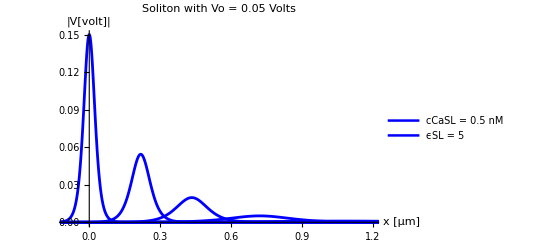

```mathematica
(*Print["Intracellular conditions at 0.05 and 0.15 molar concentration"]*)

solSP2=Plot[ {Abs[Wx[x*10^-6,0]*gamma*nuZe^(1/2)/24],
Abs[Wx[x*10^-6,tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM/10]*gamma*nuZe^(1/2)/24],Abs[Wx[x*10^-6,tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM/5]*gamma*nuZe^(1/2)/24],Abs[Wx[x*10^-6,tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM/3]*gamma*nuZe^(1/2)/24],
Abs[Wx[x*10^-6,tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM/2]*gamma*nuZe^(1/2)/24],Abs[Wx[x*10^-6,tmaxVoEQ0p05VϵSLEQ78p358cCaEQ50nM/1.5]*gamma*nuZe^(1/2)/24]},
{x,-25*beta*10^6,120*beta*10^6},PlotRange->{{-0.1,1.2},{0,0.15}},PlotLegends->{"cCaSL = 0.5 nM", "ϵSL = 5"},PlotLabel->"Soliton with Vo = 0.05 Volts",Axes->True,AxesLabel->{"x [μm]","|V[volt]|"},AxesStyle->Directive[Black,FontSize-> 18],TicksStyle->Directive[18],PlotStyle->{{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]},{Blue,Thickness[0.0050]}},PlotLegends->Placed[{},{0.87,0.6}],LabelStyle->{18}]
```

```mathematica
solSP2Data=Cases[solSP2,Line[{x__}]->x,∞];
```

{{-0.27,2.23047×10^-8},{-0.26952,2.29939×10^-8},{-0.269039,2.37044×10^-8},{-0.268079,2.51919×10^-8},{-0.267599,2.59703×10^-8},{-0.267118,2.67728×10^-8},{-0.266158,2.84529×10^-8},{-0.265677,2.93321×10^-8},{-0.265197,3.02385×10^-8},{-0.264237,3.2136×10^-8},{-0.262315,3.62959×10^-8},{-0.261835,3.74175×10^-8},{-0.261355,3.85736×10^-8},{-0.260394,4.09943×10^-8},{-0.259914,4.2261×10^-8},{-0.259434,4.35669×10^-8},{-0.258473,4.63009×10^-8},{-0.257993,4.77315×10^-8},{-0.257512,4.92064×10^-8},{-0.256552,5.22943×10^-8},{-0.254631,5.90636×10^-8},{-0.25415,6.08887×10^-8},{-0.25367,6.27701×10^-8},{-0.25271,6.67092×10^-8},{-0.252229,6.87705×10^-8},{-0.251749,7.08955×10^-8},{-0.250788,7.53444×10^-8},{-0.250308,7.76725×10^-8},{-0.249828,8.00726×10^-8},{-0.248867,8.50975×10^-8},{-0.246946,9.6113×10^-8},{-0.246466,9.90829×10^-8},{-0.245986,1.02145×10^-7},{-0.245025,1.08554×10^-7},{-0.244545,1.11909×10^-7},{-0.244064,1.15367×10^-7},{-0.243104,1.22606×10^-7},{-0.242624,1.26395×10^-7},{-0.242143,1.30301×10^-7},{-0.241183,1.38477×10^-7},{-0.239262,1.56403×10^-7},{-0.238741,1.61649×10^-7},{-0.23822,1.67071×10^-7},{-0.237179,1.78466×10^-7},{-0.236658,1.84453×10^-7},{-0.236137,1.90639×10^-7},{-0.235096,2.03643×10^-7},{-0.234575,2.10473×10^-7},{-0.234055,2.17533×10^-7},{-0.233013,2.32371×10^-7},{-0.230931,2.65151×10^-7},{-0.23041,2.74045×10^-7},{-0.229889,2.83237×10^-7},{-0.228848,3.02556×10^-7},{-0.228327,3.12704×10^-7},{-0.227806,3.23193×10^-7},{-0.226765,3.45238×10^-7},{-0.226244,3.56817×10^-7},{-0.225724,3.68786×10^-7},{-0.224682,3.9394×10^-7},{-0.2226,4.49513×10^-7},{-0.222079,4.64591×10^-7},{-0.221558,4.80174×10^-7},{-0.220517,5.12926×10^-7},{-0.219996,5.30131×10^-7},{-0.219475,5.47912×10^-7},{-0.218434,5.85284×10^-7},{-0.217913,6.04916×10^-7},{-0.217393,6.25206×10^-7},{-0.216351,6.6785×10^-7},{-0.214269,7.62064×10^-7},{-0.213748,7.87625×10^-7},{-0.213227,8.14043×10^-7},{-0.212186,8.69568×10^-7},{-0.211665,8.98735×10^-7},{-0.211144,9.2888×10^-7},{-0.210103,9.92238×10^-7},{-0.209582,1.02552×10^-6},{-0.209062,1.05992×10^-6},{-0.20802,1.13221×10^-6},{-0.205938,1.29193×10^-6},{-0.205451,1.33235×10^-6},{-0.204965,1.37403×10^-6},{-0.203993,1.46135×10^-6},{-0.203507,1.50707×10^-6},{-0.20302,1.55421×10^-6},{-0.202048,1.65298×10^-6},{-0.201562,1.70469×10^-6},{-0.201076,1.75802×10^-6},{-0.200103,1.86974×10^-6},{-0.198159,2.11493×10^-6},{-0.197672,2.18109×10^-6},{-0.197186,2.24933×10^-6},{-0.196214,2.39227×10^-6},{-0.195728,2.46711×10^-6},{-0.195241,2.54429×10^-6},{-0.194269,2.70598×10^-6},{-0.193783,2.79063×10^-6},{-0.193297,2.87793×10^-6},{-0.192324,3.06082×10^-6},{-0.19038,3.46219×10^-6},{-0.189893,3.57051×10^-6},{-0.189407,3.68221×10^-6},{-0.188435,3.9162×10^-6},{-0.187949,4.03872×10^-6},{-0.187463,4.16507×10^-6},{-0.18649,4.42974×10^-6},{-0.186004,4.56833×10^-6},{-0.185518,4.71124×10^-6},{-0.184545,5.01063×10^-6},{-0.182601,5.66768×10^-6},{-0.182115,5.84499×10^-6},{-0.181628,6.02785×10^-6},{-0.180656,6.4109×10^-6},{-0.18017,6.61146×10^-6},{-0.179684,6.81829×10^-6},{-0.178711,7.25157×10^-6},{-0.178225,7.47843×10^-6},{-0.177739,7.71238×10^-6},{-0.176767,8.20247×10^-6},{-0.174822,9.27807×10^-6},{-0.174345,9.56254×10^-6},{-0.173869,9.85574×10^-6},{-0.172915,0.0000104694},{-0.172439,0.0000107904},{-0.171962,0.0000111212},{-0.171009,0.0000118136},{-0.170532,0.0000121758},{-0.170055,0.0000125492},{-0.169102,0.0000133305},{-0.167196,0.0000150421},{-0.166719,0.0000155033},{-0.166242,0.0000159786},{-0.165289,0.0000169734},{-0.164812,0.0000174938},{-0.164336,0.0000180302},{-0.163382,0.0000191527},{-0.162906,0.00001974},{-0.162429,0.0000203452},{-0.161476,0.0000216118},{-0.159569,0.0000243867},{-0.159093,0.0000251343},{-0.158616,0.0000259049},{-0.157663,0.0000275177},{-0.157186,0.0000283614},{-0.156709,0.0000292309},{-0.155756,0.0000310507},{-0.155279,0.0000320027},{-0.154803,0.0000329839},{-0.153849,0.0000350373},{-0.151943,0.0000395357},{-0.151466,0.0000407477},{-0.15099,0.0000419969},{-0.150036,0.0000446114},{-0.14956,0.0000459791},{-0.149083,0.0000473887},{-0.14813,0.0000503388},{-0.147653,0.000051882},{-0.147176,0.0000534725},{-0.146223,0.0000568012},{-0.144317,0.0000640932},{-0.143799,0.0000662272},{-0.143282,0.0000684323},{-0.142248,0.0000730651},{-0.141731,0.0000754978},{-0.141214,0.0000780115},{-0.14018,0.0000832926},{-0.139663,0.0000860658},{-0.139146,0.0000889312},{-0.138112,0.0000949513},{-0.136044,0.000108241},{-0.135527,0.000111845},{-0.13501,0.000115568},{-0.133976,0.000123391},{-0.133459,0.000127498},{-0.132942,0.000131743},{-0.131907,0.000140659},{-0.13139,0.000145342},{-0.130873,0.00015018},{-0.129839,0.000160344},{-0.127771,0.000182781},{-0.127254,0.000188864},{-0.126737,0.00019515},{-0.125703,0.000208356},{-0.125186,0.000215289},{-0.124669,0.000222454},{-0.123635,0.000237506},{-0.123118,0.000245409},{-0.122601,0.000253575},{-0.121567,0.000270731},{-0.119498,0.000308598},{-0.118981,0.000318865},{-0.118464,0.000329472},{-0.11743,0.000351757},{-0.116913,0.000363457},{-0.116396,0.000375546},{-0.115362,0.000400943},{-0.114845,0.000414277},{-0.114328,0.000428054},{-0.113294,0.000456996},{-0.111226,0.000520872},{-0.110743,0.000537015},{-0.110261,0.000553656},{-0.109295,0.0005885},{-0.108813,0.000606734},{-0.10833,0.000625532},{-0.107365,0.000664889},{-0.106883,0.000685484},{-0.1064,0.000706716},{-0.105435,0.000751168},{-0.103505,0.000848611},{-0.103022,0.000874881},{-0.10254,0.000901961},{-0.101575,0.000958654},{-0.101092,0.000988319},{-0.10061,0.0010189},{-0.0996447,0.00108292},{-0.0991622,0.00111641},{-0.0986796,0.00115094},{-0.0977145,0.00122322},{-0.0957844,0.00138161},{-0.0953018,0.0014243},{-0.0948193,0.00146831},{-0.0938542,0.00156041},{-0.0933717,0.0016086},{-0.0928891,0.00165826},{-0.0919241,0.00176221},{-0.0914415,0.00181659},{-0.090959,0.00187263},{-0.0899939,0.00198993},{-0.0880638,0.00224686},{-0.0875812,0.00231607},{-0.0870987,0.00238741},{-0.0861336,0.00253667},{-0.0856511,0.00261474},{-0.0851685,0.00269518},{-0.0842034,0.00286351},{-0.0837209,0.00295153},{-0.0832384,0.00304223},{-0.0822733,0.00323199},{-0.0803431,0.0036473},{-0.0798202,0.00376862},{-0.0792972,0.00389392},{-0.0782514,0.00415699},{-0.0777284,0.00429502},{-0.0772055,0.00443756},{-0.0761596,0.00473675},{-0.0756367,0.00489371},{-0.0751137,0.00505577},{-0.0740679,0.00539587},{-0.0719761,0.00614477},{-0.0714532,0.00634735},{-0.0709302,0.00655647},{-0.0698843,0.00699508},{-0.0693614,0.00722499},{-0.0688385,0.00746227},{-0.0677926,0.00795979},{-0.0672696,0.0082205},{-0.0667467,0.00848949},{-0.0657008,0.00905332},{-0.0636091,0.0102916},{-0.0630861,0.0106258},{-0.0625632,0.0109705},{-0.0615173,0.0116922},{-0.0609944,0.01207},{-0.0604714,0.0124594},{-0.0594256,0.0132744},{-0.0589026,0.0137007},{-0.0583797,0.0141399},{-0.0573338,0.0150589},{-0.055242,0.0170682},{-0.0547191,0.0176084},{-0.0541962,0.0181645},{-0.0531503,0.0193262},{-0.0510585,0.0218582},{-0.0505356,0.0225371},{-0.0500127,0.0232351},{-0.0489668,0.0246903},{-0.046875,0.027849},{-0.0463616,0.0286772},{-0.0458482,0.0295271},{-0.0448214,0.0312932},{-0.0427678,0.0351013},{-0.0422544,0.0361127},{-0.041741,0.0371486},{-0.0407142,0.0392947},{-0.0386606,0.0438916},{-0.0381472,0.0451056},{-0.0376338,0.0463457},{-0.036607,0.0489049},{-0.0345534,0.0543406},{-0.0304462,0.0664546},{-0.0299328,0.0680796},{-0.0294194,0.0697277},{-0.0283926,0.07309},{-0.0263389,0.0800568},{-0.0222317,0.094714},{-0.0217183,0.0965868},{-0.0212049,0.0984632},{-0.0201781,0.102219},{-0.0181245,0.109683},{-0.0140173,0.123914},{-0.0135384,0.125468},{-0.0130595,0.126993},{-0.0121017,0.129945},{-0.0116228,0.131369},{-0.0111439,0.132754},{-0.0101861,0.135403},{-0.00970723,0.136662},{-0.00922833,0.137875},{-0.00827054,0.140156},{-0.00779164,0.141219},{-0.00731274,0.142229},{-0.00635495,0.144081},{-0.00587605,0.14492},{-0.00539716,0.145699},{-0.00491826,0.146416},{-0.00443936,0.147072},{-0.00396047,0.147663},{-0.00348157,0.14819},{-0.00300267,0.148651},{-0.00252378,0.149045},{-0.00204488,0.149372},{-0.00156598,0.149631},{-0.00108708,0.149822},{-0.000608188,0.149944},{-0.000129291,0.149997},{0.000349606,0.149982},{0.000828503,0.149897},{0.0013074,0.149743},{0.0017863,0.149521},{0.00226519,0.14923},{0.00274409,0.148872},{0.00322299,0.148447},{0.00370188,0.147956},{0.00418078,0.147399},{0.00465968,0.146778},{0.00513857,0.146094},{0.00561747,0.145348},{0.00609637,0.144541},{0.00705416,0.142751},{0.00753306,0.141771},{0.00801196,0.140736},{0.00896975,0.138511},{0.00944865,0.137323},{0.00992754,0.136089},{0.0108853,0.133486},{0.0128009,0.127803},{0.0132798,0.126295},{0.0137587,0.124757},{0.0147165,0.121597},{0.0166321,0.115003},{0.0171514,0.113167},{0.0176707,0.111314},{0.0187093,0.10757},{0.0207865,0.0999938},{0.0249408,0.0849583},{0.0254601,0.0831246},{0.0259794,0.0813062},{0.027018,0.0777199},{0.0290952,0.0707797},{0.0332496,0.0580097},{0.0337689,0.0565282},{0.0342882,0.0550733},{0.0353268,0.0522439},{0.0374039,0.0469094},{0.0379232,0.0456433},{0.0384425,0.044404},{0.0394811,0.0420055},{0.0415583,0.0375231},{0.0420776,0.0364667},{0.0425969,0.0354353},{0.0436355,0.0334464},{0.0457127,0.0297551},{0.046232,0.0288898},{0.0467513,0.0280467},{0.0477899,0.0264256},{0.0498671,0.0234329},{0.0503518,0.0227802},{0.0508366,0.022144},{0.0518062,0.0209201},{0.0537454,0.0186571},{0.0542302,0.0181279},{0.054715,0.0176127},{0.0556845,0.0166232},{0.0576237,0.0147986},{0.0581085,0.014373},{0.0585933,0.0139589},{0.0595629,0.0131645},{0.061502,0.0117031},{0.0619868,0.0113628},{0.0624716,0.0110319},{0.0634412,0.0103978},{0.0653804,0.00923323},{0.0658652,0.00896239},{0.0663499,0.00869926},{0.0673195,0.00819528},{0.0692587,0.00727101},{0.0697435,0.00705629},{0.0702283,0.00684777},{0.0711979,0.00644861},{0.073137,0.00571738},{0.0736218,0.00554766},{0.0741066,0.00538288},{0.0750762,0.0050676},{0.075561,0.00491684},{0.0760458,0.00477049},{0.0770154,0.00449053},{0.0775001,0.00435668},{0.0779849,0.00422676},{0.0789545,0.00397827},{0.0808937,0.00352374},{0.0813689,0.00342041},{0.0818442,0.00332007},{0.0827947,0.00312806},{0.0846957,0.00277639},{0.085171,0.00269477},{0.0856462,0.00261553},{0.0865967,0.00246392},{0.0884977,0.00218636},{0.088973,0.00212196},{0.0894483,0.00205945},{0.0903988,0.00193986},{0.090874,0.00188268},{0.0913493,0.00182717},{0.0922998,0.00172099},{0.092775,0.00167023},{0.0932503,0.00162095},{0.0942008,0.00152669},{0.0961018,0.00135423},{0.0965771,0.00131423},{0.0970523,0.00127541},{0.0980028,0.00120117},{0.0984781,0.00116567},{0.0989533,0.00113123},{0.0999038,0.00106534},{0.100379,0.00103385},{0.100854,0.00100328},{0.101805,0.000944829},{0.103706,0.00083791},{0.104181,0.000813121},{0.104656,0.000789064},{0.105607,0.00074306},{0.106082,0.00072107},{0.106557,0.000699731},{0.107508,0.000658923},{0.107983,0.000639418},{0.108458,0.00062049},{0.109409,0.000584294},{0.11131,0.000518103},{0.111826,0.000501476},{0.112341,0.000485383},{0.113373,0.000454726},{0.113888,0.00044013},{0.114404,0.000426003},{0.115435,0.000399091},{0.115951,0.000386279},{0.116466,0.000373878},{0.117498,0.000350255},{0.11956,0.000307389},{0.120076,0.000297518},{0.120592,0.000287964},{0.121623,0.000269765},{0.122139,0.000261101},{0.122654,0.000252715},{0.123686,0.000236742},{0.124201,0.000229138},{0.124717,0.000221777},{0.125748,0.000207758},{0.127811,0.000182321},{0.128327,0.000176464},{0.128842,0.000170795},{0.129873,0.000159997},{0.130389,0.000154856},{0.130905,0.000149881},{0.131936,0.000140405},{0.132452,0.000135893},{0.132967,0.000131527},{0.133999,0.000123211},{0.136061,0.000108121},{0.136577,0.000104647},{0.137093,0.000101284},{0.138124,0.0000948796},{0.13864,0.0000918307},{0.139155,0.0000888797},{0.140187,0.0000832591},{0.140702,0.0000805835},{0.141218,0.0000779938},{0.142249,0.0000730614},{0.144312,0.0000641125},{0.144793,0.0000621879},{0.145274,0.000060321},{0.146236,0.0000567536},{0.146717,0.0000550498},{0.147199,0.0000533972},{0.148161,0.0000502392},{0.148642,0.0000487309},{0.149123,0.000047268},{0.150086,0.0000444724},{0.15201,0.0000393675},{0.152491,0.0000381856},{0.152972,0.0000370392},{0.153935,0.0000348485},{0.154416,0.0000338023},{0.154897,0.0000327874},{0.155859,0.0000308482},{0.15634,0.000029922},{0.156822,0.0000290237},{0.157784,0.000027307},{0.159708,0.0000241724},{0.16019,0.0000234466},{0.160671,0.0000227426},{0.161633,0.0000213975},{0.162114,0.000020755},{0.162595,0.0000201319},{0.163558,0.0000189411},{0.164039,0.0000183724},{0.16452,0.0000178208},{0.165482,0.0000167668},{0.167407,0.000014842},{0.167888,0.0000143963},{0.168369,0.0000139641},{0.169331,0.0000131381},{0.169813,0.0000127437},{0.170294,0.000012361},{0.171256,0.0000116299},{0.171737,0.0000112807},{0.172218,0.000010942},{0.173181,0.0000102948},{0.175105,9.11295×10^-6},{0.175627,8.81674×10^-6},{0.176148,8.53015×10^-6},{0.177191,7.98461×10^-6},{0.177713,7.72507×10^-6},{0.178235,7.47397×10^-6},{0.179278,6.99598×10^-6},{0.179799,6.76857×10^-6},{0.180321,6.54855×10^-6},{0.181364,6.12975×10^-6},{0.18345,5.37077×10^-6},{0.183972,5.19619×10^-6},{0.184493,5.02729×10^-6},{0.185536,4.70577×10^-6},{0.186058,4.55281×10^-6},{0.186579,4.40481×10^-6},{0.187622,4.12311×10^-6},{0.188144,3.98908×10^-6},{0.188665,3.85941×10^-6},{0.189709,3.61259×10^-6},{0.191795,3.16528×10^-6},{0.192316,3.06239×10^-6},{0.192838,2.96284×10^-6},{0.193881,2.77336×10^-6},{0.194402,2.68321×10^-6},{0.194924,2.59599×10^-6},{0.195967,2.42996×10^-6},{0.196489,2.35097×10^-6},{0.19701,2.27455×10^-6},{0.198053,2.12908×10^-6},{0.20014,1.86546×10^-6},{0.200661,1.80482×10^-6},{0.201183,1.74615×10^-6},{0.202226,1.63448×10^-6},{0.202747,1.58135×10^-6},{0.203269,1.52995×10^-6},{0.204312,1.4321×10^-6},{0.204833,1.38555×10^-6},{0.205355,1.34051×10^-6},{0.206398,1.25478×10^-6},{0.208484,1.09941×10^-6},{0.208996,1.06431×10^-6},{0.209508,1.03034×10^-6},{0.210532,9.65611×10^-7},{0.211044,9.34787×10^-7},{0.211556,9.04948×10^-7},{0.21258,8.48096×10^-7},{0.213092,8.21024×10^-7},{0.213604,7.94816×10^-7},{0.214628,7.44883×10^-7},{0.216676,6.54231×10^-7},{0.217188,6.33347×10^-7},{0.2177,6.1313×10^-7},{0.218724,5.74611×10^-7},{0.219237,5.56268×10^-7},{0.219749,5.38512×10^-7},{0.220773,5.04681×10^-7},{0.221285,4.88571×10^-7},{0.221797,4.72975×10^-7},{0.222821,4.43261×10^-7},{0.224869,3.89316×10^-7},{0.225381,3.76889×10^-7},{0.225893,3.64858×10^-7},{0.226917,3.41936×10^-7},{0.227429,3.31021×10^-7},{0.227941,3.20455×10^-7},{0.228965,3.00323×10^-7},{0.229477,2.90736×10^-7},{0.229989,2.81455×10^-7},{0.231013,2.63773×10^-7},{0.233061,2.31672×10^-7},{0.233573,2.24277×10^-7},{0.234085,2.17118×10^-7},{0.235109,2.03477×10^-7},{0.235621,1.96982×10^-7},{0.236133,1.90694×10^-7},{0.237157,1.78714×10^-7},{0.237669,1.73009×10^-7},{0.238181,1.67487×10^-7},{0.239205,1.56965×10^-7},{0.241253,1.37862×10^-7},{0.24173,1.33753×10^-7},{0.242208,1.29767×10^-7},{0.243163,1.22148×10^-7},{0.24364,1.18507×10^-7},{0.244118,1.14976×10^-7},{0.245073,1.08225×10^-7},{0.245551,1.04999×10^-7},{0.246028,1.0187×10^-7},{0.246983,9.58886×10^-8},{0.248893,8.49587×10^-8},{0.249371,8.24267×10^-8},{0.249848,7.99702×10^-8},{0.250803,7.52746×10^-8},{0.251281,7.30313×10^-8},{0.251758,7.08547×10^-8},{0.252713,6.66944×10^-8},{0.253191,6.47067×10^-8},{0.253668,6.27783×10^-8},{0.254623,5.90922×10^-8},{0.256533,5.23565×10^-8},{0.257011,5.07962×10^-8},{0.257488,4.92823×10^-8},{0.258443,4.63886×10^-8},{0.258921,4.50061×10^-8},{0.259398,4.36649×10^-8},{0.260353,4.1101×10^-8},{0.260831,3.98761×10^-8},{0.261308,3.86877×10^-8},{0.262263,3.64161×10^-8},{0.264173,3.22652×10^-8},{0.264651,3.13036×10^-8},{0.265128,3.03707×10^-8},{0.266083,2.85874×10^-8},{0.266561,2.77354×10^-8},{0.267038,2.69088×10^-8},{0.267993,2.53288×10^-8},{0.268471,2.4574×10^-8},{0.268948,2.38416×10^-8},{0.269903,2.24417×10^-8},{0.271813,1.98837×10^-8},{0.272331,1.92418×10^-8},{0.272849,1.86206×10^-8},{0.273885,1.74378×10^-8},{0.274403,1.68748×10^-8},{0.274921,1.63301×10^-8},{0.275957,1.52927×10^-8},{0.276474,1.4799×10^-8},{0.276992,1.43213×10^-8},{0.278028,1.34115×10^-8},{0.2801,1.17618×10^-8},{0.280618,1.13821×10^-8},{0.281136,1.10146×10^-8},{0.282171,1.03149×10^-8},{0.282689,9.98195×10^-9},{0.283207,9.65971×10^-9},{0.284243,9.04609×10^-9},{0.284761,8.75406×10^-9},{0.285279,8.47145×10^-9},{0.286315,7.93332×10^-9},{0.288386,6.95743×10^-9},{0.288904,6.73283×10^-9},{0.289422,6.51547×10^-9},{0.290458,6.10159×10^-9},{0.290976,5.90461×10^-9},{0.291494,5.71399×10^-9},{0.292529,5.35102×10^-9},{0.293047,5.17828×10^-9},{0.293565,5.01111×10^-9},{0.294601,4.69279×10^-9},{0.296673,4.11552×10^-9},{0.297191,3.98266×10^-9},{0.297709,3.85409×10^-9},{0.298744,3.60927×10^-9},{0.299262,3.49275×10^-9},{0.29978,3.37999×10^-9},{0.300816,3.16528×10^-9},{0.301334,3.0631×10^-9},{0.301852,2.96422×10^-9},{0.302888,2.77592×10^-9},{0.304959,2.43445×10^-9},{0.305443,2.36101×10^-9},{0.305926,2.2898×10^-9},{0.306893,2.15374×10^-9},{0.307376,2.08877×10^-9},{0.30786,2.02576×10^-9},{0.308826,1.90539×10^-9},{0.30931,1.84792×10^-9},{0.309793,1.79218×10^-9},{0.31076,1.68569×10^-9},{0.312694,1.49131×10^-9},{0.313177,1.44633×10^-9},{0.31366,1.4027×10^-9},{0.314627,1.31935×10^-9},{0.315111,1.27955×10^-9},{0.315594,1.24096×10^-9},{0.316561,1.16722×10^-9},{0.317044,1.13201×10^-9},{0.317528,1.09786×10^-9},{0.318494,1.03263×10^-9},{0.320428,9.13559×10^-10},{0.320911,8.86002×10^-10},{0.321395,8.59276×10^-10},{0.322362,8.08218×10^-10},{0.322845,7.83838×10^-10},{0.323328,7.60194×10^-10},{0.324295,7.15024×10^-10},{0.324779,6.93455×10^-10},{0.325262,6.72538×10^-10},{0.326229,6.32576×10^-10},{0.328162,5.59635×10^-10},{0.328646,5.42753×10^-10},{0.329129,5.26381×10^-10},{0.330096,4.95104×10^-10},{0.330579,4.80169×10^-10},{0.331063,4.65685×10^-10},{0.33203,4.38014×10^-10},{0.332513,4.24802×10^-10},{0.332996,4.11988×10^-10},{0.333963,3.87508×10^-10},{0.335897,3.42825×10^-10},{0.336421,3.31634×10^-10},{0.336944,3.20808×10^-10},{0.337992,3.00205×10^-10},{0.338516,2.90405×10^-10},{0.33904,2.80925×10^-10},{0.340087,2.62883×10^-10},{0.340611,2.54302×10^-10},{0.341135,2.46×10^-10},{0.342182,2.30201×10^-10},{0.344278,2.01583×10^-10},{0.344801,1.95002×10^-10},{0.345325,1.88637×10^-10},{0.346373,1.76522×10^-10},{0.346897,1.70759×10^-10},{0.34742,1.65185×10^-10},{0.348468,1.54577×10^-10},{0.348992,1.49531×10^-10},{0.349516,1.44649×10^-10},{0.350563,1.3536×10^-10},{0.352658,1.18532×10^-10},{0.353182,1.14662×10^-10},{0.353706,1.10919×10^-10},{0.354754,1.03796×10^-10},{0.355277,1.00407×10^-10},{0.355801,9.71297×10^-11},{0.356849,9.08918×10^-11},{0.357373,8.79247×10^-11},{0.357896,8.50545×10^-11},{0.358944,7.95921×10^-11},{0.361039,6.96971×10^-11},{0.361563,6.74219×10^-11},{0.362087,6.5221×10^-11},{0.363134,6.10324×10^-11},{0.363658,5.904×10^-11},{0.364182,5.71127×10^-11},{0.36523,5.34448×10^-11},{0.365753,5.17001×10^-11},{0.366277,5.00124×10^-11},{0.367325,4.68005×10^-11},{0.36942,4.09823×10^-11},{0.369934,3.96684×10^-11},{0.370448,3.83966×10^-11},{0.371477,3.59742×10^-11},{0.371991,3.48209×10^-11},{0.372505,3.37045×10^-11},{0.373534,3.15781×10^-11},{0.374048,3.05657×10^-11},{0.374563,2.95858×10^-11},{0.375591,2.77192×10^-11},{0.377648,2.43319×10^-11},{0.378162,2.35518×10^-11},{0.378677,2.27968×10^-11},{0.379705,2.13585×10^-11},{0.380219,2.06738×10^-11},{0.380734,2.0011×10^-11},{0.381762,1.87485×10^-11},{0.382276,1.81474×10^-11},{0.382791,1.75656×10^-11},{0.383819,1.64574×10^-11},{0.385876,1.44463×10^-11},{0.386391,1.39831×10^-11},{0.386905,1.35348×10^-11},{0.387933,1.26809×10^-11},{0.388448,1.22744×10^-11},{0.388962,1.18809×10^-11},{0.38999,1.11313×10^-11},{0.390505,1.07744×10^-11},{0.391019,1.0429×10^-11},{0.392047,9.77103×10^-12},{0.394104,8.577×10^-12},{0.394619,8.30202×10^-12},{0.395133,8.03587×10^-12},{0.396162,7.52888×10^-12},{0.396676,7.28751×10^-12},{0.39719,7.05387×10^-12},{0.398219,6.60884×10^-12},{0.398733,6.39696×10^-12},{0.399247,6.19188×10^-12},{0.400276,5.80123×10^-12},{0.402333,5.09231×10^-12},{0.402812,4.93984×10^-12},{0.403292,4.79194×10^-12},{0.404252,4.50929×10^-12},{0.404731,4.37428×10^-12},{0.405211,4.24331×10^-12},{0.406171,3.99301×10^-12},{0.40665,3.87346×10^-12},{0.40713,3.75749×10^-12},{0.40809,3.53585×10^-12},{0.410009,3.13103×10^-12},{0.410489,3.03728×10^-12},{0.410968,2.94634×10^-12},{0.411928,2.77255×10^-12},{0.412408,2.68954×10^-12},{0.412887,2.60901×10^-12},{0.413847,2.45512×10^-12},{0.414327,2.38161×10^-12},{0.414806,2.3103×10^-12},{0.415766,2.17403×10^-12},{0.417685,1.92512×10^-12},{0.418165,1.86748×10^-12},{0.418644,1.81157×10^-12},{0.419604,1.70471×10^-12},{0.420084,1.65367×10^-12},{0.420563,1.60416×10^-12},{0.421523,1.50954×10^-12},{0.422003,1.46434×10^-12},{0.422482,1.4205×10^-12},{0.423442,1.33671×10^-12},{0.425361,1.18367×10^-12},{0.425841,1.14823×10^-12},{0.426321,1.11385×10^-12},{0.42728,1.04815×10^-12},{0.42776,1.01677×10^-12},{0.42824,9.86324×10^-13},{0.429199,9.28146×10^-13},{0.429679,9.00356×10^-13},{0.430159,8.73399×10^-13},{0.431118,8.21881×10^-13},{0.433037,7.27783×10^-13},{0.433557,7.04188×10^-13},{0.434077,6.81358×10^-13},{0.435118,6.37894×10^-13},{0.435638,6.17213×10^-13},{0.436158,5.97202×10^-13},{0.437198,5.59106×10^-13},{0.437719,5.4098×10^-13},{0.438239,5.23441×10^-13},{0.439279,4.9005×10^-13},{0.44136,4.29523×10^-13},{0.44188,4.15598×10^-13},{0.4424,4.02124×10^-13},{0.44344,3.76472×10^-13},{0.44396,3.64267×10^-13},{0.444481,3.52457×10^-13},{0.445521,3.29974×10^-13},{0.446041,3.19276×10^-13},{0.446561,3.08924×10^-13},{0.447601,2.89218×10^-13},{0.449682,2.53496×10^-13},{0.450202,2.45278×10^-13},{0.450722,2.37326×10^-13},{0.451763,2.22187×10^-13},{0.452283,2.14983×10^-13},{0.452803,2.08013×10^-13},{0.453843,1.94744×10^-13},{0.454364,1.8843×10^-13},{0.454884,1.82321×10^-13},{0.455924,1.70691×10^-13},{0.458005,1.49608×10^-13},{0.458525,1.44758×10^-13},{0.459045,1.40065×10^-13},{0.460085,1.3113×10^-13},{0.460605,1.26879×10^-13},{0.461126,1.22765×10^-13},{0.462166,1.14934×10^-13},{0.462686,1.11208×10^-13},{0.463206,1.07602×10^-13},{0.464246,1.00738×10^-13},{0.466327,8.8296×10^-14},{0.466813,8.56204×10^-14},{0.467298,8.30258×10^-14},{0.46827,7.80702×10^-14},{0.468755,7.57044×10^-14},{0.469241,7.34103×10^-14},{0.470212,6.90286×10^-14},{0.470698,6.69369×10^-14},{0.471184,6.49085×10^-14},{0.472155,6.10342×10^-14},{0.474098,5.39657×10^-14},{0.474583,5.23304×10^-14},{0.475069,5.07446×10^-14},{0.47604,4.77158×10^-14},{0.476526,4.62698×10^-14},{0.477011,4.48677×10^-14},{0.477983,4.21897×10^-14},{0.478468,4.09112×10^-14},{0.478954,3.96714×10^-14},{0.479925,3.73035×10^-14},{0.481868,3.29833×10^-14},{0.482354,3.19838×10^-14},{0.482839,3.10146×10^-14},{0.483811,2.91634×10^-14},{0.484296,2.82797×10^-14},{0.484782,2.74227×10^-14},{0.485753,2.57859×10^-14},{0.486239,2.50045×10^-14},{0.486724,2.42468×10^-14},{0.487696,2.27996×10^-14},{0.489638,2.01591×10^-14},{0.490124,1.95482×10^-14},{0.49061,1.89558×10^-14},{0.491581,1.78244×10^-14},{0.492067,1.72843×10^-14},{0.492552,1.67605×10^-14},{0.493524,1.57601×10^-14},{0.494009,1.52825×10^-14},{0.494495,1.48194×10^-14},{0.495466,1.39349×10^-14},{0.497409,1.2321×10^-14},{0.498361,1.15996×10^-14},{0.499313,1.09205×10^-14},{0.500265,1.02811×10^-14},{0.501218,9.67911×10^-15},{0.50217,9.11239×10^-15},{0.503122,8.57886×10^-15},{0.505027,7.60367×10^-15},{0.505979,7.15847×10^-15},{0.506931,6.73934×10^-15},{0.507883,6.34474×10^-15},{0.508836,5.97326×10^-15},{0.509788,5.62352×10^-15},{0.51074,5.29426×10^-15},{0.512644,4.69244×10^-15},{0.513597,4.4177×10^-15},{0.514549,4.15904×10^-15},{0.515501,3.91552×10^-15},{0.516453,3.68627×10^-15},{0.518358,3.26724×10^-15},{0.520262,2.89584×10^-15},{0.522167,2.56666×10^-15},{0.524071,2.2749×10^-15},{0.525976,2.01631×10^-15},{0.52788,1.78711×10^-15},{0.529946,1.56782×10^-15},{0.532012,1.37545×10^-15},{0.534078,1.20668×10^-15},{0.536144,1.05862×10^-15},{0.53821,9.28722×10^-16},{0.540276,8.14766×10^-16},{0.540793,7.88533×10^-16},{0.541309,7.63144×10^-16},{0.542342,7.14793×10^-16},{0.544408,6.27086×10^-16},{0.548541,4.82638×10^-16},{0.552673,3.71463×10^-16},{0.553189,3.59503×10^-16},{0.553706,3.47928×10^-16},{0.554739,3.25884×10^-16},{0.556805,2.85897×10^-16},{0.560937,2.20041×10^-16},{0.561419,2.13423×10^-16},{0.561901,2.07003×10^-16},{0.562865,1.94738×10^-16},{0.564793,1.72343×10^-16},{0.568649,1.34985×10^-16},{0.576361,8.28067×10^-17},{0.591785,3.11621×10^-17},{0.62522,3.74628×10^-18},{0.658043,4.68134×10^-19},{0.688659,6.72834×10^-20},{0.72186,8.20913×10^-21},{0.752852,1.152×10^-21},{0.783234,1.68038×10^-22},{0.816202,2.08071×10^-23},{0.846962,2.96336×10^-24},{0.880307,3.58269×10^-25},{0.911443,4.98197×10^-26},{0.94197,7.20094×10^-27},{0.975082,8.83546×10^-28},{1.00599,1.24691×10^-28},{1.03947,1.49381×10^-29},{1.07235,1.86016×10^-30},{1.10302,2.66425×10^-31},{1.13628,3.23929×10^-32},{1.16733,4.52993×10^-33},{1.19776,6.58462×10^-34},{1.23079,8.12495×10^-35},{1.2616,1.15313×10^-35},{1.26214,1.11452×10^-35},{1.26268,1.07721×10^-35},{1.26375,1.00628×10^-35},{1.2659,8.78131×10^-36},{1.2702,6.68712×10^-36},{1.2788,3.87793×10^-36},{1.27934,3.74809×10^-36},{1.27988,3.6226×10^-36},{1.28095,3.38408×10^-36},{1.2831,2.95311×10^-36},{1.2874,2.24885×10^-36},{1.28794,2.17356×10^-36},{1.28848,2.10078×10^-36},{1.28955,1.96246×10^-36},{1.2917,1.71254×10^-36},{1.29224,1.6552×10^-36},{1.29278,1.59978×10^-36},{1.29385,1.49445×10^-36},{1.29439,1.44441×10^-36},{1.29493,1.39605×10^-36},{1.29546,1.34931×10^-36},{1.296,1.30413×10^-36},{-0.27,1.79745×10^-9},{-0.26952,1.83067×10^-9},{-0.269039,1.86451×10^-9},{-0.268079,1.93408×10^-9},{-0.266158,2.08109×10^-9},{-0.265677,2.11956×10^-9},{-0.265197,2.15874×10^-9},{-0.264237,2.23928×10^-9},{-0.262315,2.4095×10^-9},{-0.261835,2.45403×10^-9},{-0.261355,2.4994×10^-9},{-0.260394,2.59265×10^-9},{-0.258473,2.78973×10^-9},{-0.254631,3.22996×10^-9},{-0.25415,3.28966×10^-9},{-0.25367,3.35047×10^-9},{-0.25271,3.47547×10^-9},{-0.250788,3.73966×10^-9},{-0.250308,3.80878×10^-9},{-0.249828,3.87919×10^-9},{-0.248867,4.02392×10^-9},{-0.246946,4.32979×10^-9},{-0.246466,4.40982×10^-9},{-0.245986,4.49134×10^-9},{-0.245025,4.65891×10^-9},{-0.243104,5.01305×10^-9},{-0.239262,5.80413×10^-9},{-0.238741,5.92053×10^-9},{-0.23822,6.03927×10^-9},{-0.237179,6.28393×10^-9},{-0.235096,6.80338×10^-9},{-0.234575,6.93982×10^-9},{-0.234055,7.079×10^-9},{-0.233013,7.36578×10^-9},{-0.230931,7.97467×10^-9},{-0.23041,8.1346×10^-9},{-0.229889,8.29774×10^-9},{-0.228848,8.63389×10^-9},{-0.226765,9.34761×10^-9},{-0.2226,1.09569×10^-8},{-0.222079,1.11767×10^-8},{-0.221558,1.14008×10^-8},{-0.220517,1.18627×10^-8},{-0.218434,1.28433×10^-8},{-0.217913,1.31009×10^-8},{-0.217393,1.33636×10^-8},{-0.216351,1.3905×10^-8},{-0.214269,1.50544×10^-8},{-0.213748,1.53563×10^-8},{-0.213227,1.56643×10^-8},{-0.212186,1.62989×10^-8},{-0.210103,1.76462×10^-8},{-0.205938,2.06842×10^-8},{-0.205451,2.10713×10^-8},{-0.204965,2.14656×10^-8},{-0.203993,2.22765×10^-8},{-0.202048,2.39914×10^-8},{-0.201562,2.44404×10^-8},{-0.201076,2.48977×10^-8},{-0.200103,2.58383×10^-8},{-0.198159,2.78273×10^-8},{-0.197672,2.83481×10^-8},{-0.197186,2.88786×10^-8},{-0.196214,2.99695×10^-8},{-0.194269,3.22766×10^-8},{-0.19038,3.74372×10^-8},{-0.189893,3.81378×10^-8},{-0.189407,3.88515×10^-8},{-0.188435,4.03192×10^-8},{-0.18649,4.3423×10^-8},{-0.186004,4.42356×10^-8},{-0.185518,4.50634×10^-8},{-0.184545,4.67657×10^-8},{-0.182601,5.03658×10^-8},{-0.182115,5.13083×10^-8},{-0.181628,5.22685×10^-8},{-0.180656,5.4243×10^-8},{-0.178711,5.84187×10^-8},{-0.174822,6.77592×10^-8},{-0.174345,6.90021×10^-8},{-0.173869,7.02678×10^-8},{-0.172915,7.28692×10^-8},{-0.171009,7.83647×10^-8},{-0.170532,7.98021×10^-8},{-0.170055,8.12659×10^-8},{-0.169102,8.42746×10^-8},{-0.167196,9.06302×10^-8},{-0.166719,9.22926×10^-8},{-0.166242,9.39855×10^-8},{-0.165289,9.74651×10^-8},{-0.163382,1.04815×10^-7},{-0.159569,1.21221×10^-7},{-0.159093,1.23445×10^-7},{-0.158616,1.25709×10^-7},{-0.157663,1.30363×10^-7},{-0.155756,1.40194×10^-7},{-0.155279,1.42766×10^-7},{-0.154803,1.45385×10^-7},{-0.153849,1.50767×10^-7},{-0.151943,1.62137×10^-7},{-0.151466,1.65111×10^-7},{-0.15099,1.6814×10^-7},{-0.150036,1.74365×10^-7},{-0.14813,1.87515×10^-7},{-0.144317,2.16864×10^-7},{-0.143799,2.21182×10^-7},{-0.143282,2.25587×10^-7},{-0.142248,2.3466×10^-7},{-0.14018,2.53917×10^-7},{-0.139663,2.58974×10^-7},{-0.139146,2.64131×10^-7},{-0.138112,2.74755×10^-7},{-0.136044,2.97302×10^-7},{-0.135527,3.03222×10^-7},{-0.13501,3.0926×10^-7},{-0.133976,3.21699×10^-7},{-0.131907,3.48099×10^-7},{-0.127771,4.07575×10^-7},{-0.127254,4.15691×10^-7},{-0.126737,4.23968×10^-7},{-0.125703,4.41021×10^-7},{-0.123635,4.77213×10^-7},{-0.123118,4.86715×10^-7},{-0.122601,4.96407×10^-7},{-0.121567,5.16374×10^-7},{-0.119498,5.58749×10^-7},{-0.118981,5.69875×10^-7},{-0.118464,5.81223×10^-7},{-0.11743,6.04602×10^-7},{-0.115362,6.54217×10^-7},{-0.111226,7.65996×10^-7},{-0.110743,7.80222×10^-7},{-0.110261,7.94712×10^-7},{-0.109295,8.24504×10^-7},{-0.107365,8.87481×10^-7},{-0.106883,9.03964×10^-7},{-0.1064,9.20752×10^-7},{-0.105435,9.55269×10^-7},{-0.103505,1.02823×10^-6},{-0.103022,1.04733×10^-6},{-0.10254,1.06678×10^-6},{-0.101575,1.10677×10^-6},{-0.0996447,1.19131×10^-6},{-0.0957844,1.38025×10^-6},{-0.0953018,1.40588×10^-6},{-0.0948193,1.43199×10^-6},{-0.0938542,1.48568×10^-6},{-0.0919241,1.59915×10^-6},{-0.0914415,1.62885×10^-6},{-0.090959,1.6591×10^-6},{-0.0899939,1.7213×10^-6},{-0.0880638,1.85277×10^-6},{-0.0875812,1.88718×10^-6},{-0.0870987,1.92223×10^-6},{-0.0861336,1.99429×10^-6},{-0.0842034,2.14662×10^-6},{-0.0803431,2.48706×10^-6},{-0.0798202,2.53716×10^-6},{-0.0792972,2.58826×10^-6},{-0.0782514,2.69358×10^-6},{-0.0761596,2.91723×10^-6},{-0.0756367,2.97599×10^-6},{-0.0751137,3.03593×10^-6},{-0.0740679,3.15946×10^-6},{-0.0719761,3.42181×10^-6},{-0.0714532,3.49073×10^-6},{-0.0709302,3.56104×10^-6},{-0.0698843,3.70593×10^-6},{-0.0677926,4.01365×10^-6},{-0.0636091,4.70785×10^-6},{-0.0630861,4.80267×10^-6},{-0.0625632,4.8994×10^-6},{-0.0615173,5.09875×10^-6},{-0.0594256,5.52211×10^-6},{-0.0589026,5.63334×10^-6},{-0.0583797,5.7468×10^-6},{-0.0573338,5.98062×10^-6},{-0.055242,6.4772×10^-6},{-0.0547191,6.60766×10^-6},{-0.0541962,6.74075×10^-6},{-0.0531503,7.01501×10^-6},{-0.0510585,7.59747×10^-6},{-0.046875,8.91148×10^-6},{-0.0463616,9.08766×10^-6},{-0.0458482,9.26732×10^-6},{-0.0448214,9.63737×10^-6},{-0.0427678,0.0000104224},{-0.0422544,0.0000106284},{-0.041741,0.0000108385},{-0.0407142,0.0000112713},{-0.0386606,0.0000121894},{-0.0381472,0.0000124304},{-0.0376338,0.0000126761},{-0.036607,0.0000131822},{-0.0345534,0.0000142559},{-0.0304462,0.0000166728},{-0.0299328,0.0000170024},{-0.0294194,0.0000173385},{-0.0283926,0.0000180308},{-0.0263389,0.0000194994},{-0.0258255,0.0000198848},{-0.0253121,0.0000202779},{-0.0242853,0.0000210875},{-0.0222317,0.000022805},{-0.0217183,0.0000232558},{-0.0212049,0.0000237155},{-0.0201781,0.0000246623},{-0.0181245,0.0000266708},{-0.0140173,0.0000311918},{-0.0135384,0.0000317665},{-0.0130595,0.0000323518},{-0.0121017,0.000033555},{-0.0101861,0.0000360971},{-0.00970723,0.0000367621},{-0.00922833,0.0000374394},{-0.00827054,0.0000388317},{-0.00635495,0.0000417734},{-0.00587605,0.000042543},{-0.00539716,0.0000433268},{-0.00443936,0.0000449379},{-0.00252378,0.000048342},{0.0013074,0.0000559429},{0.0017863,0.0000569734},{0.00226519,0.0000580229},{0.00322299,0.0000601802},{0.00513857,0.0000647382},{0.00561747,0.0000659306},{0.00609637,0.000067145},{0.00705416,0.0000696412},{0.00896975,0.0000749154},{0.00944865,0.0000762951},{0.00992754,0.0000777002},{0.0108853,0.0000805886},{0.0128009,0.0000866911},{0.0166321,0.000100316},{0.0171514,0.000102321},{0.0176707,0.000104365},{0.0187093,0.000108577},{0.0207865,0.000117518},{0.0213058,0.000119866},{0.0218251,0.000122261},{0.0228637,0.000127195},{0.0249408,0.000137666},{0.0254601,0.000140416},{0.0259794,0.000143221},{0.027018,0.000148999},{0.0290952,0.000161264},{0.0332496,0.000188899},{0.0337689,0.00019267},{0.0342882,0.000196517},{0.0353268,0.000204442},{0.0374039,0.00022126},{0.0379232,0.000225676},{0.0384425,0.000230181},{0.0394811,0.00023946},{0.0415583,0.000259152},{0.0420776,0.000264323},{0.0425969,0.000269596},{0.0436355,0.00028046},{0.0457127,0.000303515},{0.0498671,0.000355447},{0.0503518,0.000362058},{0.0508366,0.000368791},{0.0518062,0.000382633},{0.0537454,0.000411889},{0.0542302,0.000419545},{0.054715,0.000427343},{0.0556845,0.000443373},{0.0576237,0.000477254},{0.0581085,0.000486119},{0.0585933,0.000495148},{0.0595629,0.000513711},{0.061502,0.000552938},{0.0653804,0.000640553},{0.0658652,0.000652433},{0.0663499,0.000664533},{0.0673195,0.000689404},{0.0692587,0.000741955},{0.0697435,0.000755703},{0.0702283,0.000769704},{0.0711979,0.000798482},{0.073137,0.000859281},{0.0736218,0.000875185},{0.0741066,0.000891381},{0.0750762,0.000924669},{0.0770154,0.000994987},{0.0808937,0.00115189},{0.0813689,0.00117273},{0.0818442,0.00119394},{0.0827947,0.00123751},{0.0846957,0.00132941},{0.085171,0.00135342},{0.0856462,0.00137786},{0.0865967,0.00142804},{0.0884977,0.00153389},{0.088973,0.00156153},{0.0894483,0.00158967},{0.0903988,0.00164746},{0.0922998,0.00176929},{0.0961018,0.00204012},{0.0965771,0.00207671},{0.0970523,0.00211395},{0.0980028,0.00219039},{0.0999038,0.00235147},{0.100379,0.00239352},{0.100854,0.0024363},{0.101805,0.00252412},{0.103706,0.00270911},{0.104181,0.00275739},{0.104656,0.0028065},{0.105607,0.00290728},{0.107508,0.00311951},{0.11131,0.0035899},{0.111826,0.00365875},{0.112341,0.00372887},{0.113373,0.00387302},{0.115435,0.00417754},{0.115951,0.00425719},{0.116466,0.00433829},{0.117498,0.00450494},{0.11956,0.00485675},{0.120076,0.0049487},{0.120592,0.00504231},{0.121623,0.00523458},{0.123686,0.00564012},{0.127811,0.00654144},{0.128327,0.00666312},{0.128842,0.0067869},{0.129873,0.0070409},{0.131936,0.00757547},{0.132452,0.00771482},{0.132967,0.00785653},{0.133999,0.0081471},{0.136061,0.00875781},{0.136577,0.00891683},{0.137093,0.00907844},{0.138124,0.0094096},{0.140187,0.0101045},{0.144312,0.0116314},{0.144793,0.0118219},{0.145274,0.0120151},{0.146236,0.0124097},{0.148161,0.0132319},{0.15201,0.0150133},{0.152491,0.0152491},{0.152972,0.0154879},{0.153935,0.0159744},{0.155859,0.0169837},{0.159708,0.0191481},{0.16019,0.0194324},{0.160671,0.0197196},{0.161633,0.0203033},{0.163558,0.0215065},{0.167407,0.0240524},{0.175105,0.0296407},{0.175627,0.0300392},{0.176148,0.0304397},{0.177191,0.0312463},{0.179278,0.0328791},{0.18345,0.0361929},{0.183972,0.0366089},{0.184493,0.0370246},{0.185536,0.0378551},{0.187622,0.0395063},{0.191795,0.042728},{0.192316,0.0431192},{0.192838,0.0435072},{0.193881,0.0442725},{0.195967,0.0457548},{0.196489,0.046114},{0.19701,0.0464683},{0.198053,0.0471609},{0.20014,0.0484769},{0.200661,0.0487902},{0.201183,0.0490968},{0.202226,0.0496891},{0.202747,0.0499744},{0.203269,0.0502522},{0.204312,0.0507845},{0.204833,0.0510386},{0.205355,0.0512845},{0.206398,0.0517507},{0.20692,0.0519708},{0.207441,0.0521819},{0.208484,0.0525767},{0.208996,0.0527569},{0.209508,0.0529278},{0.21002,0.0530894},{0.210532,0.0532417},{0.211044,0.0533843},{0.211556,0.0535174},{0.212068,0.0536407},{0.21258,0.0537541},{0.213092,0.0538577},{0.213604,0.0539512},{0.214116,0.0540347},{0.214628,0.0541081},{0.21514,0.0541713},{0.215652,0.0542242},{0.216164,0.0542669},{0.216676,0.0542992},{0.217188,0.0543213},{0.2177,0.054333},{0.218212,0.0543343},{0.218724,0.0543253},{0.219237,0.0543059},{0.219749,0.0542762},{0.220261,0.0542362},{0.220773,0.0541859},{0.221285,0.0541253},{0.221797,0.0540546},{0.222309,0.0539737},{0.222821,0.0538828},{0.223333,0.0537818},{0.223845,0.0536709},{0.224869,0.0534195},{0.225381,0.0532793},{0.225893,0.0531296},{0.226917,0.0528018},{0.227429,0.052624},{0.227941,0.0524372},{0.228965,0.0520368},{0.229477,0.0518235},{0.229989,0.0516017},{0.231013,0.0511333},{0.233061,0.0501015},{0.233573,0.0498248},{0.234085,0.049541},{0.235109,0.0489527},{0.237157,0.047699},{0.241253,0.0449283},{0.24173,0.0445861},{0.242208,0.0442405},{0.243163,0.0435398},{0.245073,0.0421046},{0.248893,0.0391354},{0.256533,0.0330637},{0.257011,0.0326875},{0.257488,0.0323123},{0.258443,0.0315656},{0.260353,0.0300889},{0.264173,0.0272213},{0.271813,0.021939},{0.272331,0.0216061},{0.272849,0.0212766},{0.273885,0.0206279},{0.275957,0.0193723},{0.2801,0.0170298},{0.280618,0.0167529},{0.281136,0.0164795},{0.282171,0.0159431},{0.284243,0.0149121},{0.288386,0.013013},{0.288904,0.0127905},{0.289422,0.0125712},{0.290458,0.0121423},{0.292529,0.0113219},{0.293047,0.0111244},{0.293565,0.01093},{0.294601,0.01055},{0.296673,0.00982485},{0.297191,0.00965062},{0.297709,0.00947915},{0.298744,0.00914436},{0.300816,0.00850653},{0.304959,0.0073507},{0.305443,0.00722569},{0.305926,0.00710264},{0.306893,0.00686233},{0.308826,0.00640421},{0.30931,0.00629422},{0.309793,0.006186},{0.31076,0.00597476},{0.312694,0.00557244},{0.313177,0.00547592},{0.31366,0.00538098},{0.314627,0.00519576},{0.316561,0.00484328},{0.320428,0.00420545},{0.320911,0.00413161},{0.321395,0.00405902},{0.322362,0.00391749},{0.324295,0.00364854},{0.324779,0.00358413},{0.325262,0.00352083},{0.326229,0.00339743},{0.328162,0.00316307},{0.328646,0.00310697},{0.329129,0.00305183},{0.330096,0.0029444},{0.33203,0.00274045},{0.335897,0.002373},{0.336421,0.00232708},{0.336944,0.00228204},{0.337992,0.00219449},{0.340087,0.00202915},{0.340611,0.00198976},{0.341135,0.00195112},{0.342182,0.00187604},{0.344278,0.0017343},{0.344801,0.00170054},{0.345325,0.00166743},{0.346373,0.0016031},{0.348468,0.00148169},{0.352658,0.00126543},{0.353182,0.00124069},{0.353706,0.00121643},{0.354754,0.00116931},{0.356849,0.00108041},{0.357373,0.00105925},{0.357896,0.00103851},{0.358944,0.000998212},{0.361039,0.000922211},{0.361563,0.000904125},{0.362087,0.000886391},{0.363134,0.000851951},{0.36523,0.000787004},{0.36942,0.000671496},{0.369934,0.000658535},{0.370448,0.000645822},{0.371477,0.000621124},{0.373534,0.000574511},{0.374048,0.000563411},{0.374563,0.000552526},{0.375591,0.000531378},{0.377648,0.000491469},{0.378162,0.000481967},{0.378677,0.000472648},{0.379705,0.000454544},{0.381762,0.000420383},{0.385876,0.000359545},{0.386391,0.000352585},{0.386905,0.00034576},{0.387933,0.000332502},{0.38999,0.000307486},{0.390505,0.000301532},{0.391019,0.000295692},{0.392047,0.000284348},{0.394104,0.000262947},{0.394619,0.000257853},{0.395133,0.000252857},{0.396162,0.000243153},{0.398219,0.000224846},{0.402333,0.000192255},{0.402812,0.000188776},{0.403292,0.00018536},{0.404252,0.000178711},{0.406171,0.000166119},{0.40665,0.000163112},{0.40713,0.000160159},{0.40809,0.000154413},{0.410009,0.000143531},{0.410489,0.000140932},{0.410968,0.00013838},{0.411928,0.000133414},{0.413847,0.00012401},{0.417685,0.000107142},{0.418165,0.000105202},{0.418644,0.000103296},{0.419604,0.0000995884},{0.421523,0.0000925666},{0.422003,0.0000908899},{0.422482,0.0000892435},{0.423442,0.0000860395},{0.425361,0.0000799724},{0.425841,0.0000785236},{0.426321,0.000077101},{0.42728,0.0000743327},{0.429199,0.0000690906},{0.433037,0.0000596886},{0.433557,0.0000585169},{0.434077,0.0000573682},{0.435118,0.000055138},{0.437198,0.0000509342},{0.437719,0.0000499343},{0.438239,0.000048954},{0.439279,0.0000470507},{0.44136,0.0000434632},{0.44188,0.0000426099},{0.4424,0.0000417733},{0.44344,0.0000401491},{0.445521,0.0000370877},{0.449682,0.0000316471},{0.450202,0.0000310257},{0.450722,0.0000304165},{0.451763,0.0000292338},{0.453843,0.0000270045},{0.454364,0.0000264742},{0.454884,0.0000259544},{0.455924,0.0000249451},{0.458005,0.0000230427},{0.458525,0.0000225903},{0.459045,0.0000221467},{0.460085,0.0000212854},{0.462166,0.0000196621},{0.466327,0.0000167774},{0.466813,0.0000164696},{0.467298,0.0000161674},{0.46827,0.0000155796},{0.470212,0.0000144673},{0.470698,0.0000142019},{0.471184,0.0000139413},{0.472155,0.0000134344},{0.474098,0.0000124753},{0.474583,0.0000122464},{0.475069,0.0000120217},{0.47604,0.0000115846},{0.477983,0.0000107575},{0.481868,9.27623×10^-6},{0.482354,9.10603×10^-6},{0.482839,8.93895×10^-6},{0.483811,8.61393×10^-6},{0.485753,7.99891×10^-6},{0.486239,7.85214×10^-6},{0.486724,7.70807×10^-6},{0.487696,7.4278×10^-6},{0.489638,6.89747×10^-6},{0.490124,6.77091×10^-6},{0.49061,6.64667×10^-6},{0.491581,6.40499×10^-6},{0.493524,5.94768×10^-6},{0.497409,5.12868×10^-6},{0.497885,5.0364×10^-6},{0.498361,4.94579×10^-6},{0.499313,4.76942×10^-6},{0.501218,4.43533×10^-6},{0.501694,4.35553×10^-6},{0.50217,4.27717×10^-6},{0.503122,4.12464×10^-6},{0.505027,3.83572×10^-6},{0.505503,3.7667×10^-6},{0.505979,3.69893×10^-6},{0.506931,3.56703×10^-6},{0.508836,3.31716×10^-6},{0.512644,2.86871×10^-6},{0.513121,2.81709×10^-6},{0.513597,2.76641×10^-6},{0.514549,2.66775×10^-6},{0.516453,2.48088×10^-6},{0.516929,2.43624×10^-6},{0.517406,2.39241×10^-6},{0.518358,2.30709×10^-6},{0.520262,2.14548×10^-6},{0.520738,2.10688×10^-6},{0.521214,2.06897×10^-6},{0.522167,1.99519×10^-6},{0.524071,1.85543×10^-6},{0.52788,1.60459×10^-6},{0.528397,1.57329×10^-6},{0.528913,1.5426×10^-6},{0.529946,1.48302×10^-6},{0.532012,1.37066×10^-6},{0.532529,1.34392×10^-6},{0.533045,1.31771×10^-6},{0.534078,1.26681×10^-6},{0.536144,1.17083×10^-6},{0.536661,1.148×10^-6},{0.537177,1.12561×10^-6},{0.53821,1.08213×10^-6},{0.540276,1.00014×10^-6},{0.544408,8.54332×10^-7},{0.544925,8.37669×10^-7},{0.545442,8.21331×10^-7},{0.546475,7.89605×10^-7},{0.548541,7.29781×10^-7},{0.549057,7.15547×10^-7},{0.549574,7.01591×10^-7},{0.550607,6.7449×10^-7},{0.552673,6.23388×10^-7},{0.553189,6.11229×10^-7},{0.553706,5.99308×10^-7},{0.554739,5.76157×10^-7},{0.556805,5.32505×10^-7},{0.560937,4.54872×10^-7},{0.561419,4.46588×10^-7},{0.561901,4.38454×10^-7},{0.562865,4.22628×10^-7},{0.564793,3.92669×10^-7},{0.565275,3.85517×10^-7},{0.565757,3.78496×10^-7},{0.566721,3.64834×10^-7},{0.568649,3.38972×10^-7},{0.569131,3.32798×10^-7},{0.569613,3.26737×10^-7},{0.570577,3.14943×10^-7},{0.572505,2.92618×10^-7},{0.576361,2.52603×10^-7},{0.576843,2.48002×10^-7},{0.577325,2.43485×10^-7},{0.578289,2.34697×10^-7},{0.580217,2.1806×10^-7},{0.580699,2.14088×10^-7},{0.581181,2.10189×10^-7},{0.582145,2.02602×10^-7},{0.584073,1.8824×10^-7},{0.584555,1.84812×10^-7},{0.585037,1.81446×10^-7},{0.586001,1.74896×10^-7},{0.587929,1.62499×10^-7},{0.591785,1.40277×10^-7},{0.592308,1.3751×10^-7},{0.59283,1.34798×10^-7},{0.593875,1.29533×10^-7},{0.595965,1.19611×10^-7},{0.596487,1.17252×10^-7},{0.59701,1.14939×10^-7},{0.598054,1.10449×10^-7},{0.600144,1.01989×10^-7},{0.600666,9.99778×10^-8},{0.601189,9.80057×10^-8},{0.602234,9.41776×10^-8},{0.604323,8.69641×10^-8},{0.608502,7.41522×10^-8},{0.609025,7.26896×10^-8},{0.609547,7.12558×10^-8},{0.610592,6.84725×10^-8},{0.612682,6.32279×10^-8},{0.613204,6.19807×10^-8},{0.613727,6.07582×10^-8},{0.614771,5.83849×10^-8},{0.616861,5.39129×10^-8},{0.617383,5.28495×10^-8},{0.617906,5.18071×10^-8},{0.618951,4.97835×10^-8},{0.62104,4.59703×10^-8},{0.62522,3.91978×10^-8},{0.625732,3.84386×10^-8},{0.626245,3.76941×10^-8},{0.627271,3.62481×10^-8},{0.629322,3.35204×10^-8},{0.629835,3.28712×10^-8},{0.630348,3.22346×10^-8},{0.631374,3.0998×10^-8},{0.633425,2.86654×10^-8},{0.633938,2.81102×10^-8},{0.634451,2.75657×10^-8},{0.635477,2.65083×10^-8},{0.637528,2.45135×10^-8},{0.641631,2.0963×10^-8},{0.642144,2.0557×10^-8},{0.642657,2.01588×10^-8},{0.643683,1.93855×10^-8},{0.645734,1.79267×10^-8},{0.646247,1.75795×10^-8},{0.64676,1.72391×10^-8},{0.647786,1.65777×10^-8},{0.649837,1.53303×10^-8},{0.65035,1.50333×10^-8},{0.650863,1.47422×10^-8},{0.651889,1.41766×10^-8},{0.65394,1.31098×10^-8},{0.658043,1.1211×10^-8},{0.658522,1.10084×10^-8},{0.659,1.08094×10^-8},{0.659957,1.04221×10^-8},{0.66187,9.68868×10^-9},{0.662349,9.51354×10^-9},{0.662827,9.34157×10^-9},{0.663784,9.00688×10^-9},{0.665697,8.37306×10^-9},{0.666175,8.2217×10^-9},{0.666654,8.07308×10^-9},{0.667611,7.78385×10^-9},{0.669524,7.23609×10^-9},{0.673351,6.25351×10^-9},{0.673829,6.14046×10^-9},{0.674308,6.02946×10^-9},{0.675264,5.81344×10^-9},{0.677178,5.40435×10^-9},{0.677656,5.30665×10^-9},{0.678135,5.21073×10^-9},{0.679091,5.02404×10^-9},{0.681005,4.6705×10^-9},{0.681483,4.58607×10^-9},{0.681961,4.50316×10^-9},{0.682918,4.34183×10^-9},{0.684832,4.03629×10^-9},{0.688659,3.48821×10^-9},{0.689177,3.41988×10^-9},{0.689696,3.35289×10^-9},{0.690734,3.22282×10^-9},{0.692809,2.97762×10^-9},{0.693327,2.91929×10^-9},{0.693846,2.86211×10^-9},{0.694884,2.75108×10^-9},{0.696959,2.54177×10^-9},{0.697478,2.49198×10^-9},{0.697996,2.44317×10^-9},{0.699034,2.34839×10^-9},{0.701109,2.16972×10^-9},{0.705259,1.85212×10^-9},{0.705778,1.81584×10^-9},{0.706297,1.78027×10^-9},{0.707334,1.71121×10^-9},{0.709409,1.58102×10^-9},{0.709928,1.55005×10^-9},{0.710447,1.51969×10^-9},{0.711484,1.46073×10^-9},{0.713559,1.3496×10^-9},{0.714078,1.32316×10^-9},{0.714597,1.29724×10^-9},{0.715634,1.24692×10^-9},{0.717709,1.15205×10^-9},{0.72186,9.83418×10^-10},{0.722344,9.65423×10^-10},{0.722828,9.47759×10^-10},{0.723797,9.13392×10^-10},{0.725734,8.48353×10^-10},{0.726218,8.3283×10^-10},{0.726702,8.17592×10^-10},{0.727671,7.87945×10^-10},{0.729608,7.31839×10^-10},{0.730092,7.18448×10^-10},{0.730576,7.05302×10^-10},{0.731545,6.79727×10^-10},{0.733482,6.31327×10^-10},{0.737356,5.44619×10^-10},{0.73784,5.34654×10^-10},{0.738324,5.24871×10^-10},{0.739293,5.05839×10^-10},{0.74123,4.6982×10^-10},{0.741714,4.61223×10^-10},{0.742198,4.52784×10^-10},{0.743167,4.36366×10^-10},{0.745104,4.05294×10^-10},{0.745588,3.97878×10^-10},{0.746073,3.90598×10^-10},{0.747041,3.76435×10^-10},{0.748978,3.4963×10^-10},{0.752852,3.01611×10^-10},{0.753327,2.962×10^-10},{0.753802,2.90886×10^-10},{0.754751,2.80542×10^-10},{0.75665,2.60945×10^-10},{0.757125,2.56264×10^-10},{0.757599,2.51666×10^-10},{0.758549,2.42717×10^-10},{0.760448,2.25763×10^-10},{0.760922,2.21712×10^-10},{0.761397,2.17735×10^-10},{0.762347,2.09992×10^-10},{0.764246,1.95323×10^-10},{0.768043,1.68988×10^-10},{0.768518,1.65957×10^-10},{0.768993,1.62979×10^-10},{0.769942,1.57184×10^-10},{0.771841,1.46204×10^-10},{0.772316,1.43581×10^-10},{0.772791,1.41005×10^-10},{0.77374,1.35991×10^-10},{0.775639,1.26491×10^-10},{0.776114,1.24222×10^-10},{0.776588,1.21993×10^-10},{0.777538,1.17656×10^-10},{0.779437,1.09437×10^-10},{0.783234,9.46816×10^-11},{0.78375,9.28398×10^-11},{0.784265,9.10339×10^-11},{0.785295,8.75267×10^-11},{0.787355,8.09124×10^-11},{0.787871,7.93385×10^-11},{0.788386,7.77952×10^-11},{0.789416,7.4798×10^-11},{0.791476,6.91457×10^-11},{0.791991,6.78006×10^-11},{0.792507,6.64817×10^-11},{0.793537,6.39204×10^-11},{0.795597,5.90901×10^-11},{0.799718,5.04968×10^-11},{0.800233,4.95146×10^-11},{0.800749,4.85514×10^-11},{0.801779,4.66809×10^-11},{0.803839,4.31533×10^-11},{0.804354,4.23138×10^-11},{0.80487,4.14907×10^-11},{0.8059,3.98923×10^-11},{0.80796,3.68777×10^-11},{0.808475,3.61603×10^-11},{0.808991,3.54569×10^-11},{0.810021,3.40909×10^-11},{0.812081,3.15147×10^-11},{0.816202,2.69316×10^-11},{0.816683,2.64425×10^-11},{0.817163,2.59623×10^-11},{0.818125,2.50278×10^-11},{0.820047,2.32586×10^-11},{0.820528,2.28362×10^-11},{0.821008,2.24215×10^-11},{0.82197,2.16145×10^-11},{0.823892,2.00865×10^-11},{0.824373,1.97218×10^-11},{0.824853,1.93636×10^-11},{0.825815,1.86666×10^-11},{0.827737,1.73471×10^-11},{0.831582,1.49812×10^-11},{0.832063,1.47092×10^-11},{0.832543,1.4442×10^-11},{0.833504,1.39222×10^-11},{0.835427,1.29381×10^-11},{0.835907,1.27031×10^-11},{0.836388,1.24724×10^-11},{0.837349,1.20235×10^-11},{0.839272,1.11735×10^-11},{0.839752,1.09706×10^-11},{0.840233,1.07714×10^-11},{0.841194,1.03837×10^-11},{0.843117,9.64966×10^-12},{0.846962,8.33361×10^-12},{0.847483,8.16967×10^-12},{0.848004,8.00895×10^-12},{0.849046,7.69693×10^-12},{0.85113,7.10889×10^-12},{0.851651,6.96904×10^-12},{0.852172,6.83194×10^-12},{0.853214,6.56578×10^-12},{0.855298,6.06416×10^-12},{0.855819,5.94486×10^-12},{0.85634,5.82791×10^-12},{0.857382,5.60086×10^-12},{0.859466,5.17296×10^-12},{0.863634,4.41274×10^-12},{0.864155,4.32593×10^-12},{0.864676,4.24082×10^-12},{0.865718,4.07561×10^-12},{0.867802,3.76424×10^-12},{0.868323,3.69018×10^-12},{0.868844,3.61759×10^-12},{0.869886,3.47665×10^-12},{0.87197,3.21104×10^-12},{0.872491,3.14787×10^-12},{0.873012,3.08594×10^-12},{0.874055,2.96572×10^-12},{0.876139,2.73914×10^-12},{0.880307,2.33659×10^-12},{0.880793,2.29364×10^-12},{0.88128,2.25148×10^-12},{0.882253,2.16947×10^-12},{0.884199,2.0143×10^-12},{0.884685,1.97727×10^-12},{0.885172,1.94092×10^-12},{0.886145,1.87022×10^-12},{0.888091,1.73646×10^-12},{0.888577,1.70454×10^-12},{0.889064,1.6732×10^-12},{0.890037,1.61226×10^-12},{0.891983,1.49694×10^-12},{0.895875,1.29046×10^-12},{0.896362,1.26674×10^-12},{0.896848,1.24345×10^-12},{0.897821,1.19816×10^-12},{0.899767,1.11246×10^-12},{0.900254,1.09201×10^-12},{0.90074,1.07194×10^-12},{0.901713,1.03289×10^-12},{0.903659,9.59014×10^-13},{0.904146,9.41386×10^-13},{0.904632,9.24081×10^-13},{0.905605,8.90421×10^-13},{0.907551,8.26734×10^-13},{0.911443,7.12699×10^-13},{0.91192,6.99852×10^-13},{0.912397,6.87238×10^-13},{0.913351,6.62686×10^-13},{0.915259,6.16183×10^-13},{0.915736,6.05077×10^-13},{0.916213,5.9417×10^-13},{0.917167,5.72944×10^-13},{0.919075,5.32738×10^-13},{0.919552,5.23136×10^-13},{0.920029,5.13706×10^-13},{0.920983,4.95354×10^-13},{0.922891,4.60594×10^-13},{0.926707,3.98219×10^-13},{0.927184,3.91041×10^-13},{0.927661,3.83993×10^-13},{0.928614,3.70275×10^-13},{0.930522,3.44291×10^-13},{0.930999,3.38085×10^-13},{0.931476,3.31991×10^-13},{0.93243,3.20131×10^-13},{0.934338,2.97666×10^-13},{0.934815,2.92301×10^-13},{0.935292,2.87032×10^-13},{0.936246,2.76778×10^-13},{0.938154,2.57356×10^-13},{0.94197,2.22504×10^-13},{0.942487,2.18157×10^-13},{0.943004,2.13895×10^-13},{0.944039,2.05619×10^-13},{0.946109,1.90016×10^-13},{0.946626,1.86303×10^-13},{0.947143,1.82664×10^-13},{0.948178,1.75596×10^-13},{0.950248,1.62271×10^-13},{0.950765,1.59101×10^-13},{0.951282,1.55992×10^-13},{0.952317,1.49957×10^-13},{0.954387,1.38577×10^-13},{0.958526,1.18343×10^-13},{0.959043,1.16031×10^-13},{0.95956,1.13764×10^-13},{0.960595,1.09363×10^-13},{0.962665,1.01064×10^-13},{0.963182,9.90891×10^-14},{0.963699,9.71532×10^-14},{0.964734,9.33942×10^-14},{0.966804,8.63069×10^-14},{0.967321,8.46208×10^-14},{0.967838,8.29676×10^-14},{0.968873,7.97575×10^-14},{0.970943,7.3705×10^-14},{0.975082,6.29431×10^-14},{0.975564,6.17947×10^-14},{0.976047,6.06672×10^-14},{0.977013,5.84736×10^-14},{0.978945,5.43215×10^-14},{0.979427,5.33303×10^-14},{0.97991,5.23573×10^-14},{0.980876,5.04642×10^-14},{0.982808,4.68807×10^-14},{0.98329,4.60254×10^-14},{0.983773,4.51856×10^-14},{0.984739,4.35518×10^-14},{0.98667,4.04592×10^-14},{0.990533,3.49173×10^-14},{0.991499,3.36547×10^-14},{0.992465,3.24379×10^-14},{0.994396,3.01345×10^-14},{0.995362,2.90449×10^-14},{0.996328,2.79947×10^-14},{0.998259,2.60068×10^-14},{0.999225,2.50664×10^-14},{1.00019,2.41601×10^-14},{1.00212,2.24445×10^-14},{1.00599,1.93701×10^-14},{1.00703,1.86123×10^-14},{1.00808,1.78841×10^-14},{1.01017,1.65121×10^-14},{1.01122,1.58661×10^-14},{1.01226,1.52454×10^-14},{1.01436,1.40758×10^-14},{1.0154,1.35251×10^-14},{1.01645,1.2996×10^-14},{1.01854,1.1999×10^-14},{1.02273,1.02286×10^-14},{1.02378,9.82838×10^-15},{1.02482,9.44386×10^-15},{1.02692,8.71936×10^-15},{1.02901,8.05045×10^-15},{1.0311,7.43285×10^-15},{1.0332,6.86263×10^-15},{1.03529,6.33615×10^-15},{1.03947,5.40127×10^-15},{1.04153,4.99416×10^-15},{1.04358,4.61774×10^-15},{1.04564,4.2697×10^-15},{1.04769,3.94788×10^-15},{1.04975,3.65032×10^-15},{1.0518,3.37519×10^-15},{1.05591,2.88557×10^-15},{1.05797,2.66808×10^-15},{1.06002,2.46698×10^-15},{1.06208,2.28104×10^-15},{1.06413,2.10911×10^-15},{1.06824,1.80316×10^-15},{1.07235,1.54159×10^-15},{1.07619,1.33191×10^-15},{1.08002,1.15075×10^-15},{1.08385,9.94225×10^-16},{1.08769,8.58995×10^-16},{1.08817,8.43439×10^-16},{1.08865,8.28165×10^-16},{1.08961,7.98442×10^-16},{1.09152,7.42158×10^-16},{1.09536,6.41212×10^-16},{1.09584,6.29601×10^-16},{1.09631,6.18199×10^-16},{1.09727,5.96012×10^-16},{1.09919,5.53997×10^-16},{1.10302,4.78645×10^-16},{1.11134,3.48594×10^-16},{1.11965,2.53878×10^-16},{1.12017,2.48897×10^-16},{1.12069,2.44013×10^-16},{1.12173,2.34532×10^-16},{1.12381,2.1666×10^-16},{1.12797,1.84898×10^-16},{1.13628,1.3466×10^-16},{1.13676,1.32191×10^-16},{1.13725,1.29768×10^-16},{1.13822,1.25055×10^-16},{1.14016,1.16135×10^-16},{1.14404,1.00158×10^-16},{1.1518,7.44966×10^-17},{1.16733,4.12131×10^-17},{1.19776,1.29105×10^-17},{1.23079,3.66461×10^-18},{1.2616,1.13158×10^-18},{1.26214,1.10863×10^-18},{1.26268,1.08614×10^-18},{1.26375,1.04251×10^-18},{1.2659,9.60451×10^-19},{1.2702,8.15199×10^-19},{1.2788,5.87273×10^-19},{1.27934,5.75359×10^-19},{1.27988,5.63686×10^-19},{1.28095,5.41046×10^-19},{1.2831,4.98458×10^-19},{1.2874,4.23074×10^-19},{1.28794,4.14491×10^-19},{1.28848,4.06082×10^-19},{1.28955,3.89772×10^-19},{1.2917,3.59091×10^-19},{1.29224,3.51806×10^-19},{1.29278,3.44669×10^-19},{1.29385,3.30826×10^-19},{1.29439,3.24114×10^-19},{1.29493,3.17538×10^-19},{1.29546,3.11096×10^-19},{1.296,3.04785×10^-19},{-0.27,7.4674×10^-9},{-0.26952,7.5502×10^-9},{-0.269039,7.63392×10^-9},{-0.268079,7.80414×10^-9},{-0.266158,8.15608×10^-9},{-0.262315,8.90827×10^-9},{-0.261835,9.00704×10^-9},{-0.261355,9.10691×10^-9},{-0.260394,9.30999×10^-9},{-0.258473,9.72983×10^-9},{-0.254631,1.06272×10^-8},{-0.25415,1.0745×10^-8},{-0.25367,1.08641×10^-8},{-0.25271,1.11064×10^-8},{-0.250788,1.16072×10^-8},{-0.246946,1.26777×10^-8},{-0.246466,1.28183×10^-8},{-0.245986,1.29604×10^-8},{-0.245025,1.32494×10^-8},{-0.243104,1.38469×10^-8},{-0.239262,1.51239×10^-8},{-0.238741,1.53058×10^-8},{-0.23822,1.54899×10^-8},{-0.237179,1.58647×10^-8},{-0.235096,1.66418×10^-8},{-0.230931,1.83119×10^-8},{-0.23041,1.85321×10^-8},{-0.229889,1.8755×10^-8},{-0.228848,1.92088×10^-8},{-0.226765,2.01497×10^-8},{-0.2226,2.21719×10^-8},{-0.222079,2.24385×10^-8},{-0.221558,2.27084×10^-8},{-0.220517,2.32579×10^-8},{-0.218434,2.4397×10^-8},{-0.214269,2.68455×10^-8},{-0.213748,2.71683×10^-8},{-0.213227,2.74951×10^-8},{-0.212186,2.81604×10^-8},{-0.210103,2.95397×10^-8},{-0.205938,3.25043×10^-8},{-0.205451,3.28691×10^-8},{-0.204965,3.32381×10^-8},{-0.203993,3.39885×10^-8},{-0.202048,3.55404×10^-8},{-0.198159,3.88601×10^-8},{-0.197672,3.92963×10^-8},{-0.197186,3.97374×10^-8},{-0.196214,4.06346×10^-8},{-0.194269,4.249×10^-8},{-0.19038,4.64589×10^-8},{-0.189893,4.69804×10^-8},{-0.189407,4.75077×10^-8},{-0.188435,4.85802×10^-8},{-0.18649,5.07985×10^-8},{-0.182601,5.55434×10^-8},{-0.182115,5.61669×10^-8},{-0.181628,5.67974×10^-8},{-0.180656,5.80796×10^-8},{-0.178711,6.07316×10^-8},{-0.174822,6.64044×10^-8},{-0.174345,6.7135×10^-8},{-0.173869,6.78738×10^-8},{-0.172915,6.93757×10^-8},{-0.171009,7.248×10^-8},{-0.167196,7.91114×10^-8},{-0.166719,7.99819×10^-8},{-0.166242,8.0862×10^-8},{-0.165289,8.26513×10^-8},{-0.163382,8.63496×10^-8},{-0.159569,9.42501×10^-8},{-0.159093,9.52871×10^-8},{-0.158616,9.63356×10^-8},{-0.157663,9.84673×10^-8},{-0.155756,1.02873×10^-7},{-0.151943,1.12286×10^-7},{-0.151466,1.13521×10^-7},{-0.15099,1.1477×10^-7},{-0.150036,1.1731×10^-7},{-0.14813,1.22559×10^-7},{-0.144317,1.33772×10^-7},{-0.143799,1.3537×10^-7},{-0.143282,1.36986×10^-7},{-0.142248,1.40278×10^-7},{-0.14018,1.47099×10^-7},{-0.136044,1.61754×10^-7},{-0.135527,1.63685×10^-7},{-0.13501,1.6564×10^-7},{-0.133976,1.6962×10^-7},{-0.131907,1.77868×10^-7},{-0.127771,1.95588×10^-7},{-0.127254,1.97923×10^-7},{-0.126737,2.00287×10^-7},{-0.125703,2.05099×10^-7},{-0.123635,2.15073×10^-7},{-0.119498,2.36499×10^-7},{-0.118981,2.39323×10^-7},{-0.118464,2.42181×10^-7},{-0.11743,2.47999×10^-7},{-0.115362,2.60059×10^-7},{-0.111226,2.85967×10^-7},{-0.110743,2.89153×10^-7},{-0.110261,2.92374×10^-7},{-0.109295,2.98925×10^-7},{-0.107365,3.12469×10^-7},{-0.103505,3.41428×10^-7},{-0.103022,3.45231×10^-7},{-0.10254,3.49077×10^-7},{-0.101575,3.56898×10^-7},{-0.0996447,3.73069×10^-7},{-0.0957844,4.07644×10^-7},{-0.0953018,4.12185×10^-7},{-0.0948193,4.16777×10^-7},{-0.0938542,4.26115×10^-7},{-0.0919241,4.45422×10^-7},{-0.0880638,4.86702×10^-7},{-0.0875812,4.92124×10^-7},{-0.0870987,4.97606×10^-7},{-0.0861336,5.08755×10^-7},{-0.0842034,5.31807×10^-7},{-0.0803431,5.81092×10^-7},{-0.0798202,5.88111×10^-7},{-0.0792972,5.95214×10^-7},{-0.0782514,6.0968×10^-7},{-0.0761596,6.39674×10^-7},{-0.0719761,7.04161×10^-7},{-0.0714532,7.12666×10^-7},{-0.0709302,7.21274×10^-7},{-0.0698843,7.38803×10^-7},{-0.0677926,7.75149×10^-7},{-0.0636091,8.53293×10^-7},{-0.0630861,8.636×10^-7},{-0.0625632,8.7403×10^-7},{-0.0615173,8.95272×10^-7},{-0.0594256,9.39315×10^-7},{-0.055242,1.03401×10^-6},{-0.0547191,1.0465×10^-6},{-0.0541962,1.05914×10^-6},{-0.0531503,1.08488×10^-6},{-0.0510585,1.13825×10^-6},{-0.046875,1.253×10^-6},{-0.0463616,1.26785×10^-6},{-0.0458482,1.28289×10^-6},{-0.0448214,1.31349×10^-6},{-0.0427678,1.3769×10^-6},{-0.0386606,1.51305×10^-6},{-0.0381472,1.53099×10^-6},{-0.0376338,1.54914×10^-6},{-0.036607,1.5861×10^-6},{-0.0345534,1.66267×10^-6},{-0.0304462,1.82708×10^-6},{-0.0299328,1.84874×10^-6},{-0.0294194,1.87066×10^-6},{-0.0283926,1.91528×10^-6},{-0.0263389,2.00775×10^-6},{-0.0222317,2.20628×10^-6},{-0.0217183,2.23243×10^-6},{-0.0212049,2.2589×10^-6},{-0.0201781,2.31278×10^-6},{-0.0181245,2.42444×10^-6},{-0.0140173,2.66417×10^-6},{-0.0135384,2.69362×10^-6},{-0.0130595,2.7234×10^-6},{-0.0121017,2.78394×10^-6},{-0.0101861,2.90911×10^-6},{-0.00635495,3.17656×10^-6},{-0.00587605,3.21168×10^-6},{-0.00539716,3.24718×10^-6},{-0.00443936,3.31938×10^-6},{-0.00252378,3.46861×10^-6},{0.0013074,3.7875×10^-6},{0.0017863,3.82937×10^-6},{0.00226519,3.8717×10^-6},{0.00322299,3.95778×10^-6},{0.00513857,4.13571×10^-6},{0.00896975,4.51592×10^-6},{0.00944865,4.56584×10^-6},{0.00992754,4.61632×10^-6},{0.0108853,4.71894×10^-6},{0.0128009,4.93109×10^-6},{0.0166321,5.38442×10^-6},{0.0171514,5.44899×10^-6},{0.0176707,5.51434×10^-6},{0.0187093,5.64739×10^-6},{0.0207865,5.9232×10^-6},{0.0249408,6.51588×10^-6},{0.0254601,6.59402×10^-6},{0.0259794,6.6731×10^-6},{0.027018,6.8341×10^-6},{0.0290952,7.16786×10^-6},{0.0332496,7.88506×10^-6},{0.0337689,7.97962×10^-6},{0.0342882,8.07531×10^-6},{0.0353268,8.27014×10^-6},{0.0374039,8.67401×10^-6},{0.0415583,9.54188×10^-6},{0.0420776,9.6563×10^-6},{0.0425969,9.77209×10^-6},{0.0436355,0.0000100078},{0.0457127,0.0000104966},{0.0498671,0.0000115467},{0.0503518,0.0000116759},{0.0508366,0.0000118066},{0.0518062,0.0000120723},{0.0537454,0.0000126217},{0.0576237,0.0000137967},{0.0581085,0.0000139511},{0.0585933,0.0000141072},{0.0595629,0.0000144246},{0.061502,0.0000150811},{0.0653804,0.000016485},{0.0658652,0.0000166694},{0.0663499,0.0000168559},{0.0673195,0.0000172352},{0.0692587,0.0000180195},{0.073137,0.0000196968},{0.0736218,0.0000199171},{0.0741066,0.0000201399},{0.0750762,0.0000205931},{0.0770154,0.0000215301},{0.0808937,0.000023534},{0.0813689,0.000023792},{0.0818442,0.0000240529},{0.0827947,0.0000245832},{0.0846957,0.0000256792},{0.0884977,0.0000280199},{0.088973,0.0000283271},{0.0894483,0.0000286376},{0.0903988,0.000029269},{0.0922998,0.0000305737},{0.0961018,0.0000333602},{0.0965771,0.0000337258},{0.0970523,0.0000340955},{0.0980028,0.0000348471},{0.0999038,0.0000364003},{0.103706,0.0000397172},{0.104181,0.0000401525},{0.104656,0.0000405926},{0.105607,0.0000414872},{0.107508,0.000043336},{0.11131,0.0000472842},{0.111826,0.0000478466},{0.112341,0.0000484157},{0.113373,0.0000495743},{0.115435,0.0000519753},{0.11956,0.0000571311},{0.120076,0.0000578105},{0.120592,0.000058498},{0.121623,0.0000598975},{0.123686,0.0000627976},{0.127811,0.0000690251},{0.128327,0.0000698457},{0.128842,0.000070676},{0.129873,0.0000723664},{0.131936,0.000075869},{0.136061,0.00008339},{0.136577,0.000084381},{0.137093,0.0000853838},{0.138124,0.0000874251},{0.140187,0.0000916549},{0.144312,0.000100737},{0.144793,0.000101853},{0.145274,0.000102981},{0.146236,0.000105276},{0.148161,0.000110019},{0.15201,0.000120153},{0.152491,0.000121483},{0.152972,0.000122829},{0.153935,0.000125564},{0.155859,0.000131218},{0.159708,0.000143298},{0.16019,0.000144883},{0.160671,0.000146487},{0.161633,0.000149747},{0.163558,0.000156485},{0.167407,0.000170881},{0.167888,0.000172771},{0.168369,0.000174681},{0.169331,0.000178566},{0.171256,0.000186595},{0.175105,0.000203746},{0.175627,0.000206188},{0.176148,0.000208658},{0.177191,0.000213688},{0.179278,0.000224113},{0.18345,0.000246502},{0.183972,0.000249453},{0.184493,0.000252438},{0.185536,0.000258517},{0.187622,0.000271113},{0.191795,0.000298161},{0.192316,0.000301725},{0.192838,0.000305332},{0.193881,0.000312673},{0.195967,0.000327886},{0.20014,0.000360546},{0.200661,0.000364849},{0.201183,0.000369203},{0.202226,0.000378065},{0.204312,0.000396426},{0.208484,0.000435837},{0.208996,0.000440933},{0.209508,0.000446087},{0.210532,0.000456576},{0.21258,0.000478289},{0.216676,0.000524819},{0.217188,0.00053094},{0.2177,0.000537132},{0.218724,0.000549731},{0.220773,0.000575808},{0.224869,0.000631669},{0.225381,0.000639016},{0.225893,0.000646447},{0.226917,0.000661565},{0.228965,0.000692851},{0.233061,0.00075984},{0.233573,0.000768648},{0.234085,0.000777556},{0.235109,0.000795676},{0.237157,0.000833165},{0.241253,0.000913394},{0.24173,0.000923224},{0.242208,0.000933157},{0.243163,0.000953337},{0.245073,0.00099498},{0.248893,0.00108364},{0.249371,0.00109525},{0.249848,0.00110698},{0.250803,0.00113081},{0.252713,0.00117996},{0.256533,0.00128454},{0.257011,0.00129822},{0.257488,0.00131205},{0.258443,0.00134013},{0.260353,0.00139803},{0.264173,0.00152114},{0.271813,0.00179918},{0.272331,0.00181968},{0.272849,0.00184041},{0.273885,0.00188253},{0.275957,0.00196953},{0.2801,0.00215503},{0.280618,0.00217934},{0.281136,0.00220391},{0.282171,0.00225382},{0.284243,0.00235684},{0.288386,0.00257615},{0.288904,0.00260485},{0.289422,0.00263385},{0.290458,0.00269275},{0.292529,0.00281419},{0.296673,0.00307225},{0.304959,0.00365354},{0.305443,0.0036903},{0.305926,0.00372738},{0.306893,0.00380254},{0.308826,0.00395686},{0.312694,0.00428198},{0.313177,0.00432419},{0.31366,0.00436677},{0.314627,0.004453},{0.316561,0.00462983},{0.320428,0.0050013},{0.320911,0.00504943},{0.321395,0.00509795},{0.322362,0.00519614},{0.324295,0.00539717},{0.328162,0.00581808},{0.335897,0.00673677},{0.336421,0.00680272},{0.336944,0.00686915},{0.337992,0.00700342},{0.340087,0.00727763},{0.344278,0.00784848},{0.352658,0.00907637},{0.36942,0.0118167},{0.369934,0.0119051},{0.370448,0.0119935},{0.371477,0.0121709},{0.373534,0.0125271},{0.377648,0.0132425},{0.385876,0.0146633},{0.386391,0.0147506},{0.386905,0.0148378},{0.387933,0.0150112},{0.38999,0.0153544},{0.394104,0.0160223},{0.402333,0.0172551},{0.402812,0.0173216},{0.403292,0.0173875},{0.404252,0.0175173},{0.406171,0.0177681},{0.40665,0.0178289},{0.40713,0.017889},{0.40809,0.0180067},{0.410009,0.0182324},{0.410489,0.0182867},{0.410968,0.0183401},{0.411928,0.0184443},{0.413847,0.0186417},{0.414327,0.0186887},{0.414806,0.0187347},{0.415766,0.0188239},{0.417685,0.0189903},{0.418165,0.0190293},{0.418644,0.0190674},{0.419604,0.0191402},{0.420084,0.0191751},{0.420563,0.0192089},{0.421523,0.0192732},{0.422003,0.0193037},{0.422482,0.0193331},{0.423442,0.0193886},{0.423922,0.0194147},{0.424401,0.0194396},{0.425361,0.0194861},{0.425841,0.0195076},{0.426321,0.019528},{0.4268,0.0195472},{0.42728,0.0195653},{0.42776,0.0195822},{0.42824,0.0195979},{0.428719,0.0196125},{0.429199,0.0196259},{0.429679,0.0196381},{0.430159,0.0196491},{0.430638,0.0196589},{0.431118,0.0196676},{0.431598,0.0196751},{0.432078,0.0196813},{0.432557,0.0196864},{0.433037,0.0196903},{0.433557,0.0196932},{0.434077,0.0196947},{0.434598,0.0196947},{0.435118,0.0196934},{0.435638,0.0196907},{0.436158,0.0196865},{0.436678,0.019681},{0.437198,0.019674},{0.437719,0.0196657},{0.438239,0.0196559},{0.438759,0.0196448},{0.439279,0.0196323},{0.439799,0.0196183},{0.440319,0.0196031},{0.44136,0.0195683},{0.44188,0.0195489},{0.4424,0.0195281},{0.44344,0.0194825},{0.44396,0.0194577},{0.444481,0.0194315},{0.445521,0.0193752},{0.446041,0.0193451},{0.446561,0.0193136},{0.447601,0.0192469},{0.449682,0.0190981},{0.450202,0.0190577},{0.450722,0.0190162},{0.451763,0.0189295},{0.453843,0.0187418},{0.454364,0.018692},{0.454884,0.0186411},{0.455924,0.0185358},{0.458005,0.0183125},{0.458525,0.018254},{0.459045,0.0181946},{0.460085,0.0180726},{0.462166,0.0178173},{0.466327,0.0172641},{0.466813,0.0171961},{0.467298,0.0171275},{0.46827,0.0169883},{0.470212,0.0167026},{0.474098,0.0161049},{0.481868,0.0148295},{0.497409,0.012143},{0.497885,0.0120609},{0.498361,0.0119788},{0.499313,0.0118152},{0.501218,0.0114896},{0.505027,0.0108472},{0.512644,0.00960831},{0.513121,0.0095333},{0.513597,0.00945861},{0.514549,0.00931016},{0.516453,0.00901719},{0.520262,0.00844763},{0.52788,0.00737854},{0.528397,0.00730958},{0.528913,0.00724106},{0.529946,0.00710541},{0.532012,0.00683961},{0.536144,0.00633014},{0.536661,0.00626854},{0.537177,0.00620739},{0.53821,0.00608648},{0.540276,0.00585015},{0.544408,0.00539933},{0.544925,0.005345},{0.545442,0.00529112},{0.546475,0.00518469},{0.548541,0.00497711},{0.552673,0.00458268},{0.560937,0.00387326},{0.561419,0.00383501},{0.561901,0.00379709},{0.562865,0.00372224},{0.564793,0.00357645},{0.568649,0.00330003},{0.569131,0.00326686},{0.569613,0.00323399},{0.570577,0.00316915},{0.572505,0.00304298},{0.576361,0.00280425},{0.576843,0.00277564},{0.577325,0.00274731},{0.578289,0.00269143},{0.580217,0.00258281},{0.584073,0.00237763},{0.591785,0.00201209},{0.592308,0.00198935},{0.59283,0.00196684},{0.593875,0.00192256},{0.595965,0.0018368},{0.600144,0.00167607},{0.600666,0.00165694},{0.601189,0.00163803},{0.602234,0.00160081},{0.604323,0.0015288},{0.608502,0.00139397},{0.609025,0.00137794},{0.609547,0.00136209},{0.610592,0.00133092},{0.612682,0.00127062},{0.616861,0.00115784},{0.617383,0.00114444},{0.617906,0.00113119},{0.618951,0.00110514},{0.62104,0.00105478},{0.62522,0.000960659},{0.625732,0.000949688},{0.626245,0.000938839},{0.627271,0.000917503},{0.629322,0.00087624},{0.633425,0.000799081},{0.633938,0.000789916},{0.634451,0.000780855},{0.635477,0.000763036},{0.637528,0.000728585},{0.641631,0.0006642},{0.642144,0.000656555},{0.642657,0.000648998},{0.643683,0.000634137},{0.645734,0.000605414},{0.649837,0.000551755},{0.65035,0.000545386},{0.650863,0.00053909},{0.651889,0.000526711},{0.65394,0.00050279},{0.658043,0.000458118},{0.658522,0.000453172},{0.659,0.000448278},{0.659957,0.000438648},{0.66187,0.000419997},{0.665697,0.000385016},{0.666175,0.000380852},{0.666654,0.000376732},{0.667611,0.000368624},{0.669524,0.000352923},{0.673351,0.000323482},{0.673829,0.000319977},{0.674308,0.00031651},{0.675264,0.000309688},{0.677178,0.000296478},{0.681005,0.000271713},{0.681483,0.000268765},{0.681961,0.000265849},{0.682918,0.000260112},{0.684832,0.000249003},{0.688659,0.00022818},{0.689177,0.000225494},{0.689696,0.000222839},{0.690734,0.000217623},{0.692809,0.000207552},{0.696959,0.000188779},{0.697478,0.000186554},{0.697996,0.000184356},{0.699034,0.000180036},{0.701109,0.000171697},{0.705259,0.000156154},{0.705778,0.000154312},{0.706297,0.000152493},{0.707334,0.000148917},{0.709409,0.000142013},{0.713559,0.000129149},{0.714078,0.000127625},{0.714597,0.000126118},{0.715634,0.000123159},{0.717709,0.000117446},{0.72186,0.000106801},{0.722344,0.000105623},{0.722828,0.000104459},{0.723797,0.000102167},{0.725734,0.0000977344},{0.729608,0.0000894356},{0.730092,0.000088449},{0.730576,0.0000874732},{0.731545,0.0000855537},{0.733482,0.00008184},{0.737356,0.0000748883},{0.73784,0.0000740618},{0.738324,0.0000732445},{0.739293,0.0000716367},{0.74123,0.000068526},{0.745104,0.0000627034},{0.745588,0.0000620112},{0.746073,0.0000613267},{0.747041,0.0000599801},{0.748978,0.0000573748},{0.752852,0.0000524985},{0.753327,0.0000519301},{0.753802,0.0000513679},{0.754751,0.0000502617},{0.75665,0.0000481202},{0.760448,0.0000441066},{0.760922,0.000043629},{0.761397,0.0000431566},{0.762347,0.000042227},{0.764246,0.0000404274},{0.768043,0.0000370549},{0.768518,0.0000366536},{0.768993,0.0000362566},{0.769942,0.0000354755},{0.771841,0.0000339634},{0.775639,0.0000311297},{0.776114,0.0000307925},{0.776588,0.000030459},{0.777538,0.0000298027},{0.779437,0.0000285322},{0.783234,0.0000261513},{0.78375,0.0000258441},{0.784265,0.0000255404},{0.785295,0.0000249438},{0.787355,0.0000237919},{0.791476,0.0000216453},{0.791991,0.0000213909},{0.792507,0.0000211395},{0.793537,0.0000206456},{0.795597,0.0000196922},{0.799718,0.0000179152},{0.800233,0.0000177047},{0.800749,0.0000174966},{0.801779,0.0000170878},{0.803839,0.0000162986},{0.80796,0.0000148278},{0.808475,0.0000146535},{0.808991,0.0000144813},{0.810021,0.0000141429},{0.812081,0.0000134896},{0.816202,0.0000122722},{0.816683,0.0000121376},{0.817163,0.0000120044},{0.818125,0.0000117425},{0.820047,0.0000112356},{0.823892,0.0000102865},{0.824373,0.0000101737},{0.824853,0.0000100621},{0.825815,9.84248×10^-6},{0.827737,9.4176×10^-6},{0.831582,8.62205×10^-6},{0.832063,8.52746×10^-6},{0.832543,8.4339×10^-6},{0.833504,8.24984×10^-6},{0.835427,7.8937×10^-6},{0.839272,7.22686×10^-6},{0.839752,7.14757×10^-6},{0.840233,7.06915×10^-6},{0.841194,6.91487×10^-6},{0.843117,6.61635×10^-6},{0.846962,6.0574×10^-6},{0.847483,5.98539×10^-6},{0.848004,5.91423×10^-6},{0.849046,5.77443×10^-6},{0.85113,5.50468×10^-6},{0.855298,5.00238×10^-6},{0.855819,4.94291×10^-6},{0.85634,4.88414×10^-6},{0.857382,4.76869×10^-6},{0.859466,4.54591×10^-6},{0.863634,4.13109×10^-6},{0.864155,4.08198×10^-6},{0.864676,4.03344×10^-6},{0.865718,3.9381×10^-6},{0.867802,3.75412×10^-6},{0.87197,3.41155×10^-6},{0.872491,3.37099×10^-6},{0.873012,3.3309×10^-6},{0.874055,3.25217×10^-6},{0.876139,3.10023×10^-6},{0.880307,2.81732×10^-6},{0.880793,2.78603×10^-6},{0.88128,2.75509×10^-6},{0.882253,2.69423×10^-6},{0.884199,2.57651×10^-6},{0.888091,2.35627×10^-6},{0.888577,2.3301×10^-6},{0.889064,2.30422×10^-6},{0.890037,2.25332×10^-6},{0.891983,2.15486×10^-6},{0.895875,1.97067×10^-6},{0.896362,1.94878×10^-6},{0.896848,1.92713×10^-6},{0.897821,1.88456×10^-6},{0.899767,1.80221×10^-6},{0.903659,1.64816×10^-6},{0.904146,1.62986×10^-6},{0.904632,1.61175×10^-6},{0.905605,1.57615×10^-6},{0.907551,1.50728×10^-6},{0.911443,1.37843×10^-6},{0.91192,1.36342×10^-6},{0.912397,1.34857×10^-6},{0.913351,1.31936×10^-6},{0.915259,1.26282×10^-6},{0.919075,1.15689×10^-6},{0.919552,1.14429×10^-6},{0.920029,1.13183×10^-6},{0.920983,1.10731×10^-6},{0.922891,1.05986×10^-6},{0.926707,9.70958×10^-7},{0.927184,9.60384×10^-7},{0.927661,9.49924×10^-7},{0.928614,9.29346×10^-7},{0.930522,8.89517×10^-7},{0.934338,8.14906×10^-7},{0.934815,8.06031×10^-7},{0.935292,7.97252×10^-7},{0.936246,7.79981×10^-7},{0.938154,7.46553×10^-7},{0.94197,6.83933×10^-7},{0.942487,6.75857×10^-7},{0.943004,6.67877×10^-7},{0.944039,6.52197×10^-7},{0.946109,6.21934×10^-7},{0.950248,5.65555×10^-7},{0.950765,5.58877×10^-7},{0.951282,5.52278×10^-7},{0.952317,5.39312×10^-7},{0.954387,5.14287×10^-7},{0.958526,4.67666×10^-7},{0.959043,4.62144×10^-7},{0.95956,4.56687×10^-7},{0.960595,4.45965×10^-7},{0.962665,4.25271×10^-7},{0.966804,3.8672×10^-7},{0.967321,3.82153×10^-7},{0.967838,3.77641×10^-7},{0.968873,3.68775×10^-7},{0.970943,3.51663×10^-7},{0.975082,3.19784×10^-7},{0.975564,3.16258×10^-7},{0.976047,3.12772×10^-7},{0.977013,3.05913×10^-7},{0.978945,2.92644×10^-7},{0.982808,2.67807×10^-7},{0.98329,2.64854×10^-7},{0.983773,2.61934×10^-7},{0.984739,2.56191×10^-7},{0.98667,2.45078×10^-7},{0.990533,2.24278×10^-7},{0.991016,2.21806×10^-7},{0.991499,2.1936×10^-7},{0.992465,2.1455×10^-7},{0.994396,2.05244×10^-7},{0.998259,1.87824×10^-7},{0.998742,1.85754×10^-7},{0.999225,1.83706×10^-7},{1.00019,1.79677×10^-7},{1.00212,1.71884×10^-7},{1.00599,1.57296×10^-7},{1.00651,1.55417×10^-7},{1.00703,1.53561×10^-7},{1.00808,1.49916×10^-7},{1.01017,1.42882×10^-7},{1.01436,1.29789×10^-7},{1.01488,1.28239×10^-7},{1.0154,1.26707×10^-7},{1.01645,1.23699×10^-7},{1.01854,1.17895×10^-7},{1.02273,1.07092×10^-7},{1.02325,1.05813×10^-7},{1.02378,1.04549×10^-7},{1.02482,1.02067×10^-7},{1.02692,9.72783×10^-8},{1.0311,8.83641×10^-8},{1.03163,8.73089×10^-8},{1.03215,8.62662×10^-8},{1.0332,8.42182×10^-8},{1.03529,8.02668×10^-8},{1.03947,7.29114×10^-8},{1.03999,7.20565×10^-8},{1.0405,7.12116×10^-8},{1.04153,6.95514×10^-8},{1.04358,6.63462×10^-8},{1.04769,6.03721×10^-8},{1.04821,5.96642×10^-8},{1.04872,5.89647×10^-8},{1.04975,5.759×10^-8},{1.0518,5.4936×10^-8},{1.05591,4.99894×10^-8},{1.05643,4.94032×10^-8},{1.05694,4.88239×10^-8},{1.05797,4.76857×10^-8},{1.06002,4.54881×10^-8},{1.06413,4.13922×10^-8},{1.06465,4.09069×10^-8},{1.06516,4.04272×10^-8},{1.06619,3.94847×10^-8},{1.06824,3.76651×10^-8},{1.07235,3.42736×10^-8},{1.07283,3.38986×10^-8},{1.07331,3.35276×10^-8},{1.07427,3.27979×10^-8},{1.07619,3.13858×10^-8},{1.08002,2.87412×10^-8},{1.0805,2.84267×10^-8},{1.08098,2.81157×10^-8},{1.08194,2.75038×10^-8},{1.08385,2.63195×10^-8},{1.08769,2.41019×10^-8},{1.08817,2.38382×10^-8},{1.08865,2.35773×10^-8},{1.08961,2.30642×10^-8},{1.09152,2.20711×10^-8},{1.09536,2.02114×10^-8},{1.09584,1.99903×10^-8},{1.09631,1.97715×10^-8},{1.09727,1.93412×10^-8},{1.09919,1.85084×10^-8},{1.10302,1.6949×10^-8},{1.10354,1.6748×10^-8},{1.10406,1.65493×10^-8},{1.1051,1.61591×10^-8},{1.10718,1.54061×10^-8},{1.11134,1.40037×10^-8},{1.11186,1.38376×10^-8},{1.11238,1.36735×10^-8},{1.11342,1.33511×10^-8},{1.11549,1.2729×10^-8},{1.11965,1.15703×10^-8},{1.12017,1.14331×10^-8},{1.12069,1.12975×10^-8},{1.12173,1.10311×10^-8},{1.12381,1.05171×10^-8},{1.12797,9.55971×10^-9},{1.12849,9.44634×10^-9},{1.129,9.33431×10^-9},{1.13004,9.11423×10^-9},{1.13212,8.6895×10^-9},{1.13628,7.89851×10^-9},{1.13676,7.81103×10^-9},{1.13725,7.72451×10^-9},{1.13822,7.55434×10^-9},{1.14016,7.22517×10^-9},{1.14404,6.60923×10^-9},{1.14453,6.53602×10^-9},{1.14501,6.46363×10^-9},{1.14598,6.32124×10^-9},{1.14792,6.0458×10^-9},{1.1518,5.5304×10^-9},{1.15229,5.46914×10^-9},{1.15277,5.40856×10^-9},{1.15374,5.28941×10^-9},{1.15568,5.05893×10^-9},{1.15957,4.62766×10^-9},{1.16005,4.57641×10^-9},{1.16054,4.52572×10^-9},{1.16151,4.42602×10^-9},{1.16345,4.23316×10^-9},{1.16733,3.87228×10^-9},{1.1678,3.83023×10^-9},{1.16828,3.78864×10^-9},{1.16923,3.7068×10^-9},{1.17113,3.54838×10^-9},{1.17494,3.25158×10^-9},{1.17541,3.21627×10^-9},{1.17589,3.18134×10^-9},{1.17684,3.11262×10^-9},{1.17874,2.9796×10^-9},{1.18255,2.73037×10^-9},{1.18302,2.70072×10^-9},{1.1835,2.67139×10^-9},{1.18445,2.61368×10^-9},{1.18635,2.50198×10^-9},{1.19016,2.2927×10^-9},{1.19063,2.26781×10^-9},{1.19111,2.24318×10^-9},{1.19206,2.19472×10^-9},{1.19396,2.10093×10^-9},{1.19776,1.9252×10^-9},{1.19828,1.90252×10^-9},{1.1988,1.88012×10^-9},{1.19983,1.8361×10^-9},{1.20189,1.75112×10^-9},{1.20602,1.59278×10^-9},{1.20654,1.57403×10^-9},{1.20705,1.55549×10^-9},{1.20808,1.51907×10^-9},{1.21015,1.44876×10^-9},{1.21428,1.31777×10^-9},{1.21479,1.30225×10^-9},{1.21531,1.28691×10^-9},{1.21634,1.25678×10^-9},{1.2184,1.19861×10^-9},{1.22253,1.09023×10^-9},{1.22305,1.0774×10^-9},{1.22356,1.06471×10^-9},{1.2246,1.03978×10^-9},{1.22666,9.91656×10^-10},{1.23079,9.0199×10^-10},{1.23127,8.92074×10^-10},{1.23175,8.82267×10^-10},{1.23271,8.62975×10^-10},{1.23464,8.25648×10^-10},{1.23849,7.55768×10^-10},{1.23897,7.47459×10^-10},{1.23945,7.39242×10^-10},{1.24042,7.23078×10^-10},{1.24234,6.91802×10^-10},{1.24619,6.3325×10^-10},{1.24668,6.26288×10^-10},{1.24716,6.19403×10^-10},{1.24812,6.05859×10^-10},{1.25005,5.79653×10^-10},{1.2539,5.30593×10^-10},{1.25438,5.2476×10^-10},{1.25486,5.18991×10^-10},{1.25582,5.07643×10^-10},{1.25775,4.85685×10^-10},{1.2616,4.44578×10^-10},{1.26214,4.39126×10^-10},{1.26268,4.3374×10^-10},{1.26375,4.23167×10^-10},{1.2659,4.02786×10^-10},{1.2702,3.64923×10^-10},{1.27074,3.60448×10^-10},{1.27128,3.56027×10^-10},{1.27235,3.47348×10^-10},{1.2745,3.30619×10^-10},{1.2788,2.9954×10^-10},{1.27934,2.95866×10^-10},{1.27988,2.92238×10^-10},{1.28095,2.85113×10^-10},{1.2831,2.71382×10^-10},{1.2874,2.45871×10^-10},{1.28794,2.42856×10^-10},{1.28848,2.39877×10^-10},{1.28955,2.3403×10^-10},{1.2917,2.22758×10^-10},{1.29224,2.20027×10^-10},{1.29278,2.17328×10^-10},{1.29385,2.1203×10^-10},{1.29439,2.0943×10^-10},{1.29493,2.06861×10^-10},{1.29546,2.04324×10^-10},{1.296,2.01818×10^-10},{-0.27,1.90494×10^-7},{-0.26952,1.91565×10^-7},{-0.269039,1.92643×10^-7},{-0.268079,1.94815×10^-7},{-0.266158,1.99233×10^-7},{-0.262315,2.08373×10^-7},{-0.254631,2.2793×10^-7},{-0.25415,2.29211×10^-7},{-0.25367,2.305×10^-7},{-0.25271,2.33099×10^-7},{-0.250788,2.38386×10^-7},{-0.246946,2.49322×10^-7},{-0.239262,2.72721×10^-7},{-0.238741,2.74384×10^-7},{-0.23822,2.76057×10^-7},{-0.237179,2.79433×10^-7},{-0.235096,2.8631×10^-7},{-0.230931,3.00577×10^-7},{-0.2226,3.31277×10^-7},{-0.222079,3.33296×10^-7},{-0.221558,3.35329×10^-7},{-0.220517,3.3943×10^-7},{-0.218434,3.47783×10^-7},{-0.214269,3.65113×10^-7},{-0.205938,4.02404×10^-7},{-0.205451,4.04694×10^-7},{-0.204965,4.06998×10^-7},{-0.203993,4.11644×10^-7},{-0.202048,4.21096×10^-7},{-0.198159,4.40655×10^-7},{-0.19038,4.82542×10^-7},{-0.189893,4.85289×10^-7},{-0.189407,4.88051×10^-7},{-0.188435,4.93622×10^-7},{-0.18649,5.04956×10^-7},{-0.182601,5.28411×10^-7},{-0.174822,5.78639×10^-7},{-0.174345,5.81867×10^-7},{-0.173869,5.85114×10^-7},{-0.172915,5.91661×10^-7},{-0.171009,6.04977×10^-7},{-0.167196,6.32514×10^-7},{-0.159569,6.91404×10^-7},{-0.159093,6.95262×10^-7},{-0.158616,6.99141×10^-7},{-0.157663,7.06964×10^-7},{-0.155756,7.22875×10^-7},{-0.151943,7.55777×10^-7},{-0.144317,8.26143×10^-7},{-0.143799,8.31145×10^-7},{-0.143282,8.36176×10^-7},{-0.142248,8.46331×10^-7},{-0.14018,8.67011×10^-7},{-0.136044,9.099×10^-7},{-0.127771,1.00215×10^-6},{-0.127254,1.00821×10^-6},{-0.126737,1.01432×10^-6},{-0.125703,1.02663×10^-6},{-0.123635,1.05172×10^-6},{-0.119498,1.10375×10^-6},{-0.111226,1.21564×10^-6},{-0.110743,1.22251×10^-6},{-0.110261,1.22941×10^-6},{-0.109295,1.24334×10^-6},{-0.107365,1.27167×10^-6},{-0.103505,1.33028×10^-6},{-0.0957844,1.45573×10^-6},{-0.0953018,1.46395×10^-6},{-0.0948193,1.47222×10^-6},{-0.0938542,1.4889×10^-6},{-0.0919241,1.52282×10^-6},{-0.0880638,1.59301×10^-6},{-0.0803431,1.74323×10^-6},{-0.0798202,1.7539×10^-6},{-0.0792972,1.76464×10^-6},{-0.0782514,1.78631×10^-6},{-0.0761596,1.83046×10^-6},{-0.0719761,1.92206×10^-6},{-0.0636091,2.11923×10^-6},{-0.0630861,2.1322×10^-6},{-0.0625632,2.14526×10^-6},{-0.0615173,2.1716×10^-6},{-0.0594256,2.22527×10^-6},{-0.055242,2.33662×10^-6},{-0.046875,2.57631×10^-6},{-0.0463616,2.59179×10^-6},{-0.0458482,2.60737×10^-6},{-0.0448214,2.6388×10^-6},{-0.0427678,2.70281×10^-6},{-0.0386606,2.83552×10^-6},{-0.0304462,3.12081×10^-6},{-0.0299328,3.13956×10^-6},{-0.0294194,3.15843×10^-6},{-0.0283926,3.1965×10^-6},{-0.0263389,3.27404×10^-6},{-0.0222317,3.43479×10^-6},{-0.0140173,3.78034×10^-6},{-0.0135384,3.80153×10^-6},{-0.0130595,3.82283×10^-6},{-0.0121017,3.8658×10^-6},{-0.0101861,3.95319×10^-6},{-0.00635495,4.13393×10^-6},{0.0013074,4.52058×10^-6},{0.0017863,4.54591×10^-6},{0.00226519,4.57139×10^-6},{0.00322299,4.62276×10^-6},{0.00513857,4.72725×10^-6},{0.00896975,4.94337×10^-6},{0.0166321,5.40569×10^-6},{0.0171514,5.43854×10^-6},{0.0176707,5.47159×10^-6},{0.0187093,5.5383×10^-6},{0.0207865,5.67416×10^-6},{0.0249408,5.95596×10^-6},{0.0332496,6.56221×10^-6},{0.0337689,6.60208×10^-6},{0.0342882,6.6422×10^-6},{0.0353268,6.72317×10^-6},{0.0374039,6.88808×10^-6},{0.0415583,7.23013×10^-6},{0.0498671,7.96597×10^-6},{0.0503518,8.01115×10^-6},{0.0508366,8.05658×10^-6},{0.0518062,8.14821×10^-6},{0.0537454,8.33462×10^-6},{0.0576237,8.72031×10^-6},{0.0653804,9.54601×10^-6},{0.0658652,9.60014×10^-6},{0.0663499,9.65457×10^-6},{0.0673195,9.76436×10^-6},{0.0692587,9.98771×10^-6},{0.073137,0.0000104498},{0.0808937,0.0000114391},{0.0813689,0.0000115027},{0.0818442,0.0000115666},{0.0827947,0.0000116955},{0.0846957,0.0000119576},{0.0884977,0.0000124997},{0.0961018,0.0000136584},{0.0965771,0.0000137343},{0.0970523,0.0000138106},{0.0980028,0.0000139645},{0.0999038,0.0000142774},{0.103706,0.0000149244},{0.11131,0.0000163076},{0.111826,0.0000164059},{0.112341,0.0000165048},{0.113373,0.0000167044},{0.115435,0.0000171108},{0.11956,0.0000179535},{0.127811,0.0000197652},{0.128327,0.0000198843},{0.128842,0.0000200041},{0.129873,0.0000202459},{0.131936,0.0000207383},{0.136061,0.0000217593},{0.144312,0.000023954},{0.144793,0.0000240887},{0.145274,0.000024224},{0.146236,0.000024497},{0.148161,0.0000250523},{0.15201,0.0000262007},{0.159708,0.0000286574},{0.16019,0.0000288184},{0.160671,0.0000289802},{0.161633,0.0000293067},{0.163558,0.0000299706},{0.167407,0.0000313438},{0.175105,0.0000342812},{0.175627,0.0000344898},{0.176148,0.0000346998},{0.177191,0.0000351234},{0.179278,0.0000359862},{0.18345,0.0000377757},{0.191795,0.0000416251},{0.192316,0.0000418782},{0.192838,0.0000421329},{0.193881,0.0000426469},{0.195967,0.0000436938},{0.20014,0.0000458648},{0.208484,0.0000505343},{0.208996,0.0000508357},{0.209508,0.000051139},{0.210532,0.0000517508},{0.21258,0.0000529965},{0.216676,0.000055578},{0.224869,0.000061122},{0.225381,0.0000614862},{0.225893,0.0000618526},{0.226917,0.0000625918},{0.228965,0.0000640968},{0.233061,0.0000672154},{0.241253,0.0000739117},{0.24173,0.0000743219},{0.242208,0.0000747343},{0.243163,0.0000755659},{0.245073,0.0000772567},{0.248893,0.0000807519},{0.256533,0.0000882195},{0.257011,0.0000887083},{0.257488,0.0000891998},{0.258443,0.0000901909},{0.260353,0.000092206},{0.264173,0.000096371},{0.271813,0.000105268},{0.272331,0.0001059},{0.272849,0.000106535},{0.273885,0.000107817},{0.275957,0.000110428},{0.2801,0.000115837},{0.288386,0.000127455},{0.288904,0.000128218},{0.289422,0.000128985},{0.290458,0.000130534},{0.292529,0.000133687},{0.296673,0.000140221},{0.304959,0.000154245},{0.305443,0.000155105},{0.305926,0.000155969},{0.306893,0.000157712},{0.308826,0.000161255},{0.312694,0.000168577},{0.320428,0.000184215},{0.320911,0.000185239},{0.321395,0.000186268},{0.322362,0.000188342},{0.324295,0.00019256},{0.328162,0.000201275},{0.335897,0.000219879},{0.336421,0.000221198},{0.336944,0.000222524},{0.337992,0.000225201},{0.340087,0.00023065},{0.344278,0.000241935},{0.352658,0.000266143},{0.353182,0.000267732},{0.353706,0.00026933},{0.354754,0.000272554},{0.356849,0.000279116},{0.361039,0.000292701},{0.36942,0.00032182},{0.369934,0.000323695},{0.370448,0.000325581},{0.371477,0.000329384},{0.373534,0.00033712},{0.377648,0.000353121},{0.385876,0.000387342},{0.386391,0.000389584},{0.386905,0.000391838},{0.387933,0.000396383},{0.38999,0.000405625},{0.394104,0.000424731},{0.402333,0.00046555},{0.402812,0.000468042},{0.403292,0.000470546},{0.404252,0.000475593},{0.406171,0.00048584},{0.410009,0.000506967},{0.417685,0.000551847},{0.418165,0.000554773},{0.418644,0.000557713},{0.419604,0.000563637},{0.421523,0.000575663},{0.425361,0.000600439},{0.433037,0.000653001},{0.433557,0.000656713},{0.434077,0.000660444},{0.435118,0.000667966},{0.437198,0.000683248},{0.44136,0.000714783},{0.449682,0.000781891},{0.450202,0.00078627},{0.450722,0.000790672},{0.451763,0.000799542},{0.453843,0.000817553},{0.458005,0.00085468},{0.466327,0.000933505},{0.466813,0.000938298},{0.467298,0.000943114},{0.46827,0.000952811},{0.470212,0.000972469},{0.474098,0.00101286},{0.481868,0.00109806},{0.482354,0.00110359},{0.482839,0.00110914},{0.483811,0.00112031},{0.485753,0.00114294},{0.489638,0.00118937},{0.497409,0.00128704},{0.497885,0.00129324},{0.498361,0.00129946},{0.499313,0.00131197},{0.501218,0.0013373},{0.505027,0.00138917},{0.512644,0.00149778},{0.52788,0.00173493},{0.528397,0.00174344},{0.528913,0.00175198},{0.529946,0.00176915},{0.532012,0.00180387},{0.536144,0.00187477},{0.544408,0.00202241},{0.560937,0.00234014},{0.591785,0.00300021},{0.62522,0.00376031},{0.625732,0.00377181},{0.626245,0.0037833},{0.627271,0.00380624},{0.629322,0.0038519},{0.633425,0.0039423},{0.641631,0.00411845},{0.642144,0.00412921},{0.642657,0.00413994},{0.643683,0.00416131},{0.645734,0.00420364},{0.649837,0.00428653},{0.658043,0.00444427},{0.658522,0.0044531},{0.659,0.00446188},{0.659957,0.00447932},{0.66187,0.00451366},{0.665697,0.00458008},{0.666175,0.00458817},{0.666654,0.0045962},{0.667611,0.00461211},{0.669524,0.00464331},{0.673351,0.00470313},{0.673829,0.00471036},{0.674308,0.00471753},{0.675264,0.0047317},{0.677178,0.00475933},{0.681005,0.00481172},{0.681483,0.00481799},{0.681961,0.0048242},{0.682918,0.00483642},{0.684832,0.00486009},{0.688659,0.00490428},{0.689177,0.00490994},{0.689696,0.00491552},{0.690734,0.00492643},{0.692809,0.00494728},{0.693327,0.00495228},{0.693846,0.0049572},{0.694884,0.0049668},{0.696959,0.00498496},{0.697478,0.00498929},{0.697996,0.00499354},{0.699034,0.00500176},{0.701109,0.00501717},{0.701628,0.0050208},{0.702146,0.00502435},{0.703184,0.00503117},{0.705259,0.00504375},{0.705778,0.00504667},{0.706297,0.0050495},{0.707334,0.00505489},{0.707853,0.00505745},{0.708372,0.00505991},{0.709409,0.00506458},{0.709928,0.00506677},{0.710447,0.00506887},{0.711484,0.0050728},{0.712003,0.00507463},{0.712522,0.00507636},{0.713559,0.00507956},{0.714078,0.00508102},{0.714597,0.00508238},{0.715116,0.00508365},{0.715634,0.00508483},{0.716153,0.00508592},{0.716672,0.00508691},{0.717191,0.00508782},{0.717709,0.00508862},{0.718228,0.00508934},{0.718747,0.00508996},{0.719266,0.00509049},{0.719784,0.00509092},{0.720303,0.00509126},{0.720822,0.00509151},{0.721341,0.00509167},{0.72186,0.00509173},{0.722344,0.0050917},{0.722828,0.0050916},{0.723312,0.00509141},{0.723797,0.00509114},{0.724281,0.00509078},{0.724765,0.00509035},{0.725249,0.00508984},{0.725734,0.00508924},{0.726218,0.00508856},{0.726702,0.0050878},{0.727186,0.00508697},{0.727671,0.00508604},{0.728155,0.00508504},{0.728639,0.00508396},{0.729608,0.00508155},{0.730092,0.00508023},{0.730576,0.00507882},{0.731545,0.00507577},{0.732029,0.00507413},{0.732513,0.0050724},{0.733482,0.0050687},{0.733966,0.00506674},{0.73445,0.00506469},{0.735419,0.00506036},{0.737356,0.00505074},{0.73784,0.00504814},{0.738324,0.00504546},{0.739293,0.00503987},{0.74123,0.00502774},{0.741714,0.00502452},{0.742198,0.00502122},{0.743167,0.00501438},{0.745104,0.0049998},{0.745588,0.00499596},{0.746073,0.00499205},{0.747041,0.004984},{0.748978,0.00496702},{0.752852,0.00492953},{0.753327,0.00492462},{0.753802,0.00491964},{0.754751,0.00490948},{0.75665,0.00488836},{0.760448,0.00484296},{0.760922,0.00483699},{0.761397,0.00483097},{0.762347,0.00481872},{0.764246,0.0047935},{0.768043,0.00474015},{0.768518,0.00473322},{0.768993,0.00472623},{0.769942,0.00471208},{0.771841,0.00468312},{0.775639,0.00462259},{0.783234,0.00449188},{0.78375,0.00448258},{0.784265,0.00447323},{0.785295,0.00445438},{0.787355,0.00441608},{0.791476,0.0043372},{0.799718,0.00417137},{0.816202,0.00381545},{0.846962,0.00311614},{0.880307,0.00239356},{0.880793,0.00238367},{0.88128,0.00237381},{0.882253,0.00235416},{0.884199,0.00231513},{0.888091,0.00223822},{0.895875,0.00208917},{0.911443,0.00181116},{0.91192,0.00180308},{0.912397,0.00179503},{0.913351,0.00177899},{0.915259,0.00174724},{0.919075,0.00168501},{0.926707,0.00156558},{0.927184,0.00155834},{0.927661,0.00155112},{0.928614,0.00153677},{0.930522,0.00150838},{0.934338,0.00145284},{0.94197,0.0013467},{0.942487,0.00133974},{0.943004,0.00133281},{0.944039,0.00131903},{0.946109,0.00129184},{0.950248,0.00123884},{0.958526,0.00113833},{0.959043,0.00113229},{0.95956,0.00112627},{0.960595,0.00111432},{0.962665,0.00109074},{0.966804,0.00104488},{0.975082,0.000958188},{0.975564,0.000953332},{0.976047,0.000948498},{0.977013,0.000938895},{0.978945,0.000919949},{0.982808,0.000883074},{0.990533,0.000813274},{0.991016,0.000809081},{0.991499,0.000804908},{0.992465,0.000796621},{0.994396,0.000780278},{0.998259,0.000748504},{1.00599,0.000688481},{1.00651,0.00068458},{1.00703,0.0006807},{1.00808,0.000673},{1.01017,0.000657841},{1.01436,0.000628468},{1.02273,0.000573348},{1.02325,0.000570058},{1.02378,0.000566785},{1.02482,0.000560293},{1.02692,0.000547516},{1.0311,0.000522781},{1.03947,0.00047644},{1.03999,0.000473727},{1.0405,0.000471029},{1.04153,0.000465676},{1.04358,0.000455143},{1.04769,0.000434753},{1.05591,0.000396557},{1.05643,0.000394279},{1.05694,0.000392014},{1.05797,0.000387522},{1.06002,0.000378685},{1.06413,0.000361587},{1.07235,0.000329593},{1.07283,0.000327814},{1.07331,0.000326045},{1.07427,0.000322534},{1.07619,0.000315622},{1.08002,0.000302224},{1.08769,0.000277061},{1.08817,0.000275558},{1.08865,0.000274063},{1.08961,0.000271096},{1.09152,0.000265255},{1.09536,0.000253938},{1.10302,0.000232699},{1.10354,0.000231324},{1.10406,0.000229957},{1.1051,0.000227246},{1.10718,0.000221919},{1.11134,0.000211628},{1.11965,0.000192427},{1.12017,0.000191285},{1.12069,0.00019015},{1.12173,0.0001879},{1.12381,0.000183477},{1.12797,0.000174937},{1.13628,0.000159011},{1.13676,0.000158127},{1.13725,0.000157248},{1.13822,0.000155504},{1.14016,0.000152073},{1.14404,0.000145434},{1.1518,0.000133001},{1.15229,0.00013226},{1.15277,0.000131523},{1.15374,0.000130061},{1.15568,0.000127184},{1.15957,0.000121618},{1.16733,0.000111199},{1.1678,0.00011059},{1.16828,0.000109984},{1.16923,0.000108783},{1.17113,0.000106419},{1.17494,0.000101842},{1.18255,0.0000932651},{1.18302,0.0000927534},{1.1835,0.0000922446},{1.18445,0.0000912351},{1.18635,0.000089249},{1.19016,0.0000854044},{1.19776,0.0000782011},{1.19828,0.0000777351},{1.1988,0.0000772718},{1.19983,0.0000763535},{1.20189,0.0000745491},{1.20602,0.0000710665},{1.21428,0.0000645787},{1.21479,0.0000641933},{1.21531,0.0000638102},{1.21634,0.0000630509},{1.2184,0.000061559},{1.22253,0.0000586796},{1.23079,0.0000533166},{1.23127,0.0000530193},{1.23175,0.0000527237},{1.23271,0.0000521374},{1.23464,0.0000509841},{1.23849,0.0000487531},{1.24619,0.0000445785},{1.24668,0.0000443297},{1.24716,0.0000440823},{1.24812,0.0000435916},{1.25005,0.0000426266},{1.2539,0.0000407598},{1.2616,0.0000372671},{1.26214,0.0000370349},{1.26268,0.0000368041},{1.26375,0.0000363467},{1.2659,0.000035449},{1.2702,0.0000337193},{1.2788,0.0000305083},{1.27934,0.000030318},{1.27988,0.000030129},{1.28095,0.0000297544},{1.2831,0.000029019},{1.2874,0.0000276022},{1.28794,0.00002743},{1.28848,0.0000272589},{1.28955,0.0000269199},{1.2917,0.0000262544},{1.29224,0.0000260906},{1.29278,0.0000259278},{1.29385,0.0000256053},{1.29439,0.0000254456},{1.29493,0.0000252868},{1.29546,0.000025129},{1.296,0.0000249722},{-0.27,4.29038×10^-6},{-0.26952,4.30069×10^-6},{-0.269039,4.31104×10^-6},{-0.268079,4.3318×10^-6},{-0.266158,4.37362×10^-6},{-0.262315,4.45847×10^-6},{-0.254631,4.63313×10^-6},{-0.239262,5.00318×10^-6},{-0.205938,5.90991×10^-6},{-0.174822,6.90379×10^-6},{-0.144317,8.03956×10^-6},{-0.111226,9.48273×10^-6},{-0.0803431,0.000011061},{-0.046875,0.0000130673},{-0.0140173,0.0000153877},{0.0166321,0.0000179185},{0.0498671,0.00002113},{0.0808937,0.0000246386},{0.11131,0.0000286343},{0.144312,0.0000336923},{0.175105,0.0000391972},{0.208484,0.0000461586},{0.241253,0.0000541578},{0.271813,0.0000628186},{0.304959,0.0000737187},{0.335897,0.0000855094},{0.36942,0.000100299},{0.402333,0.000117132},{0.433037,0.000135168},{0.466327,0.000157567},{0.497409,0.000181437},{0.52788,0.000207871},{0.560937,0.000240215},{0.591785,0.000274054},{0.62522,0.000314883},{0.658043,0.000359229},{0.688659,0.000404314},{0.72186,0.000456988},{0.752852,0.000509232},{0.783234,0.000562656},{0.816202,0.00062206},{0.846962,0.000677588},{0.880307,0.000736213},{0.911443,0.000787712},{0.94197,0.000833396},{0.942487,0.000834119},{0.943004,0.000834841},{0.944039,0.000836278},{0.946109,0.000839129},{0.950248,0.00084474},{0.958526,0.000855575},{0.959043,0.000856235},{0.95956,0.000856892},{0.960595,0.000858201},{0.962665,0.000860792},{0.966804,0.00086587},{0.975082,0.000875593},{0.975564,0.000876141},{0.976047,0.000876688},{0.977013,0.000877776},{0.978945,0.000879926},{0.982808,0.000884125},{0.990533,0.000892111},{0.991016,0.000892591},{0.991499,0.000893069},{0.992465,0.000894019},{0.994396,0.000895891},{0.998259,0.000899527},{1.00599,0.000906354},{1.00651,0.000906794},{1.00703,0.000907232},{1.00808,0.000908099},{1.01017,0.000909799},{1.01436,0.000913063},{1.01488,0.000913458},{1.0154,0.00091385},{1.01645,0.000914626},{1.01854,0.000916143},{1.02273,0.000919035},{1.02325,0.000919383},{1.02378,0.000919728},{1.02482,0.00092041},{1.02692,0.000921738},{1.0311,0.000924249},{1.03163,0.000924549},{1.03215,0.000924846},{1.0332,0.000925432},{1.03529,0.000926566},{1.03947,0.000928687},{1.03999,0.000928933},{1.0405,0.000929177},{1.04153,0.000929655},{1.04358,0.000930576},{1.0441,0.000930799},{1.04461,0.000931019},{1.04564,0.000931449},{1.04769,0.000932274},{1.04821,0.000932473},{1.04872,0.000932668},{1.04975,0.00093305},{1.0518,0.000933778},{1.05591,0.000935087},{1.05643,0.000935237},{1.05694,0.000935383},{1.05797,0.000935668},{1.06002,0.0009362},{1.06054,0.000936325},{1.06105,0.000936447},{1.06208,0.000936682},{1.06413,0.000937115},{1.06465,0.000937216},{1.06516,0.000937314},{1.06619,0.000937499},{1.0667,0.000937587},{1.06722,0.000937673},{1.06824,0.000937834},{1.06876,0.000937909},{1.06927,0.000937982},{1.0703,0.000938118},{1.07081,0.000938182},{1.07133,0.000938242},{1.07235,0.000938353},{1.07283,0.000938401},{1.07331,0.000938446},{1.07379,0.000938488},{1.07427,0.000938528},{1.07475,0.000938564},{1.07523,0.000938599},{1.07571,0.00093863},{1.07619,0.000938659},{1.07667,0.000938685},{1.07715,0.000938708},{1.07762,0.000938729},{1.0781,0.000938747},{1.07858,0.000938762},{1.07906,0.000938774},{1.07954,0.000938784},{1.08002,0.000938791},{1.0805,0.000938795},{1.08098,0.000938797},{1.08146,0.000938796},{1.08194,0.000938792},{1.08242,0.000938786},{1.0829,0.000938777},{1.08338,0.000938765},{1.08385,0.00093875},{1.08433,0.000938733},{1.08481,0.000938713},{1.08529,0.00093869},{1.08577,0.000938665},{1.08625,0.000938636},{1.08673,0.000938606},{1.08769,0.000938536},{1.08817,0.000938497},{1.08865,0.000938455},{1.08961,0.000938364},{1.09008,0.000938314},{1.09056,0.000938261},{1.09152,0.000938148},{1.092,0.000938088},{1.09248,0.000938024},{1.09344,0.00093789},{1.09536,0.000937588},{1.09584,0.000937506},{1.09631,0.000937421},{1.09727,0.000937243},{1.09919,0.000936855},{1.09967,0.000936751},{1.10015,0.000936645},{1.10111,0.000936424},{1.10302,0.00093595},{1.10354,0.000935814},{1.10406,0.000935676},{1.1051,0.000935388},{1.10718,0.000934776},{1.1077,0.000934615},{1.10822,0.000934451},{1.10926,0.000934113},{1.11134,0.000933401},{1.11186,0.000933215},{1.11238,0.000933026},{1.11342,0.000932639},{1.11549,0.000931827},{1.11965,0.000930055},{1.12017,0.00092982},{1.12069,0.000929582},{1.12173,0.000929096},{1.12381,0.000928087},{1.12797,0.000925925},{1.13628,0.000921024},{1.13676,0.000920714},{1.13725,0.000920402},{1.13822,0.00091977},{1.14016,0.000918476},{1.14404,0.000915767},{1.1518,0.000909868},{1.15229,0.000909478},{1.15277,0.000909086},{1.15374,0.000908295},{1.15568,0.000906683},{1.15957,0.000903344},{1.16733,0.000896214},{1.1678,0.000895758},{1.16828,0.000895299},{1.16923,0.000894376},{1.17113,0.000892504},{1.17494,0.000888655},{1.18255,0.000880554},{1.19776,0.000862809},{1.19828,0.000862173},{1.1988,0.000861535},{1.19983,0.000860253},{1.20189,0.000857661},{1.20602,0.000852377},{1.21428,0.000841416},{1.23079,0.000818037},{1.2616,0.000770016},{1.26214,0.000769136},{1.26268,0.000768254},{1.26375,0.000766487},{1.2659,0.000762939},{1.2702,0.000755784},{1.2788,0.00074126},{1.27934,0.000740343},{1.27988,0.000739425},{1.28095,0.000737587},{1.2831,0.0007339},{1.2874,0.000726481},{1.28794,0.00072555},{1.28848,0.000724618},{1.28955,0.000722752},{1.2917,0.000719009},{1.29224,0.000718071},{1.29278,0.000717133},{1.29385,0.000715254},{1.29439,0.000714313},{1.29493,0.000713371},{1.29546,0.000712429},{1.296,0.000711486},{-0.27,0.0000166045},{-0.26952,0.0000166209},{-0.269039,0.0000166372},{-0.268079,0.0000166699},{-0.266158,0.0000167356},{-0.262315,0.0000168676},{-0.254631,0.0000171347},{-0.239262,0.0000176808},{-0.205938,0.0000189217},{-0.174822,0.0000201538},{-0.144317,0.0000214341},{-0.111226,0.0000229081},{-0.0803431,0.0000243677},{-0.046875,0.0000260456},{-0.0140173,0.0000277946},{0.0166321,0.0000295211},{0.0498671,0.0000315015},{0.0808937,0.0000334559},{0.11131,0.0000354747},{0.144312,0.0000377843},{0.175105,0.0000400549},{0.208484,0.000042646},{0.241253,0.0000453246},{0.271813,0.0000479461},{0.304959,0.0000509264},{0.335897,0.0000538387},{0.36942,0.0000571381},{0.402333,0.0000605236},{0.433037,0.000063812},{0.466327,0.000067518},{0.497409,0.0000711079},{0.52788,0.0000747459},{0.560937,0.0000788203},{0.591785,0.0000827367},{0.62522,0.0000870976},{0.658043,0.0000914863},{0.688659,0.0000956653},{0.72186,0.000100277},{0.752852,0.000104642},{0.783234,0.000108964},{0.816202,0.000113682},{0.846962,0.000118093},{0.880307,0.000122859},{0.911443,0.000127273},{0.94197,0.000131544},{0.975082,0.000136086},{1.00599,0.000140213},{1.03947,0.000144535},{1.07235,0.000148593},{1.10302,0.000152187},{1.13628,0.000155844},{1.16733,0.000159006},{1.19776,0.000161846},{1.23079,0.00016461},{1.2616,0.00016687},{1.26214,0.000166907},{1.26268,0.000166943},{1.26375,0.000167016},{1.2659,0.00016716},{1.2702,0.000167443},{1.2788,0.00016799},{1.27934,0.000168024},{1.27988,0.000168057},{1.28095,0.000168123},{1.2831,0.000168254},{1.2874,0.000168511},{1.28794,0.000168543},{1.28848,0.000168575},{1.28955,0.000168637},{1.2917,0.000168762},{1.29224,0.000168793},{1.29278,0.000168823},{1.29385,0.000168885},{1.29439,0.000168915},{1.29493,0.000168945},{1.29546,0.000168976},{1.296,0.000169006}}